```mathematica
<<"BarCharts`";<<"Histograms`";<<"PieCharts`"
```

```mathematica
flattenhistogram[x_]:=Apply[Join,Map[Table[#[[1]],{#[[2]]}]&,x]]
```

## First action histograms

### USNA 2007-2008

```mathematica
firstActionHistogram = {{0, 87}, {1, 254}, {2, 402}, {3, 724}, {4, 802}, {5, 800}, 
     {6, 786}, {7, 835}, {8, 691}, {9, 632}, {10, 586}, {11, 524}, {12, 537}, 
     {13, 435}, {14, 410}, {15, 359}, {16, 321}, {17, 296}, {18, 268}, {19, 272}, 
     {20, 231}, {21, 255}, {22, 211}, {23, 165}, {24, 173}, {25, 151}, {26, 152}, 
     {27, 138}, {28, 144}, {29, 132}, {30, 114}, {31, 112}, {32, 100}, {33, 92}, 
     {34, 87}, {35, 88}, {36, 85}, {37, 77}, {38, 84}, {39, 65}, {40, 71}, {41, 63}, 
     {42, 62}, {43, 66}, {44, 49}, {45, 49}, {46, 65}, {47, 57}, {48, 39}, {49, 54}, 
     {50, 54}, {51, 41}, {52, 53}, {53, 53}, {54, 37}, {55, 41}, {56, 28}, {57, 35}, 
     {58, 41}, {59, 35}, {60, 28}, {61, 35}, {62, 35}, {63, 37}, {64, 32}, {65, 20}, 
     {66, 27}, {67, 19}, {68, 26}, {69, 28}, {70, 30}, {71, 19}, {72, 24}, {73, 16}, 
     {74, 28}, {75, 20}, {76, 22}, {77, 23}, {78, 18}, {79, 16}, {80, 8}, {81, 21}, 
     {82, 18}, {83, 17}, {84, 13}, {85, 24}, {86, 19}, {87, 15}, {88, 17}, {89, 11}, 
     {90, 10}, {91, 13}, {92, 16}, {93, 18}, {94, 15}, {95, 14}, {96, 17}, {97, 18}, 
     {98, 15}, {99, 13}, {100, 14}, {101, 12}, {102, 16}, {103, 18}, {104, 9}, 
     {105, 14}, {106, 5}, {107, 8}, {108, 15}, {109, 10}, {110, 9}, {111, 10}, 
     {112, 11}, {113, 8}, {114, 9}, {115, 8}, {116, 4}, {117, 9}, {118, 7}, {119, 13}, 
     {120, 9}, {121, 5}, {122, 9}, {123, 9}, {124, 5}, {125, 12}, {126, 9}, {127, 11}, 
     {128, 4}, {129, 4}, {130, 5}, {131, 11}, {132, 7}, {133, 6}, {134, 8}, {135, 8}, 
     {136, 8}, {137, 7}, {138, 7}, {139, 4}, {140, 4}, {141, 7}, {142, 5}, {143, 7}, 
     {144, 2}, {145, 4}, {146, 3}, {147, 5}, {148, 3}, {149, 3}, {150, 6}, {151, 7}, 
     {152, 2}, {153, 9}, {154, 7}, {155, 5}, {156, 6}, {157, 7}, {158, 2}, {159, 3}, 
     {160, 8}, {161, 6}, {162, 5}, {163, 3}, {164, 7}, {165, 4}, {166, 5}, {167, 8}, 
     {168, 5}, {169, 3}, {170, 6}, {171, 3}, {172, 2}, {173, 6}, {174, 4}, {175, 4}, 
     {176, 6}, {177, 5}, {178, 4}, {179, 3}, {180, 8}, {181, 4}, {182, 3}, {183, 4}, 
     {184, 3}, {185, 5}, {186, 5}, {187, 6}, {189, 1}, {190, 2}, {191, 1}, {192, 3}, 
     {193, 1}, {194, 3}, {195, 2}, {196, 3}, {197, 7}, {198, 10}, {199, 1}, {200, 1}, 
     {201, 3}, {202, 3}, {203, 4}, {204, 2}, {205, 4}, {206, 4}, {207, 2}, {208, 2}, 
     {209, 3}, {210, 5}, {211, 6}, {212, 3}, {213, 4}, {214, 2}, {215, 1}, {216, 1}, 
     {217, 1}, {218, 4}, {219, 4}, {220, 3}, {221, 5}, {222, 2}, {223, 2}, {224, 4}, 
     {225, 2}, {226, 2}, {227, 4}, {228, 2}, {229, 2}, {230, 6}, {231, 2}, {232, 2}, 
     {233, 2}, {234, 3}, {235, 1}, {236, 1}, {237, 4}, {238, 2}, {240, 2}, {241, 5}, 
     {242, 3}, {243, 3}, {244, 3}, {245, 3}, {246, 1}, {247, 3}, {248, 2}, {249, 1}, 
     {250, 1}, {251, 2}, {252, 1}, {253, 1}, {254, 3}, {255, 1}, {256, 1}, {257, 1}, 
     {258, 5}, {259, 3}, {260, 2}, {261, 2}, {264, 2}, {265, 1}, {266, 2}, {267, 1}, 
     {269, 4}, {270, 2}, {271, 1}, {272, 1}, {273, 1}, {276, 2}, {277, 4}, {278, 1}, 
     {279, 2}, {281, 2}, {282, 1}, {283, 1}, {284, 2}, {285, 3}, {286, 1}, {287, 3}, 
     {288, 2}, {289, 2}, {291, 4}, {292, 6}, {294, 1}, {295, 1}, {297, 1}, {298, 2}, 
     {299, 1}, {301, 1}, {303, 4}, {304, 1}, {305, 1}, {307, 3}, {308, 2}, {309, 3}, 
     {310, 2}, {311, 1}, {312, 1}, {313, 1}, {314, 1}, {315, 1}, {316, 3}, {317, 1}, 
     {318, 2}, {319, 1}, {321, 2}, {324, 1}, {325, 2}, {326, 2}, {331, 1}, {332, 1}, 
     {333, 1}, {334, 1}, {336, 2}, {337, 2}, {338, 1}, {339, 1}, {343, 4}, {344, 2}, 
     {345, 2}, {346, 1}, {347, 1}, {349, 1}, {350, 3}, {353, 1}, {355, 2}, {357, 2}, 
     {358, 4}, {360, 1}, {361, 1}, {362, 1}, {363, 1}, {364, 2}, {365, 2}, {367, 1}, 
     {369, 1}, {371, 1}, {373, 3}, {375, 1}, {377, 1}, {378, 3}, {379, 3}, {380, 1}, 
     {383, 3}, {384, 1}, {385, 1}, {386, 1}, {391, 3}, {395, 1}, {396, 2}, {398, 1}, 
     {401, 1}, {402, 1}, {404, 2}, {409, 3}, {414, 1}, {418, 1}, {422, 2}, {423, 1}, 
     {426, 1}, {427, 1}, {431, 1}, {434, 3}, {435, 1}, {438, 3}, {439, 3}, {440, 1}, 
     {442, 1}, {443, 1}, {447, 1}, {450, 1}, {451, 1}, {453, 1}, {455, 1}, {456, 1}, 
     {458, 3}, {460, 1}, {461, 1}, {469, 1}, {470, 1}, {472, 1}, {473, 2}, {475, 1}, 
     {480, 1}, {481, 1}, {482, 1}, {483, 2}, {484, 1}, {485, 3}, {487, 1}, {490, 1}, 
     {494, 2}, {498, 1}, {499, 1}, {501, 1}, {507, 1}, {508, 1}, {509, 3}, {510, 2}, 
     {517, 1}, {518, 1}, {520, 2}, {521, 1}, {522, 1}, {524, 1}, {529, 1}, {532, 1}, 
     {534, 1}, {535, 2}, {536, 1}, {538, 2}, {539, 1}, {542, 1}, {543, 1}, {553, 1}, 
     {556, 1}, {557, 1}, {560, 1}, {562, 1}, {565, 1}, {572, 1}, {574, 2}, {581, 1}, 
     {594, 1}, {595, 1}, {600, 1}, {602, 1}, {603, 1}, {604, 1}, {612, 1}, {613, 2}, 
     {619, 1}, {623, 1}, {631, 1}, {639, 1}, {646, 1}, {653, 2}, {656, 1}, {658, 1}, 
     {669, 2}, {673, 1}, {680, 2}, {682, 1}, {686, 1}, {707, 1}, {714, 1}, {719, 1}, 
     {722, 1}, {725, 1}, {735, 1}, {740, 1}, {742, 1}, {743, 1}, {754, 1}, {760, 1}, 
     {762, 1}, {766, 1}, {767, 1}, {776, 1}, {779, 1}, {784, 1}, {803, 1}, {808, 1}, 
     {809, 1}, {811, 1}, {812, 1}, {823, 1}, {830, 1}, {831, 1}, {834, 1}, {836, 1}, 
     {840, 1}, {843, 1}, {850, 1}, {866, 1}, {871, 1}, {874, 1}, {884, 1}, {935, 1}, 
     {941, 1}, {971, 1}, {977, 1}, {980, 2}, {983, 1}, {993, 1}, {1039, 1}, {1047, 1}, 
     {1076, 1}, {1082, 1}, {1167, 1}, {1180, 1}, {1214, 1}, {1234, 1}, {1419, 1}, 
     {1454, 1}, {1492, 1}, {1508, 1}, {1514, 1}, {1642, 1}, {1676, 1}, {1827, 1}, 
     {1839, 1}, {2575, 1}, {2608, 1}};
```

```mathematica
firstHintHistogram = {{0, 28}, {1, 109}, {2, 231}, {3, 335}, {4, 263}, {5, 222}, 
     {6, 196}, {7, 159}, {8, 129}, {9, 103}, {10, 100}, {11, 84}, {12, 67}, {13, 64}, 
     {14, 59}, {15, 72}, {16, 64}, {17, 65}, {18, 51}, {19, 47}, {20, 52}, {21, 44}, 
     {22, 52}, {23, 36}, {24, 45}, {25, 43}, {26, 39}, {27, 38}, {28, 26}, {29, 38}, 
     {30, 38}, {31, 27}, {32, 37}, {33, 34}, {34, 34}, {35, 37}, {36, 39}, {37, 32}, 
     {38, 28}, {39, 33}, {40, 32}, {41, 30}, {42, 39}, {43, 26}, {44, 33}, {45, 33}, 
     {46, 32}, {47, 25}, {48, 26}, {49, 34}, {50, 28}, {51, 29}, {52, 23}, {53, 28}, 
     {54, 34}, {55, 21}, {56, 28}, {57, 32}, {58, 38}, {59, 30}, {60, 29}, {61, 33}, 
     {62, 19}, {63, 32}, {64, 25}, {65, 27}, {66, 26}, {67, 32}, {68, 30}, {69, 28}, 
     {70, 22}, {71, 28}, {72, 23}, {73, 24}, {74, 19}, {75, 21}, {76, 33}, {77, 39}, 
     {78, 24}, {79, 22}, {80, 37}, {81, 23}, {82, 28}, {83, 15}, {84, 28}, {85, 15}, 
     {86, 31}, {87, 21}, {88, 33}, {89, 17}, {90, 20}, {91, 31}, {92, 21}, {93, 23}, 
     {94, 27}, {95, 17}, {96, 20}, {97, 22}, {98, 36}, {99, 29}, {100, 31}, {101, 24}, 
     {102, 23}, {103, 31}, {104, 23}, {105, 33}, {106, 22}, {107, 16}, {108, 24}, 
     {109, 23}, {110, 24}, {111, 23}, {112, 14}, {113, 20}, {114, 24}, {115, 22}, 
     {116, 19}, {117, 14}, {118, 24}, {119, 22}, {120, 19}, {121, 28}, {122, 19}, 
     {123, 24}, {124, 25}, {125, 21}, {126, 24}, {127, 20}, {128, 21}, {129, 21}, 
     {130, 19}, {131, 28}, {132, 18}, {133, 20}, {134, 20}, {135, 21}, {136, 16}, 
     {137, 25}, {138, 21}, {139, 11}, {140, 17}, {141, 18}, {142, 19}, {143, 24}, 
     {144, 20}, {145, 19}, {146, 20}, {147, 27}, {148, 22}, {149, 10}, {150, 17}, 
     {151, 17}, {152, 22}, {153, 22}, {154, 27}, {155, 29}, {156, 21}, {157, 17}, 
     {158, 16}, {159, 21}, {160, 17}, {161, 13}, {162, 18}, {163, 15}, {164, 14}, 
     {165, 15}, {166, 19}, {167, 23}, {168, 11}, {169, 23}, {170, 26}, {171, 13}, 
     {172, 18}, {173, 22}, {174, 12}, {175, 17}, {176, 22}, {177, 14}, {178, 14}, 
     {179, 14}, {180, 18}, {181, 21}, {182, 12}, {183, 12}, {184, 16}, {185, 15}, 
     {186, 14}, {187, 12}, {188, 11}, {189, 12}, {190, 15}, {191, 20}, {192, 14}, 
     {193, 10}, {194, 12}, {195, 17}, {196, 16}, {197, 5}, {198, 21}, {199, 11}, 
     {200, 13}, {201, 11}, {202, 13}, {203, 8}, {204, 13}, {205, 14}, {206, 10}, 
     {207, 15}, {208, 12}, {209, 19}, {210, 16}, {211, 13}, {212, 16}, {213, 8}, 
     {214, 13}, {215, 20}, {216, 17}, {217, 14}, {218, 13}, {219, 15}, {220, 14}, 
     {221, 9}, {222, 23}, {223, 10}, {224, 11}, {225, 7}, {226, 11}, {227, 8}, 
     {228, 12}, {229, 19}, {230, 7}, {231, 15}, {232, 12}, {233, 15}, {234, 11}, 
     {235, 8}, {236, 16}, {237, 10}, {238, 10}, {239, 11}, {240, 11}, {241, 9}, 
     {242, 13}, {243, 11}, {244, 18}, {245, 14}, {246, 11}, {247, 8}, {248, 7}, 
     {249, 11}, {250, 10}, {251, 11}, {252, 9}, {253, 13}, {254, 13}, {255, 12}, 
     {256, 12}, {257, 6}, {258, 5}, {259, 9}, {260, 5}, {261, 6}, {262, 11}, {263, 15}, 
     {264, 12}, {265, 8}, {266, 10}, {267, 7}, {268, 4}, {269, 3}, {270, 7}, {271, 10}, 
     {272, 7}, {273, 11}, {274, 8}, {275, 5}, {276, 5}, {277, 6}, {278, 8}, {279, 1}, 
     {280, 8}, {281, 10}, {282, 6}, {283, 6}, {284, 10}, {285, 7}, {286, 2}, {287, 5}, 
     {288, 7}, {289, 10}, {290, 5}, {291, 7}, {292, 4}, {293, 8}, {294, 6}, {295, 8}, 
     {296, 11}, {297, 7}, {298, 9}, {299, 8}, {300, 9}, {301, 5}, {302, 13}, {303, 3}, 
     {304, 8}, {305, 5}, {306, 5}, {307, 6}, {308, 6}, {309, 8}, {310, 7}, {311, 11}, 
     {312, 7}, {313, 6}, {314, 8}, {315, 5}, {316, 11}, {317, 5}, {318, 6}, {319, 5}, 
     {320, 10}, {321, 6}, {322, 6}, {323, 5}, {324, 9}, {325, 5}, {326, 10}, {327, 5}, 
     {328, 6}, {329, 8}, {330, 3}, {331, 6}, {332, 2}, {333, 4}, {334, 6}, {335, 8}, 
     {336, 8}, {337, 5}, {338, 4}, {339, 6}, {340, 2}, {341, 6}, {342, 9}, {343, 6}, 
     {344, 4}, {345, 6}, {346, 7}, {347, 1}, {348, 2}, {349, 8}, {350, 2}, {351, 6}, 
     {352, 5}, {353, 4}, {354, 5}, {355, 2}, {356, 6}, {357, 4}, {358, 9}, {359, 6}, 
     {360, 5}, {361, 7}, {362, 6}, {363, 3}, {364, 3}, {366, 4}, {367, 2}, {368, 2}, 
     {369, 3}, {370, 5}, {371, 7}, {372, 4}, {373, 7}, {374, 7}, {375, 8}, {376, 5}, 
     {377, 3}, {378, 2}, {379, 8}, {380, 3}, {381, 3}, {382, 4}, {383, 5}, {384, 5}, 
     {385, 3}, {386, 6}, {387, 2}, {388, 3}, {389, 6}, {390, 3}, {391, 1}, {392, 5}, 
     {393, 5}, {394, 4}, {395, 3}, {396, 8}, {397, 2}, {399, 2}, {400, 7}, {401, 2}, 
     {402, 4}, {403, 5}, {404, 4}, {405, 4}, {406, 2}, {407, 2}, {408, 4}, {409, 6}, 
     {410, 5}, {411, 3}, {412, 1}, {413, 5}, {414, 3}, {415, 3}, {416, 6}, {417, 4}, 
     {418, 3}, {419, 2}, {420, 9}, {421, 3}, {422, 3}, {423, 7}, {424, 2}, {425, 1}, 
     {426, 3}, {428, 3}, {429, 5}, {430, 3}, {431, 1}, {432, 2}, {433, 5}, {434, 3}, 
     {435, 1}, {436, 4}, {438, 9}, {439, 3}, {440, 4}, {441, 2}, {442, 7}, {443, 1}, 
     {444, 3}, {445, 2}, {446, 2}, {447, 1}, {448, 2}, {449, 1}, {450, 2}, {451, 4}, 
     {452, 2}, {453, 2}, {454, 3}, {455, 1}, {456, 3}, {457, 3}, {458, 4}, {459, 2}, 
     {460, 4}, {462, 2}, {464, 3}, {466, 5}, {467, 3}, {468, 1}, {469, 3}, {470, 2}, 
     {471, 4}, {472, 4}, {473, 3}, {474, 2}, {476, 3}, {477, 3}, {478, 2}, {479, 5}, 
     {480, 6}, {481, 2}, {482, 1}, {483, 1}, {484, 5}, {485, 1}, {487, 3}, {488, 2}, 
     {489, 2}, {490, 1}, {491, 2}, {492, 3}, {493, 2}, {495, 2}, {496, 1}, {497, 4}, 
     {498, 2}, {500, 4}, {501, 3}, {502, 3}, {503, 1}, {504, 1}, {505, 1}, {506, 4}, 
     {507, 2}, {508, 1}, {509, 1}, {510, 2}, {511, 2}, {512, 1}, {513, 2}, {514, 1}, 
     {515, 1}, {517, 2}, {518, 3}, {519, 2}, {520, 3}, {522, 2}, {524, 1}, {525, 1}, 
     {527, 2}, {528, 3}, {529, 2}, {530, 3}, {531, 2}, {532, 2}, {533, 2}, {534, 3}, 
     {536, 2}, {537, 3}, {538, 3}, {539, 1}, {540, 3}, {541, 5}, {542, 2}, {545, 1}, 
     {546, 2}, {547, 2}, {548, 2}, {549, 4}, {550, 2}, {551, 3}, {553, 2}, {554, 2}, 
     {555, 1}, {556, 3}, {558, 3}, {559, 2}, {560, 2}, {561, 6}, {562, 2}, {563, 4}, 
     {564, 3}, {565, 2}, {566, 2}, {569, 1}, {570, 4}, {571, 1}, {572, 2}, {573, 1}, 
     {574, 4}, {575, 3}, {576, 2}, {577, 3}, {578, 1}, {580, 2}, {582, 3}, {583, 4}, 
     {584, 1}, {585, 1}, {586, 1}, {587, 1}, {588, 1}, {589, 1}, {590, 1}, {591, 3}, 
     {592, 2}, {594, 1}, {595, 6}, {598, 2}, {599, 2}, {600, 2}, {601, 2}, {602, 2}, 
     {603, 2}, {604, 1}, {607, 3}, {608, 1}, {609, 2}, {610, 2}, {613, 2}, {614, 1}, 
     {615, 2}, {616, 2}, {617, 2}, {618, 2}, {619, 2}, {620, 2}, {622, 3}, {623, 1}, 
     {624, 1}, {625, 1}, {626, 3}, {628, 2}, {629, 2}, {630, 2}, {633, 1}, {634, 2}, 
     {635, 2}, {636, 1}, {637, 1}, {638, 3}, {640, 2}, {644, 1}, {645, 1}, {646, 1}, 
     {647, 2}, {648, 3}, {652, 2}, {653, 1}, {654, 1}, {655, 3}, {656, 1}, {657, 3}, 
     {658, 1}, {659, 1}, {660, 1}, {661, 1}, {663, 3}, {664, 1}, {665, 1}, {667, 1}, 
     {668, 4}, {673, 2}, {677, 1}, {678, 2}, {679, 3}, {681, 2}, {683, 2}, {689, 3}, 
     {691, 1}, {692, 3}, {693, 2}, {694, 2}, {695, 5}, {698, 2}, {701, 1}, {702, 1}, 
     {703, 1}, {705, 1}, {707, 1}, {710, 1}, {711, 1}, {712, 1}, {716, 2}, {717, 1}, 
     {718, 2}, {719, 2}, {720, 2}, {723, 2}, {725, 1}, {727, 1}, {728, 1}, {729, 1}, 
     {730, 1}, {731, 1}, {732, 1}, {736, 1}, {737, 1}, {738, 1}, {739, 1}, {741, 1}, 
     {742, 1}, {743, 1}, {744, 1}, {746, 1}, {750, 1}, {752, 2}, {755, 2}, {756, 1}, 
     {757, 2}, {758, 2}, {760, 1}, {761, 2}, {762, 1}, {764, 1}, {769, 1}, {770, 1}, 
     {772, 1}, {773, 1}, {774, 1}, {775, 1}, {777, 1}, {784, 1}, {787, 1}, {791, 1}, 
     {792, 2}, {795, 2}, {796, 1}, {797, 2}, {800, 1}, {801, 1}, {803, 2}, {804, 1}, 
     {806, 1}, {807, 2}, {808, 2}, {814, 1}, {816, 1}, {817, 1}, {819, 1}, {820, 2}, 
     {822, 1}, {825, 1}, {827, 1}, {828, 2}, {829, 2}, {830, 1}, {832, 1}, {838, 1}, 
     {839, 3}, {841, 2}, {842, 1}, {843, 1}, {851, 1}, {854, 1}, {855, 1}, {856, 1}, 
     {858, 1}, {865, 2}, {869, 1}, {871, 1}, {873, 1}, {876, 1}, {877, 1}, {879, 1}, 
     {880, 1}, {881, 2}, {882, 1}, {888, 1}, {890, 1}, {891, 1}, {892, 1}, {893, 2}, 
     {894, 1}, {899, 1}, {903, 1}, {905, 2}, {906, 1}, {910, 1}, {911, 1}, {918, 1}, 
     {919, 1}, {928, 1}, {930, 1}, {931, 1}, {932, 1}, {933, 1}, {940, 1}, {948, 1}, 
     {951, 1}, {956, 1}, {961, 1}, {962, 1}, {963, 1}, {964, 2}, {966, 1}, {968, 1}, 
     {969, 1}, {972, 1}, {973, 1}, {975, 1}, {979, 1}, {980, 1}, {983, 1}, {987, 1}, 
     {989, 1}, {990, 1}, {993, 1}, {996, 1}, {997, 1}, {998, 1}, {999, 1}, {1007, 1}, 
     {1014, 1}, {1025, 1}, {1026, 2}, {1027, 2}, {1028, 1}, {1031, 1}, {1034, 1}, 
     {1040, 1}, {1048, 1}, {1050, 1}, {1052, 1}, {1055, 1}, {1056, 1}, {1060, 1}, 
     {1061, 2}, {1064, 1}, {1065, 1}, {1066, 1}, {1077, 1}, {1087, 1}, {1088, 1}, 
     {1089, 1}, {1091, 1}, {1093, 1}, {1095, 2}, {1097, 1}, {1098, 1}, {1106, 1}, 
     {1118, 1}, {1119, 1}, {1120, 1}, {1123, 1}, {1132, 1}, {1141, 1}, {1145, 1}, 
     {1150, 1}, {1163, 1}, {1168, 1}, {1177, 1}, {1191, 1}, {1208, 1}, {1228, 1}, 
     {1235, 1}, {1236, 1}, {1237, 1}, {1242, 1}, {1262, 1}, {1277, 1}, {1281, 2}, 
     {1282, 1}, {1286, 1}, {1298, 1}, {1321, 1}, {1325, 1}, {1332, 1}, {1372, 1}, 
     {1375, 1}, {1378, 1}, {1396, 1}, {1428, 1}, {1455, 1}, {1469, 1}, {1471, 1}, 
     {1494, 1}, {1498, 1}, {1506, 1}, {1512, 1}, {1519, 1}, {1523, 1}, {1529, 1}, 
     {1532, 2}, {1574, 1}, {1584, 1}, {1639, 1}, {1672, 1}, {1679, 1}, {1697, 1}, 
     {1712, 1}, {1720, 1}, {1779, 1}, {1783, 1}, {1888, 1}, {1902, 1}, {1945, 1}, 
     {2052, 1}, {2082, 1}, {2179, 1}, {2213, 1}, {2240, 1}, {2571, 1}, {2722, 1}, 
     {2927, 1}, {3117, 1}, {66719, 1}};
```

### Analysis

This is the time from opening a problem to the first time a student does something like select a tool or click on a menu or click on a button.  I did "ask for help" as a separate category.

```mathematica
Median[flattenhistogram[firstActionHistogram]]
```

13

```mathematica
Median[flattenhistogram[firstHintHistogram]]
```

88

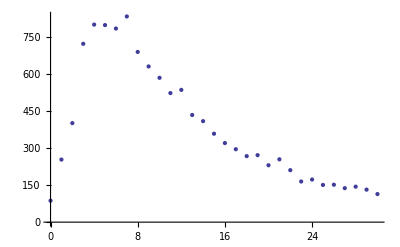

```mathematica
ListPlot[firstActionHistogram,PlotRange->{{0,30},All}]
```

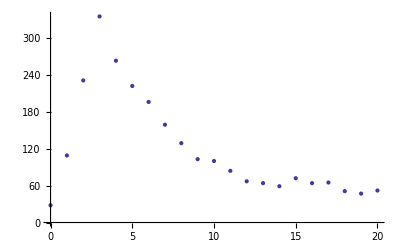

```mathematica
ListPlot[firstHintHistogram,PlotRange->{{0,20},All}]
```

## Score Histogram

### USNA 2005 - 2006

This is from both semesters of 2005-2006

```mathematica
scorehistogram={{0,472},{1,18},{2,12},{3,20},{4,9},{5,15},{6,11},{7,14},{8,11},{9,16},{10,17},{11,13},{12,16},{13,23},{14,30},{15,24},{16,12},{17,8},{18,21},{19,57},{20,26},{21,37},{22,54},{23,35},{24,21},{25,119},{26,26},{27,35},{28,62},{29,33},{30,24},{31,106},{32,42},{33,36},{34,30},{35,32},{36,17},{37,26},{38,50},{39,47},{40,44},{41,31},{42,32},{43,29},{44,49},{45,46},{46,36},{47,43},{48,43},{49,53},{50,95},{51,58},{52,74},{53,84},{54,77},{55,61},{56,82},{57,72},{58,87},{59,74},{60,71},{61,55},{62,64},{63,111},{64,99},{65,62},{66,47},{67,81},{68,129},{69,115},{70,85},{71,83},{72,90},{73,164},{74,172},{75,126},{76,100},{77,126},{78,230},{79,208},{80,150},{81,179},{82,200},{83,329},{84,331},{85,264},{86,161},{87,255},{88,427},{89,431},{90,277},{91,295},{92,596},{93,729},{94,779},{95,330},{96,473},{97,876},{98,1376},{99,2485},{100,2567}};
```

### Analysis

```mathematica
Apply[Plus,Transpose[scorehistogram][[2]]]
```

18575

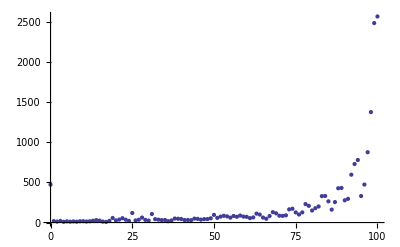

```mathematica
ListPlot[scorehistogram,PlotRange->All]
```

A more careful analysis might weight the problems based on difficulty:  one might expect that more difficult problems would get lower scores.

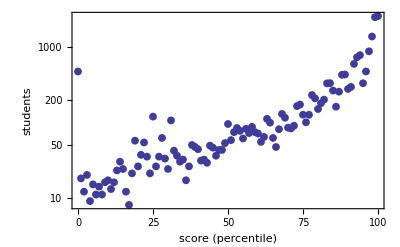

```mathematica
pp1=ListLogPlot[scorehistogram,Frame->True,PlotStyle->{PointSize[0.014]},RotateLabel->False,BaseStyle->{FontSize->12},FrameLabel->{"score (percentile)","students"}]
```

```mathematica
Export["~/log/scorehistogram.eps",pp1,"EPSTIFF",ImageSize->432]
```

Export::nodir: Directory "/home/bvds/log/" does not exist.

$Failed

```mathematica
Export["~/log/scorehistogram.tiff",pp1,ImageSize->432]
```

Export::nodir: Directory "/home/bvds/log/" does not exist.

$Failed

```mathematica
scorefun[score_]=Fit[Map[{#[[1]],Log[#[[2]]]}&,Select[scorehistogram,(10<#[[1]]<90)&]],{1,score},score]
```

2.52251+0.0323738 score

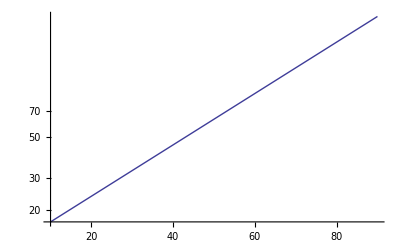

```mathematica
sfp=LogPlot[Exp[scorefun[s]],{s,10,90},DisplayFunction->Identity]
```

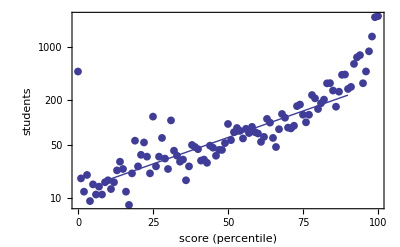

```mathematica
Show[pp1,sfp]
```

## Pause Histogram

Comment from guys at OSU:  should see if power law varies from student to student or by problem type.
From me:  would be neat to include between-session pauses.

### USNA 2005 - 2006

cutoff for maximum time :  use OLI cutoff time of 2 hours.

```mathematica
cutoff=7200;
```

This uses data collected from both semesters in 2005 - 2006

#### All pauses

```mathematica
pausehistogram={{-2681995,1},{-15,1},{0,11180444},{1,1858637},{2,539482},{3,217144},{4,119591},{5,76409},{6,52307},{7,38170},{8,28782},{9,22530},{10,18104},{11,14852},{12,12334},{13,10437},{14,8721},{15,7669},{16,6562},{17,5890},{18,5141},{19,4657},{20,4113},{21,3880},{22,3448},{23,3093},{24,2739},{25,2452},{26,2324},{27,2123},{28,1970},{29,1820},{30,1680},{31,1538},{32,1432},{33,1347},{34,1294},{35,1149},{36,1142},{37,1145},{38,988},{39,949},{40,883},{41,840},{42,788},{43,763},{44,749},{45,662},{46,675},{47,633},{48,604},{49,576},{50,548},{51,549},{52,499},{53,502},{54,507},{55,426},{56,404},{57,415},{58,397},{59,361},{60,394},{61,438},{62,337},{63,334},{64,319},{65,335},{66,315},{67,288},{68,291},{69,291},{70,270},{71,310},{72,270},{73,274},{74,252},{75,234},{76,220},{77,222},{78,227},{79,220},{80,204},{81,206},{82,183},{83,226},{84,208},{85,197},{86,174},{87,168},{88,176},{89,144},{90,191},{91,153},{92,147},{93,142},{94,137},{95,139},{96,154},{97,147},{98,145},{99,124},{100,137},{101,146},{102,130},{103,134},{104,112},{105,122},{106,121},{107,111},{108,86},{109,114},{110,124},{111,120},{112,94},{113,108},{114,117},{115,103},{116,98},{117,102},{118,101},{119,88},{120,82},{121,110},{122,98},{123,101},{124,92},{125,78},{126,67},{127,76},{128,70},{129,96},{130,79},{131,75},{132,72},{133,69},{134,59},{135,86},{136,59},{137,83},{138,65},{139,65},{140,72},{141,52},{142,85},{143,58},{144,67},{145,73},{146,61},{147,62},{148,57},{149,56},{150,55},{151,66},{152,55},{153,50},{154,49},{155,47},{156,59},{157,59},{158,53},{159,43},{160,50},{161,40},{162,41},{163,47},{164,40},{165,52},{166,57},{167,51},{168,53},{169,67},{170,67},{171,50},{172,34},{173,39},{174,33},{175,45},{176,45},{177,37},{178,43},{179,39},{180,46},{181,39},{182,37},{183,34},{184,23},{185,38},{186,34},{187,28},{188,33},{189,42},{190,32},{191,35},{192,44},{193,35},{194,28},{195,27},{196,27},{197,28},{198,38},{199,35},{200,27},{201,36},{202,40},{203,28},{204,37},{205,22},{206,33},{207,32},{208,34},{209,31},{210,34},{211,34},{212,25},{213,30},{214,25},{215,33},{216,29},{217,25},{218,29},{219,23},{220,24},{221,30},{222,16},{223,31},{224,31},{225,30},{226,22},{227,19},{228,21},{229,27},{230,32},{231,22},{232,13},{233,16},{234,24},{235,29},{236,28},{237,19},{238,18},{239,18},{240,26},{241,34},{242,36},{243,20},{244,17},{245,36},{246,28},{247,16},{248,13},{249,17},{250,21},{251,28},{252,18},{253,23},{254,18},{255,16},{256,19},{257,20},{258,12},{259,15},{260,21},{261,11},{262,18},{263,15},{264,18},{265,23},{266,20},{267,17},{268,15},{269,13},{270,15},{271,15},{272,11},{273,16},{274,12},{275,20},{276,17},{277,15},{278,11},{279,18},{280,17},{281,17},{282,12},{283,25},{284,12},{285,15},{286,13},{287,14},{288,16},{289,13},{290,18},{291,12},{292,18},{293,18},{294,18},{295,17},{296,15},{297,12},{298,22},{299,22},{300,28},{301,40},{302,30},{303,16},{304,18},{305,16},{306,25},{307,20},{308,17},{309,13},{310,8},{311,21},{312,11},{313,18},{314,14},{315,16},{316,10},{317,14},{318,9},{319,17},{320,11},{321,8},{322,16},{323,11},{324,8},{325,9},{326,9},{327,4},{328,13},{329,9},{330,9},{331,15},{332,11},{333,16},{334,13},{335,7},{336,15},{337,12},{338,10},{339,11},{340,15},{341,10},{342,6},{343,8},{344,11},{345,11},{346,10},{347,7},{348,12},{349,8},{350,6},{351,4},{352,3},{353,10},{354,10},{355,4},{356,13},{357,11},{358,4},{359,9},{360,6},{361,17},{362,9},{363,4},{364,12},{365,12},{366,7},{367,11},{368,4},{369,7},{370,11},{371,6},{372,11},{373,10},{374,9},{375,9},{376,7},{377,3},{378,9},{379,11},{380,9},{381,6},{382,7},{383,9},{384,4},{385,9},{386,7},{387,9},{388,4},{389,12},{390,6},{391,6},{392,8},{393,5},{394,4},{395,7},{396,2},{397,7},{398,7},{399,11},{400,7},{401,5},{402,3},{403,7},{404,10},{405,12},{406,3},{407,8},{408,8},{409,8},{410,8},{411,4},{412,7},{413,3},{414,4},{415,9},{416,5},{417,7},{418,6},{419,5},{420,12},{421,9},{422,6},{423,9},{424,6},{425,5},{426,5},{427,7},{428,3},{429,7},{430,6},{431,9},{432,6},{433,2},{434,8},{435,5},{436,5},{437,2},{438,7},{439,11},{440,10},{441,9},{442,6},{443,12},{444,4},{445,5},{446,1},{447,4},{448,6},{449,8},{450,7},{451,7},{452,6},{453,11},{454,6},{455,8},{456,3},{457,6},{458,3},{459,6},{460,10},{461,4},{462,2},{463,5},{464,3},{465,5},{466,4},{467,2},{468,5},{469,1},{470,6},{471,4},{472,5},{473,6},{474,5},{475,3},{476,3},{477,3},{478,4},{479,4},{480,10},{481,10},{482,8},{483,5},{484,8},{485,9},{486,1},{487,4},{488,10},{489,5},{490,2},{491,6},{492,6},{493,5},{494,3},{495,5},{496,3},{497,1},{498,5},{499,4},{500,4},{501,4},{502,4},{503,3},{504,4},{505,1},{506,2},{507,10},{508,4},{509,2},{510,8},{511,5},{512,9},{513,2},{514,2},{515,3},{516,2},{517,8},{518,2},{519,2},{520,4},{521,4},{522,7},{524,4},{525,4},{526,1},{527,5},{528,4},{529,2},{530,7},{531,1},{532,7},{533,3},{534,5},{535,3},{536,5},{537,5},{538,3},{539,4},{540,4},{541,4},{542,2},{543,3},{544,2},{545,3},{546,5},{547,6},{548,2},{549,3},{550,3},{551,2},{552,3},{553,2},{554,3},{555,3},{556,1},{557,1},{558,9},{559,5},{560,4},{561,3},{562,5},{563,5},{564,3},{565,4},{566,1},{567,3},{568,2},{569,3},{570,2},{571,3},{572,3},{573,4},{574,3},{575,2},{576,3},{577,4},{578,1},{580,3},{581,5},{582,6},{583,4},{584,4},{585,3},{586,3},{587,5},{588,3},{589,4},{590,6},{591,6},{592,7},{593,10},{594,6},{595,6},{596,4},{597,8},{598,5},{599,6},{600,31},{601,67},{602,32},{603,21},{604,12},{605,6},{606,4},{607,4},{608,3},{609,4},{610,9},{611,6},{612,5},{613,10},{614,5},{615,4},{616,6},{617,1},{618,2},{619,5},{620,3},{621,5},{622,4},{623,4},{624,2},{625,5},{626,3},{627,2},{628,2},{629,1},{630,4},{631,4},{632,2},{633,2},{634,1},{635,2},{636,1},{637,4},{638,4},{639,7},{640,4},{641,3},{642,3},{643,4},{644,4},{645,1},{646,1},{647,3},{648,3},{649,1},{650,3},{651,2},{652,2},{653,5},{655,1},{656,1},{657,3},{658,4},{659,6},{660,2},{661,3},{662,3},{663,1},{664,1},{666,7},{667,6},{668,6},{669,2},{670,3},{671,1},{672,3},{673,2},{674,1},{675,1},{676,2},{677,2},{678,2},{679,4},{680,3},{681,1},{682,1},{683,4},{684,6},{685,3},{686,1},{687,3},{688,2},{689,1},{690,1},{691,2},{692,3},{694,2},{695,4},{696,2},{697,5},{698,3},{699,1},{700,2},{701,1},{702,4},{703,2},{704,1},{705,1},{706,1},{707,3},{708,2},{709,1},{710,2},{711,4},{712,1},{713,1},{714,1},{715,5},{716,2},{717,2},{718,3},{719,5},{720,2},{721,2},{722,2},{724,2},{725,2},{726,3},{730,2},{731,1},{732,2},{733,3},{734,3},{735,1},{736,1},{738,1},{739,2},{740,2},{741,3},{742,1},{743,2},{744,3},{745,2},{748,3},{749,3},{751,1},{752,1},{753,2},{754,3},{755,1},{756,2},{757,1},{759,1},{760,1},{761,1},{762,2},{763,2},{764,2},{765,3},{767,2},{768,2},{769,4},{770,2},{771,1},{772,2},{774,2},{775,1},{777,2},{779,2},{780,4},{781,3},{782,1},{783,3},{785,1},{787,1},{788,1},{789,2},{790,2},{791,4},{792,1},{793,2},{795,1},{796,2},{798,4},{799,2},{802,2},{803,2},{804,1},{805,2},{806,2},{807,3},{808,1},{809,1},{810,2},{811,2},{812,1},{813,6},{814,1},{815,1},{816,1},{817,3},{818,3},{820,1},{822,2},{823,1},{824,3},{825,2},{827,1},{829,2},{831,4},{832,1},{833,1},{834,2},{835,2},{836,1},{838,3},{839,2},{841,1},{842,1},{843,2},{844,1},{846,1},{847,1},{848,1},{849,2},{851,1},{852,1},{853,3},{854,1},{855,2},{856,1},{858,1},{859,1},{860,1},{861,3},{862,2},{863,2},{864,3},{865,2},{867,3},{868,3},{871,1},{872,2},{873,1},{874,2},{876,3},{879,1},{880,2},{883,1},{885,2},{886,1},{888,2},{889,1},{891,1},{892,1},{895,3},{897,1},{898,3},{899,19},{900,3},{901,2},{902,2},{903,2},{904,3},{905,2},{908,3},{909,3},{911,1},{912,1},{913,2},{914,1},{915,2},{916,2},{917,1},{918,4},{919,1},{920,1},{923,1},{925,2},{926,2},{928,1},{929,3},{930,3},{932,3},{934,1},{935,1},{936,1},{939,2},{941,2},{944,2},{945,3},{946,1},{948,1},{949,1},{950,1},{951,1},{952,1},{953,4},{954,2},{955,2},{961,1},{963,1},{965,1},{966,2},{967,2},{968,1},{970,1},{971,1},{972,1},{973,1},{975,1},{976,3},{977,2},{978,1},{980,1},{981,1},{984,1},{985,2},{986,3},{987,1},{989,1},{991,1},{992,2},{993,1},{996,1},{997,2},{998,1},{999,2},{1003,1},{1005,1},{1007,1},{1010,2},{1011,1},{1012,1},{1013,2},{1016,1},{1018,3},{1020,2},{1021,2},{1022,1},{1023,1},{1024,1},{1029,1},{1031,1},{1033,2},{1035,1},{1040,1},{1043,2},{1044,1},{1048,1},{1052,3},{1055,1},{1056,1},{1059,1},{1060,1},{1061,1},{1064,1},{1065,1},{1067,1},{1068,1},{1070,1},{1071,1},{1072,1},{1074,1},{1078,1},{1083,1},{1084,1},{1089,2},{1090,1},{1092,1},{1093,1},{1094,1},{1096,1},{1099,1},{1100,1},{1101,2},{1106,2},{1107,1},{1108,2},{1109,1},{1110,1},{1114,2},{1115,2},{1117,1},{1124,1},{1126,1},{1127,1},{1130,1},{1131,1},{1132,1},{1135,1},{1138,1},{1142,3},{1144,1},{1145,1},{1146,3},{1147,1},{1151,2},{1153,1},{1154,1},{1156,1},{1157,1},{1158,1},{1161,2},{1162,1},{1166,1},{1167,1},{1168,1},{1171,1},{1175,1},{1179,1},{1181,2},{1183,1},{1184,1},{1186,3},{1187,1},{1188,1},{1191,1},{1195,1},{1196,2},{1197,1},{1199,1},{1201,1},{1202,1},{1203,2},{1204,2},{1206,1},{1210,1},{1211,2},{1213,1},{1216,2},{1217,1},{1218,1},{1220,1},{1224,1},{1225,1},{1226,1},{1227,1},{1228,1},{1229,1},{1230,1},{1231,1},{1232,2},{1236,2},{1238,1},{1239,1},{1242,1},{1246,1},{1252,1},{1254,1},{1257,1},{1258,1},{1261,1},{1266,2},{1270,1},{1277,2},{1292,1},{1298,2},{1300,2},{1301,1},{1303,1},{1304,2},{1308,1},{1309,1},{1311,1},{1313,2},{1314,1},{1315,1},{1316,1},{1317,1},{1318,2},{1321,1},{1326,1},{1329,1},{1331,1},{1338,1},{1342,1},{1345,2},{1351,1},{1358,1},{1359,1},{1360,2},{1364,1},{1365,2},{1367,1},{1369,1},{1372,1},{1373,1},{1374,1},{1375,2},{1378,1},{1382,1},{1383,1},{1384,1},{1390,1},{1396,1},{1411,2},{1415,1},{1423,2},{1424,1},{1426,1},{1429,1},{1430,1},{1431,1},{1435,1},{1437,1},{1440,1},{1444,1},{1451,1},{1461,1},{1462,1},{1463,1},{1471,1},{1474,1},{1475,1},{1479,1},{1481,1},{1482,1},{1483,1},{1484,2},{1488,1},{1489,1},{1494,1},{1495,1},{1499,1},{1500,1},{1501,1},{1502,1},{1505,1},{1512,1},{1518,1},{1521,1},{1522,1},{1528,1},{1530,1},{1531,1},{1545,1},{1548,1},{1555,1},{1556,1},{1557,1},{1563,1},{1566,1},{1567,1},{1569,1},{1575,1},{1577,1},{1585,1},{1588,1},{1589,1},{1596,1},{1601,1},{1606,1},{1607,1},{1608,1},{1612,1},{1614,1},{1615,3},{1616,1},{1618,1},{1622,1},{1631,1},{1632,1},{1635,1},{1638,1},{1644,1},{1645,1},{1647,1},{1658,1},{1660,1},{1661,1},{1663,1},{1671,1},{1672,1},{1676,2},{1683,1},{1696,1},{1698,1},{1703,1},{1708,2},{1711,1},{1719,1},{1734,1},{1738,1},{1742,1},{1743,1},{1749,1},{1755,1},{1762,1},{1768,1},{1769,1},{1772,1},{1776,1},{1782,1},{1789,1},{1790,1},{1791,1},{1792,1},{1799,1},{1802,1},{1818,1},{1828,1},{1830,1},{1838,1},{1840,1},{1848,1},{1849,1},{1854,1},{1857,1},{1859,1},{1861,1},{1865,2},{1867,1},{1872,1},{1880,1},{1882,2},{1883,1},{1884,1},{1887,1},{1895,2},{1899,1},{1907,2},{1910,1},{1921,1},{1925,2},{1928,1},{1929,2},{1941,1},{1965,1},{1983,1},{1986,1},{1993,1},{1994,2},{1995,1},{2001,1},{2003,1},{2022,1},{2037,1},{2041,1},{2045,1},{2049,1},{2056,1},{2059,1},{2063,1},{2066,1},{2069,1},{2070,1},{2073,1},{2078,1},{2081,1},{2083,1},{2086,1},{2096,2},{2098,1},{2102,1},{2103,1},{2110,1},{2120,1},{2137,1},{2142,1},{2149,1},{2155,1},{2170,1},{2172,1},{2181,1},{2189,1},{2190,1},{2200,1},{2206,1},{2208,1},{2216,2},{2222,1},{2232,1},{2234,2},{2243,1},{2251,1},{2254,1},{2261,1},{2267,1},{2271,1},{2272,1},{2285,1},{2287,1},{2289,1},{2297,1},{2304,1},{2309,1},{2310,1},{2313,1},{2314,1},{2318,1},{2325,1},{2340,1},{2344,1},{2346,1},{2347,2},{2364,1},{2374,1},{2375,1},{2378,1},{2382,1},{2391,1},{2398,2},{2411,1},{2412,1},{2413,1},{2415,1},{2422,1},{2431,1},{2449,1},{2451,1},{2458,1},{2475,1},{2489,1},{2505,1},{2538,1},{2545,1},{2546,1},{2562,1},{2569,1},{2570,1},{2575,1},{2579,1},{2595,1},{2605,1},{2613,1},{2628,1},{2630,1},{2644,1},{2651,1},{2660,1},{2668,1},{2669,1},{2673,1},{2674,1},{2675,1},{2676,1},{2680,1},{2683,1},{2687,1},{2715,1},{2720,1},{2723,1},{2731,1},{2748,1},{2749,1},{2751,1},{2765,1},{2801,1},{2819,1},{2827,1},{2830,1},{2833,1},{2834,1},{2842,2},{2846,1},{2856,1},{2857,1},{2859,1},{2862,1},{2866,1},{2872,1},{2878,1},{2888,1},{2889,1},{2896,1},{2927,1},{2931,1},{2933,2},{2955,1},{2963,1},{2972,1},{2983,1},{2996,1},{3012,1},{3024,1},{3029,1},{3030,1},{3033,1},{3048,1},{3052,1},{3062,1},{3064,1},{3067,1},{3070,1},{3071,1},{3073,1},{3075,1},{3091,1},{3106,1},{3107,1},{3125,1},{3153,1},{3187,1},{3214,1},{3215,1},{3258,2},{3259,1},{3314,1},{3323,1},{3326,1},{3335,1},{3346,1},{3358,1},{3359,1},{3373,1},{3411,1},{3420,1},{3421,1},{3423,1},{3430,1},{3441,1},{3484,1},{3504,1},{3537,1},{3546,1},{3555,1},{3572,1},{3592,1},{3600,1},{3610,1},{3616,1},{3623,1},{3652,1},{3657,1},{3687,1},{3701,1},{3714,1},{3715,1},{3733,1},{3758,1},{3782,1},{3807,1},{3815,1},{3831,1},{3835,1},{3854,1},{3856,2},{3873,1},{3878,1},{3888,1},{3895,1},{3903,1},{3910,1},{3927,1},{3940,1},{3953,1},{3973,1},{4021,1},{4033,1},{4054,1},{4107,2},{4117,1},{4151,1},{4152,1},{4154,1},{4179,1},{4211,1},{4252,1},{4267,1},{4274,1},{4275,1},{4277,1},{4297,1},{4341,1},{4361,1},{4374,1},{4380,1},{4395,1},{4423,1},{4427,1},{4444,1},{4448,1},{4466,1},{4517,1},{4557,1},{4592,1},{4595,1},{4673,1},{4680,1},{4703,1},{4768,1},{4798,1},{4812,1},{4848,1},{4872,1},{4902,1},{4910,1},{4959,1},{4999,1},{5003,1},{5021,1},{5083,1},{5106,1},{5266,1},{5270,1},{5302,1},{5304,1},{5399,1},{5431,1},{5531,1},{5533,1},{5553,1},{5554,1},{5563,1},{5715,1},{5793,1},{5806,1},{5815,1},{6147,1},{6227,1},{6359,1},{6362,1},{6380,1},{6452,1},{6509,1},{6645,1},{6648,1},{6668,1},{6688,1},{6907,1},{7004,1},{2682009,1}};
```

```mathematica
logpausehistogram={{1,1858637},{1.99526231496888,539482},{3.16227766016838,217144},{3.98107170553497,119591},{5.01187233627272,76409},{6.30957344480193,45238.5},{7.94328234724282,28782},{10,18495.3333333333},{12.5892541179417,10497.3333333333},{15.8489319246111,6707},{19.9526231496888,4247.8},{25.1188643150958,2450.16666666667},{31.6227766016838,1465.71428571429},{39.8107170553497,916.333333333333},{50.1187233627272,548.75},{63.0957344480194,341.785714285714},{79.4328234724282,216.578947368421},{100,131.739130434783},{125.892541179417,83.551724137931},{158.489319246111,52.8611111111111},{199.526231496888,32.0217391304348},{251.188643150958,19.948275862069},{316.227766016838,13.7123287671233},{398.107170553498,7.18478260869565},{501.187233627273,4.41379310344828},{630.957344480193,4.26206896551724},{794.328234724282,1.5},{1000,0.930735930735931},{1258.92541179417,0.486206896551724},{1584.89319246111,0.278688524590164},{1995.26231496888,0.197826086956522},{2511.88643150958,0.132758620689655},{3162.27766016838,0.0958904109589041},{3981.07170553498,0.065359477124183},{5011.87233627272,0.0267934312878133},{6309.57344480194,0.0116758241758242}};
```

#### Pauses not associated with loosing focus (a)

```mathematica
pausehistograma={{-15,1},{0,11161166},{1,1841672},{2,526213},{3,209263},{4,114281},{5,72236},{6,48910},{7,35319},{8,26377},{9,20447},{10,16201},{11,13202},{12,10837},{13,9118},{14,7501},{15,6565},{16,5593},{17,4887},{18,4292},{19,3841},{20,3367},{21,3027},{22,2709},{23,2480},{24,2151},{25,1930},{26,1807},{27,1624},{28,1508},{29,1362},{30,1225},{31,1166},{32,1032},{33,963},{34,936},{35,844},{36,809},{37,838},{38,708},{39,653},{40,621},{41,569},{42,555},{43,516},{44,486},{45,442},{46,451},{47,428},{48,411},{49,387},{50,361},{51,354},{52,345},{53,333},{54,316},{55,276},{56,262},{57,270},{58,265},{59,228},{60,258},{61,249},{62,201},{63,220},{64,192},{65,199},{66,214},{67,185},{68,196},{69,199},{70,172},{71,184},{72,160},{73,174},{74,157},{75,146},{76,134},{77,139},{78,134},{79,129},{80,131},{81,118},{82,113},{83,135},{84,129},{85,107},{86,102},{87,100},{88,106},{89,74},{90,121},{91,89},{92,81},{93,78},{94,93},{95,80},{96,80},{97,92},{98,73},{99,76},{100,87},{101,90},{102,70},{103,81},{104,65},{105,56},{106,68},{107,70},{108,52},{109,61},{110,73},{111,61},{112,68},{113,64},{114,57},{115,60},{116,55},{117,55},{118,49},{119,49},{120,41},{121,55},{122,44},{123,58},{124,53},{125,41},{126,36},{127,41},{128,38},{129,52},{130,42},{131,35},{132,39},{133,32},{134,23},{135,44},{136,33},{137,45},{138,40},{139,33},{140,43},{141,28},{142,44},{143,32},{144,39},{145,44},{146,34},{147,29},{148,26},{149,29},{150,24},{151,36},{152,25},{153,24},{154,25},{155,24},{156,33},{157,37},{158,26},{159,19},{160,24},{161,22},{162,22},{163,24},{164,20},{165,24},{166,32},{167,31},{168,25},{169,28},{170,16},{171,23},{172,11},{173,21},{174,18},{175,22},{176,22},{177,17},{178,24},{179,22},{180,25},{181,21},{182,22},{183,16},{184,11},{185,17},{186,16},{187,13},{188,12},{189,12},{190,15},{191,16},{192,20},{193,20},{194,16},{195,12},{196,12},{197,10},{198,19},{199,8},{200,15},{201,13},{202,23},{203,9},{204,18},{205,10},{206,17},{207,15},{208,17},{209,12},{210,17},{211,16},{212,17},{213,7},{214,12},{215,18},{216,15},{217,13},{218,10},{219,13},{220,11},{221,18},{222,9},{223,17},{224,14},{225,14},{226,16},{227,11},{228,10},{229,10},{230,10},{231,8},{232,8},{233,6},{234,4},{235,10},{236,10},{237,8},{238,8},{239,9},{240,8},{241,10},{242,12},{243,5},{244,5},{245,17},{246,9},{247,8},{248,6},{249,9},{250,8},{251,12},{252,8},{253,10},{254,6},{255,4},{256,4},{257,8},{258,4},{259,4},{260,11},{261,6},{262,9},{263,9},{264,8},{265,10},{266,9},{267,6},{268,6},{269,4},{270,3},{271,5},{272,3},{273,9},{274,4},{275,11},{276,7},{277,6},{278,5},{279,7},{280,9},{281,7},{282,5},{283,12},{284,6},{285,6},{286,6},{287,5},{288,6},{289,4},{290,6},{291,6},{292,4},{293,8},{294,11},{295,6},{296,5},{297,4},{298,7},{299,9},{300,5},{301,2},{302,11},{303,4},{304,9},{305,4},{306,7},{307,7},{308,7},{309,3},{310,2},{311,9},{312,5},{313,4},{314,4},{315,5},{316,5},{317,7},{318,1},{319,5},{320,4},{321,2},{322,5},{323,3},{324,3},{325,4},{326,1},{328,6},{329,3},{330,4},{331,6},{332,3},{333,9},{334,7},{335,3},{336,3},{337,4},{338,4},{339,4},{340,9},{341,2},{342,3},{343,4},{344,6},{345,4},{346,4},{347,2},{348,5},{349,2},{350,3},{351,1},{352,1},{353,2},{354,7},{356,5},{357,2},{358,2},{359,5},{360,2},{361,3},{362,2},{363,2},{364,3},{365,4},{366,2},{367,3},{369,4},{370,6},{371,2},{372,3},{373,3},{375,4},{376,2},{377,1},{378,3},{379,3},{380,2},{381,3},{382,3},{383,2},{384,1},{385,4},{386,2},{387,4},{388,3},{389,4},{390,1},{391,4},{392,1},{393,2},{394,1},{395,1},{396,1},{397,3},{398,3},{399,2},{400,3},{401,2},{402,1},{403,1},{404,5},{405,1},{406,1},{407,3},{408,2},{409,3},{410,2},{411,3},{412,4},{413,1},{414,2},{415,3},{416,2},{418,3},{422,1},{423,4},{424,3},{425,1},{426,2},{428,2},{429,3},{430,3},{431,6},{432,2},{434,5},{436,1},{438,2},{439,3},{440,4},{441,6},{442,1},{443,3},{444,1},{445,2},{448,3},{449,1},{450,4},{451,1},{452,4},{453,3},{454,3},{455,2},{456,1},{457,1},{458,1},{459,1},{460,2},{461,1},{462,1},{463,3},{464,1},{465,4},{467,1},{468,3},{469,1},{470,3},{471,2},{473,1},{474,1},{475,1},{477,1},{478,2},{479,1},{480,2},{481,2},{482,1},{483,3},{484,6},{485,4},{486,1},{488,2},{489,2},{491,4},{492,2},{494,1},{495,2},{496,1},{498,1},{499,1},{500,2},{502,1},{503,1},{504,2},{506,1},{507,1},{510,2},{512,2},{513,1},{514,1},{515,1},{517,4},{521,1},{522,1},{524,1},{525,1},{527,1},{529,1},{530,3},{532,1},{534,2},{536,2},{537,2},{538,1},{539,1},{540,1},{542,1},{543,1},{544,1},{545,2},{546,3},{547,5},{548,1},{550,2},{551,2},{552,2},{553,1},{554,2},{555,2},{558,4},{559,2},{560,1},{561,1},{562,1},{564,2},{565,1},{567,1},{568,1},{569,1},{570,1},{572,1},{573,2},{574,1},{575,1},{576,1},{577,2},{580,1},{582,1},{584,2},{585,1},{586,1},{587,1},{589,1},{590,2},{591,1},{592,1},{593,3},{594,1},{598,2},{599,2},{601,1},{602,2},{603,2},{604,1},{609,1},{610,4},{613,1},{614,1},{615,2},{616,3},{617,1},{619,2},{620,1},{622,1},{623,1},{624,1},{625,2},{626,1},{628,1},{630,1},{632,1},{634,1},{639,1},{645,1},{646,1},{649,1},{657,2},{658,1},{659,2},{661,1},{662,1},{666,3},{667,1},{668,1},{672,1},{676,1},{678,1},{679,2},{680,1},{681,1},{695,1},{701,1},{707,1},{710,1},{715,2},{724,1},{726,1},{732,1},{735,1},{736,1},{741,2},{743,1},{744,1},{751,1},{763,1},{765,1},{768,1},{769,1},{771,1},{774,1},{783,1},{791,1},{793,1},{802,1},{813,1},{817,2},{818,1},{829,1},{838,2},{841,1},{844,1},{849,1},{860,1},{863,1},{867,1},{880,1},{885,1},{892,1},{899,1},{903,1},{908,1},{913,1},{918,1},{920,1},{930,1},{935,1},{936,1},{939,1},{945,1},{968,1},{978,1},{986,1},{996,1},{997,1},{1005,1},{1010,2},{1016,1},{1020,1},{1023,1},{1033,1},{1040,1},{1068,1},{1070,1},{1071,1},{1084,1},{1144,1},{1146,1},{1156,1},{1157,1},{1158,1},{1211,1},{1217,1},{1227,1},{1232,1},{1314,1},{1315,1},{1318,1},{1345,1},{1359,1},{1378,1},{1461,1},{1462,1},{1500,1},{1531,1},{1548,1},{1557,1},{1606,1},{1614,1},{1647,1},{1749,1},{1776,1},{1799,1},{1884,1},{1910,1},{2059,1},{2243,1},{2309,1},{2340,1},{2347,1},{2613,1},{2676,1},{2801,1},{2827,1},{2933,1},{3064,1},{3067,1},{3420,1},{4107,1},{4423,1},{4592,1},{5533,1},{6362,1}};
```

```mathematica
logpausehistograma={{1,1841672},{1.99526231496888,526213},{3.16227766016838,209263},{3.98107170553497,114281},{5.01187233627272,72236},{6.30957344480193,42114.5},{7.94328234724282,26377},{10,16616.6666666667},{12.5892541179417,9152},{15.8489319246111,5681.66666666667},{19.9526231496888,3447.2},{25.1188643150958,1916.66666666667},{31.6227766016838,1075.42857142857},{39.8107170553497,639.444444444444},{50.1187233627272,363.833333333333},{63.0957344480194,217.714285714286},{79.4328234724282,130.105263157895},{100,76.7391304347826},{125.892541179417,44.3103448275862},{158.489319246111,26.4444444444444},{199.526231496888,15.2391304347826},{251.188643150958,8.05172413793103},{316.227766016838,4.86301369863014},{398.107170553498,2.28260869565217},{501.187233627273,1.38793103448276},{630.957344480193,0.641379310344828},{794.328234724282,0.206521739130435},{1000,0.125541125541126},{1258.92541179417,0.0517241379310345},{1584.89319246111,0.0300546448087432},{1995.26231496888,0.00869565217391304},{2511.88643150958,0.0120689655172414},{3162.27766016838,0.00684931506849315},{3981.07170553498,0.00217864923747277},{5011.87233627272,0.0017286084701815},{6309.57344480194,0.000686813186813187}};
```

#### Pauses associated with loosing focus (b)

```mathematica
pausehistogramb={{-2681995,1},{0,19278},{1,16965},{2,13269},{3,7881},{4,5310},{5,4173},{6,3397},{7,2851},{8,2405},{9,2083},{10,1903},{11,1650},{12,1497},{13,1319},{14,1220},{15,1104},{16,969},{17,1003},{18,849},{19,816},{20,746},{21,853},{22,739},{23,613},{24,588},{25,522},{26,517},{27,499},{28,462},{29,458},{30,455},{31,372},{32,400},{33,384},{34,358},{35,305},{36,333},{37,307},{38,280},{39,296},{40,262},{41,271},{42,233},{43,247},{44,263},{45,220},{46,224},{47,205},{48,193},{49,189},{50,187},{51,195},{52,154},{53,169},{54,191},{55,150},{56,142},{57,145},{58,132},{59,133},{60,136},{61,189},{62,136},{63,114},{64,127},{65,136},{66,101},{67,103},{68,95},{69,92},{70,98},{71,126},{72,110},{73,100},{74,95},{75,88},{76,86},{77,83},{78,93},{79,91},{80,73},{81,88},{82,70},{83,91},{84,79},{85,90},{86,72},{87,68},{88,70},{89,70},{90,70},{91,64},{92,66},{93,64},{94,44},{95,59},{96,74},{97,55},{98,72},{99,48},{100,50},{101,56},{102,60},{103,53},{104,47},{105,66},{106,53},{107,41},{108,34},{109,53},{110,51},{111,59},{112,26},{113,44},{114,60},{115,43},{116,43},{117,47},{118,52},{119,39},{120,41},{121,55},{122,54},{123,43},{124,39},{125,37},{126,31},{127,35},{128,32},{129,44},{130,37},{131,40},{132,33},{133,37},{134,36},{135,42},{136,26},{137,38},{138,25},{139,32},{140,29},{141,24},{142,41},{143,26},{144,28},{145,29},{146,27},{147,33},{148,31},{149,27},{150,31},{151,30},{152,30},{153,26},{154,24},{155,23},{156,26},{157,22},{158,27},{159,24},{160,26},{161,18},{162,19},{163,23},{164,20},{165,28},{166,25},{167,20},{168,28},{169,39},{170,51},{171,27},{172,23},{173,18},{174,15},{175,23},{176,23},{177,20},{178,19},{179,17},{180,21},{181,18},{182,15},{183,18},{184,12},{185,21},{186,18},{187,15},{188,21},{189,30},{190,17},{191,19},{192,24},{193,15},{194,12},{195,15},{196,15},{197,18},{198,19},{199,27},{200,12},{201,23},{202,17},{203,19},{204,19},{205,12},{206,16},{207,17},{208,17},{209,19},{210,17},{211,18},{212,8},{213,23},{214,13},{215,15},{216,14},{217,12},{218,19},{219,10},{220,13},{221,12},{222,7},{223,14},{224,17},{225,16},{226,6},{227,8},{228,11},{229,17},{230,22},{231,14},{232,5},{233,10},{234,20},{235,19},{236,18},{237,11},{238,10},{239,9},{240,18},{241,24},{242,24},{243,15},{244,12},{245,19},{246,19},{247,8},{248,7},{249,8},{250,13},{251,16},{252,10},{253,13},{254,12},{255,12},{256,15},{257,12},{258,8},{259,11},{260,10},{261,5},{262,9},{263,6},{264,10},{265,13},{266,11},{267,11},{268,9},{269,9},{270,12},{271,10},{272,8},{273,7},{274,8},{275,9},{276,10},{277,9},{278,6},{279,11},{280,8},{281,10},{282,7},{283,13},{284,6},{285,9},{286,7},{287,9},{288,10},{289,9},{290,12},{291,6},{292,14},{293,10},{294,7},{295,11},{296,10},{297,8},{298,15},{299,13},{300,23},{301,38},{302,19},{303,12},{304,9},{305,12},{306,18},{307,13},{308,10},{309,10},{310,6},{311,12},{312,6},{313,14},{314,10},{315,11},{316,5},{317,7},{318,8},{319,12},{320,7},{321,6},{322,11},{323,8},{324,5},{325,5},{326,8},{327,4},{328,7},{329,6},{330,5},{331,9},{332,8},{333,7},{334,6},{335,4},{336,12},{337,8},{338,6},{339,7},{340,6},{341,8},{342,3},{343,4},{344,5},{345,7},{346,6},{347,5},{348,7},{349,6},{350,3},{351,3},{352,2},{353,8},{354,3},{355,4},{356,8},{357,9},{358,2},{359,4},{360,4},{361,14},{362,7},{363,2},{364,9},{365,8},{366,5},{367,8},{368,4},{369,3},{370,5},{371,4},{372,8},{373,7},{374,9},{375,5},{376,5},{377,2},{378,6},{379,8},{380,7},{381,3},{382,4},{383,7},{384,3},{385,5},{386,5},{387,5},{388,1},{389,8},{390,5},{391,2},{392,7},{393,3},{394,3},{395,6},{396,1},{397,4},{398,4},{399,9},{400,4},{401,3},{402,2},{403,6},{404,5},{405,11},{406,2},{407,5},{408,6},{409,5},{410,6},{411,1},{412,3},{413,2},{414,2},{415,6},{416,3},{417,7},{418,3},{419,5},{420,12},{421,9},{422,5},{423,5},{424,3},{425,4},{426,3},{427,7},{428,1},{429,4},{430,3},{431,3},{432,4},{433,2},{434,3},{435,5},{436,4},{437,2},{438,5},{439,8},{440,6},{441,3},{442,5},{443,9},{444,3},{445,3},{446,1},{447,4},{448,3},{449,7},{450,3},{451,6},{452,2},{453,8},{454,3},{455,6},{456,2},{457,5},{458,2},{459,5},{460,8},{461,3},{462,1},{463,2},{464,2},{465,1},{466,4},{467,1},{468,2},{470,3},{471,2},{472,5},{473,5},{474,4},{475,2},{476,3},{477,2},{478,2},{479,3},{480,8},{481,8},{482,7},{483,2},{484,2},{485,5},{487,4},{488,8},{489,3},{490,2},{491,2},{492,4},{493,5},{494,2},{495,3},{496,2},{497,1},{498,4},{499,3},{500,2},{501,4},{502,3},{503,2},{504,2},{505,1},{506,1},{507,9},{508,4},{509,2},{510,6},{511,5},{512,7},{513,1},{514,1},{515,2},{516,2},{517,4},{518,2},{519,2},{520,4},{521,3},{522,6},{524,3},{525,3},{526,1},{527,4},{528,4},{529,1},{530,4},{531,1},{532,6},{533,3},{534,3},{535,3},{536,3},{537,3},{538,2},{539,3},{540,3},{541,4},{542,1},{543,2},{544,1},{545,1},{546,2},{547,1},{548,1},{549,3},{550,1},{552,1},{553,1},{554,1},{555,1},{556,1},{557,1},{558,5},{559,3},{560,3},{561,2},{562,4},{563,5},{564,1},{565,3},{566,1},{567,2},{568,1},{569,2},{570,1},{571,3},{572,2},{573,2},{574,2},{575,1},{576,2},{577,2},{578,1},{580,2},{581,5},{582,5},{583,4},{584,2},{585,2},{586,2},{587,4},{588,3},{589,3},{590,4},{591,5},{592,6},{593,7},{594,5},{595,6},{596,4},{597,8},{598,3},{599,4},{600,31},{601,66},{602,30},{603,19},{604,11},{605,6},{606,4},{607,4},{608,3},{609,3},{610,5},{611,6},{612,5},{613,9},{614,4},{615,2},{616,3},{618,2},{619,3},{620,2},{621,5},{622,3},{623,3},{624,1},{625,3},{626,2},{627,2},{628,1},{629,1},{630,3},{631,4},{632,1},{633,2},{635,2},{636,1},{637,4},{638,4},{639,6},{640,4},{641,3},{642,3},{643,4},{644,4},{647,3},{648,3},{650,3},{651,2},{652,2},{653,5},{655,1},{656,1},{657,1},{658,3},{659,4},{660,2},{661,2},{662,2},{663,1},{664,1},{666,4},{667,5},{668,5},{669,2},{670,3},{671,1},{672,2},{673,2},{674,1},{675,1},{676,1},{677,2},{678,1},{679,2},{680,2},{682,1},{683,4},{684,6},{685,3},{686,1},{687,3},{688,2},{689,1},{690,1},{691,2},{692,3},{694,2},{695,3},{696,2},{697,5},{698,3},{699,1},{700,2},{702,4},{703,2},{704,1},{705,1},{706,1},{707,2},{708,2},{709,1},{710,1},{711,4},{712,1},{713,1},{714,1},{715,3},{716,2},{717,2},{718,3},{719,5},{720,2},{721,2},{722,2},{724,1},{725,2},{726,2},{730,2},{731,1},{732,1},{733,3},{734,3},{738,1},{739,2},{740,2},{741,1},{742,1},{743,1},{744,2},{745,2},{748,3},{749,3},{752,1},{753,2},{754,3},{755,1},{756,2},{757,1},{759,1},{760,1},{761,1},{762,2},{763,1},{764,2},{765,2},{767,2},{768,1},{769,3},{770,2},{772,2},{774,1},{775,1},{777,2},{779,2},{780,4},{781,3},{782,1},{783,2},{785,1},{787,1},{788,1},{789,2},{790,2},{791,3},{792,1},{793,1},{795,1},{796,2},{798,4},{799,2},{802,1},{803,2},{804,1},{805,2},{806,2},{807,3},{808,1},{809,1},{810,2},{811,2},{812,1},{813,5},{814,1},{815,1},{816,1},{817,1},{818,2},{820,1},{822,2},{823,1},{824,3},{825,2},{827,1},{829,1},{831,4},{832,1},{833,1},{834,2},{835,2},{836,1},{838,1},{839,2},{842,1},{843,2},{846,1},{847,1},{848,1},{849,1},{851,1},{852,1},{853,3},{854,1},{855,2},{856,1},{858,1},{859,1},{861,3},{862,2},{863,1},{864,3},{865,2},{867,2},{868,3},{871,1},{872,2},{873,1},{874,2},{876,3},{879,1},{880,1},{883,1},{885,1},{886,1},{888,2},{889,1},{891,1},{895,3},{897,1},{898,3},{899,18},{900,3},{901,2},{902,2},{903,1},{904,3},{905,2},{908,2},{909,3},{911,1},{912,1},{913,1},{914,1},{915,2},{916,2},{917,1},{918,3},{919,1},{923,1},{925,2},{926,2},{928,1},{929,3},{930,2},{932,3},{934,1},{939,1},{941,2},{944,2},{945,2},{946,1},{948,1},{949,1},{950,1},{951,1},{952,1},{953,4},{954,2},{955,2},{961,1},{963,1},{965,1},{966,2},{967,2},{970,1},{971,1},{972,1},{973,1},{975,1},{976,3},{977,2},{980,1},{981,1},{984,1},{985,2},{986,2},{987,1},{989,1},{991,1},{992,2},{993,1},{997,1},{998,1},{999,2},{1003,1},{1007,1},{1011,1},{1012,1},{1013,2},{1018,3},{1020,1},{1021,2},{1022,1},{1024,1},{1029,1},{1031,1},{1033,1},{1035,1},{1043,2},{1044,1},{1048,1},{1052,3},{1055,1},{1056,1},{1059,1},{1060,1},{1061,1},{1064,1},{1065,1},{1067,1},{1072,1},{1074,1},{1078,1},{1083,1},{1089,2},{1090,1},{1092,1},{1093,1},{1094,1},{1096,1},{1099,1},{1100,1},{1101,2},{1106,2},{1107,1},{1108,2},{1109,1},{1110,1},{1114,2},{1115,2},{1117,1},{1124,1},{1126,1},{1127,1},{1130,1},{1131,1},{1132,1},{1135,1},{1138,1},{1142,3},{1145,1},{1146,2},{1147,1},{1151,2},{1153,1},{1154,1},{1161,2},{1162,1},{1166,1},{1167,1},{1168,1},{1171,1},{1175,1},{1179,1},{1181,2},{1183,1},{1184,1},{1186,3},{1187,1},{1188,1},{1191,1},{1195,1},{1196,2},{1197,1},{1199,1},{1201,1},{1202,1},{1203,2},{1204,2},{1206,1},{1210,1},{1211,1},{1213,1},{1216,2},{1218,1},{1220,1},{1224,1},{1225,1},{1226,1},{1228,1},{1229,1},{1230,1},{1231,1},{1232,1},{1236,2},{1238,1},{1239,1},{1242,1},{1246,1},{1252,1},{1254,1},{1257,1},{1258,1},{1261,1},{1266,2},{1270,1},{1277,2},{1292,1},{1298,2},{1300,2},{1301,1},{1303,1},{1304,2},{1308,1},{1309,1},{1311,1},{1313,2},{1316,1},{1317,1},{1318,1},{1321,1},{1326,1},{1329,1},{1331,1},{1338,1},{1342,1},{1345,1},{1351,1},{1358,1},{1360,2},{1364,1},{1365,2},{1367,1},{1369,1},{1372,1},{1373,1},{1374,1},{1375,2},{1382,1},{1383,1},{1384,1},{1390,1},{1396,1},{1411,2},{1415,1},{1423,2},{1424,1},{1426,1},{1429,1},{1430,1},{1431,1},{1435,1},{1437,1},{1440,1},{1444,1},{1451,1},{1463,1},{1471,1},{1474,1},{1475,1},{1479,1},{1481,1},{1482,1},{1483,1},{1484,2},{1488,1},{1489,1},{1494,1},{1495,1},{1499,1},{1501,1},{1502,1},{1505,1},{1512,1},{1518,1},{1521,1},{1522,1},{1528,1},{1530,1},{1545,1},{1555,1},{1556,1},{1563,1},{1566,1},{1567,1},{1569,1},{1575,1},{1577,1},{1585,1},{1588,1},{1589,1},{1596,1},{1601,1},{1607,1},{1608,1},{1612,1},{1615,3},{1616,1},{1618,1},{1622,1},{1631,1},{1632,1},{1635,1},{1638,1},{1644,1},{1645,1},{1658,1},{1660,1},{1661,1},{1663,1},{1671,1},{1672,1},{1676,2},{1683,1},{1696,1},{1698,1},{1703,1},{1708,2},{1711,1},{1719,1},{1734,1},{1738,1},{1742,1},{1743,1},{1755,1},{1762,1},{1768,1},{1769,1},{1772,1},{1782,1},{1789,1},{1790,1},{1791,1},{1792,1},{1802,1},{1818,1},{1828,1},{1830,1},{1838,1},{1840,1},{1848,1},{1849,1},{1854,1},{1857,1},{1859,1},{1861,1},{1865,2},{1867,1},{1872,1},{1880,1},{1882,2},{1883,1},{1887,1},{1895,2},{1899,1},{1907,2},{1921,1},{1925,2},{1928,1},{1929,2},{1941,1},{1965,1},{1983,1},{1986,1},{1993,1},{1994,2},{1995,1},{2001,1},{2003,1},{2022,1},{2037,1},{2041,1},{2045,1},{2049,1},{2056,1},{2063,1},{2066,1},{2069,1},{2070,1},{2073,1},{2078,1},{2081,1},{2083,1},{2086,1},{2096,2},{2098,1},{2102,1},{2103,1},{2110,1},{2120,1},{2137,1},{2142,1},{2149,1},{2155,1},{2170,1},{2172,1},{2181,1},{2189,1},{2190,1},{2200,1},{2206,1},{2208,1},{2216,2},{2222,1},{2232,1},{2234,2},{2251,1},{2254,1},{2261,1},{2267,1},{2271,1},{2272,1},{2285,1},{2287,1},{2289,1},{2297,1},{2304,1},{2310,1},{2313,1},{2314,1},{2318,1},{2325,1},{2344,1},{2346,1},{2347,1},{2364,1},{2374,1},{2375,1},{2378,1},{2382,1},{2391,1},{2398,2},{2411,1},{2412,1},{2413,1},{2415,1},{2422,1},{2431,1},{2449,1},{2451,1},{2458,1},{2475,1},{2489,1},{2505,1},{2538,1},{2545,1},{2546,1},{2562,1},{2569,1},{2570,1},{2575,1},{2579,1},{2595,1},{2605,1},{2628,1},{2630,1},{2644,1},{2651,1},{2660,1},{2668,1},{2669,1},{2673,1},{2674,1},{2675,1},{2680,1},{2683,1},{2687,1},{2715,1},{2720,1},{2723,1},{2731,1},{2748,1},{2749,1},{2751,1},{2765,1},{2819,1},{2830,1},{2833,1},{2834,1},{2842,2},{2846,1},{2856,1},{2857,1},{2859,1},{2862,1},{2866,1},{2872,1},{2878,1},{2888,1},{2889,1},{2896,1},{2927,1},{2931,1},{2933,1},{2955,1},{2963,1},{2972,1},{2983,1},{2996,1},{3012,1},{3024,1},{3029,1},{3030,1},{3033,1},{3048,1},{3052,1},{3062,1},{3070,1},{3071,1},{3073,1},{3075,1},{3091,1},{3106,1},{3107,1},{3125,1},{3153,1},{3187,1},{3214,1},{3215,1},{3258,2},{3259,1},{3314,1},{3323,1},{3326,1},{3335,1},{3346,1},{3358,1},{3359,1},{3373,1},{3411,1},{3421,1},{3423,1},{3430,1},{3441,1},{3484,1},{3504,1},{3537,1},{3546,1},{3555,1},{3572,1},{3592,1},{3600,1},{3610,1},{3616,1},{3623,1},{3652,1},{3657,1},{3687,1},{3701,1},{3714,1},{3715,1},{3733,1},{3758,1},{3782,1},{3807,1},{3815,1},{3831,1},{3835,1},{3854,1},{3856,2},{3873,1},{3878,1},{3888,1},{3895,1},{3903,1},{3910,1},{3927,1},{3940,1},{3953,1},{3973,1},{4021,1},{4033,1},{4054,1},{4107,1},{4117,1},{4151,1},{4152,1},{4154,1},{4179,1},{4211,1},{4252,1},{4267,1},{4274,1},{4275,1},{4277,1},{4297,1},{4341,1},{4361,1},{4374,1},{4380,1},{4395,1},{4427,1},{4444,1},{4448,1},{4466,1},{4517,1},{4557,1},{4595,1},{4673,1},{4680,1},{4703,1},{4768,1},{4798,1},{4812,1},{4848,1},{4872,1},{4902,1},{4910,1},{4959,1},{4999,1},{5003,1},{5021,1},{5083,1},{5106,1},{5266,1},{5270,1},{5302,1},{5304,1},{5399,1},{5431,1},{5531,1},{5553,1},{5554,1},{5563,1},{5715,1},{5793,1},{5806,1},{5815,1},{6147,1},{6227,1},{6359,1},{6380,1},{6452,1},{6509,1},{6645,1},{6648,1},{6668,1},{6688,1},{6907,1},{7004,1},{2682009,1}};

logpausehistogramb={{1,16965},{1.99526231496888,13269},{3.16227766016838,7881},{3.98107170553497,5310},{5.01187233627272,4173},{6.30957344480193,3124},{7.94328234724282,2405},{10,1878.66666666667},{12.5892541179417,1345.33333333333},{15.8489319246111,1025.33333333333},{19.9526231496888,800.6},{25.1188643150958,533.5},{31.6227766016838,390.285714285714},{39.8107170553497,276.888888888889},{50.1187233627272,184.916666666667},{63.0957344480194,124.071428571429},{79.4328234724282,86.4736842105263},{100,55},{125.892541179417,39.2413793103448},{158.489319246111,26.4166666666667},{199.526231496888,16.7826086956522},{251.188643150958,11.8965517241379},{316.227766016838,8.84931506849315},{398.107170553498,4.90217391304348},{501.187233627273,3.02586206896552},{630.957344480193,3.62068965517241},{794.328234724282,1.29347826086957},{1000,0.805194805194805},{1258.92541179417,0.43448275862069},{1584.89319246111,0.248633879781421},{1995.26231496888,0.189130434782609},{2511.88643150958,0.120689655172414},{3162.27766016838,0.089041095890411},{3981.07170553498,0.0631808278867102},{5011.87233627272,0.0250648228176318},{6309.57344480194,0.010989010989011}};
```

### PITT lab study 2007

Cutoff for maximum time.

```mathematica
cutoff=150;
```

all

```mathematica
pausehistogram={{0,121738},{1,15882},{2,5764},{3,2563},{4,1432},{5,948},
{6,704},{7,521},{8,395},{9,315},{10,260},{11,220},{12,192},{13,163},
{14,130},{15,106},{16,101},{17,75},{18,84},{19,60},{20,61},{21,43},{22,38},
{23,46},{24,30},{25,44},{26,30},{27,37},{28,36},{29,16},{30,15},{31,18},
{32,18},{33,10},{34,13},{35,9},{36,20},{37,15},{38,8},{39,8},{40,8},
{41,13},{42,8},{43,15},{44,6},{45,13},{46,6},{47,12},{48,13},{49,6},{50,5},
{51,6},{52,2},{53,4},{54,4},{55,7},{56,5},{57,3},{58,4},{59,1},{60,3},
{61,2},{62,2},{64,1},{65,5},{66,1},{67,4},{68,3},{69,2},{71,2},{72,1},
{73,1},{74,1},{75,1},{76,2},{77,3},{78,1},{80,2},{81,1},{83,1},{84,2},
{85,1},{86,4},{88,1},{91,2},{92,1},{94,3},{97,1},{100,1},{105,1},{106,3},
{107,2},{109,1},{117,1},{133,1},{134,1},{137,1},{146,1},{148,1}};

logpausehistogram={{1,15882},{1.99526231496888,5764},
{3.16227766016838,2563},{3.98107170553497,1432},{5.01187233627272,948},
{6.30957344480193,612.5},{7.94328234724282,395},{10,265},
{12.5892541179417,161.666666666667},{15.8489319246111,94},
{19.9526231496888,57.2},{25.1188643150958,37.1666666666667},
{31.6227766016838,14.1428571428571},{39.8107170553497,11.2222222222222},
{50.1187233627272,6.91666666666667},{63.0957344480194,2.21428571428571},
{79.4328234724282,1.26315789473684},{100,0.652173913043478},
{125.892541179417,0.137931034482759},{158.489319246111,0.0555555555555556}};
```

in focus

```mathematica
pausehistograma={{0,121737},{1,15879},{2,5758},{3,2557},{4,1429},{5,945},
{6,704},{7,519},{8,394},{9,315},{10,259},{11,220},{12,192},{13,161},
{14,130},{15,105},{16,101},{17,74},{18,84},{19,59},{20,61},{21,43},{22,38},
{23,46},{24,30},{25,44},{26,30},{27,37},{28,36},{29,16},{30,15},{31,18},
{32,18},{33,10},{34,12},{35,9},{36,19},{37,14},{38,8},{39,8},{40,8},
{41,12},{42,8},{43,15},{44,6},{45,13},{46,6},{47,12},{48,13},{49,6},{50,5},
{51,6},{52,2},{53,4},{54,4},{55,7},{56,5},{57,3},{58,4},{59,1},{60,3},
{61,1},{62,2},{64,1},{65,5},{66,1},{67,4},{68,3},{69,2},{71,2},{72,1},
{73,1},{74,1},{75,1},{76,2},{77,3},{78,1},{80,2},{81,1},{83,1},{84,2},
{85,1},{86,4},{88,1},{91,2},{92,1},{94,3},{97,1},{100,1},{105,1},{106,3},
{107,2},{109,1},{117,1},{133,1},{134,1},{137,1},{146,1},{148,1}};

logpausehistograma={{1,15879},{1.99526231496888,5758},
{3.16227766016838,2557},{3.98107170553497,1429},{5.01187233627272,945},
{6.30957344480193,611.5},{7.94328234724282,394},{10,264.666666666667},
{12.5892541179417,161},{15.8489319246111,93.3333333333333},
{19.9526231496888,57},{25.1188643150958,37.1666666666667},
{31.6227766016838,14},{39.8107170553497,10.8888888888889},
{50.1187233627272,6.91666666666667},{63.0957344480194,2.14285714285714},
{79.4328234724282,1.26315789473684},{100,0.652173913043478},
{125.892541179417,0.137931034482759},{158.489319246111,0.0555555555555556}};
```

out of focus

```mathematica
pausehistogramb={{0,1},{1,3},{2,6},{3,6},{4,3},{5,3},{7,2},{8,1},{10,1},
{13,2},{15,1},{17,1},{19,1},{34,1},{36,1},{37,1},{41,1},{61,1}};

logpausehistogramb={{1,3},{1.99526231496888,6},{3.16227766016838,6},
{3.98107170553497,3},{5.01187233627272,3},{6.30957344480193,1},
{7.94328234724282,1},{10,0.333333333333333},
{12.5892541179417,0.666666666666667},{15.8489319246111,0.666666666666667},
{19.9526231496888,0.2},{31.6227766016838,0.142857142857143},
{39.8107170553497,0.333333333333333},{63.0957344480194,0.0714285714285714}};
```

### Analysis of all pauses

Division between "short" and "long" pauses.  Determined emphirically

Maximum Liklihood determination of alpha using binned data

```mathematica
alphalikely[bins_,xmin_,xmax_]:=Block[{n=Apply[Plus,Map[Last,bins]],sum},
sum=Apply[Plus,Map[(#[[2]]*Log[#[[1]]/xmin])&,bins]]/n;
Print[1+1./sum];
{alpha,(alpha-1)/Sqrt[n]}/.FindRoot[1/(alpha-1)==sum+Log[xmax/xmin]/((xmax/xmin)^(alpha-1)-1),{alpha,1+1/sum}]]
```

```mathematica
useh=Select[pausehistogram,(10.5<#[[1]]<150)&];
```

```mathematica
{ahat,ahaterror}=alphalikely[useh,10.5,150]
```

2.65159

{2.53615,0.0356666}

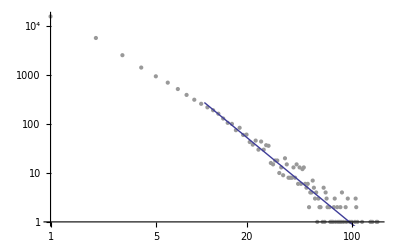

```mathematica
Show[p1=ListLogLogPlot[Select[pausehistogram,0<=#1⟦1⟧<cutoff&],PlotRange->All,PlotStyle->{GrayLevel[0.6]}],p1curve=LogLogPlot[Apply[Plus,Map[Last,useh]]*(ahat-1)x^-ahat/((10.5)^(1-ahat)-150^(1-ahat)),{x,10.5,150}]]
```

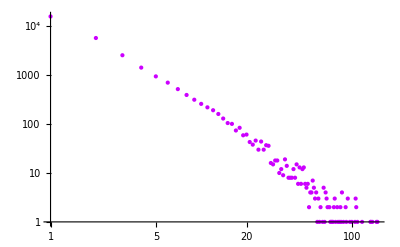

```mathematica
p1a=ListLogLogPlot[Select[pausehistograma,0<#1⟦1⟧<cutoff&],PlotRange->All,PlotStyle->{Hue[0.8]},DisplayFunction->Identity]
```

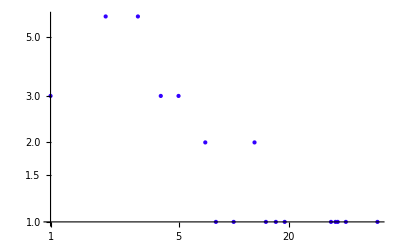

```mathematica
p1b=ListLogLogPlot[Select[pausehistogramb,0<#1⟦1⟧<cutoff&],PlotRange->All,PlotStyle->{Hue[0.7]},DisplayFunction->Identity]
```

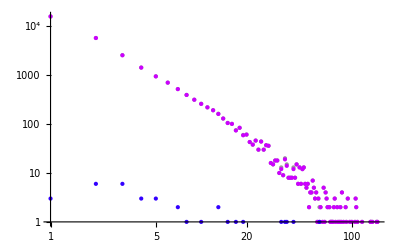

```mathematica
Show[p1,p1a,p1b]
```

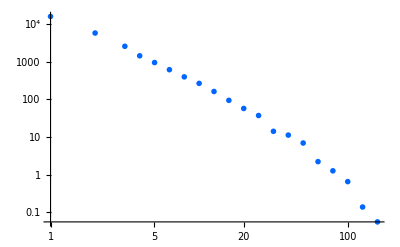

```mathematica
p2=ListLogLogPlot[logpausehistogram,PlotStyle->{Hue[0.6],PointSize[0.01]},Joined->False,PlotRange->All]
```

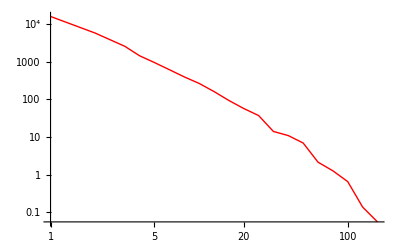

```mathematica
p2a=ListLogLogPlot[logpausehistograma,PlotStyle->{Hue[0.],PointSize[0.014]},Joined->True,PlotRange->All,DisplayFunction->Identity]
```

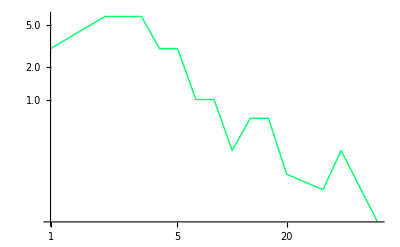

```mathematica
p2b=ListLogLogPlot[logpausehistogramb,PlotStyle->{Hue[0.4],PointSize[0.014]},Joined->True,PlotRange->All,DisplayFunction->Identity]
```

```mathematica
pauselabel={"T = length of pause (s)","d(pauses)"/"dT"};
```

This suggests a cutoff of 120 to 180 seconds would be good.  Or simply remove pauses associated with loss of focus?

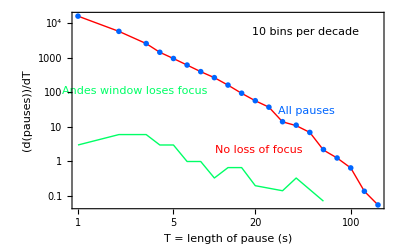

```mathematica
gg2=Show[p2a,p2b,p2,FrameLabel->pauselabel,Frame->True,BaseStyle->{FontSize->12},RotateLabel->False,Epilog->{Text["10 bins per decade",Scaled[{0.75,0.9}]],{Hue[0.6],Text["All pauses",Scaled[{0.75,0.5}]]},{Hue[0],Text["No loss of focus",Scaled[{0.6,0.3}]]},{Hue[0.4],Text["Andes window loses focus",Scaled[{0.2,0.6}]]}},DisplayFunction->$DisplayFunction]
```

```mathematica
Export["~/log/pausehistogram2.eps",gg2,"EPSTIFF",ImageSize->72*8]
```

~/log/pausehistogram2.eps

```mathematica
Export["~/log/pausehistogram2.tiff",gg2,ImageSize->72*8]
```

~/log/pausehistogram2.tiff

```mathematica
ff[x_]=Fit[Log[Select[pausehistogram,(1<#[[1]]<shoulder)&]],{1,x},x]
```

10.1985-2.05169 x

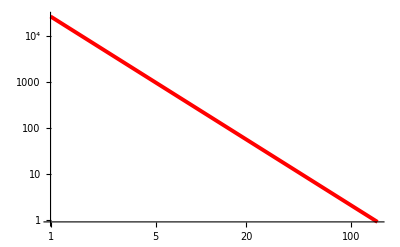

```mathematica
ffplot=LogLogPlot[Exp[ff[Log[x]]],{x,1,cutoff},PlotStyle->{Hue[0],Thickness[0.007]},PlotRange->All,DisplayFunction->Identity]
```

Note the spikes at 5 and 10 minutes.
The power indicates an almost log dependence on cutoff for total time measurements.

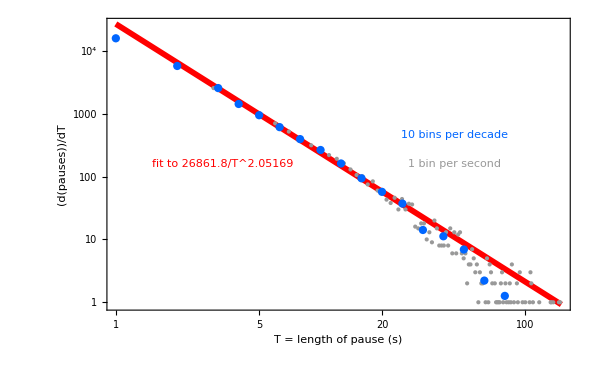

```mathematica
gg=Show[ffplot,p1,p2,FrameLabel->pauselabel,Frame->True,BaseStyle->{FontSize->12},RotateLabel->False,Epilog->{{Hue[0],Text[Row[{"fit to ",Simplify[ⅇ^ff[Log[T]]]}],Scaled[{0.25,0.5}]]},{Hue[0.6],Text["10 bins per decade",Scaled[{0.75,0.6}]]},{GrayLevel[0.6],Text["1 bin per second",Scaled[{0.75,0.5}]]}},DisplayFunction->$DisplayFunction]
```

```mathematica
Export["~/log/pausehistogram.eps",gg,"EPSTIFF",ImageSize->8*72]
```

~/log/pausehistogram.eps

```mathematica
Export["~/log/pausehistogram.tiff",gg,ImageSize->8*72]
```

~/log/pausehistogram.tiff

#### Analysis of pauses not associated with loss of focus

```mathematica
ffa[x_]=Fit[Log[Select[pausehistograma,(0<#[[1]]<shoulder)&]],{1,x},x]
```

10.0205-1.98763 x

```mathematica
ffaa[x_]=Fit[Log[Select[logpausehistograma,(shoulder<#[[1]]<cutoff)&]],{1,x},x]
```

14.4153-3.28681 x

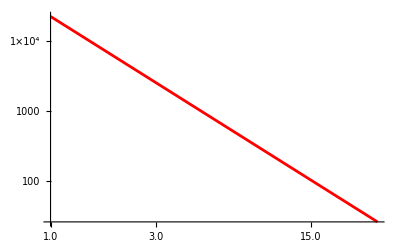

```mathematica
ffplota=LogLogPlot[Exp[ffa[Log[x]]],{x,1,shoulder},PlotStyle->{Hue[0],Thickness[0.005]},DisplayFunction->Identity]
```

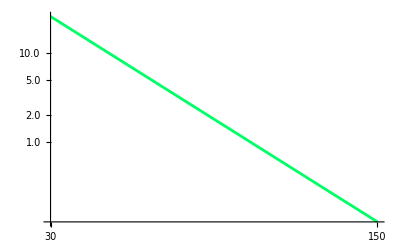

```mathematica
ffplotaa=LogLogPlot[Exp[ffaa[Log[x]]],{x,shoulder,cutoff},PlotStyle->{Hue[0.4],Thickness[0.005]},DisplayFunction->Identity]
```

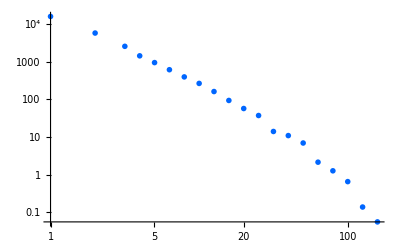

```mathematica
rep2a=ListLogLogPlot[logpausehistograma,PlotStyle->{Hue[0.6],PointSize[0.01]},Joined->False,PlotRange->All,DisplayFunction->Identity]
```

Note the spikes at 5 and 10 minutes.
The power indicates an almost log dependence on cutoff for total time measurements.

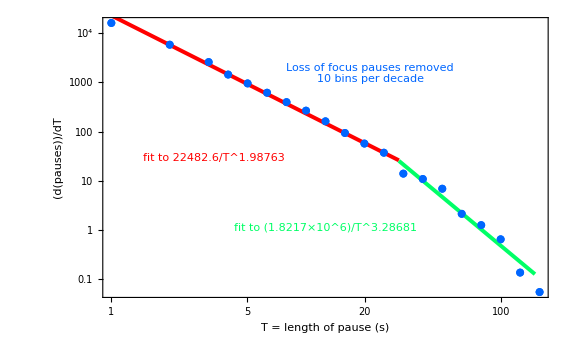

```mathematica
gg3=Show[rep2a,ffplota,ffplotaa,rep2a,FrameLabel->pauselabel,BaseStyle->{FontSize->12},Axes->False,Frame->True,RotateLabel->False,Epilog->{{Hue[0],Text[Row[{"fit to ",Simplify[ⅇ^ffa[Log[T]]]}],Scaled[{0.25,0.5}]]},{Hue[0.4],Text[Row[{"fit to ",Simplify[ⅇ^ffaa[Log[T]]]}],Scaled[{0.5,0.25}]]},{Hue[0.6],Text["Loss of focus pauses removed\n10 bins per decade",Scaled[{0.6,0.8}]]}},DisplayFunction->$DisplayFunction]
```

```mathematica
Export["~/log/pausehistogram3.eps",gg3,"EPSTIFF",ImageSize->72*8]
```

~/log/pausehistogram3.eps

```mathematica
Export["~/log/pausehistogram3.tiff",gg3,ImageSize->72*8]
```

~/log/pausehistogram3.tiff

### Cuts on students and problems based on number completed

Data from both semesters, but histograms must be accumulated semester-wise.

```mathematica
problemattemptsfall={{6,1},{10,1},{20,1},{22,2},{65,1},{84,1},{88,2},{90,1},{95,1},{98,1},{100,1},{104,1},{110,1},{112,1},{115,2},{116,2},{117,1},{119,1},{123,1},{124,1},{125,1},{126,1},{128,1},{133,1},{134,1},{135,1},{136,3},{137,2},{138,1},{139,1},{140,2},{141,1},{142,2},{143,1},{144,5},{145,6},{146,4},{147,1},{148,2},{149,3},{150,3},{151,1},{153,1},{154,2},{156,1},{157,1},{160,1},{167,2},{195,1}};
```

```mathematica
studentattemptsfall={{1,25},{2,30},{3,15},{4,9},{5,12},{6,3},{7,3},{8,1},{10,1},{17,1},{24,1},{30,1},{32,1},{33,1},{34,1},{39,3},{43,1},{46,1},{47,4},{49,3},{50,1},{51,3},{52,3},{53,4},{54,2},{55,3},{56,9},{57,4},{58,1},{59,2},{60,5},{61,1},{62,8},{63,3},{64,7},{65,10},{66,6},{67,4},{68,10},{69,13},{70,13},{71,13},{72,2},{73,4},{74,1},{75,3},{76,1}};
```

```mathematica
problemattemptsspring={{0,1},{15,1},{21,1},{30,1},{33,1},{40,1},{44,1},{51,2},{59,1},{69,1},{76,1},{84,2},{87,1},{89,1},{90,1},{92,1},{94,1},{95,4},{96,3},{97,2},{99,2},{104,1},{109,1},{110,1},{113,2},{115,1},{121,1},{123,1},{124,1},{127,2},{128,1},{131,1},{132,2},{133,1},{134,2},{135,1},{136,7},{137,2},{138,5},{139,2},{140,1},{142,2},{143,1},{144,3},{152,1},{153,1},{177,1}};
```

```mathematica
studentattemptsspring={{1,29},{2,23},{3,6},{4,11},{5,3},{6,2},{8,3},{9,3},{10,1},{11,2},{12,1},{13,2},{30,1},{31,1},{33,1},{34,2},{35,2},{36,1},{37,2},{38,2},{39,5},{40,2},{41,3},{42,2},{43,3},{44,5},{45,4},{46,3},{47,3},{48,1},{49,1},{53,1},{54,4},{55,1},{56,1},{57,1},{58,1},{59,2},{60,5},{61,4},{62,4},{63,5},{64,12},{65,15},{66,12},{67,9},{68,8},{69,6},{70,2},{71,1},{72,1}};
```

Re-bin and merge histograms

```mathematica
ListPlot[Block[{dx=5,max=Max[Map[#[[1]]&,Join[problemattemptsfall,problemattemptsspring]]]},
Table[{x,Apply[Plus,Map[(#[[2]])&,Select[Join[problemattemptsfall,problemattemptsspring],(x-dx/2<#[[1]]<=x+dx/2)&]]]},{x,dx/2,max,dx}]],PlotRange->All,Frame->True,Axes->False]
```

⁃Graphics⁃

Re-bin histogram

```mathematica
ListPlot[Block[{dx=2,max=Max[Map[#[[1]]&,Join[studentattemptsfall,studentattemptsspring]]]},Table[{x,Apply[Plus,Map[(#[[2]])&,Select[Join[studentattemptsfall,studentattemptsspring],(x-dx/2<#[[1]]<=x+dx/2)&]]]},{x,dx/2,max,dx}]],PlotRange->All,Frame->True,Axes->False]
```

⁃Graphics⁃

### Time to complete a problem

This is with a cutoff on the problems where a minimum of 25 students must solve a problem for it to be included.

```mathematica
tfall=ReadList["~/log/times-Fall2005.csv",Word,WordSeparators->",",NullWords->True,RecordLists->True];
```

```mathematica
tspring=ReadList["~/log/times-Spring2006.csv",Word,WordSeparators->",",NullWords->True,RecordLists->True];
```

```mathematica
Dimensions[tfall]
```

{78,154}

```mathematica
Dimensions[tspring]
```

{75,140}

```mathematica
Average[Number[Drop[tfall[[30]],1]]]
```

Average[Number[{,1339,1066,,1017,294,,,621,326,,,1273,1140,604,125,469,,442,740,,371,,,761,479,,1054,,392,,719,585,,223,271,,305,,732,,,67,,450,,949,554,,1005,773,,1140,,,,405,323,270,291,,,483,,644,485,,575,620,341,171,132,,,,,869,,,10,,,72,,306,92,,62,,40,214,177,,311,134,,353,,284,541,651,430,795,374,722,,,,,,,,,1149,,,,846,926,478,1642,2884,,842,912,770,,792,688,1547,158,5,,4,,19,743,508,247,86,1302,491,125,237,99,,58,517,,,420,905,,490,,,,,796,843,,329,932,,5,,,479,,,811,498,,,,1200,590,395,508,,445,,,,,,,800,420,,572,,,626,493,,,998,,964,,,,,237,,376,182,209,,184,294,484,182,1248,903,,,584,352,,,563,,532,53,,601,316,,183,360,357,136,125,749,307,370,481,172,35,27,381,60,141,,1074,,,,,,}]]

```mathematica
Transpose[tfall][[33]]
```

{dt9a,1070,2299,,1287,639,543,,1336,1125,229,379,389,723,434,830,1182,599,564,767,982,823,188,720,941,1046,419,2075,990,719,702,1506,928,1142,725,704,969,,390,470,948,527,5756,262,1954,790,1107,1768,,,,746,733,893,413,697,869,395,2235,541,790,2631,,2529,636,197,2206,,,485,1402,475,624,,600,1125,,}

### Fall Learning curves

```mathematica
<<"~/log/Fall2005-times.out"
```

```mathematica
Sort[Map[{neverFNA[#],#}&,operators]]
```

{{0,CIRCUMFERENCE-OF-CIRCLE-R},{0,COMPO-GENERAL-CASE},{0,COMPO-GENERAL-CASE-UNKNOWN},{0,COMPO-PARALLEL-AXIS},{0,COMPO-PERPENDICULAR},{0,DEFINE-CIRCUMFERENCE-OF-CIRCLE},{0,DEFINE-DURATION},{0,DEFINE-MASS},{0,DEFINE-ROTATIONAL-ENERGY},{0,DEFINE-WAVE-SPEED},{0,DRAW-ACCELERATING},{0,DRAW-ANG-ACCEL-UNKNOWN-DIR},{0,DRAW-BODY},{0,DRAW-COMPO-FORM-AXES},{0,DRAW-DISPLACEMENT-GIVEN-DIR},{0,DRAW-DISPLACEMENT-STRAIGHT},{0,DRAW-DISPLACEMENT-ZERO},{0,DRAW-ENERGY-AXES},{0,DRAW-NORMAL},{0,DRAW-ROTATE-AXES},{0,DRAW-TENSION},{0,DRAW-UNROTATED-AXES},{0,DRAW-UNROTATED-AXES-FOR-ZCOMPS},{0,DRAW-VELOCITY-MOMENTARILY-AT-REST},{0,DRAW-WEIGHT},{0,KINETIC-FRICTION-LAW},{0,OPPOSITE-RELATIVE-POSITION},{0,STATIC-FRICTION-LAW},{0,WRITE-DISPLACEMENT-DISTANCE},{0,WRITE-EQUALITY},{0,WRITE-G-ON-EARTH},{0,WRITE-GRAV-ENERGY},{0,WRITE-HARMONIC-OF},{0,WRITE-IMPLICIT-EQN},{0,WRITE-I-RECT-CM},{0,WRITE-KNOWN-VALUE-EQN},{0,WRITE-ROTATIONAL-ENERGY},{0,WRITE-TOTAL-ENERGY-TOP},{0,WRITE-VOLUME-COMPOUND},{0,WT-LAW},{1,AVG-ACCEL-UNKNOWN},{1,COMPO-ZERO-VECTOR},{1,DEFINE-CHANGING-MASS},{1,DEFINE-CHANGING-MOMENT-OF-INERTIA},{1,DEFINE-FREQUENCY},{1,DEFINE-REVOLUTION-RADIUS},{1,DEFINE-VOLUME},{1,DEFINE-WIDTH},{1,DEFINE-WORK},{1,DRAW-ACCEL-FREE-FALL},{1,DRAW-APPLIED-FORCE},{1,DRAW-AVG-VEL-UNKNOWN},{1,DRAW-BUOYANT-FORCE},{1,DRAW-DISPLACEMENT-UNKNOWN},{1,DRAW-MOMENTUM-STRAIGHT},{1,DRAW-VELOCITY-CURVED},{1,DRAW-VELOCITY-STRAIGHT},{1,SELECT-MC-ANSWER},{1,WRITE-AVG-ACCEL-COMPO},{1,WRITE-I-ROD-END},{1,WRITE-KINETIC-ENERGY},{1,WRITE-MOMENTUM-COMPO},{1,WRITE-ROLLING-VEL},{1,WRITE-SUM-DISP-COMPO},{1,WRITE-WORK},{2,AREA-OF-CIRCLE},{2,COMPO-Z-AXIS},{2,DEFINE-AREA-AT},{2,DEFINE-COEF-FRICTION},{2,DEFINE-DB-INTENSITY},{2,DEFINE-INTENSITY},{2,DEFINE-KINETIC-ENERGY},{2,DEFINE-MASS-DENSITY},{2,DEFINE-MOMENT-OF-INERTIA},{2,DEFINE-NET-WORK},{2,DEFINE-PRESSURE},{2,DEFINE-WAVELENGTH},{2,DRAW-ANG-MOMENTUM-ROTATING},{2,DRAW-ANG-VELOCITY-ROTATING},{2,DRAW-IMPULSE-GIVEN-DIR},{2,DRAW-KINETIC-FRICTION},{2,DRAW-OPPOSITE-RELATIVE-POSITION},{2,DRAW-RELATIVE-VEL-GIVEN-DIR},{2,DRAW-THRUST-FORCE-GIVEN-RELATIVE-VEL},{2,DRAW-VECTOR-GIVEN-COMPOS},{2,DRAW-VELOCITY-AT-REST},{2,PENDULUM-OSCILLATION},{2,WRITE-CENTRIPETAL-ACCEL},{2,WRITE-FREE-FALL-ACCEL},{2,WRITE-INTENSITY-TO-DECIBELS},{2,WRITE-SPEED-OF-WAVE},{2,WRITE-SPRING-ENERGY},{3,APPLY-NET-WORK},{3,DEFINE-ANGULAR-FREQUENCY},{3,DEFINE-MASS-CHANGE-MAGNITUDE},{3,DEFINE-PERIOD-VAR},{3,DEFINE-TOTAL-ENERGY},{3,DRAW-CENTRIPETAL-ACCELERATION},{3,DRAW-MOMENTUM-AT-REST},{3,PERIOD-OF-WAVE},{3,WRITE-ENERGY-CONS},{3,WRITE-IMPULSE-MOMENTUM-COMPO},{3,WRITE-MASS-COMPOUND},{3,WRITE-NFL-COMPO},{3,WRITE-NSL-COMPO},{4,DEFINE-AMPLITUDE-MAX-ABS-ACCELERATION},{4,DEFINE-GRAV-ENERGY},{4,DEFINE-HEIGHT},{4,DEFINE-NET-POWER-OUT},{4,DEFINE-RADIUS-OF-CIRCLE},{4,DRAW-ACCEL-GIVEN-DIR},{4,DRAW-ANG-ACCELERATING},{4,DRAW-ANG-DISPLACEMENT-ROTATING},{4,DRAW-AVG-VEL-FROM-DISPLACEMENT},{4,WRITE-ANG-SDD},{4,WRITE-SDD},{4,WRITE-TORQUE-ZC},{5,DEFINE-AREA},{5,DEFINE-SHAPE-LENGTH},{5,DEFINE-STRING-TENSION},{5,DRAW-DRAG},{5,DRAW-RELATIVE-POSITION},{5,DRAW-TORQUE},{5,WAVENUMBER-LAMBDA-WAVE},{5,WRITE-ANG-MOMENTUM},{5,WRITE-INTENSITY-TO-POWER},{5,WRITE-LK-NO-S-COMPO},{5,WRITE-NET-TORQUE},{5,WRITE-RELATIVE-VEL-COMPO},{5,WRITE-UG-CIRCULAR},{5,WRITE-ZERO-WORK},{6,BERNOULLI},{6,DEFINE-OBSERVED-FREQUENCY},{6,DRAW-ACCEL-CURVED-UNKNOWN},{6,DRAW-PRESSURE},{6,PRESSURE-AT-OPEN-TO-ATMOSPHERE},{6,WAVE-SPEED-STRING},{6,WRITE-CONS-LINMOM-COMPO-JOIN},{6,WRITE-CONS-LINMOM-COMPO-SPLIT},{6,WRITE-DENSITY},{6,WRITE-LINEAR-VEL},{6,WRITE-THRUST-FORCE},{7,ACCEL-AT-REST},{7,DEFINE-NET-DB-INTENSITY},{7,MASS-PER-LENGTH-EQUATION},{7,WRITE-LK-NO-VF-COMPO},{7,WRITE-MAG-TORQUE},{7,WRITE-SUM-DISTANCES},{7,WT-LAW-CM},{8,DEFINE-DISTANCE},{8,DEFINE-NET-INTENSITY},{8,DEFINE-SPRING-ENERGY},{8,DRAW-SOUGHT-VECTOR-UNKNOWN},{8,NTL},{8,PRESSURE-FORCE},{8,WRITE-CONS-LINMOM-COMPO},{9,CONTINUITY},{9,DRAW-GRAV-FORCE},{9,DRAW-SPRING-FORCE},{9,DRAW-ZERO-RELATIVE-VEL},{9,GIVEN-FRACTION},{9,WRITE-ARCHIMEDES},{9,WRITE-CONS-ANGMOM-JOIN},{9,WRITE-CONS-KE-ELASTIC},{9,WRITE-NET-INTENSITY},{9,WRITE-VALUE-OF-ATMOSPHERE},{9,WRITE-WORK-DELTA-KE},{10,DRAW-ANG-DECELERATING},{10,DRAW-FORCE-COMPOUND},{10,SDD-CONSTVEL-COMPO},{10,WRITE-RK-NO-VF},{10,WRITE-TENSIONS-EQUAL},{10,WRITE-THRUST-FORCE-COMPO},{11,FREQUENCY-OF-WAVE},{11,WRITE-CONNECTED-VELOCITIES},{11,WRITE-NULL-SPRING-ENERGY},{11,WRITE-RK-NO-S},{12,DEFINE-AMPLITUDE},{12,DEFINE-POWER-VAR},{12,DRAW-MOMENTUM-STRAIGHT-UNKNOWN},{12,DRAW-NET-TORQUE-FROM-ANG-ACCEL},{12,DRAW-REL-VEL-VECTOR-UNKNOWN},{12,DRAW-VELOCITY-STRAIGHT-UNKNOWN},{12,MASS-PER-LENGTH},{12,SPEED-EQUALS-WAVE-SPEED},{12,SPRING-MASS-OSCILLATION},{12,WRITE-CONS-ANGMOM},{12,WRITE-FORCE-COMPOUND},{12,WRITE-RK-NO-T},{13,WRITE-NET-POWER},{14,DEFINE-SPEED},{14,DEFINE-SPRING-CONSTANT},{14,DRAW-DECELERATING},{14,DRAW-RELATIVE-POSITION-UNKNOWN},{14,MAX-TRANSVERSE-ABS-ACCELERATION-WAVE},{14,USE-CONST-VX},{14,WRITE-HEIGHT-DY-COMPO},{14,WRITE-SUM-TIMES},{15,DEFINE-WAVENUMBER},{15,DRAW-ACCEL-UNKNOWN-NET-FORCE},{15,WRITE-CENTER-OF-MASS-COMPO},{16,DRAW-NET-TORQUE-UNKNOWN-DIR},{16,MAKE-DOPPLER-FREQUENCY},{16,WRITE-CHANGE-ME-TOP},{16,WRITE-TIMELESS-BEAT-FREQUENCY},{16,WRITE-UG},{16,WRITE-WNC},{17,DRAW-THRUST-FORCE},{17,DRAW-VELOCITY-CURVED-UNKNOWN},{17,WRITE-I-COMPOUND},{17,WRITE-POWER},{17,WRITE-WAVE-SPEED-LIGHT},{18,DEFINE-WNC},{18,DRAW-STATIC-FRICTION},{18,WRITE-PERIOD-CIRCULAR},{19,DEFINE-AMPLITUDE-MAX-SPEED},{19,DEFINE-ANGLE-BETWEEN-KNOWN},{19,MAX-TRANSVERSE-SPEED-WAVE},{19,WRITE-IMPULSE-COMPO},{19,WRITE-NL-ROTATION},{20,WRITE-BEAT-FREQUENCY},{20,WRITE-LK-NO-T-COMPO},{20,WRITE-NTL-VECTOR},{21,DRAW-DISPLACEMENT-PROJECTILE},{21,WRITE-I-HOOP-CM},{23,WRITE-AVG-VEL-COMPO},{23,WRITE-CONNECTED-ACCELS},{23,WRITE-I-ROD-CM},{23,WRITE-NSL-NET-COMPO},{25,DRAW-NET-TORQUE-NON-ROTATING},{25,DRAW-WEIGHT-AT-CM},{26,DEFINE-COMPRESSION},{26,DRAW-ANG-VELOCITY-AT-REST},{27,DRAW-IMPULSE-GIVEN-FORCE},{27,SPRING-LAW-COMPRESSION},{28,ACCEL-CONSTANT-SPEED},{28,DRAW-ZERO-RELATIVE-POSITION},{30,DRAW-REACTION-FORCE},{30,WRITE-INST-POWER},{33,DEFINE-NET-POWER-VAR},{34,PRESSURE-HEIGHT-FLUID},{36,WRITE-PYTH-THM},{40,DRAW-IMPULSE-GIVEN-MOMENTA-UNKNOWN-DIR},{48,DRAW-NET-FORCE-FROM-ACCEL}}

```mathematica
Sort[Map[{N[Mean[flattenhistogram[attemptsbeforeFNA[#]]]],#}&,operators]]
```

{{0.,CIRCUMFERENCE-OF-CIRCLE-R},{0.,DEFINE-AMPLITUDE-MAX-ABS-ACCELERATION},{0.,DEFINE-AMPLITUDE-MAX-SPEED},{0.,DEFINE-COEF-FRICTION},{0.,DEFINE-NET-DB-INTENSITY},{0.,DEFINE-NET-INTENSITY},{0.,DEFINE-ROTATIONAL-ENERGY},{0.,DRAW-ANG-ACCEL-UNKNOWN-DIR},{0.,DRAW-AVG-VEL-FROM-DISPLACEMENT},{0.,DRAW-DISPLACEMENT-ZERO},{0.,DRAW-IMPULSE-GIVEN-FORCE},{0.,KINETIC-FRICTION-LAW},{0.,STATIC-FRICTION-LAW},{0.,WRITE-CONS-LINMOM-COMPO-JOIN},{0.,WRITE-DISPLACEMENT-DISTANCE},{0.,WRITE-IMPULSE-COMPO},{0.,WRITE-I-RECT-CM},{0.,WRITE-NET-INTENSITY},{0.,WRITE-SUM-DISTANCES},{0.,WRITE-VOLUME-COMPOUND},{0.0133333,DRAW-UNROTATED-AXES},{0.0138889,DRAW-ENERGY-AXES},{0.0357143,WRITE-I-ROD-CM},{0.0357143,WRITE-NET-POWER},{0.037037,WT-LAW-CM},{0.0384615,DRAW-ACCEL-UNKNOWN-NET-FORCE},{0.0384615,WRITE-TIMELESS-BEAT-FREQUENCY},{0.04,WRITE-I-COMPOUND},{0.047619,MAX-TRANSVERSE-ABS-ACCELERATION-WAVE},{0.047619,WRITE-NSL-NET-COMPO},{0.05,PRESSURE-HEIGHT-FLUID},{0.0526316,DRAW-ANG-ACCELERATING},{0.0588235,WRITE-I-HOOP-CM},{0.0649351,DRAW-ROTATE-AXES},{0.0666667,WRITE-CONNECTED-VELOCITIES},{0.0731707,SPEED-EQUALS-WAVE-SPEED},{0.08,DRAW-ANG-VELOCITY-AT-REST},{0.0833333,MAX-TRANSVERSE-SPEED-WAVE},{0.0851064,DRAW-THRUST-FORCE},{0.0857143,DRAW-UNROTATED-AXES-FOR-ZCOMPS},{0.0909091,DRAW-NET-TORQUE-FROM-ANG-ACCEL},{0.0933333,DRAW-VELOCITY-CURVED},{0.1,DEFINE-CHANGING-MASS},{0.1,WRITE-CONS-ANGMOM-JOIN},{0.102564,DEFINE-NET-POWER-VAR},{0.102564,USE-CONST-VX},{0.103896,DRAW-BODY},{0.108108,SPRING-LAW-COMPRESSION},{0.111111,OPPOSITE-RELATIVE-POSITION},{0.111111,WRITE-BEAT-FREQUENCY},{0.111111,WRITE-CONS-ANGMOM},{0.111111,WRITE-RK-NO-T},{0.117647,DRAW-ZERO-RELATIVE-POSITION},{0.121212,APPLY-NET-WORK},{0.125,NTL},{0.125,WRITE-RK-NO-VF},{0.136364,DRAW-ACCEL-CURVED-UNKNOWN},{0.142857,DRAW-IMPULSE-GIVEN-DIR},{0.142857,FREQUENCY-OF-WAVE},{0.142857,WAVENUMBER-LAMBDA-WAVE},{0.142857,WRITE-INST-POWER},{0.157895,WRITE-NL-ROTATION},{0.16129,WRITE-MASS-COMPOUND},{0.166667,WRITE-SUM-TIMES},{0.168831,DRAW-COMPO-FORM-AXES},{0.178082,SELECT-MC-ANSWER},{0.18,DRAW-MOMENTUM-STRAIGHT-UNKNOWN},{0.185185,WRITE-AVG-VEL-COMPO},{0.19697,DRAW-DRAG},{0.2,DEFINE-WAVENUMBER},{0.2,WRITE-CENTER-OF-MASS-COMPO},{0.208333,DEFINE-NET-WORK},{0.212121,WRITE-CONS-KE-ELASTIC},{0.213115,DRAW-ANG-MOMENTUM-ROTATING},{0.222222,WAVE-SPEED-STRING},{0.222222,WRITE-TENSIONS-EQUAL},{0.225352,DRAW-ACCEL-GIVEN-DIR},{0.227273,MASS-PER-LENGTH-EQUATION},{0.22973,WRITE-EQUALITY},{0.230769,DEFINE-STRING-TENSION},{0.230769,DRAW-WEIGHT-AT-CM},{0.230769,WRITE-PERIOD-CIRCULAR},{0.232143,WRITE-HEIGHT-DY-COMPO},{0.234043,WRITE-POWER},{0.245902,DEFINE-RADIUS-OF-CIRCLE},{0.254902,DRAW-BUOYANT-FORCE},{0.254902,PENDULUM-OSCILLATION},{0.263158,DRAW-DISPLACEMENT-GIVEN-DIR},{0.272727,DRAW-IMPULSE-GIVEN-MOMENTA-UNKNOWN-DIR},{0.272727,WRITE-CHANGE-ME-TOP},{0.283019,DEFINE-VOLUME},{0.283333,DEFINE-POWER-VAR},{0.285714,WRITE-THRUST-FORCE},{0.289855,DRAW-VELOCITY-AT-REST},{0.290323,WRITE-CONNECTED-ACCELS},{0.292308,WRITE-SDD},{0.294118,WRITE-WAVE-SPEED-LIGHT},{0.295082,WRITE-ZERO-WORK},{0.296296,DEFINE-CHANGING-MOMENT-OF-INERTIA},{0.298246,PERIOD-OF-WAVE},{0.3,DEFINE-WNC},{0.3,WRITE-LINEAR-VEL},{0.302326,WRITE-ANG-SDD},{0.32,DRAW-GRAV-FORCE},{0.321429,WRITE-UG-CIRCULAR},{0.333333,DRAW-NET-TORQUE-NON-ROTATING},{0.341463,WRITE-CONS-LINMOM-COMPO-SPLIT},{0.345455,DRAW-VELOCITY-STRAIGHT-UNKNOWN},{0.346939,WRITE-ANG-MOMENTUM},{0.352941,DRAW-NET-FORCE-FROM-ACCEL},{0.357143,MASS-PER-LENGTH},{0.36,DRAW-MOMENTUM-AT-REST},{0.369863,WRITE-WORK},{0.375,DEFINE-NET-POWER-OUT},{0.375,DRAW-KINETIC-FRICTION},{0.375,WRITE-UG},{0.376812,DEFINE-REVOLUTION-RADIUS},{0.380952,DEFINE-MOMENT-OF-INERTIA},{0.387097,WRITE-PYTH-THM},{0.389831,DRAW-ANG-DISPLACEMENT-ROTATING},{0.403846,DRAW-ANG-DECELERATING},{0.405405,DRAW-DISPLACEMENT-UNKNOWN},{0.408163,DEFINE-OBSERVED-FREQUENCY},{0.413793,ACCEL-CONSTANT-SPEED},{0.415094,DEFINE-AREA-AT},{0.416667,WRITE-NET-TORQUE},{0.422222,WRITE-DENSITY},{0.423077,DEFINE-MASS-CHANGE-MAGNITUDE},{0.426667,COMPO-PERPENDICULAR},{0.4375,WRITE-FORCE-COMPOUND},{0.439394,WRITE-CENTRIPETAL-ACCEL},{0.441558,WRITE-KNOWN-VALUE-EQN},{0.444444,WRITE-NTL-VECTOR},{0.446809,GIVEN-FRACTION},{0.468085,SPRING-MASS-OSCILLATION},{0.469388,DEFINE-AMPLITUDE},{0.472222,WRITE-GRAV-ENERGY},{0.472727,SDD-CONSTVEL-COMPO},{0.484848,DRAW-MOMENTUM-STRAIGHT},{0.485714,WRITE-RK-NO-S},{0.5,DRAW-TENSION},{0.5,WRITE-ROTATIONAL-ENERGY},{0.506667,WRITE-SUM-DISP-COMPO},{0.508197,DEFINE-PERIOD-VAR},{0.510204,DEFINE-SPRING-ENERGY},{0.511111,CONTINUITY},{0.52,DRAW-DISPLACEMENT-STRAIGHT},{0.52,WRITE-WNC},{0.526316,WRITE-IMPULSE-MOMENTUM-COMPO},{0.535714,WRITE-INTENSITY-TO-POWER},{0.535714,WRITE-SPEED-OF-WAVE},{0.555556,COMPO-Z-AXIS},{0.561404,DEFINE-ANGULAR-FREQUENCY},{0.561404,DEFINE-WAVELENGTH},{0.5625,BERNOULLI},{0.5625,WRITE-WORK-DELTA-KE},{0.571429,DRAW-FORCE-COMPOUND},{0.571429,DRAW-SPRING-FORCE},{0.586957,WRITE-TORQUE-ZC},{0.588235,DRAW-THRUST-FORCE-GIVEN-RELATIVE-VEL},{0.592593,WRITE-NULL-SPRING-ENERGY},{0.6,WRITE-IMPLICIT-EQN},{0.612245,AREA-OF-CIRCLE},{0.616667,DEFINE-MASS-DENSITY},{0.622642,PRESSURE-AT-OPEN-TO-ATMOSPHERE},{0.626667,COMPO-PARALLEL-AXIS},{0.633803,DEFINE-KINETIC-ENERGY},{0.644068,DEFINE-SHAPE-LENGTH},{0.657895,DEFINE-MASS},{0.657895,DRAW-APPLIED-FORCE},{0.659091,DRAW-REL-VEL-VECTOR-UNKNOWN},{0.66,WRITE-VALUE-OF-ATMOSPHERE},{0.666667,PRESSURE-FORCE},{0.666667,WRITE-AVG-ACCEL-COMPO},{0.673077,DRAW-VELOCITY-CURVED-UNKNOWN},{0.675676,COMPO-GENERAL-CASE-UNKNOWN},{0.676923,DRAW-CENTRIPETAL-ACCELERATION},{0.681818,WRITE-LK-NO-T-COMPO},{0.685714,DRAW-ACCEL-FREE-FALL},{0.690476,DRAW-NET-TORQUE-UNKNOWN-DIR},{0.7,WRITE-THRUST-FORCE-COMPO},{0.705882,DEFINE-DB-INTENSITY},{0.708333,DRAW-ZERO-RELATIVE-VEL},{0.72,DRAW-NORMAL},{0.723404,DEFINE-AREA},{0.728814,DRAW-SOUGHT-VECTOR-UNKNOWN},{0.730159,DEFINE-FREQUENCY},{0.733333,WRITE-RELATIVE-VEL-COMPO},{0.745763,DRAW-DECELERATING},{0.756757,WRITE-KINETIC-ENERGY},{0.775,WRITE-ARCHIMEDES},{0.779412,DRAW-ANG-VELOCITY-ROTATING},{0.789474,DRAW-VELOCITY-STRAIGHT},{0.802632,COMPO-GENERAL-CASE},{0.80303,WRITE-ENERGY-CONS},{0.814815,WRITE-CONS-LINMOM-COMPO},{0.818182,MAKE-DOPPLER-FREQUENCY},{0.819444,COMPO-ZERO-VECTOR},{0.850746,WRITE-MOMENTUM-COMPO},{0.861111,WRITE-TOTAL-ENERGY-TOP},{0.862745,DEFINE-GRAV-ENERGY},{0.864865,DEFINE-WORK},{0.865672,DRAW-VECTOR-GIVEN-COMPOS},{0.866667,DRAW-WEIGHT},{0.868852,DEFINE-DISTANCE},{0.878788,WRITE-SPRING-ENERGY},{0.893333,DRAW-ACCELERATING},{0.903846,DEFINE-TOTAL-ENERGY},{0.923077,WRITE-LK-NO-S-COMPO},{0.928571,WRITE-NFL-COMPO},{0.933333,ACCEL-AT-REST},{0.9375,DRAW-DISPLACEMENT-PROJECTILE},{0.965517,WRITE-MAG-TORQUE},{0.973333,WT-LAW},{0.985294,DRAW-RELATIVE-VEL-GIVEN-DIR},{1.,DEFINE-INTENSITY},{1.01449,WRITE-NSL-COMPO},{1.05455,DRAW-RELATIVE-POSITION-UNKNOWN},{1.06383,DEFINE-ANGLE-BETWEEN-KNOWN},{1.07143,DEFINE-SPEED},{1.08197,DEFINE-PRESSURE},{1.10714,DRAW-STATIC-FRICTION},{1.15094,DRAW-TORQUE},{1.2069,DEFINE-SPRING-CONSTANT},{1.24286,WRITE-FREE-FALL-ACCEL},{1.24324,DRAW-VELOCITY-MOMENTARILY-AT-REST},{1.32258,WRITE-INTENSITY-TO-DECIBELS},{1.36667,DEFINE-WAVE-SPEED},{1.38462,DRAW-REACTION-FORCE},{1.41667,WRITE-LK-NO-VF-COMPO},{1.42667,WRITE-G-ON-EARTH},{1.47727,DEFINE-COMPRESSION},{1.48889,WRITE-HARMONIC-OF},{1.52273,DRAW-PRESSURE},{1.55405,DEFINE-DURATION},{2.,DEFINE-CIRCUMFERENCE-OF-CIRCLE},{2.18182,DEFINE-HEIGHT},{2.38462,DRAW-RELATIVE-POSITION},{Mean[{}],AVG-ACCEL-UNKNOWN},{Mean[{}],DEFINE-WIDTH},{Mean[{}],DRAW-AVG-VEL-UNKNOWN},{Mean[{}],DRAW-OPPOSITE-RELATIVE-POSITION},{Mean[{}],WRITE-I-ROD-END},{Mean[{}],WRITE-ROLLING-VEL}}

```mathematica
principle="DRAW-RELATIVE-POSITION";neverFNA[principle]
```

5

```mathematica
lc1=ListPlot[numberstudents[principle],Axes->False,Frame->True,BaseStyle->{FontSize->12},FrameLabel->{"opportunity","students"},PlotStyle->{Hue[0.6],PointSize[0.015]},RotateLabel->False,Epilog->{Hue[0.6],Text["applications of\n"<>principle,Scaled[{0.75,0.8}]]}]
```

⁃Graphics⁃

```mathematica
Export["~/log/numberstudents.eps",lc1,"EPSTIFF",ImageSize->432]
```

~/log/numberstudents.eps

```mathematica
Export["~/log/numberstudents.tiff",lc1,ImageSize->432]
```

~/log/numberstudents.tiff

```mathematica
cutoff=20;
```

```mathematica
pavgerr=ListPlot[Take[avgerrors[principle],cutoff],DisplayFunction->Identity,PlotStyle->{Hue[0.6],PointSize[0.015]}]
```

⁃Graphics⁃

```mathematica
pavghint=ListPlot[Take[avghints[principle],cutoff],PlotRange->All,Frame->True,Axes->False,PlotStyle->{Hue[0],PointSize[0.015]},DisplayFunction->Identity]
```

⁃Graphics⁃

```mathematica
passist=Show[pavghint,pavgerr,Axes->False,Frame->True,BaseStyle->{FontSize->12},DisplayFunction->$DisplayFunction,RotateLabel->False,FrameLabel->{"opportunity","average\nnumber"},Epilog->{PointSize[0.015],{Text["before application of\n"<>principle,Scaled[{0.5,0.74}],{-1,1}]},{Hue[0],Point[Scaled[{0.48,0.88}]],Text["hints received",Scaled[{0.5,0.9}],{-1,1}]},{Hue[0.6],Point[Scaled[{0.48,0.8}]],Text["errors made",Scaled[{0.5,0.82}],{-1,1}]}}]
```

⁃Graphics⁃

```mathematica
Export["~/log/averageassistance.eps",passist,"EPSTIFF",ImageSize->432]
```

~/log/averageassistance.eps

```mathematica
Export["~/log/averageassistance.tiff",passist,ImageSize->432]
```

~/log/averageassistance.tiff

```mathematica
Column[Take[problemlist[principle],cutoff]]
```

{{cm1,1},{cm2,6},{dr8a,1},{dt12a,12},{kr7a,1},{kt5a,49}}
{{cm1,1},{cm2,23},{cm3,7},{dr2a,1},{dr8a,1},{dt12a,20},{kr6a,3},{kr7a,1},{kt5a,8},{rots8a,1}}
{{cm2,25},{cm3,21},{dr2a,2},{dr8a,1},{dt12a,8},{kr6a,4},{kr7a,2},{kt5a,2}}
{{cm2,9},{cm3,36},{dr2a,4},{dr8a,1},{dt12a,1},{kr6a,8},{kr7a,4},{kt12c,1},{kt5a,1}}
{{cm2,6},{cm3,35},{dr2a,8},{dr2b,1},{dr8a,1},{kr6a,11},{kr7a,2},{kt5a,1}}
{{cm2,4},{cm3,26},{dr2a,6},{dr2b,4},{dr5a,1},{kr6a,13},{kr7a,9}}
{{cm3,12},{dr2a,10},{dr2b,8},{dr5a,2},{dr6a,1},{kr6a,20},{kr7a,6},{rots8a,1}}
{{cm2,1},{cm3,6},{dr2a,16},{dr2b,6},{dr5a,6},{kr6a,16},{kr7a,7},{rots8a,1}}
{{cm3,3},{dr2a,12},{dr2b,11},{dr4a,1},{dr5a,7},{kr6a,13},{kr7a,8},{rots8b,1}}
{{cm3,3},{dr2a,12},{dr2b,15},{dr4a,1},{dr5a,8},{dr6a,1},{dr8a,1},{kr6a,8},{kr7a,5}}
{{cm3,1},{dr2a,11},{dr2b,9},{dr4a,1},{dr5a,14},{dr6a,4},{dr6b,1},{dr8a,2},{kr6a,4},{kr7a,7}}
{{cm1,1},{cm2,1},{dr2a,7},{dr2b,11},{dr5a,17},{dr6a,2},{dr8a,6},{kr6a,3},{kr7a,4},{rots8a,1}}
{{dr2a,8},{dr2b,11},{dr5a,19},{dr6a,3},{dr8a,4},{kr6a,3},{kr7a,2}}
{{dr2a,7},{dr2b,7},{dr5a,17},{dr6a,8},{dr8a,6},{kr6a,2},{kr7a,2}}
{{dr2a,4},{dr2b,9},{dr5a,14},{dr6a,4},{dr6b,1},{dr8a,10},{kr6a,3}}
{{dr2a,2},{dr2b,7},{dr5a,13},{dr6a,5},{dr8a,12},{kr6a,2},{kr7a,2}}
{{dr2b,6},{dr3a,1},{dr5a,9},{dr6a,8},{dr8a,15},{kr6a,2}}
{{cm2,1},{dr2b,2},{dr3a,1},{dr5a,8},{dr6a,5},{dr8a,15},{kr7a,2},{rots8a,4}}
{{cm2,1},{dr2b,1},{dr5a,6},{dr6a,4},{dr8a,19},{rots8a,3},{rots8b,3}}
{{dr5a,5},{dr6a,2},{dr7a,1},{dr8a,17},{kr6a,1},{rots8a,4},{rots8b,2}}

```mathematica
Column[Take[errornames[principle],cutoff]]
```

{{DEFAULT-NON-EXISTENT-VECTOR,10},{DEFAULT-SHOULD-BE-NON-ZERO,1},{DEFAULT-SHOULD-BE-UNKNOWN,1},{DEFAULT-VECTOR-BODY,3},{DEFAULT-WRONG-BODY,8},{DEFAULT-WRONG-VECTOR-DIR,34},{DISTANCE-TRAVELLED-SHOULD-BE-DISPLACEMENT,10},{FORGOT-UNITS,1},{MAYBE-FORGOT-UNITS,2},{NON-EXISTENT-VARIABLE,13},{OPPOSITE-RELATIVE-POSITION,23},{SYNTAX-ERROR-IN-EQN,3},{UNDEFINED-VARIABLES,4},{UNDIAGNOSED-EQN-ERROR,11},{UNUSED-VARIABLES,2},{VECTOR-TIME,4},{VECTOR-WRONG-TIME-AND-DIRECTION,16},{WRONG-OBJECT-FOR-BODY-TOOL,2},{WRONG-PT-RELATIVE-POSITION,6},{WRONG-REF-PT-RELATIVE-POSITION,19},{WRONG-UNITS,5},{WRONG-VALUE-NON-GIVEN,2},{assoc-error,1}}
{{DEFAULT-NON-EXISTENT-VECTOR,9},{DEFAULT-SHOULD-BE-NON-ZERO,3},{DEFAULT-SHOULD-BE-UNKNOWN,1},{DEFAULT-WRONG-BODY,7},{DEFAULT-WRONG-VECTOR-DIR,11},{NON-EXISTENT-VARIABLE,7},{OPPOSITE-RELATIVE-POSITION,6},{SYNTAX-ERROR-IN-EQN,1},{UNDEFINED-VARIABLES,7},{UNDIAGNOSED-EQN-ERROR,7},{VECTOR-TIME,1},{VECTOR-WRONG-TIME-AND-DIRECTION,1},{WRONG-REF-PT-RELATIVE-POSITION,40},{WRONG-UNITS,5},{WRONG-VALUE-NON-GIVEN,1}}
{{DEFAULT-NON-EXISTENT-VECTOR,7},{DEFAULT-SHOULD-BE-NON-ZERO,2},{DEFAULT-SHOULD-BE-UNKNOWN,1},{DEFAULT-WRONG-BODY,10},{DEFAULT-WRONG-VECTOR-DIR,6},{NON-EXISTENT-VARIABLE,2},{OPPOSITE-RELATIVE-POSITION,7},{SYNTAX-ERROR-IN-EQN,1},{UNDEFINED-VARIABLES,2},{UNDIAGNOSED-EQN-ERROR,1},{WRONG-PT-RELATIVE-POSITION,1},{WRONG-REF-PT-RELATIVE-POSITION,28},{WRONG-VALUE-NON-GIVEN,1},{assoc-error,1}}
{{DEFAULT-NON-EXISTENT-VECTOR,4},{DEFAULT-SHOULD-BE-NON-ZERO,5},{DEFAULT-SHOULD-BE-UNKNOWN,2},{DEFAULT-VECTOR-BODY,1},{DEFAULT-WRONG-BODY,6},{DEFAULT-WRONG-VECTOR-DIR,11},{IMPRECISE-VALUE-NON-GIVEN,1},{NON-EXISTENT-VARIABLE,5},{NON-EXISTENT-VARIABLE2,1},{OPPOSITE-RELATIVE-POSITION,5},{SYNTAX-ERROR-IN-EQN,1},{UNDEFINED-VARIABLES,1},{UNUSED-VARIABLES,1},{WRONG-PT-RELATIVE-POSITION,2},{WRONG-REF-PT-RELATIVE-POSITION,11},{WRONG-VALUE-NON-GIVEN,1},{assoc-error,3},{assoc-error-nil-show-hint,1}}
{{DEFAULT-NON-EXISTENT-VECTOR,5},{DEFAULT-SHOULD-BE-NON-ZERO,11},{DEFAULT-SHOULD-BE-ZERO,1},{DEFAULT-WRONG-BODY,1},{DEFAULT-WRONG-VECTOR-DIR,12},{NON-EXISTENT-AXES,1},{NON-EXISTENT-VARIABLE2,1},{OPPOSITE-RELATIVE-POSITION,3},{UNDEFINED-VARIABLES,4},{UNDIAGNOSED-EQN-ERROR,4},{UNUSED-VARIABLES,3},{WRONG-PT-RELATIVE-POSITION,3},{WRONG-REF-PT-RELATIVE-POSITION,7}}
{{BODY-TOOL-MULTIPLE-CORRECT,2},{DEFAULT-NON-EXISTENT-VECTOR,6},{DEFAULT-SHOULD-BE-NON-ZERO,6},{DEFAULT-SHOULD-BE-UNKNOWN,2},{DEFAULT-WRONG-BODY,1},{DEFAULT-WRONG-VECTOR-DIR,13},{NON-EXISTENT-AXES,3},{NON-EXISTENT-VARIABLE,4},{OPPOSITE-RELATIVE-POSITION,5},{UNDEFINED-VARIABLES,1},{UNDIAGNOSED-EQN-ERROR,2},{WRONG-PT-RELATIVE-POSITION,4},{WRONG-REF-PT-RELATIVE-POSITION,4},{assoc-error,1}}
{{BODY-TOOL-MULTIPLE-CORRECT,2},{DEFAULT-SHOULD-BE-NON-ZERO,2},{DEFAULT-SHOULD-BE-UNKNOWN,1},{DEFAULT-VECTOR-BODY,2},{DEFAULT-WRONG-VECTOR-DIR,24},{NON-EXISTENT-AXES,5},{NON-EXISTENT-VARIABLE,7},{OPPOSITE-RELATIVE-POSITION,10},{SAME-BODY-AND-AGENT-OF-A-FORCE-NO-NET,2},{SYNTAX-ERROR-IN-EQN,1},{UNDEFINED-VARIABLES,1},{UNDIAGNOSED-EQN-ERROR,3},{WRONG-FORCE-AGENT-AND-TYPE,4},{WRONG-PT-RELATIVE-POSITION,6},{WRONG-REF-PT-RELATIVE-POSITION,9},{WRONG-VALUE-NON-GIVEN,1}}
{{DEFAULT-WRONG-VECTOR-DIR,12},{NON-EXISTENT-AXES,1},{NON-EXISTENT-VARIABLE,3},{NON-EXISTENT-VARIABLE2,1},{OPPOSITE-RELATIVE-POSITION,4},{UNUSED-VARIABLES,4},{WRONG-PT-RELATIVE-POSITION,3},{WRONG-REF-PT-RELATIVE-POSITION,7},{assoc-error-t-show-hint,1}}
{{DEFAULT-SHOULD-BE-NON-ZERO,2},{DEFAULT-WRONG-VECTOR-DIR,8},{NON-EXISTENT-AXES,3},{NON-EXISTENT-VARIABLE,4},{OPPOSITE-RELATIVE-POSITION,3},{SUBSTITUTE-MAG-VARS,2},{UNDEFINED-VARIABLES,2},{UNDIAGNOSED-EQN-ERROR,2},{UNUSED-VARIABLES,1},{WRONG-PT-RELATIVE-POSITION,4},{WRONG-REF-PT-RELATIVE-POSITION,8}}
{{DEFAULT-NON-EXISTENT-VECTOR,3},{DEFAULT-SHOULD-BE-NON-ZERO,2},{DEFAULT-VECTOR-BODY,5},{DEFAULT-WRONG-VECTOR-DIR,12},{FORCE-ON-WHOLE-NOT-PT,1},{NON-EXISTENT-AXES,2},{NON-EXISTENT-VARIABLE,1},{NON-EXISTENT-VARIABLE2,2},{OPPOSITE-RELATIVE-POSITION,4},{WRONG-PT-RELATIVE-POSITION,2},{WRONG-REF-PT-RELATIVE-POSITION,10}}
{{DEFAULT-VECTOR-BODY,1},{DEFAULT-WRONG-BODY,2},{DEFAULT-WRONG-VECTOR-DIR,9},{NON-EXISTENT-AXES,4},{NON-EXISTENT-VARIABLE,1},{OPPOSITE-RELATIVE-POSITION,7},{UNUSED-VARIABLES,1},{WRONG-PT-RELATIVE-POSITION,8},{WRONG-REF-PT-RELATIVE-POSITION,2}}
{{DEFAULT-WRONG-BODY,1},{DEFAULT-WRONG-VECTOR-DIR,10},{FORCE-ON-WHOLE-NOT-PT,1},{OPPOSITE-RELATIVE-POSITION,8},{UNUSED-VARIABLES,3},{WRONG-APPLIED-PT-TORQUE,1},{WRONG-GIVEN-VALUE,1},{WRONG-PT-RELATIVE-POSITION,5},{WRONG-REF-PT-RELATIVE-POSITION,11}}
{{DEFAULT-WRONG-BODY,1},{DEFAULT-WRONG-VECTOR-DIR,15},{MAYBE-FORGOT-UNITS,1},{MISSING-TORQUES-IN-Z-AXIS-SUM,1},{NON-EXISTENT-VARIABLE,1},{NON-EXISTENT-VARIABLE2,2},{OPPOSITE-RELATIVE-POSITION,6},{UNDIAGNOSED-EQN-ERROR,2},{WRONG-GIVEN-VALUE,1},{WRONG-REF-PT-RELATIVE-POSITION,13}}
{{DEFAULT-NON-EXISTENT-VECTOR,2},{DEFAULT-WRONG-BODY,4},{DEFAULT-WRONG-VECTOR-DIR,10},{NON-EXISTENT-AXES,1},{OPPOSITE-RELATIVE-POSITION,10},{SYNTAX-ERROR-IN-EQN,1},{UNDEFINED-VARIABLES,1},{UNUSED-VARIABLES,3},{WRONG-PT-RELATIVE-POSITION,3},{WRONG-REF-PT-RELATIVE-POSITION,6}}
{{DEFAULT-WRONG-VECTOR-DIR,9},{OPPOSITE-RELATIVE-POSITION,5},{UNUSED-VARIABLES,2},{WRONG-APPLIED-PT-TORQUE,12},{WRONG-PT-RELATIVE-POSITION,2},{WRONG-REF-PT-RELATIVE-POSITION,10}}
{{DEFAULT-WRONG-BODY,1},{DEFAULT-WRONG-VECTOR-DIR,5},{NON-EXISTENT-VARIABLE,1},{OPPOSITE-RELATIVE-POSITION,4},{UNDIAGNOSED-EQN-ERROR,1},{WRONG-APPLIED-PT-TORQUE,5},{WRONG-PIVOT-NET-TORQUE,1},{WRONG-PT-RELATIVE-POSITION,1},{WRONG-REF-PT-RELATIVE-POSITION,10}}
{{DEFAULT-WRONG-BODY,1},{DEFAULT-WRONG-VECTOR-DIR,6},{MAYBE-FORGOT-UNITS,1},{NON-EXISTENT-VARIABLE,1},{OPPOSITE-RELATIVE-POSITION,4},{SYNTAX-ERROR-IN-EQN,1},{UNDIAGNOSED-EQN-ERROR,2},{WRONG-GIVEN-VALUE,1},{WRONG-REF-PT-RELATIVE-POSITION,7}}
{{DEFAULT-WRONG-BODY,1},{DEFAULT-WRONG-VECTOR-DIR,3},{NON-EXISTENT-VARIABLE,2},{UNDEFINED-VARIABLES,3},{UNUSED-VARIABLES,1},{WRONG-PT-RELATIVE-POSITION,1},{WRONG-REF-PT-RELATIVE-POSITION,10},{WRONG-UNITS,1}}
{{DEFAULT-WRONG-BODY,2},{DEFAULT-WRONG-VECTOR-DIR,5},{OPPOSITE-RELATIVE-POSITION,1},{UNDEFINED-VARIABLES,1},{WRONG-PT-RELATIVE-POSITION,1},{WRONG-REF-PT-RELATIVE-POSITION,7}}
{{DEFAULT-WRONG-VECTOR-DIR,3},{OPPOSITE-RELATIVE-POSITION,2},{WRONG-PT-RELATIVE-POSITION,2},{WRONG-REF-PT-RELATIVE-POSITION,5}}

```mathematica
ptc=Block[{data=Take[avgtime[principle],cutoff]},ListPlot[data,PlotRange->{All,{0,1.1 Max[data]}},Frame->True,Axes->False,BaseStyle->{FontSize->12},FrameLabel->{"opportunity","average\ntime (s)"},PlotStyle->{Hue[0.6],PointSize[0.016]},RotateLabel->False,Epilog->{Hue[0.6],Text["application of\n"<>principle,Scaled[{0.75,0.8}]]}]]
```

⁃Graphics⁃

```mathematica
Export["~/log/averagetime.eps",ptc,"EPSTIFF",ImageSize->432]
```

~/log/averagetime.eps

```mathematica
Export["~/log/averagetime.tiff",ptc,ImageSize->432]
```

~/log/averagetime.tiff

Fraction of students applying principle with no hints or errors

```mathematica
ListPlot[Take[noassistance[principle],cutoff],PlotRange->{All,{0,1}},Frame->True, FrameLabel->{"opportunity","fraction"},Axes->False,PlotStyle->{Hue[0.6],PointSize[0.016]}]
```

⁃Graphics⁃

```mathematica
ListPlot[attemptsbeforeFNA[principle],PlotRange->All,Frame->True,Axes->False,PlotStyle->{Hue[0.6],PointSize[0.016]}]
```

⁃Graphics⁃

```mathematica
binthis[x_List,n_]:=Block[{min=Max[Max[x]/(2*(n+1/2)),Min[x]],width=(Max[x]-min)/n,h},Line[Join[{{min-width/2,0}},Flatten[Table[h=Length[Select[x,(cent-width/2<#≤cent+width/2)&]];{{cent-width/2,h},{cent+width/2,h}},{cent,min,Max[x],width}],1],{{Max[x]+width/2,0}}]]]
```

General::spell1: Possible spelling error: new symbol name "min" is similar to existing symbol "Min". More…

```mathematica
ptmaster=Show[Graphics[{binthis[timebeforeFNA[principle],20],Text[Row[{neverFNA[principle]," never master"}],Scaled[{0.97,0.7}],{1,0}],Text["princple "<>principle,Scaled[{0.97,0.85}],{1,0}]}],PlotRange->{{0,1200},{0,12}},RotateLabel->False,Frame->True,BaseStyle->{FontSize->12},FrameLabel->{"time (s)","students"}]
```

⁃Graphics⁃

```mathematica
Export["~/log/masterytime.eps",ptmaster,"EPSTIFF",ImageSize->432]
```

~/log/masterytime.eps

```mathematica
Export["~/log/masterytime.tiff",ptmaster,ImageSize->432]0o
```

~/log/masterytime.tiff

```mathematica
Histogram[timebeforeFNA[principle],(*PlotLabel->principle,*)HistogramCategories->20,FrameLabel->{"time (s)","number of students"},Frame->True]
```

⁃Graphics⁃

```mathematica
Function[principle,Block[{cutoff=Length[Select[numberstudents[principle],#1>35&]],pavgerr,pavghint},If[Length[attemptsbeforeFNA[principle]]>1,pavgerr=ListPlot[Take[avgerrors[principle],cutoff],DisplayFunction->Identity,PlotStyle->{Hue[0.6],PointSize[0.015]}];pavghint=ListPlot[Take[avghints[principle],cutoff],PlotRange->All,Frame->True,Axes->False,PlotStyle->{Hue[0],PointSize[0.015]},DisplayFunction->Identity];Show[pavghint,pavgerr,Axes->False,Frame->True,BaseStyle->{FontSize->12},DisplayFunction->$DisplayFunction,RotateLabel->False,FrameLabel->{"opportunity","average\nnumber"},Epilog->{PointSize[0.015],{Text["before application of\n"<>principle,Scaled[{0.5,0.74}],{-1,1}]},{Hue[0],Point[Scaled[{0.48,0.88}]],Text["hints received",Scaled[{0.5,0.9}],{-1,1}]},{Hue[0.6],Point[Scaled[{0.48,0.8}]],Text["errors made",Scaled[{0.5,0.82}],{-1,1}]}}]]]]/@Take[(#1⟦2⟧&)/@Sort[({N[Mean[attemptsbeforeFNA[#1]]],#1}&)/@operators],-25]
```

{⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,Null,Null,Null,Null,Null,Null}

```mathematica
Function[principle,Block[{cutoff=Length[Select[numberstudents[principle],#1>35&]],pavgerr,pavghint},If[Length[attemptsbeforeFNA[principle]]>1,ListPlot[Take[noassistance[principle],cutoff],PlotRange->{All,{0,1}},Frame->True,BaseStyle->{FontSize->12},Axes->False,FrameLabel->{"opportunity","fraction"},PlotStyle->{Hue[0.6],PointSize[0.016]},Epilog->{PointSize[0.015],{Text["applying\n"<>principle,Scaled[{0.9,0.1}],{1,-1}]}}]]]]/@Take[(#1⟦2⟧&)/@Sort[({N[Mean[attemptsbeforeFNA[#1]]],#1}&)/@operators],-25]
```

{⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,Null,Null,Null,Null,Null,Null}

```mathematica
Map[If[Length[timebeforeFNA[#[[2]]]]>1,Histogram[timebeforeFNA[#[[2]]],PlotLabel->#[[2]]],{}]&,Take[Sort[Map[{N[Mean[timebeforeFNA[#]]],#}&,operators]],-25]]
```

{⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,{},{},{},{},{},{}}

### Spring Learning curves

```mathematica
<<"~/log/Spring2006-times.out"
```

```mathematica
Take[Sort[Map[{neverFNA[#],#}&,operators]],-10]
```

{{30,SDD-CONSTVEL-COMPO},{31,CHARGE-ON-CAPACITOR-PERCENT-MAX},{31,DEFINE-WIDTH},{35,DRAW-VELOCITY-CURVED-UNKNOWN},{37,WRITE-INTENSITY-TO-POWER},{38,DEFINE-KINETIC-ENERGY},{39,DRAW-ACCEL-GIVEN-PARALLEL-FORCES},{43,JUNCTION-RULE-CAP},{44,WRITE-TOTAL-INTERNAL-REFLECTION},{47,DRAW-DISPLACEMENT-PROJECTILE}}

```mathematica
Take[Sort[Map[{N[Mean[flattenhistogram[attemptsbeforeFNA[#]]]],#}&,operators]],-20]
```

{{1.38571,DEFINE-DURATION},{1.5,DEFINE-TOTAL-ENERGY},{1.55556,DRAW-LINE-GIVEN-DIR},{1.84615,DRAW-BFIELD-VECTOR},{1.9375,DRAW-NET-FIELD-GIVEN-DIR},{1.98113,DEFINE-CURRENT-IN-VAR},{2.22727,DRAW-ELECTRIC-FORCE-GIVEN-FIELD-DIR},{2.33333,DEFINE-ANGLE-BETWEEN-KNOWN},{2.34783,WRITE-CURRENT-THRU-WHAT},{Mean[{}],DEFINE-CIRCUMFERENCE-OF-CIRCLE},{Mean[{}],DRAW-NET-FORCE-FROM-ACCEL},{Mean[{}],DRAW-NORMAL},{Mean[{}],DRAW-OPPOSITE-RELATIVE-POSITION},{Mean[{}],DRAW-PRESSURE-UNKNOWN},{Mean[{}],LENS-EQN-IMAGE-AT-INFINITY},{Mean[{}],OPPOSITE-RELATIVE-POSITION},{Mean[{}],WRITE-CENTRIPETAL-ACCEL-COMPO},{Mean[{}],WRITE-NSL-NET-COMPO},{Mean[{}],WRITE-RADIATION-PRESSURE},{Mean[{}],WRITE-WORK-ENERGY}}

```mathematica
Take[Sort[Map[{Apply[Plus,numberstudents[#]],#}&,operators]],-40]
```

{{491,DRAW-POINT-EFIELD-UNKNOWN},{519,DRAW-ELECTRIC-FORCE-GIVEN-FIELD-DIR},{526,DRAW-LINE-UNKNOWN-DIR},{526,WRITE-SINGLE-LOOP-RULE},{574,DRAW-EFIELD-VECTOR},{591,WRITE-CHARGE-FORCE-EFIELD-COMPO},{612,DEFINE-MAGNIFICATION},{623,DEFINE-NET-POTENTIAL-VAR},{652,DEFINE-CURRENT-IN-VAR},{695,WRITE-POINT-CHARGE-EFIELD-COMPO},{754,DEFINE-POTENTIAL-VAR},{755,WRITE-POINT-CHARGE-POTENTIAL},{807,DEFINE-CONSTANT-CHARGE-ON-CAP-VAR},{823,DEFINE-INDEX-OF-REFRACTION},{829,DEFINE-RESISTANCE-VAR},{832,DRAW-PROJECTION-AXES},{849,DEFINE-DURATION},{861,WRITE-LOOP-RULE-RESISTORS},{875,DRAW-BFIELD-VECTOR},{917,LENS-EQN},{941,DEFINE-OBJECT-DISTANCE},{970,DRAW-RELATIVE-POSITION},{980,DRAW-COMPO-FORM-AXES},{980,WRITE-RMAG-PYTH},{1027,DEFINE-IMAGE-DISTANCE},{1052,DRAW-RELATIVE-POSITION-UNKNOWN},{1109,DEFINE-FOCAL-LENGTH},{1173,DEFINE-CAPACITANCE-VAR},{1331,DRAW-LINE-GIVEN-DIR},{1362,WRITE-CAP-DEFN},{1630,WRITE-RDIFF-COMPO},{1712,COMPO-PARALLEL-AXIS},{2139,DEFINE-VOLTAGE-ACROSS-VAR-RESISTOR},{2361,DEFINE-CURRENT-THRU-VAR},{2402,OHMS-LAW},{2449,WRITE-CURRENT-THRU-WHAT},{2786,DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR},{2984,DRAW-BODY},{4090,SELECT-MC-ANSWER},{5290,WRITE-KNOWN-VALUE-EQN}}

```mathematica
Take[Sort[Map[{N[Mean[timebeforeFNA[#]]],#}&,operators]],-30]
```

{{138.469,WRITE-COULOMB},{141.638,DEFINE-CURRENT-THRU-VAR},{143.475,DEFINE-TOTAL-ENERGY},{145.29,WRITE-CURRENT-THRU-WHAT},{147.536,DEFINE-ELECTRIC-ENERGY},{150.377,DRAW-ELECTRIC-FORCE-UNKNOWN},{156.408,DEFINE-TIME-CONSTANT},{158.274,DRAW-BFORCE-RHR-POS},{162.75,WRITE-INTENSITY-TO-POWER},{164.587,DRAW-LINE-GIVEN-DIR},{165.371,DEFINE-DURATION},{167.197,DRAW-RELATIVE-POSITION-UNKNOWN},{177.063,DRAW-NET-FIELD-GIVEN-DIR},{192.132,DRAW-RELATIVE-POSITION},{196.472,DEFINE-CURRENT-IN-VAR},{200.509,DRAW-TORQUE-DIPOLE-GIVEN-DIR},{238.894,DRAW-ELECTRIC-FORCE-GIVEN-FIELD-DIR},{248.647,WRITE-COULOMB-COMPO},{250.938,DRAW-BFIELD-VECTOR},{Mean[{}],DEFINE-CIRCUMFERENCE-OF-CIRCLE},{Mean[{}],DRAW-NET-FORCE-FROM-ACCEL},{Mean[{}],DRAW-NORMAL},{Mean[{}],DRAW-OPPOSITE-RELATIVE-POSITION},{Mean[{}],DRAW-PRESSURE-UNKNOWN},{Mean[{}],LENS-EQN-IMAGE-AT-INFINITY},{Mean[{}],OPPOSITE-RELATIVE-POSITION},{Mean[{}],WRITE-CENTRIPETAL-ACCEL-COMPO},{Mean[{}],WRITE-NSL-NET-COMPO},{Mean[{}],WRITE-RADIATION-PRESSURE},{Mean[{}],WRITE-WORK-ENERGY}}

```mathematica
principle="DRAW-ELECTRIC-FORCE-GIVEN-FIELD-DIR";neverFNA[principle]
```

4

```mathematica
ListPlot[numberstudents[principle],Axes->False,Frame->True,PlotStyle->{Hue[0.6],PointSize[0.015]}]
```

⁃Graphics⁃

```mathematica
cutoff=8;
```

```mathematica
ListPlot[Take[avgerrors[principle],cutoff],PlotRange->All,Frame->True,Axes->False,PlotStyle->{Hue[0.6],PointSize[0.01]}]
```

⁃Graphics⁃

```mathematica
Column[Take[problemlist[principle],cutoff]]
```

{{elec5b,2},{elec6b,1},{for11a,4},{for11b,1},{for4,55},{for4b,7}}
{{elec1a,1},{elec4b,3},{for11a,8},{for11b,3},{for4,6},{for4b,47}}
{{elec1a,8},{elec4b,2},{for11a,36},{for11b,12},{for4,1},{for4b,8},{mag4a,1}}
{{elec1a,14},{elec2,1},{elec4b,4},{elec5b,2},{for11a,10},{for11b,33},{for4b,1},{mag4a,1}}
{{elec1a,31},{elec2,1},{elec3b,1},{elec4b,12},{elec5b,2},{for11a,3},{for11b,11},{mag4a,2}}
{{elec1a,10},{elec2,1},{elec3b,1},{elec4b,26},{elec5b,12},{elec6b,1},{for11a,2},{for11b,2},{for4,1},{for4b,1},{mag4a,3}}
{{elec1a,2},{elec3b,1},{elec4b,11},{elec5b,24},{elec6b,1},{for11a,2},{for11b,3},{for4,2},{for4b,1},{mag4a,9}}
{{elec1a,2},{elec4b,2},{elec5b,10},{for11a,1},{for11b,2},{for11c,1},{for4b,1},{mag4a,21}}

```mathematica
Column[Take[errornames[principle],cutoff]]
```

{{DEFAULT-NON-EXISTENT-VECTOR,5},{DEFAULT-WRONG-DIR,54},{FORGOT-UNITS,1},{SAME-BODY-AND-AGENT-OF-A-FORCE-NO-NET,7},{SYNTAX-ERROR-IN-EQN,4},{UNDEFINED-VARIABLES,11},{VECTOR-TIME-INSIDE-CORRECT-TIME,1},{WRONG-FORCE-TYPE-SINGLE,2}}
{{DEFAULT-WRONG-DIR,59},{NON-EXISTENT-VARIABLE,1},{SAME-BODY-AND-AGENT-OF-A-FORCE-NO-NET,2},{UNDEFINED-VARIABLES,3},{VECTOR-TIME-INSIDE-CORRECT-TIME,5},{VECTOR-WRONG-TIME-AND-DIRECTION,1},{WRONG-UNITS,2},{WRONG-VALUE-NON-GIVEN,1},{assoc-error-t-show-hint,1}}
{{DEFAULT-NON-EXISTENT-VECTOR,2},{DEFAULT-SHOULD-BE-UNKNOWN,2},{DEFAULT-SIGN-ERROR,1},{DEFAULT-WRONG-DIR,25},{DISTANCE-TRAVELLED-SHOULD-BE-DISPLACEMENT,1},{EXTRA-OBJECT-FOR-BODY-TOOL,1},{FORCE-WRONG-AGENT,1},{MAYBE-FORGOT-UNITS,1},{MISSING-NEGATION-ON-VECTOR-MAGNITUDE,1},{NET-FORCE-NOT-USED,2},{SAME-BODY-AND-AGENT-OF-A-FORCE-NET-OK,1},{SAME-BODY-AND-AGENT-OF-A-FORCE-NO-NET,5},{SYNTAX-ERROR-IN-EQN,2},{UNDEFINED-VARIABLES,11},{UNDIAGNOSED-EQN-ERROR,5},{UNUSED-VARIABLES,4},{USED-MAGNITUDE-INSTEAD-OF-COMPONENT,12},{VECTOR-TIME-INSIDE-CORRECT-TIME,3},{VECTOR-WRONG-TIME-AND-DIRECTION,4},{WRONG-FORCE-TYPE-SINGLE,4},{WRONG-UNITS,4},{WRONG-VALUE-NON-GIVEN,1},{assoc-error,1},{assoc-error-t-show-hint,4}}
{{DEFAULT-NON-EXISTENT-VECTOR,1},{DEFAULT-SHOULD-BE-NON-ZERO,1},{DEFAULT-WRONG-DIR,23},{FIELD-WRONG-AGENT,3},{FORCE-WRONG-AGENT,1},{MISSING-NEGATION-ON-VECTOR-COMPONENT,2},{MISSING-NEGATION-ON-VECTOR-MAGNITUDE,1},{NET-FORCE-NOT-USED,3},{SAME-BODY-AND-AGENT-OF-A-FORCE-NO-NET,1},{UNDEFINED-VARIABLES,10},{UNDIAGNOSED-EQN-ERROR,3},{UNUSED-VARIABLES,1},{USED-MAGNITUDE-INSTEAD-OF-COMPONENT,4},{VECTOR-TIME,5},{VECTOR-TIME-INSIDE-CORRECT-TIME,11},{VECTOR-WRONG-TIME-AND-DIRECTION,4},{VELOCITY-SHOULD-BE-NON-ZERO,2},{WRONG-FORCE-TYPE-SINGLE,6},{WRONG-UNITS,1},{WRONG-VALUE-NON-GIVEN,1},{assoc-error-t-show-hint,4}}
{{DEFAULT-NON-EXISTENT-VECTOR,6},{DEFAULT-SHOULD-BE-ZERO,1},{DEFAULT-VECTOR-BODY,1},{DEFAULT-WRONG-DIR,22},{DISTANCE-TRAVELLED-SHOULD-BE-DISPLACEMENT,2},{EXTRA-OBJECT-FOR-BODY-TOOL,4},{FIELD-WRONG-AGENT,1},{FORCE-WRONG-AGENT,6},{FORGOT-UNITS,1},{MISSING-NEGATION-ON-VECTOR-COMPONENT,1},{MISSING-NEGATION-ON-VECTOR-MAGNITUDE,1},{NET-FORCE-NOT-USED,1},{NON-EXISTENT-VARIABLE,1},{SAME-BODY-AND-AGENT-OF-A-FORCE-NO-NET,1},{UNDEFINED-VARIABLES,4},{USED-MAGNITUDE-INSTEAD-OF-COMPONENT,2},{VECTOR-TIME-INSIDE-CORRECT-TIME,2},{VECTOR-WRONG-TIME-AND-DIRECTION,1},{WRONG-UNITS,5},{WRONG-VALUE-NON-GIVEN,2},{assoc-error,2},{assoc-error-nil-show-hint,2},{assoc-error-t-show-hint,2}}
{{DEFAULT-NON-EXISTENT-VECTOR,3},{DEFAULT-VECTOR-BODY,1},{DEFAULT-WRONG-DIR,23},{FIELD-WRONG-AGENT,3},{FORCE-WRONG-AGENT,1},{NET-FORCE-NOT-USED,2},{SAME-BODY-AND-AGENT-OF-A-FORCE-NET-OK,4},{SAME-BODY-AND-AGENT-OF-A-FORCE-NO-NET,3},{SYNTAX-ERROR-IN-EQN,1},{UNDEFINED-VARIABLES,6},{VECTOR-TIME-INSIDE-CORRECT-TIME,4},{VECTOR-WRONG-TIME-AND-DIRECTION,2},{WRONG-UNITS,1},{WRONG-VALUE-NON-GIVEN,1},{assoc-error-t-show-hint,1}}
{{DEFAULT-WRONG-DIR,18},{MISSING-NEGATION-ON-VECTOR-COMPONENT,2},{MISSING-NEGATION-ON-VECTOR-MAGNITUDE,2},{UNDEFINED-VARIABLES,5},{UNUSED-VARIABLES,5},{USED-MAGNITUDE-INSTEAD-OF-COMPONENT,2},{VECTOR-TIME-INSIDE-CORRECT-TIME,1},{VECTOR-WRONG-TIME-AND-DIRECTION,1},{WRONG-FORCE-TYPE-SINGLE,3},{WRONG-UNITS,2},{assoc-error,1},{assoc-error-nil-show-hint,1},{assoc-error-t-show-hint,3}}
{{DEFAULT-WRONG-DIR,17},{MISSING-NEGATION-ON-VECTOR-COMPONENT,1},{NET-FORCE-NOT-USED,2},{SAME-BODY-AND-AGENT-OF-A-FORCE-NO-NET,1},{TRIG-ARGUMENT-UNITS,1},{UNDEFINED-VARIABLES,4},{UNDIAGNOSED-EQN-ERROR,1},{UNUSED-VARIABLES,2},{USED-MAGNITUDE-INSTEAD-OF-COMPONENT,1},{assoc-error-t-show-hint,6}}

```mathematica
ListPlot[Take[avghints[principle],cutoff],PlotRange->All,Frame->True,Axes->False,PlotStyle->{Hue[0.6],PointSize[0.01]}]
```

⁃Graphics⁃

```mathematica
ListPlot[Take[avgtime[principle],cutoff],PlotRange->All,Frame->True,Axes->False,PlotStyle->{Hue[0.6],PointSize[0.01]}]
```

⁃Graphics⁃

```mathematica
ListPlot[Take[noassistance[principle],cutoff],PlotRange->{All,{0,1}},Frame->True,Axes->False,PlotStyle->{Hue[0.6],PointSize[0.01]}]
```

⁃Graphics⁃

```mathematica
ListPlot[attemptsbeforeFNA[principle],PlotRange->All,Frame->True,Axes->False,PlotStyle->{Hue[0.6],PointSize[0.01]}]
```

⁃Graphics⁃

```mathematica
Histogram[timebeforeFNA[principle],PlotLabel->principle]
```

⁃Graphics⁃

```mathematica
Map[If[Length[timebeforeFNA[#[[2]]]]>1,Histogram[timebeforeFNA[#[[2]]],PlotLabel->#[[2]]],{}]&,Take[Sort[Map[{N[Mean[timebeforeFNA[#]]],#}&,operators]],-20]]
```

{⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,{},{},{},{},{},{},{},{},{},{},{}}

### Fall linear model

```mathematica
<<"LinearRegression`"
```

```mathematica
<<"~/log/Fall2005-linear.out"
```

```mathematica
<<"~/log/junk.out"
```

```mathematica
mat=SparseArray[Map[(Take[#,2]->#[[-1]])&,Flatten[operatorinstances,1]],{Length[operatorinstances],Length[operators]}];tmat=Transpose[mat];
```

```mathematica
{Length[operators],MatrixRank[mat]}
```

{244,237}

```mathematica
Map[(#≥0)&,Map[t,operators]]
```

{t[ACCEL-AT-REST]≥0,t[ACCEL-CONSTANT-SPEED]≥0,t[APPLY-NET-WORK]≥0,t[AREA-OF-CIRCLE]≥0,t[AVG-ACCEL-UNKNOWN]≥0,t[BERNOULLI]≥0,t[CIRCUMFERENCE-OF-CIRCLE-R]≥0,t[COMPO-GENERAL-CASE]≥0,t[COMPO-GENERAL-CASE-UNKNOWN]≥0,t[COMPO-PARALLEL-AXIS]≥0,t[COMPO-PERPENDICULAR]≥0,t[COMPO-Z-AXIS]≥0,t[COMPO-ZERO-VECTOR]≥0,t[CONTINUITY]≥0,t[DEFINE-AMPLITUDE]≥0,t[DEFINE-AMPLITUDE-MAX-ABS-ACCELERATION]≥0,t[DEFINE-AMPLITUDE-MAX-SPEED]≥0,t[DEFINE-ANGLE-BETWEEN-KNOWN]≥0,t[DEFINE-ANGULAR-FREQUENCY]≥0,t[DEFINE-AREA]≥0,t[DEFINE-AREA-AT]≥0,t[DEFINE-CHANGING-MASS]≥0,t[DEFINE-CHANGING-MOMENT-OF-INERTIA]≥0,t[DEFINE-CIRCUMFERENCE-OF-CIRCLE]≥0,t[DEFINE-COEF-FRICTION]≥0,t[DEFINE-COMPRESSION]≥0,t[DEFINE-DB-INTENSITY]≥0,t[DEFINE-DISTANCE]≥0,t[DEFINE-DURATION]≥0,t[DEFINE-FREQUENCY]≥0,t[DEFINE-GRAV-ENERGY]≥0,t[DEFINE-HEIGHT]≥0,t[DEFINE-INTENSITY]≥0,t[DEFINE-KINETIC-ENERGY]≥0,t[DEFINE-MASS]≥0,t[DEFINE-MASS-CHANGE-MAGNITUDE]≥0,t[DEFINE-MASS-DENSITY]≥0,t[DEFINE-MOMENT-OF-INERTIA]≥0,t[DEFINE-NET-DB-INTENSITY]≥0,t[DEFINE-NET-INTENSITY]≥0,t[DEFINE-NET-POWER-OUT]≥0,t[DEFINE-NET-POWER-VAR]≥0,t[DEFINE-NET-WORK]≥0,t[DEFINE-OBSERVED-FREQUENCY]≥0,t[DEFINE-PERIOD-VAR]≥0,t[DEFINE-POWER-VAR]≥0,t[DEFINE-PRESSURE]≥0,t[DEFINE-RADIUS-OF-CIRCLE]≥0,t[DEFINE-REVOLUTION-RADIUS]≥0,t[DEFINE-ROTATIONAL-ENERGY]≥0,t[DEFINE-SHAPE-LENGTH]≥0,t[DEFINE-SPEED]≥0,t[DEFINE-SPRING-CONSTANT]≥0,t[DEFINE-SPRING-ENERGY]≥0,t[DEFINE-STRING-TENSION]≥0,t[DEFINE-TOTAL-ENERGY]≥0,t[DEFINE-VOLUME]≥0,t[DEFINE-WAVE-SPEED]≥0,t[DEFINE-WAVELENGTH]≥0,t[DEFINE-WAVENUMBER]≥0,t[DEFINE-WIDTH]≥0,t[DEFINE-WNC]≥0,t[DEFINE-WORK]≥0,t[DRAW-ACCEL-CURVED-UNKNOWN]≥0,t[DRAW-ACCEL-FREE-FALL]≥0,t[DRAW-ACCEL-GIVEN-DIR]≥0,t[DRAW-ACCEL-UNKNOWN-NET-FORCE]≥0,t[DRAW-ACCELERATING]≥0,t[DRAW-ANG-ACCEL-UNKNOWN-DIR]≥0,t[DRAW-ANG-ACCELERATING]≥0,t[DRAW-ANG-DECELERATING]≥0,t[DRAW-ANG-DISPLACEMENT-ROTATING]≥0,t[DRAW-ANG-MOMENTUM-ROTATING]≥0,t[DRAW-ANG-VELOCITY-AT-REST]≥0,t[DRAW-ANG-VELOCITY-ROTATING]≥0,t[DRAW-APPLIED-FORCE]≥0,t[DRAW-AVG-VEL-FROM-DISPLACEMENT]≥0,t[DRAW-AVG-VEL-UNKNOWN]≥0,t[DRAW-BODY]≥0,t[DRAW-BUOYANT-FORCE]≥0,t[DRAW-CENTRIPETAL-ACCELERATION]≥0,t[DRAW-COMPO-FORM-AXES]≥0,t[DRAW-DECELERATING]≥0,t[DRAW-DISPLACEMENT-GIVEN-DIR]≥0,t[DRAW-DISPLACEMENT-PROJECTILE]≥0,t[DRAW-DISPLACEMENT-STRAIGHT]≥0,t[DRAW-DISPLACEMENT-UNKNOWN]≥0,t[DRAW-DISPLACEMENT-ZERO]≥0,t[DRAW-DRAG]≥0,t[DRAW-ENERGY-AXES]≥0,t[DRAW-FORCE-COMPOUND]≥0,t[DRAW-GRAV-FORCE]≥0,t[DRAW-IMPULSE-GIVEN-DIR]≥0,t[DRAW-IMPULSE-GIVEN-FORCE]≥0,t[DRAW-IMPULSE-GIVEN-MOMENTA-UNKNOWN-DIR]≥0,t[DRAW-KINETIC-FRICTION]≥0,t[DRAW-MOMENTUM-AT-REST]≥0,t[DRAW-MOMENTUM-STRAIGHT]≥0,t[DRAW-MOMENTUM-STRAIGHT-UNKNOWN]≥0,t[DRAW-NET-FORCE-FROM-ACCEL]≥0,t[DRAW-NET-TORQUE-FROM-ANG-ACCEL]≥0,t[DRAW-NET-TORQUE-NON-ROTATING]≥0,t[DRAW-NET-TORQUE-UNKNOWN-DIR]≥0,t[DRAW-NORMAL]≥0,t[DRAW-OPPOSITE-RELATIVE-POSITION]≥0,t[DRAW-PRESSURE]≥0,t[DRAW-REACTION-FORCE]≥0,t[DRAW-REL-VEL-VECTOR-UNKNOWN]≥0,t[DRAW-RELATIVE-POSITION]≥0,t[DRAW-RELATIVE-POSITION-UNKNOWN]≥0,t[DRAW-RELATIVE-VEL-GIVEN-DIR]≥0,t[DRAW-ROTATE-AXES]≥0,t[DRAW-SOUGHT-VECTOR-UNKNOWN]≥0,t[DRAW-SPRING-FORCE]≥0,t[DRAW-STATIC-FRICTION]≥0,t[DRAW-TENSION]≥0,t[DRAW-THRUST-FORCE]≥0,t[DRAW-THRUST-FORCE-GIVEN-RELATIVE-VEL]≥0,t[DRAW-TORQUE]≥0,t[DRAW-UNROTATED-AXES]≥0,t[DRAW-UNROTATED-AXES-FOR-ZCOMPS]≥0,t[DRAW-VECTOR-GIVEN-COMPOS]≥0,t[DRAW-VELOCITY-AT-REST]≥0,t[DRAW-VELOCITY-CURVED]≥0,t[DRAW-VELOCITY-CURVED-UNKNOWN]≥0,t[DRAW-VELOCITY-MOMENTARILY-AT-REST]≥0,t[DRAW-VELOCITY-STRAIGHT]≥0,t[DRAW-VELOCITY-STRAIGHT-UNKNOWN]≥0,t[DRAW-WEIGHT]≥0,t[DRAW-WEIGHT-AT-CM]≥0,t[DRAW-ZERO-RELATIVE-POSITION]≥0,t[DRAW-ZERO-RELATIVE-VEL]≥0,t[FREQUENCY-OF-WAVE]≥0,t[GIVEN-FRACTION]≥0,t[KINETIC-FRICTION-LAW]≥0,t[MAKE-DOPPLER-FREQUENCY]≥0,t[MASS-PER-LENGTH]≥0,t[MASS-PER-LENGTH-EQUATION]≥0,t[MAX-TRANSVERSE-ABS-ACCELERATION-WAVE]≥0,t[MAX-TRANSVERSE-SPEED-WAVE]≥0,t[NTL]≥0,t[OPPOSITE-RELATIVE-POSITION]≥0,t[PENDULUM-OSCILLATION]≥0,t[PERIOD-OF-WAVE]≥0,t[PRESSURE-AT-OPEN-TO-ATMOSPHERE]≥0,t[PRESSURE-FORCE]≥0,t[PRESSURE-HEIGHT-FLUID]≥0,t[SDD-CONSTVEL-COMPO]≥0,t[SELECT-MC-ANSWER]≥0,t[SPEED-EQUALS-WAVE-SPEED]≥0,t[SPRING-LAW-COMPRESSION]≥0,t[SPRING-MASS-OSCILLATION]≥0,t[STATIC-FRICTION-LAW]≥0,t[USE-CONST-VX]≥0,t[WAVE-SPEED-STRING]≥0,t[WAVENUMBER-LAMBDA-WAVE]≥0,t[WRITE-ANG-MOMENTUM]≥0,t[WRITE-ANG-SDD]≥0,t[WRITE-ARCHIMEDES]≥0,t[WRITE-AVG-ACCEL-COMPO]≥0,t[WRITE-AVG-VEL-COMPO]≥0,t[WRITE-BEAT-FREQUENCY]≥0,t[WRITE-CENTER-OF-MASS-COMPO]≥0,t[WRITE-CENTRIPETAL-ACCEL]≥0,t[WRITE-CHANGE-ME-TOP]≥0,t[WRITE-CONNECTED-ACCELS]≥0,t[WRITE-CONNECTED-VELOCITIES]≥0,t[WRITE-CONS-ANGMOM]≥0,t[WRITE-CONS-ANGMOM-JOIN]≥0,t[WRITE-CONS-KE-ELASTIC]≥0,t[WRITE-CONS-LINMOM-COMPO]≥0,t[WRITE-CONS-LINMOM-COMPO-JOIN]≥0,t[WRITE-CONS-LINMOM-COMPO-SPLIT]≥0,t[WRITE-DENSITY]≥0,t[WRITE-DISPLACEMENT-DISTANCE]≥0,t[WRITE-ENERGY-CONS]≥0,t[WRITE-EQUALITY]≥0,t[WRITE-FORCE-COMPOUND]≥0,t[WRITE-FREE-FALL-ACCEL]≥0,t[WRITE-G-ON-EARTH]≥0,t[WRITE-GRAV-ENERGY]≥0,t[WRITE-HARMONIC-OF]≥0,t[WRITE-HEIGHT-DY-COMPO]≥0,t[WRITE-I-COMPOUND]≥0,t[WRITE-I-HOOP-CM]≥0,t[WRITE-I-RECT-CM]≥0,t[WRITE-I-ROD-CM]≥0,t[WRITE-I-ROD-END]≥0,t[WRITE-IMPLICIT-EQN]≥0,t[WRITE-IMPULSE-COMPO]≥0,t[WRITE-IMPULSE-MOMENTUM-COMPO]≥0,t[WRITE-INST-POWER]≥0,t[WRITE-INTENSITY-TO-DECIBELS]≥0,t[WRITE-INTENSITY-TO-POWER]≥0,t[WRITE-KINETIC-ENERGY]≥0,t[WRITE-KNOWN-VALUE-EQN]≥0,t[WRITE-LINEAR-VEL]≥0,t[WRITE-LK-NO-S-COMPO]≥0,t[WRITE-LK-NO-T-COMPO]≥0,t[WRITE-LK-NO-VF-COMPO]≥0,t[WRITE-MAG-TORQUE]≥0,t[WRITE-MASS-COMPOUND]≥0,t[WRITE-MOMENTUM-COMPO]≥0,t[WRITE-NET-INTENSITY]≥0,t[WRITE-NET-POWER]≥0,t[WRITE-NET-TORQUE]≥0,t[WRITE-NFL-COMPO]≥0,t[WRITE-NL-ROTATION]≥0,t[WRITE-NSL-COMPO]≥0,t[WRITE-NSL-NET-COMPO]≥0,t[WRITE-NTL-VECTOR]≥0,t[WRITE-NULL-SPRING-ENERGY]≥0,t[WRITE-PERIOD-CIRCULAR]≥0,t[WRITE-POWER]≥0,t[WRITE-PYTH-THM]≥0,t[WRITE-RELATIVE-VEL-COMPO]≥0,t[WRITE-RK-NO-S]≥0,t[WRITE-RK-NO-T]≥0,t[WRITE-RK-NO-VF]≥0,t[WRITE-ROLLING-VEL]≥0,t[WRITE-ROTATIONAL-ENERGY]≥0,t[WRITE-SDD]≥0,t[WRITE-SPEED-OF-WAVE]≥0,t[WRITE-SPRING-ENERGY]≥0,t[WRITE-SUM-DISP-COMPO]≥0,t[WRITE-SUM-DISTANCES]≥0,t[WRITE-SUM-TIMES]≥0,t[WRITE-TENSIONS-EQUAL]≥0,t[WRITE-THRUST-FORCE]≥0,t[WRITE-THRUST-FORCE-COMPO]≥0,t[WRITE-TIMELESS-BEAT-FREQUENCY]≥0,t[WRITE-TORQUE-ZC]≥0,t[WRITE-TOTAL-ENERGY-TOP]≥0,t[WRITE-UG]≥0,t[WRITE-UG-CIRCULAR]≥0,t[WRITE-VALUE-OF-ATMOSPHERE]≥0,t[WRITE-VOLUME-COMPOUND]≥0,t[WRITE-WAVE-SPEED-LIGHT]≥0,t[WRITE-WNC]≥0,t[WRITE-WORK]≥0,t[WRITE-WORK-DELTA-KE]≥0,t[WRITE-ZERO-WORK]≥0,t[WT-LAW]≥0,t[WT-LAW-CM]≥0}

```mathematica
Block[{tt=Map[t,operators],expr,expr2},
NMinimize[{expr=mat.tt-N[eachtime];expr2=expr.expr,Map[(#≥0)&,tt]},tt,StepMonitor:>Print[expr2]]]
```

5.88537×10^9

5.82113×10^9

5.82113×10^9

5.82113×10^9

«28 more identical outputs»

$Aborted

```mathematica
Length[mat]-9295
```

244

```mathematica
NullSpace[mat].operators
```

{-DEFINE-ROTATIONAL-ENERGY-2 WRITE-I-ROD-END-2 WRITE-ROLLING-VEL+2 WRITE-ROTATIONAL-ENERGY,-DEFINE-NET-INTENSITY+WRITE-NET-INTENSITY,-DEFINE-WIDTH+WRITE-I-RECT-CM,-3 DRAW-AVG-VEL-UNKNOWN+WRITE-DISPLACEMENT-DISTANCE,-DEFINE-AMPLITUDE-MAX-ABS-ACCELERATION+MAX-TRANSVERSE-ABS-ACCELERATION-WAVE,-DEFINE-WIDTH+DRAW-ANG-ACCEL-UNKNOWN-DIR,-CIRCUMFERENCE-OF-CIRCLE-R+DEFINE-CIRCUMFERENCE-OF-CIRCLE}

```mathematica
Regress[Transpose[Append[tmat,eachtime]],Map[t,operators],Map[t,operators],IncludeConstant->False,RegressionReport->{ParameterTable,RSquared,EstimatedVariance}]
```

DesignedRegress::rank: Warning: the rank of the design matrix is 237, less than full rank 244. Only 237 of the 244 basis functions "are" needed to provide this fit. Try using a different model or greater precision.

DesignedRegress::rsqr: Warning: the RSquared and AdjustedRSquared diagnostics are redefined when there is no constant term in the model.

{ParameterTable→ | Estimate | SE | TStat | PValue
t[ACCEL-AT-REST] | 80.967 | 25.3104 | 3.19896 | 0.00138386
t[ACCEL-CONSTANT-SPEED] | -67.8813 | 55.5911 | -1.22108 | 0.222086
t[APPLY-NET-WORK] | -4.07949 | 78.2359 | -0.0521434 | 0.958416
t[AREA-OF-CIRCLE] | 177.765 | 116.289 | 1.52865 | 0.126386
t[AVG-ACCEL-UNKNOWN] | 328.529 | 424.562 | 0.773808 | 0.439064
t[BERNOULLI] | -107.203 | 98.3689 | -1.08981 | 0.275826
t[CIRCUMFERENCE-OF-CIRCLE-R] | 228.276 | 167.322 | 1.36429 | 0.17251
t[COMPO-GENERAL-CASE] | 69.2123 | 7.94541 | 8.71098 | 0.
t[COMPO-GENERAL-CASE-UNKNOWN] | 37.0979 | 22.1728 | 1.67313 | 0.0943358
t[COMPO-PARALLEL-AXIS] | 30.3785 | 5.6898 | 5.33911 | 9.56094×10^-8
t[COMPO-PERPENDICULAR] | 92.4076 | 13.0503 | 7.08088 | 1.53655×10^-12
t[COMPO-Z-AXIS] | 34.851 | 19.0518 | 1.82928 | 0.0673899
t[COMPO-ZERO-VECTOR] | 18.5544 | 29.5114 | 0.628719 | 0.529548
t[CONTINUITY] | -204.751 | 256.667 | -0.79773 | 0.425047
t[DEFINE-AMPLITUDE] | 128.878 | 93.7455 | 1.37477 | 0.169237
t[DEFINE-AMPLITUDE-MAX-ABS-ACCELERATION] | 96.8988 | 211.21 | 0.458779 | 0.646403
t[DEFINE-AMPLITUDE-MAX-SPEED] | -392.881 | 527.634 | -0.744608 | 0.456528
t[DEFINE-ANGLE-BETWEEN-KNOWN] | 103.567 | 19.7253 | 5.25048 | 1.55054×10^-7
t[DEFINE-ANGULAR-FREQUENCY] | 114.018 | 100.421 | 1.1354 | 0.256238
t[DEFINE-AREA] | -122.432 | 129.508 | -0.945362 | 0.344499
t[DEFINE-AREA-AT] | 123.76 | 130.837 | 0.945911 | 0.344219
t[DEFINE-CHANGING-MASS] | -4.66224 | 81.9807 | -0.05687 | 0.95465
t[DEFINE-CHANGING-MOMENT-OF-INERTIA] | 70.2317 | 64.6606 | 1.08616 | 0.277437
t[DEFINE-CIRCUMFERENCE-OF-CIRCLE] | 228.276 | 167.322 | 1.36429 | 0.17251
t[DEFINE-COEF-FRICTION] | -54.7711 | 257.4 | -0.212785 | 0.831499
t[DEFINE-COMPRESSION] | 151.524 | 68.7349 | 2.20447 | 0.0275154
t[DEFINE-DB-INTENSITY] | 40.9846 | 301.723 | 0.135835 | 0.891954
t[DEFINE-DISTANCE] | 189.492 | 60.3756 | 3.13856 | 0.00170313
t[DEFINE-DURATION] | 57.235 | 29.3567 | 1.94964 | 0.0512489
t[DEFINE-FREQUENCY] | 55.4145 | 23.6089 | 2.34719 | 0.0189366
t[DEFINE-GRAV-ENERGY] | -74.1932 | 52.3352 | -1.41765 | 0.156326
t[DEFINE-HEIGHT] | 54.2195 | 27.3709 | 1.98092 | 0.0476301
t[DEFINE-INTENSITY] | -27.0683 | 318.158 | -0.085078 | 0.932201
t[DEFINE-KINETIC-ENERGY] | 104.202 | 34.9183 | 2.98416 | 0.00285094
t[DEFINE-MASS] | -16.1648 | 16.7006 | -0.967918 | 0.33311
t[DEFINE-MASS-CHANGE-MAGNITUDE] | 45.791 | 133.766 | 0.342321 | 0.732117
t[DEFINE-MASS-DENSITY] | 88.664 | 67.0231 | 1.32289 | 0.185905
t[DEFINE-MOMENT-OF-INERTIA] | 46.9011 | 68.0459 | 0.689258 | 0.490678
t[DEFINE-NET-DB-INTENSITY] | 441.763 | 454.65 | 0.971657 | 0.331247
t[DEFINE-NET-INTENSITY] | 2.52021 | 156.689 | 0.0160842 | 0.987168
t[DEFINE-NET-POWER-OUT] | 235.957 | 117.7 | 2.00473 | 0.0450207
t[DEFINE-NET-POWER-VAR] | 222.028 | 215.685 | 1.02941 | 0.303315
t[DEFINE-NET-WORK] | 152.34 | 61.7607 | 2.46662 | 0.0136576
t[DEFINE-OBSERVED-FREQUENCY] | 123.8 | 50.7794 | 2.43799 | 0.0147877
t[DEFINE-PERIOD-VAR] | 118.314 | 62.5803 | 1.89059 | 0.0587095
t[DEFINE-POWER-VAR] | 189.127 | 88.7836 | 2.1302 | 0.0331813
t[DEFINE-PRESSURE] | -11.0693 | 49.7567 | -0.222469 | 0.823953
t[DEFINE-RADIUS-OF-CIRCLE] | 55.2396 | 92.8854 | 0.594707 | 0.552054
t[DEFINE-REVOLUTION-RADIUS] | 120.222 | 80.5745 | 1.49207 | 0.135716
t[DEFINE-ROTATIONAL-ENERGY] | 781.191 | 207.52 | 3.76441 | 0.00016797
t[DEFINE-SHAPE-LENGTH] | 117.062 | 60.8239 | 1.92461 | 0.0543092
t[DEFINE-SPEED] | 140.042 | 56.422 | 2.48205 | 0.0130805
t[DEFINE-SPRING-CONSTANT] | 40.1465 | 88.5878 | 0.453183 | 0.650427
t[DEFINE-SPRING-ENERGY] | -43.8644 | 71.0073 | -0.617744 | 0.536759
t[DEFINE-STRING-TENSION] | 97.9443 | 90.7998 | 1.07868 | 0.280756
t[DEFINE-TOTAL-ENERGY] | 6.94647 | 45.1786 | 0.153756 | 0.877806
t[DEFINE-VOLUME] | 9.92488 | 79.1301 | 0.125425 | 0.90019
t[DEFINE-WAVE-SPEED] | 55.387 | 43.4297 | 1.27533 | 0.202225
t[DEFINE-WAVELENGTH] | 79.6269 | 39.0117 | 2.0411 | 0.0412688
t[DEFINE-WAVENUMBER] | 70.7439 | 121.209 | 0.583653 | 0.559468
t[DEFINE-WIDTH] | -188.169 | 148.369 | -1.26825 | 0.204741
t[DEFINE-WNC] | 278.881 | 64.8924 | 4.29759 | 0.0000174421
t[DEFINE-WORK] | 96.4006 | 36.819 | 2.61823 | 0.00885318
t[DRAW-ACCEL-CURVED-UNKNOWN] | 31.295 | 82.5537 | 0.379087 | 0.704632
t[DRAW-ACCEL-FREE-FALL] | 257.718 | 70.6201 | 3.64936 | 0.00026434
t[DRAW-ACCEL-GIVEN-DIR] | -61.8253 | 22.3079 | -2.77145 | 0.00559174
t[DRAW-ACCEL-UNKNOWN-NET-FORCE] | 148.71 | 75.2507 | 1.97619 | 0.0481628
t[DRAW-ACCELERATING] | 154.382 | 25.7168 | 6.00316 | 2.00756×10^-9
t[DRAW-ANG-ACCEL-UNKNOWN-DIR] | -188.169 | 148.369 | -1.26825 | 0.204741
t[DRAW-ANG-ACCELERATING] | -58.7854 | 86.1863 | -0.682074 | 0.495209
t[DRAW-ANG-DECELERATING] | -39.3732 | 92.3575 | -0.426313 | 0.66989
t[DRAW-ANG-DISPLACEMENT-ROTATING] | 116.223 | 78.1264 | 1.48763 | 0.136883
t[DRAW-ANG-MOMENTUM-ROTATING] | 50.6111 | 58.4893 | 0.865306 | 0.386893
t[DRAW-ANG-VELOCITY-AT-REST] | 100.187 | 106.415 | 0.941478 | 0.346485
t[DRAW-ANG-VELOCITY-ROTATING] | 57.163 | 40.9226 | 1.39686 | 0.16249
t[DRAW-APPLIED-FORCE] | -45.0335 | 13.8226 | -3.25797 | 0.00112616
t[DRAW-AVG-VEL-FROM-DISPLACEMENT] | -166.314 | 192.527 | -0.863848 | 0.387694
t[DRAW-AVG-VEL-UNKNOWN] | 325.928 | 232.493 | 1.40188 | 0.160983
t[DRAW-BODY] | 31.1038 | 14.5077 | 2.14396 | 0.0320621
t[DRAW-BUOYANT-FORCE] | 28.9033 | 78.27 | 0.369277 | 0.71193
t[DRAW-CENTRIPETAL-ACCELERATION] | 76.4552 | 149.863 | 0.510166 | 0.609947
t[DRAW-COMPO-FORM-AXES] | 179.076 | 28.7187 | 6.23551 | 4.69917×10^-10
t[DRAW-DECELERATING] | 175.55 | 53.2887 | 3.29433 | 0.000990274
t[DRAW-DISPLACEMENT-GIVEN-DIR] | -42.0221 | 15.7591 | -2.66653 | 0.00767723
t[DRAW-DISPLACEMENT-PROJECTILE] | 202.068 | 51.7773 | 3.90265 | 0.0000958185
t[DRAW-DISPLACEMENT-STRAIGHT] | 344.54 | 36.141 | 9.53322 | 0.
t[DRAW-DISPLACEMENT-UNKNOWN] | 334.665 | 95.7785 | 3.49415 | 0.000477782
t[DRAW-DISPLACEMENT-ZERO] | 348.907 | 423.27 | 0.824312 | 0.409784
t[DRAW-DRAG] | -96.7798 | 55.713 | -1.73711 | 0.0824003
t[DRAW-ENERGY-AXES] | -118.13 | 48.7279 | -2.42428 | 0.0153578
t[DRAW-FORCE-COMPOUND] | 174.372 | 80.1326 | 2.17604 | 0.0295774
t[DRAW-GRAV-FORCE] | 297.31 | 101.715 | 2.92297 | 0.0034755
t[DRAW-IMPULSE-GIVEN-DIR] | 513.41 | 129.231 | 3.97283 | 0.000071561
t[DRAW-IMPULSE-GIVEN-FORCE] | 57.8593 | 128.187 | 0.451368 | 0.651735
t[DRAW-IMPULSE-GIVEN-MOMENTA-UNKNOWN-DIR] | 78.4329 | 160.953 | 0.487304 | 0.626054
t[DRAW-KINETIC-FRICTION] | -34.5082 | 52.6009 | -0.656039 | 0.511815
t[DRAW-MOMENTUM-AT-REST] | -3.65401 | 59.9671 | -0.0609336 | 0.951413
t[DRAW-MOMENTUM-STRAIGHT] | -23.113 | 24.9523 | -0.92629 | 0.354319
t[DRAW-MOMENTUM-STRAIGHT-UNKNOWN] | 540.225 | 101.117 | 5.34259 | 9.37932×10^-8
t[DRAW-NET-FORCE-FROM-ACCEL] | -49.9904 | 95.2467 | -0.524852 | 0.599699
t[DRAW-NET-TORQUE-FROM-ANG-ACCEL] | 47.9927 | 114.392 | 0.419548 | 0.674826
t[DRAW-NET-TORQUE-NON-ROTATING] | -142.135 | 90.7058 | -1.56699 | 0.117152
t[DRAW-NET-TORQUE-UNKNOWN-DIR] | -91.259 | 98.3451 | -0.927946 | 0.353459
t[DRAW-NORMAL] | 98.5385 | 20.0736 | 4.90885 | 9.3171×10^-7
t[DRAW-OPPOSITE-RELATIVE-POSITION] | -314.146 | 310.526 | -1.01166 | 0.311729
t[DRAW-PRESSURE] | 229.818 | 62.3684 | 3.68485 | 0.000230135
t[DRAW-REACTION-FORCE] | 286.424 | 45.1449 | 6.34454 | 2.33497×10^-10
t[DRAW-REL-VEL-VECTOR-UNKNOWN] | 450.924 | 111.463 | 4.0455 | 0.0000526341
t[DRAW-RELATIVE-POSITION] | 141.617 | 30.0631 | 4.71066 | 2.50499×10^-6
t[DRAW-RELATIVE-POSITION-UNKNOWN] | 167.587 | 83.3717 | 2.01012 | 0.0444472
t[DRAW-RELATIVE-VEL-GIVEN-DIR] | 12.954 | 31.3787 | 0.412827 | 0.679743
t[DRAW-ROTATE-AXES] | 154.768 | 22.2603 | 6.95265 | 3.82649×10^-12
t[DRAW-SOUGHT-VECTOR-UNKNOWN] | 289.944 | 98.1955 | 2.95272 | 0.00315771
t[DRAW-SPRING-FORCE] | -28.9917 | 52.6714 | -0.550426 | 0.58204
t[DRAW-STATIC-FRICTION] | 121.693 | 32.6053 | 3.7323 | 0.000190873
t[DRAW-TENSION] | -1.04188 | 14.6314 | -0.0712083 | 0.943233
t[DRAW-THRUST-FORCE] | 23.6358 | 79.8037 | 0.296174 | 0.767104
t[DRAW-THRUST-FORCE-GIVEN-RELATIVE-VEL] | -92.586 | 102.852 | -0.900189 | 0.368043
t[DRAW-TORQUE] | 113.253 | 51.4969 | 2.19921 | 0.0278872
t[DRAW-UNROTATED-AXES] | 3.34173 | 38.2198 | 0.0874345 | 0.930328
t[DRAW-UNROTATED-AXES-FOR-ZCOMPS] | 22.9658 | 63.0891 | 0.364022 | 0.71585
t[DRAW-VECTOR-GIVEN-COMPOS] | 114.142 | 46.829 | 2.43743 | 0.0148107
t[DRAW-VELOCITY-AT-REST] | -17.1141 | 42.2468 | -0.405098 | 0.685415
t[DRAW-VELOCITY-CURVED] | 1.00682 | 28.442 | 0.0353991 | 0.971762
t[DRAW-VELOCITY-CURVED-UNKNOWN] | 171.793 | 53.5434 | 3.20847 | 0.00133895
t[DRAW-VELOCITY-MOMENTARILY-AT-REST] | 64.617 | 28.0073 | 2.30715 | 0.0210684
t[DRAW-VELOCITY-STRAIGHT] | 54.5852 | 15.9453 | 3.42328 | 0.000621369
t[DRAW-VELOCITY-STRAIGHT-UNKNOWN] | -176.867 | 80.1487 | -2.20673 | 0.0273572
t[DRAW-WEIGHT] | -54.9103 | 24.4593 | -2.24496 | 0.0247939
t[DRAW-WEIGHT-AT-CM] | 13.959 | 262.833 | 0.05311 | 0.957645
t[DRAW-ZERO-RELATIVE-POSITION] | 99.7001 | 101.476 | 0.982497 | 0.325881
t[DRAW-ZERO-RELATIVE-VEL] | 17.2664 | 35.3219 | 0.48883 | 0.624974
t[FREQUENCY-OF-WAVE] | 87.1353 | 102.659 | 0.848786 | 0.396022
t[GIVEN-FRACTION] | -67.378 | 55.6139 | -1.21153 | 0.225723
t[KINETIC-FRICTION-LAW] | 152.486 | 394.556 | 0.386475 | 0.699154
t[MAKE-DOPPLER-FREQUENCY] | 29.1796 | 55.9538 | 0.521493 | 0.602035
t[MASS-PER-LENGTH] | -279.465 | 158.671 | -1.76128 | 0.0782233
t[MASS-PER-LENGTH-EQUATION] | 60.2706 | 108.495 | 0.555516 | 0.578555
t[MAX-TRANSVERSE-ABS-ACCELERATION-WAVE] | 96.8988 | 211.21 | 0.458779 | 0.646403
t[MAX-TRANSVERSE-SPEED-WAVE] | 219.984 | 301.487 | 0.729664 | 0.465614
t[NTL] | -183.209 | 113.421 | -1.6153 | 0.106279
t[OPPOSITE-RELATIVE-POSITION] | 135.237 | 149.783 | 0.902882 | 0.366612
t[PENDULUM-OSCILLATION] | -78.6796 | 89.8948 | -0.875241 | 0.381465
t[PERIOD-OF-WAVE] | -17.9274 | 56.4782 | -0.317421 | 0.750931
t[PRESSURE-AT-OPEN-TO-ATMOSPHERE] | 120.782 | 73.8191 | 1.63619 | 0.101834
t[PRESSURE-FORCE] | -165.81 | 69.827 | -2.37459 | 0.0175886
t[PRESSURE-HEIGHT-FLUID] | 125.971 | 112.027 | 1.12447 | 0.260843
t[SDD-CONSTVEL-COMPO] | 113.242 | 32.6259 | 3.47092 | 0.00052104
t[SELECT-MC-ANSWER] | 19.9777 | 5.98339 | 3.33886 | 0.000844552
t[SPEED-EQUALS-WAVE-SPEED] | -142.704 | 119.366 | -1.19551 | 0.231916
t[SPRING-LAW-COMPRESSION] | -60.1954 | 87.4575 | -0.688281 | 0.491293
t[SPRING-MASS-OSCILLATION] | 113.865 | 92.3935 | 1.23239 | 0.217835
t[STATIC-FRICTION-LAW] | -254.965 | 389.478 | -0.654634 | 0.512719
t[USE-CONST-VX] | -51.4276 | 80.9605 | -0.635219 | 0.525301
t[WAVE-SPEED-STRING] | 258.771 | 130.422 | 1.9841 | 0.0472735
t[WAVENUMBER-LAMBDA-WAVE] | 158.464 | 128.815 | 1.23017 | 0.218664
t[WRITE-ANG-MOMENTUM] | -0.954156 | 41.0137 | -0.0232643 | 0.98144
t[WRITE-ANG-SDD] | -20.3594 | 85.7647 | -0.237387 | 0.812362
t[WRITE-ARCHIMEDES] | 38.1219 | 91.0601 | 0.418646 | 0.675485
t[WRITE-AVG-ACCEL-COMPO] | -78.4195 | 29.6531 | -2.64456 | 0.00819342
t[WRITE-AVG-VEL-COMPO] | 99.0789 | 113.954 | 0.869468 | 0.384614
t[WRITE-BEAT-FREQUENCY] | -86.1302 | 137.112 | -0.628175 | 0.529905
t[WRITE-CENTER-OF-MASS-COMPO] | -254.721 | 94.2254 | -2.70331 | 0.00687769
t[WRITE-CENTRIPETAL-ACCEL] | 13.7309 | 145.037 | 0.0946717 | 0.924578
t[WRITE-CHANGE-ME-TOP] | 333.788 | 116.404 | 2.8675 | 0.00414663
t[WRITE-CONNECTED-ACCELS] | 221.366 | 146.502 | 1.51101 | 0.13082
t[WRITE-CONNECTED-VELOCITIES] | 65.6251 | 128.219 | 0.511822 | 0.608788
t[WRITE-CONS-ANGMOM] | -56.6764 | 124.027 | -0.456967 | 0.647706
t[WRITE-CONS-ANGMOM-JOIN] | -65.3542 | 130.893 | -0.499295 | 0.617583
t[WRITE-CONS-KE-ELASTIC] | 304.566 | 161.369 | 1.88739 | 0.0591389
t[WRITE-CONS-LINMOM-COMPO] | -93.608 | 61.2753 | -1.52766 | 0.126631
t[WRITE-CONS-LINMOM-COMPO-JOIN] | -267.578 | 110.74 | -2.41627 | 0.0156996
t[WRITE-CONS-LINMOM-COMPO-SPLIT] | -259.482 | 60.9167 | -4.25962 | 0.0000206788
t[WRITE-DENSITY] | -138.118 | 78.8337 | -1.75202 | 0.0798037
t[WRITE-DISPLACEMENT-DISTANCE] | 108.643 | 77.4977 | 1.40188 | 0.160983
t[WRITE-ENERGY-CONS] | 104.039 | 60.0589 | 1.73229 | 0.0832556
t[WRITE-EQUALITY] | 88.827 | 30.0219 | 2.95874 | 0.00309677
t[WRITE-FORCE-COMPOUND] | -153.919 | 77.0469 | -1.99773 | 0.0457755
t[WRITE-FREE-FALL-ACCEL] | -425.253 | 84.4599 | -5.03497 | 4.86904×10^-7
t[WRITE-G-ON-EARTH] | 13.2466 | 26.987 | 0.490851 | 0.623544
t[WRITE-GRAV-ENERGY] | 201.762 | 40.4384 | 4.98937 | 6.16728×10^-7
t[WRITE-HARMONIC-OF] | 17.0743 | 31.4916 | 0.542184 | 0.587704
t[WRITE-HEIGHT-DY-COMPO] | -312.416 | 64.5463 | -4.84018 | 1.31807×10^-6
t[WRITE-I-COMPOUND] | 61.4778 | 156.678 | 0.392384 | 0.694783
t[WRITE-I-HOOP-CM] | -21.843 | 120.26 | -0.181631 | 0.855876
t[WRITE-I-RECT-CM] | -188.169 | 148.369 | -1.26825 | 0.204741
t[WRITE-I-ROD-CM] | 48.08 | 102.067 | 0.471061 | 0.637608
t[WRITE-I-ROD-END] | -2154.69 | 625.819 | -3.443 | 0.000577834
t[WRITE-IMPLICIT-EQN] | 36.6267 | 9.2686 | 3.9517 | 0.0000781725
t[WRITE-IMPULSE-COMPO] | 247.881 | 156.857 | 1.58029 | 0.114074
t[WRITE-IMPULSE-MOMENTUM-COMPO] | -305.304 | 83.4567 | -3.65823 | 0.000255367
t[WRITE-INST-POWER] | 129.988 | 106.696 | 1.2183 | 0.223142
t[WRITE-INTENSITY-TO-DECIBELS] | -16.5042 | 78.7797 | -0.209498 | 0.834064
t[WRITE-INTENSITY-TO-POWER] | -89.7419 | 138.466 | -0.648115 | 0.516927
t[WRITE-KINETIC-ENERGY] | -99.563 | 31.929 | -3.11827 | 0.00182475
t[WRITE-KNOWN-VALUE-EQN] | 39.187 | 8.05835 | 4.8629 | 1.17574×10^-6
t[WRITE-LINEAR-VEL] | 67.145 | 76.4833 | 0.877903 | 0.380019
t[WRITE-LK-NO-S-COMPO] | 33.4984 | 35.5711 | 0.941732 | 0.346354
t[WRITE-LK-NO-T-COMPO] | 350.943 | 47.9222 | 7.32319 | 2.62235×10^-13
t[WRITE-LK-NO-VF-COMPO] | 95.0598 | 53.5847 | 1.77401 | 0.0760945
t[WRITE-MAG-TORQUE] | -28.1304 | 38.9178 | -0.722817 | 0.469811
t[WRITE-MASS-COMPOUND] | 245.531 | 59.0033 | 4.16131 | 0.0000319282
t[WRITE-MOMENTUM-COMPO] | 93.4338 | 20.9439 | 4.46114 | 8.24838×10^-6
t[WRITE-NET-INTENSITY] | 2.52021 | 156.689 | 0.0160842 | 0.987168
t[WRITE-NET-POWER] | -295.645 | 228.668 | -1.2929 | 0.196078
t[WRITE-NET-TORQUE] | 73.5505 | 95.4385 | 0.770659 | 0.440929
t[WRITE-NFL-COMPO] | 38.428 | 15.2433 | 2.52097 | 0.0117198
t[WRITE-NL-ROTATION] | -55.4693 | 135.707 | -0.408744 | 0.682737
t[WRITE-NSL-COMPO] | -93.6298 | 22.6954 | -4.1255 | 0.0000373153
t[WRITE-NSL-NET-COMPO] | 101.962 | 110.935 | 0.919119 | 0.358057
t[WRITE-NTL-VECTOR] | 169.542 | 85.4327 | 1.98451 | 0.0472288
t[WRITE-NULL-SPRING-ENERGY] | 228.357 | 65.8268 | 3.46906 | 0.000524643
t[WRITE-PERIOD-CIRCULAR] | 140.314 | 105.439 | 1.33076 | 0.183301
t[WRITE-POWER] | -38.8913 | 101.811 | -0.381997 | 0.702472
t[WRITE-PYTH-THM] | -157.875 | 112.202 | -1.40707 | 0.15944
t[WRITE-RELATIVE-VEL-COMPO] | -23.6467 | 52.2913 | -0.452211 | 0.651127
t[WRITE-RK-NO-S] | 10.359 | 80.311 | 0.128986 | 0.897372
t[WRITE-RK-NO-T] | -17.0348 | 122.345 | -0.139235 | 0.889267
t[WRITE-RK-NO-VF] | 63.5168 | 127.763 | 0.497144 | 0.619099
t[WRITE-ROLLING-VEL] | -1256.22 | 607.729 | -2.06708 | 0.0387546
t[WRITE-ROTATIONAL-ENERGY] | 141.803 | 58.8064 | 2.41136 | 0.0159125
t[WRITE-SDD] | -33.4899 | 64.3473 | -0.520455 | 0.602759
t[WRITE-SPEED-OF-WAVE] | -24.9265 | 40.9376 | -0.608891 | 0.542611
t[WRITE-SPRING-ENERGY] | 54.9815 | 32.5824 | 1.68746 | 0.0915487
t[WRITE-SUM-DISP-COMPO] | -104.266 | 43.9096 | -2.37457 | 0.0175898
t[WRITE-SUM-DISTANCES] | -151.802 | 162.453 | -0.934435 | 0.350104
t[WRITE-SUM-TIMES] | 273.606 | 80.9611 | 3.37947 | 0.000729241
t[WRITE-TENSIONS-EQUAL] | -146.993 | 110.908 | -1.32536 | 0.185086
t[WRITE-THRUST-FORCE] | 114.518 | 121.127 | 0.945438 | 0.34446
t[WRITE-THRUST-FORCE-COMPO] | 168.631 | 124.318 | 1.35645 | 0.174989
t[WRITE-TIMELESS-BEAT-FREQUENCY] | -5.93029 | 90.5297 | -0.0655066 | 0.947772
t[WRITE-TORQUE-ZC] | -6.43248 | 41.0555 | -0.156678 | 0.875502
t[WRITE-TOTAL-ENERGY-TOP] | 18.7837 | 41.2761 | 0.455073 | 0.649067
t[WRITE-UG] | -154.064 | 107.353 | -1.43512 | 0.151288
t[WRITE-UG-CIRCULAR] | -82.9064 | 112.553 | -0.736598 | 0.461385
t[WRITE-VALUE-OF-ATMOSPHERE] | 119.26 | 98.8094 | 1.20697 | 0.227476
t[WRITE-VOLUME-COMPOUND] | 126.773 | 151.969 | 0.834205 | 0.404187
t[WRITE-WAVE-SPEED-LIGHT] | 83.4424 | 132.231 | 0.631035 | 0.528033
t[WRITE-WNC] | -329.054 | 106.474 | -3.09046 | 0.00200439
t[WRITE-WORK] | -104.816 | 43.0403 | -2.43531 | 0.0148979
t[WRITE-WORK-DELTA-KE] | 118.856 | 62.5341 | 1.90066 | 0.0573773
t[WRITE-ZERO-WORK] | -12.4542 | 62.4156 | -0.199536 | 0.841848
t[WT-LAW] | 70.8106 | 30.2714 | 2.33919 | 0.0193465
t[WT-LAW-CM] | 238.358 | 258.571 | 0.921829 | 0.356641,RSquared→0.734291,EstimatedVariance→175194.}

```mathematica
pt=ParameterTable/.Regress[Transpose[Append[tmat,eachtime]],Map[t,operators],Map[t,operators],IncludeConstant->False]
```

DesignedRegress::rank: Warning: the rank of the design matrix is 237, less than full rank 244. Only 237 of the 244 basis functions "are" needed to provide this fit. Try using a different model or greater precision.

DesignedRegress::tsos: Warning: the total sum of squares in the ANOVATable is uncorrected (not centered on the response mean) when there is no constant term in the model; it is designated U Total.

DesignedRegress::rsqr: Warning: the RSquared and AdjustedRSquared diagnostics are redefined when there is no constant term in the model.

| Estimate | SE | TStat | PValue
t[ACCEL-AT-REST] | 80.967 | 25.3104 | 3.19896 | 0.00138386
t[ACCEL-CONSTANT-SPEED] | -67.8813 | 55.5911 | -1.22108 | 0.222086
t[APPLY-NET-WORK] | -4.07949 | 78.2359 | -0.0521434 | 0.958416
t[AREA-OF-CIRCLE] | 177.765 | 116.289 | 1.52865 | 0.126386
t[AVG-ACCEL-UNKNOWN] | 328.529 | 424.562 | 0.773808 | 0.439064
t[BERNOULLI] | -107.203 | 98.3689 | -1.08981 | 0.275826
t[CIRCUMFERENCE-OF-CIRCLE-R] | 228.276 | 167.322 | 1.36429 | 0.17251
t[COMPO-GENERAL-CASE] | 69.2123 | 7.94541 | 8.71098 | 0.
t[COMPO-GENERAL-CASE-UNKNOWN] | 37.0979 | 22.1728 | 1.67313 | 0.0943358
t[COMPO-PARALLEL-AXIS] | 30.3785 | 5.6898 | 5.33911 | 9.56094×10^-8
t[COMPO-PERPENDICULAR] | 92.4076 | 13.0503 | 7.08088 | 1.53655×10^-12
t[COMPO-Z-AXIS] | 34.851 | 19.0518 | 1.82928 | 0.0673899
t[COMPO-ZERO-VECTOR] | 18.5544 | 29.5114 | 0.628719 | 0.529548
t[CONTINUITY] | -204.751 | 256.667 | -0.79773 | 0.425047
t[DEFINE-AMPLITUDE] | 128.878 | 93.7455 | 1.37477 | 0.169237
t[DEFINE-AMPLITUDE-MAX-ABS-ACCELERATION] | 96.8988 | 211.21 | 0.458779 | 0.646403
t[DEFINE-AMPLITUDE-MAX-SPEED] | -392.881 | 527.634 | -0.744608 | 0.456528
t[DEFINE-ANGLE-BETWEEN-KNOWN] | 103.567 | 19.7253 | 5.25048 | 1.55054×10^-7
t[DEFINE-ANGULAR-FREQUENCY] | 114.018 | 100.421 | 1.1354 | 0.256238
t[DEFINE-AREA] | -122.432 | 129.508 | -0.945362 | 0.344499
t[DEFINE-AREA-AT] | 123.76 | 130.837 | 0.945911 | 0.344219
t[DEFINE-CHANGING-MASS] | -4.66224 | 81.9807 | -0.05687 | 0.95465
t[DEFINE-CHANGING-MOMENT-OF-INERTIA] | 70.2317 | 64.6606 | 1.08616 | 0.277437
t[DEFINE-CIRCUMFERENCE-OF-CIRCLE] | 228.276 | 167.322 | 1.36429 | 0.17251
t[DEFINE-COEF-FRICTION] | -54.7711 | 257.4 | -0.212785 | 0.831499
t[DEFINE-COMPRESSION] | 151.524 | 68.7349 | 2.20447 | 0.0275154
t[DEFINE-DB-INTENSITY] | 40.9846 | 301.723 | 0.135835 | 0.891954
t[DEFINE-DISTANCE] | 189.492 | 60.3756 | 3.13856 | 0.00170313
t[DEFINE-DURATION] | 57.235 | 29.3567 | 1.94964 | 0.0512489
t[DEFINE-FREQUENCY] | 55.4145 | 23.6089 | 2.34719 | 0.0189366
t[DEFINE-GRAV-ENERGY] | -74.1932 | 52.3352 | -1.41765 | 0.156326
t[DEFINE-HEIGHT] | 54.2195 | 27.3709 | 1.98092 | 0.0476301
t[DEFINE-INTENSITY] | -27.0683 | 318.158 | -0.085078 | 0.932201
t[DEFINE-KINETIC-ENERGY] | 104.202 | 34.9183 | 2.98416 | 0.00285094
t[DEFINE-MASS] | -16.1648 | 16.7006 | -0.967918 | 0.33311
t[DEFINE-MASS-CHANGE-MAGNITUDE] | 45.791 | 133.766 | 0.342321 | 0.732117
t[DEFINE-MASS-DENSITY] | 88.664 | 67.0231 | 1.32289 | 0.185905
t[DEFINE-MOMENT-OF-INERTIA] | 46.9011 | 68.0459 | 0.689258 | 0.490678
t[DEFINE-NET-DB-INTENSITY] | 441.763 | 454.65 | 0.971657 | 0.331247
t[DEFINE-NET-INTENSITY] | 2.52021 | 156.689 | 0.0160842 | 0.987168
t[DEFINE-NET-POWER-OUT] | 235.957 | 117.7 | 2.00473 | 0.0450207
t[DEFINE-NET-POWER-VAR] | 222.028 | 215.685 | 1.02941 | 0.303315
t[DEFINE-NET-WORK] | 152.34 | 61.7607 | 2.46662 | 0.0136576
t[DEFINE-OBSERVED-FREQUENCY] | 123.8 | 50.7794 | 2.43799 | 0.0147877
t[DEFINE-PERIOD-VAR] | 118.314 | 62.5803 | 1.89059 | 0.0587095
t[DEFINE-POWER-VAR] | 189.127 | 88.7836 | 2.1302 | 0.0331813
t[DEFINE-PRESSURE] | -11.0693 | 49.7567 | -0.222469 | 0.823953
t[DEFINE-RADIUS-OF-CIRCLE] | 55.2396 | 92.8854 | 0.594707 | 0.552054
t[DEFINE-REVOLUTION-RADIUS] | 120.222 | 80.5745 | 1.49207 | 0.135716
t[DEFINE-ROTATIONAL-ENERGY] | 781.191 | 207.52 | 3.76441 | 0.00016797
t[DEFINE-SHAPE-LENGTH] | 117.062 | 60.8239 | 1.92461 | 0.0543092
t[DEFINE-SPEED] | 140.042 | 56.422 | 2.48205 | 0.0130805
t[DEFINE-SPRING-CONSTANT] | 40.1465 | 88.5878 | 0.453183 | 0.650427
t[DEFINE-SPRING-ENERGY] | -43.8644 | 71.0073 | -0.617744 | 0.536759
t[DEFINE-STRING-TENSION] | 97.9443 | 90.7998 | 1.07868 | 0.280756
t[DEFINE-TOTAL-ENERGY] | 6.94647 | 45.1786 | 0.153756 | 0.877806
t[DEFINE-VOLUME] | 9.92488 | 79.1301 | 0.125425 | 0.90019
t[DEFINE-WAVE-SPEED] | 55.387 | 43.4297 | 1.27533 | 0.202225
t[DEFINE-WAVELENGTH] | 79.6269 | 39.0117 | 2.0411 | 0.0412688
t[DEFINE-WAVENUMBER] | 70.7439 | 121.209 | 0.583653 | 0.559468
t[DEFINE-WIDTH] | -188.169 | 148.369 | -1.26825 | 0.204741
t[DEFINE-WNC] | 278.881 | 64.8924 | 4.29759 | 0.0000174421
t[DEFINE-WORK] | 96.4006 | 36.819 | 2.61823 | 0.00885318
t[DRAW-ACCEL-CURVED-UNKNOWN] | 31.295 | 82.5537 | 0.379087 | 0.704632
t[DRAW-ACCEL-FREE-FALL] | 257.718 | 70.6201 | 3.64936 | 0.00026434
t[DRAW-ACCEL-GIVEN-DIR] | -61.8253 | 22.3079 | -2.77145 | 0.00559174
t[DRAW-ACCEL-UNKNOWN-NET-FORCE] | 148.71 | 75.2507 | 1.97619 | 0.0481628
t[DRAW-ACCELERATING] | 154.382 | 25.7168 | 6.00316 | 2.00756×10^-9
t[DRAW-ANG-ACCEL-UNKNOWN-DIR] | -188.169 | 148.369 | -1.26825 | 0.204741
t[DRAW-ANG-ACCELERATING] | -58.7854 | 86.1863 | -0.682074 | 0.495209
t[DRAW-ANG-DECELERATING] | -39.3732 | 92.3575 | -0.426313 | 0.66989
t[DRAW-ANG-DISPLACEMENT-ROTATING] | 116.223 | 78.1264 | 1.48763 | 0.136883
t[DRAW-ANG-MOMENTUM-ROTATING] | 50.6111 | 58.4893 | 0.865306 | 0.386893
t[DRAW-ANG-VELOCITY-AT-REST] | 100.187 | 106.415 | 0.941478 | 0.346485
t[DRAW-ANG-VELOCITY-ROTATING] | 57.163 | 40.9226 | 1.39686 | 0.16249
t[DRAW-APPLIED-FORCE] | -45.0335 | 13.8226 | -3.25797 | 0.00112616
t[DRAW-AVG-VEL-FROM-DISPLACEMENT] | -166.314 | 192.527 | -0.863848 | 0.387694
t[DRAW-AVG-VEL-UNKNOWN] | 325.928 | 232.493 | 1.40188 | 0.160983
t[DRAW-BODY] | 31.1038 | 14.5077 | 2.14396 | 0.0320621
t[DRAW-BUOYANT-FORCE] | 28.9033 | 78.27 | 0.369277 | 0.71193
t[DRAW-CENTRIPETAL-ACCELERATION] | 76.4552 | 149.863 | 0.510166 | 0.609947
t[DRAW-COMPO-FORM-AXES] | 179.076 | 28.7187 | 6.23551 | 4.69917×10^-10
t[DRAW-DECELERATING] | 175.55 | 53.2887 | 3.29433 | 0.000990274
t[DRAW-DISPLACEMENT-GIVEN-DIR] | -42.0221 | 15.7591 | -2.66653 | 0.00767723
t[DRAW-DISPLACEMENT-PROJECTILE] | 202.068 | 51.7773 | 3.90265 | 0.0000958185
t[DRAW-DISPLACEMENT-STRAIGHT] | 344.54 | 36.141 | 9.53322 | 0.
t[DRAW-DISPLACEMENT-UNKNOWN] | 334.665 | 95.7785 | 3.49415 | 0.000477782
t[DRAW-DISPLACEMENT-ZERO] | 348.907 | 423.27 | 0.824312 | 0.409784
t[DRAW-DRAG] | -96.7798 | 55.713 | -1.73711 | 0.0824003
t[DRAW-ENERGY-AXES] | -118.13 | 48.7279 | -2.42428 | 0.0153578
t[DRAW-FORCE-COMPOUND] | 174.372 | 80.1326 | 2.17604 | 0.0295774
t[DRAW-GRAV-FORCE] | 297.31 | 101.715 | 2.92297 | 0.0034755
t[DRAW-IMPULSE-GIVEN-DIR] | 513.41 | 129.231 | 3.97283 | 0.000071561
t[DRAW-IMPULSE-GIVEN-FORCE] | 57.8593 | 128.187 | 0.451368 | 0.651735
t[DRAW-IMPULSE-GIVEN-MOMENTA-UNKNOWN-DIR] | 78.4329 | 160.953 | 0.487304 | 0.626054
t[DRAW-KINETIC-FRICTION] | -34.5082 | 52.6009 | -0.656039 | 0.511815
t[DRAW-MOMENTUM-AT-REST] | -3.65401 | 59.9671 | -0.0609336 | 0.951413
t[DRAW-MOMENTUM-STRAIGHT] | -23.113 | 24.9523 | -0.92629 | 0.354319
t[DRAW-MOMENTUM-STRAIGHT-UNKNOWN] | 540.225 | 101.117 | 5.34259 | 9.37932×10^-8
t[DRAW-NET-FORCE-FROM-ACCEL] | -49.9904 | 95.2467 | -0.524852 | 0.599699
t[DRAW-NET-TORQUE-FROM-ANG-ACCEL] | 47.9927 | 114.392 | 0.419548 | 0.674826
t[DRAW-NET-TORQUE-NON-ROTATING] | -142.135 | 90.7058 | -1.56699 | 0.117152
t[DRAW-NET-TORQUE-UNKNOWN-DIR] | -91.259 | 98.3451 | -0.927946 | 0.353459
t[DRAW-NORMAL] | 98.5385 | 20.0736 | 4.90885 | 9.3171×10^-7
t[DRAW-OPPOSITE-RELATIVE-POSITION] | -314.146 | 310.526 | -1.01166 | 0.311729
t[DRAW-PRESSURE] | 229.818 | 62.3684 | 3.68485 | 0.000230135
t[DRAW-REACTION-FORCE] | 286.424 | 45.1449 | 6.34454 | 2.33497×10^-10
t[DRAW-REL-VEL-VECTOR-UNKNOWN] | 450.924 | 111.463 | 4.0455 | 0.0000526341
t[DRAW-RELATIVE-POSITION] | 141.617 | 30.0631 | 4.71066 | 2.50499×10^-6
t[DRAW-RELATIVE-POSITION-UNKNOWN] | 167.587 | 83.3717 | 2.01012 | 0.0444472
t[DRAW-RELATIVE-VEL-GIVEN-DIR] | 12.954 | 31.3787 | 0.412827 | 0.679743
t[DRAW-ROTATE-AXES] | 154.768 | 22.2603 | 6.95265 | 3.82649×10^-12
t[DRAW-SOUGHT-VECTOR-UNKNOWN] | 289.944 | 98.1955 | 2.95272 | 0.00315771
t[DRAW-SPRING-FORCE] | -28.9917 | 52.6714 | -0.550426 | 0.58204
t[DRAW-STATIC-FRICTION] | 121.693 | 32.6053 | 3.7323 | 0.000190873
t[DRAW-TENSION] | -1.04188 | 14.6314 | -0.0712083 | 0.943233
t[DRAW-THRUST-FORCE] | 23.6358 | 79.8037 | 0.296174 | 0.767104
t[DRAW-THRUST-FORCE-GIVEN-RELATIVE-VEL] | -92.586 | 102.852 | -0.900189 | 0.368043
t[DRAW-TORQUE] | 113.253 | 51.4969 | 2.19921 | 0.0278872
t[DRAW-UNROTATED-AXES] | 3.34173 | 38.2198 | 0.0874345 | 0.930328
t[DRAW-UNROTATED-AXES-FOR-ZCOMPS] | 22.9658 | 63.0891 | 0.364022 | 0.71585
t[DRAW-VECTOR-GIVEN-COMPOS] | 114.142 | 46.829 | 2.43743 | 0.0148107
t[DRAW-VELOCITY-AT-REST] | -17.1141 | 42.2468 | -0.405098 | 0.685415
t[DRAW-VELOCITY-CURVED] | 1.00682 | 28.442 | 0.0353991 | 0.971762
t[DRAW-VELOCITY-CURVED-UNKNOWN] | 171.793 | 53.5434 | 3.20847 | 0.00133895
t[DRAW-VELOCITY-MOMENTARILY-AT-REST] | 64.617 | 28.0073 | 2.30715 | 0.0210684
t[DRAW-VELOCITY-STRAIGHT] | 54.5852 | 15.9453 | 3.42328 | 0.000621369
t[DRAW-VELOCITY-STRAIGHT-UNKNOWN] | -176.867 | 80.1487 | -2.20673 | 0.0273572
t[DRAW-WEIGHT] | -54.9103 | 24.4593 | -2.24496 | 0.0247939
t[DRAW-WEIGHT-AT-CM] | 13.959 | 262.833 | 0.05311 | 0.957645
t[DRAW-ZERO-RELATIVE-POSITION] | 99.7001 | 101.476 | 0.982497 | 0.325881
t[DRAW-ZERO-RELATIVE-VEL] | 17.2664 | 35.3219 | 0.48883 | 0.624974
t[FREQUENCY-OF-WAVE] | 87.1353 | 102.659 | 0.848786 | 0.396022
t[GIVEN-FRACTION] | -67.378 | 55.6139 | -1.21153 | 0.225723
t[KINETIC-FRICTION-LAW] | 152.486 | 394.556 | 0.386475 | 0.699154
t[MAKE-DOPPLER-FREQUENCY] | 29.1796 | 55.9538 | 0.521493 | 0.602035
t[MASS-PER-LENGTH] | -279.465 | 158.671 | -1.76128 | 0.0782233
t[MASS-PER-LENGTH-EQUATION] | 60.2706 | 108.495 | 0.555516 | 0.578555
t[MAX-TRANSVERSE-ABS-ACCELERATION-WAVE] | 96.8988 | 211.21 | 0.458779 | 0.646403
t[MAX-TRANSVERSE-SPEED-WAVE] | 219.984 | 301.487 | 0.729664 | 0.465614
t[NTL] | -183.209 | 113.421 | -1.6153 | 0.106279
t[OPPOSITE-RELATIVE-POSITION] | 135.237 | 149.783 | 0.902882 | 0.366612
t[PENDULUM-OSCILLATION] | -78.6796 | 89.8948 | -0.875241 | 0.381465
t[PERIOD-OF-WAVE] | -17.9274 | 56.4782 | -0.317421 | 0.750931
t[PRESSURE-AT-OPEN-TO-ATMOSPHERE] | 120.782 | 73.8191 | 1.63619 | 0.101834
t[PRESSURE-FORCE] | -165.81 | 69.827 | -2.37459 | 0.0175886
t[PRESSURE-HEIGHT-FLUID] | 125.971 | 112.027 | 1.12447 | 0.260843
t[SDD-CONSTVEL-COMPO] | 113.242 | 32.6259 | 3.47092 | 0.00052104
t[SELECT-MC-ANSWER] | 19.9777 | 5.98339 | 3.33886 | 0.000844552
t[SPEED-EQUALS-WAVE-SPEED] | -142.704 | 119.366 | -1.19551 | 0.231916
t[SPRING-LAW-COMPRESSION] | -60.1954 | 87.4575 | -0.688281 | 0.491293
t[SPRING-MASS-OSCILLATION] | 113.865 | 92.3935 | 1.23239 | 0.217835
t[STATIC-FRICTION-LAW] | -254.965 | 389.478 | -0.654634 | 0.512719
t[USE-CONST-VX] | -51.4276 | 80.9605 | -0.635219 | 0.525301
t[WAVE-SPEED-STRING] | 258.771 | 130.422 | 1.9841 | 0.0472735
t[WAVENUMBER-LAMBDA-WAVE] | 158.464 | 128.815 | 1.23017 | 0.218664
t[WRITE-ANG-MOMENTUM] | -0.954156 | 41.0137 | -0.0232643 | 0.98144
t[WRITE-ANG-SDD] | -20.3594 | 85.7647 | -0.237387 | 0.812362
t[WRITE-ARCHIMEDES] | 38.1219 | 91.0601 | 0.418646 | 0.675485
t[WRITE-AVG-ACCEL-COMPO] | -78.4195 | 29.6531 | -2.64456 | 0.00819342
t[WRITE-AVG-VEL-COMPO] | 99.0789 | 113.954 | 0.869468 | 0.384614
t[WRITE-BEAT-FREQUENCY] | -86.1302 | 137.112 | -0.628175 | 0.529905
t[WRITE-CENTER-OF-MASS-COMPO] | -254.721 | 94.2254 | -2.70331 | 0.00687769
t[WRITE-CENTRIPETAL-ACCEL] | 13.7309 | 145.037 | 0.0946717 | 0.924578
t[WRITE-CHANGE-ME-TOP] | 333.788 | 116.404 | 2.8675 | 0.00414663
t[WRITE-CONNECTED-ACCELS] | 221.366 | 146.502 | 1.51101 | 0.13082
t[WRITE-CONNECTED-VELOCITIES] | 65.6251 | 128.219 | 0.511822 | 0.608788
t[WRITE-CONS-ANGMOM] | -56.6764 | 124.027 | -0.456967 | 0.647706
t[WRITE-CONS-ANGMOM-JOIN] | -65.3542 | 130.893 | -0.499295 | 0.617583
t[WRITE-CONS-KE-ELASTIC] | 304.566 | 161.369 | 1.88739 | 0.0591389
t[WRITE-CONS-LINMOM-COMPO] | -93.608 | 61.2753 | -1.52766 | 0.126631
t[WRITE-CONS-LINMOM-COMPO-JOIN] | -267.578 | 110.74 | -2.41627 | 0.0156996
t[WRITE-CONS-LINMOM-COMPO-SPLIT] | -259.482 | 60.9167 | -4.25962 | 0.0000206788
t[WRITE-DENSITY] | -138.118 | 78.8337 | -1.75202 | 0.0798037
t[WRITE-DISPLACEMENT-DISTANCE] | 108.643 | 77.4977 | 1.40188 | 0.160983
t[WRITE-ENERGY-CONS] | 104.039 | 60.0589 | 1.73229 | 0.0832556
t[WRITE-EQUALITY] | 88.827 | 30.0219 | 2.95874 | 0.00309677
t[WRITE-FORCE-COMPOUND] | -153.919 | 77.0469 | -1.99773 | 0.0457755
t[WRITE-FREE-FALL-ACCEL] | -425.253 | 84.4599 | -5.03497 | 4.86904×10^-7
t[WRITE-G-ON-EARTH] | 13.2466 | 26.987 | 0.490851 | 0.623544
t[WRITE-GRAV-ENERGY] | 201.762 | 40.4384 | 4.98937 | 6.16728×10^-7
t[WRITE-HARMONIC-OF] | 17.0743 | 31.4916 | 0.542184 | 0.587704
t[WRITE-HEIGHT-DY-COMPO] | -312.416 | 64.5463 | -4.84018 | 1.31807×10^-6
t[WRITE-I-COMPOUND] | 61.4778 | 156.678 | 0.392384 | 0.694783
t[WRITE-I-HOOP-CM] | -21.843 | 120.26 | -0.181631 | 0.855876
t[WRITE-I-RECT-CM] | -188.169 | 148.369 | -1.26825 | 0.204741
t[WRITE-I-ROD-CM] | 48.08 | 102.067 | 0.471061 | 0.637608
t[WRITE-I-ROD-END] | -2154.69 | 625.819 | -3.443 | 0.000577834
t[WRITE-IMPLICIT-EQN] | 36.6267 | 9.2686 | 3.9517 | 0.0000781725
t[WRITE-IMPULSE-COMPO] | 247.881 | 156.857 | 1.58029 | 0.114074
t[WRITE-IMPULSE-MOMENTUM-COMPO] | -305.304 | 83.4567 | -3.65823 | 0.000255367
t[WRITE-INST-POWER] | 129.988 | 106.696 | 1.2183 | 0.223142
t[WRITE-INTENSITY-TO-DECIBELS] | -16.5042 | 78.7797 | -0.209498 | 0.834064
t[WRITE-INTENSITY-TO-POWER] | -89.7419 | 138.466 | -0.648115 | 0.516927
t[WRITE-KINETIC-ENERGY] | -99.563 | 31.929 | -3.11827 | 0.00182475
t[WRITE-KNOWN-VALUE-EQN] | 39.187 | 8.05835 | 4.8629 | 1.17574×10^-6
t[WRITE-LINEAR-VEL] | 67.145 | 76.4833 | 0.877903 | 0.380019
t[WRITE-LK-NO-S-COMPO] | 33.4984 | 35.5711 | 0.941732 | 0.346354
t[WRITE-LK-NO-T-COMPO] | 350.943 | 47.9222 | 7.32319 | 2.62235×10^-13
t[WRITE-LK-NO-VF-COMPO] | 95.0598 | 53.5847 | 1.77401 | 0.0760945
t[WRITE-MAG-TORQUE] | -28.1304 | 38.9178 | -0.722817 | 0.469811
t[WRITE-MASS-COMPOUND] | 245.531 | 59.0033 | 4.16131 | 0.0000319282
t[WRITE-MOMENTUM-COMPO] | 93.4338 | 20.9439 | 4.46114 | 8.24838×10^-6
t[WRITE-NET-INTENSITY] | 2.52021 | 156.689 | 0.0160842 | 0.987168
t[WRITE-NET-POWER] | -295.645 | 228.668 | -1.2929 | 0.196078
t[WRITE-NET-TORQUE] | 73.5505 | 95.4385 | 0.770659 | 0.440929
t[WRITE-NFL-COMPO] | 38.428 | 15.2433 | 2.52097 | 0.0117198
t[WRITE-NL-ROTATION] | -55.4693 | 135.707 | -0.408744 | 0.682737
t[WRITE-NSL-COMPO] | -93.6298 | 22.6954 | -4.1255 | 0.0000373153
t[WRITE-NSL-NET-COMPO] | 101.962 | 110.935 | 0.919119 | 0.358057
t[WRITE-NTL-VECTOR] | 169.542 | 85.4327 | 1.98451 | 0.0472288
t[WRITE-NULL-SPRING-ENERGY] | 228.357 | 65.8268 | 3.46906 | 0.000524643
t[WRITE-PERIOD-CIRCULAR] | 140.314 | 105.439 | 1.33076 | 0.183301
t[WRITE-POWER] | -38.8913 | 101.811 | -0.381997 | 0.702472
t[WRITE-PYTH-THM] | -157.875 | 112.202 | -1.40707 | 0.15944
t[WRITE-RELATIVE-VEL-COMPO] | -23.6467 | 52.2913 | -0.452211 | 0.651127
t[WRITE-RK-NO-S] | 10.359 | 80.311 | 0.128986 | 0.897372
t[WRITE-RK-NO-T] | -17.0348 | 122.345 | -0.139235 | 0.889267
t[WRITE-RK-NO-VF] | 63.5168 | 127.763 | 0.497144 | 0.619099
t[WRITE-ROLLING-VEL] | -1256.22 | 607.729 | -2.06708 | 0.0387546
t[WRITE-ROTATIONAL-ENERGY] | 141.803 | 58.8064 | 2.41136 | 0.0159125
t[WRITE-SDD] | -33.4899 | 64.3473 | -0.520455 | 0.602759
t[WRITE-SPEED-OF-WAVE] | -24.9265 | 40.9376 | -0.608891 | 0.542611
t[WRITE-SPRING-ENERGY] | 54.9815 | 32.5824 | 1.68746 | 0.0915487
t[WRITE-SUM-DISP-COMPO] | -104.266 | 43.9096 | -2.37457 | 0.0175898
t[WRITE-SUM-DISTANCES] | -151.802 | 162.453 | -0.934435 | 0.350104
t[WRITE-SUM-TIMES] | 273.606 | 80.9611 | 3.37947 | 0.000729241
t[WRITE-TENSIONS-EQUAL] | -146.993 | 110.908 | -1.32536 | 0.185086
t[WRITE-THRUST-FORCE] | 114.518 | 121.127 | 0.945438 | 0.34446
t[WRITE-THRUST-FORCE-COMPO] | 168.631 | 124.318 | 1.35645 | 0.174989
t[WRITE-TIMELESS-BEAT-FREQUENCY] | -5.93029 | 90.5297 | -0.0655066 | 0.947772
t[WRITE-TORQUE-ZC] | -6.43248 | 41.0555 | -0.156678 | 0.875502
t[WRITE-TOTAL-ENERGY-TOP] | 18.7837 | 41.2761 | 0.455073 | 0.649067
t[WRITE-UG] | -154.064 | 107.353 | -1.43512 | 0.151288
t[WRITE-UG-CIRCULAR] | -82.9064 | 112.553 | -0.736598 | 0.461385
t[WRITE-VALUE-OF-ATMOSPHERE] | 119.26 | 98.8094 | 1.20697 | 0.227476
t[WRITE-VOLUME-COMPOUND] | 126.773 | 151.969 | 0.834205 | 0.404187
t[WRITE-WAVE-SPEED-LIGHT] | 83.4424 | 132.231 | 0.631035 | 0.528033
t[WRITE-WNC] | -329.054 | 106.474 | -3.09046 | 0.00200439
t[WRITE-WORK] | -104.816 | 43.0403 | -2.43531 | 0.0148979
t[WRITE-WORK-DELTA-KE] | 118.856 | 62.5341 | 1.90066 | 0.0573773
t[WRITE-ZERO-WORK] | -12.4542 | 62.4156 | -0.199536 | 0.841848
t[WT-LAW] | 70.8106 | 30.2714 | 2.33919 | 0.0193465
t[WT-LAW-CM] | 238.358 | 258.571 | 0.921829 | 0.356641

List of significant operators.

```mathematica
Map[Last,Select[Transpose[{pt,Map[t,operators]}],(#[[1,3]]>0.5 && #[[1,1]]>0)&]]
```

{t[ACCEL-AT-REST],t[AREA-OF-CIRCLE],t[AVG-ACCEL-UNKNOWN],t[CIRCUMFERENCE-OF-CIRCLE-R],t[COMPO-GENERAL-CASE],t[COMPO-GENERAL-CASE-UNKNOWN],t[COMPO-PARALLEL-AXIS],t[COMPO-PERPENDICULAR],t[COMPO-Z-AXIS],t[COMPO-ZERO-VECTOR],t[DEFINE-AMPLITUDE],t[DEFINE-ANGLE-BETWEEN-KNOWN],t[DEFINE-ANGULAR-FREQUENCY],t[DEFINE-AREA-AT],t[DEFINE-CHANGING-MOMENT-OF-INERTIA],t[DEFINE-CIRCUMFERENCE-OF-CIRCLE],t[DEFINE-COMPRESSION],t[DEFINE-DISTANCE],t[DEFINE-DURATION],t[DEFINE-FREQUENCY],t[DEFINE-HEIGHT],t[DEFINE-KINETIC-ENERGY],t[DEFINE-MASS-DENSITY],t[DEFINE-MOMENT-OF-INERTIA],t[DEFINE-NET-DB-INTENSITY],t[DEFINE-NET-POWER-OUT],t[DEFINE-NET-POWER-VAR],t[DEFINE-NET-WORK],t[DEFINE-OBSERVED-FREQUENCY],t[DEFINE-PERIOD-VAR],t[DEFINE-POWER-VAR],t[DEFINE-RADIUS-OF-CIRCLE],t[DEFINE-REVOLUTION-RADIUS],t[DEFINE-ROTATIONAL-ENERGY],t[DEFINE-SHAPE-LENGTH],t[DEFINE-SPEED],t[DEFINE-STRING-TENSION],t[DEFINE-WAVE-SPEED],t[DEFINE-WAVELENGTH],t[DEFINE-WAVENUMBER],t[DEFINE-WNC],t[DEFINE-WORK],t[DRAW-ACCEL-FREE-FALL],t[DRAW-ACCEL-UNKNOWN-NET-FORCE],t[DRAW-ACCELERATING],t[DRAW-ANG-DISPLACEMENT-ROTATING],t[DRAW-ANG-MOMENTUM-ROTATING],t[DRAW-ANG-VELOCITY-AT-REST],t[DRAW-ANG-VELOCITY-ROTATING],t[DRAW-AVG-VEL-UNKNOWN],t[DRAW-BODY],t[DRAW-CENTRIPETAL-ACCELERATION],t[DRAW-COMPO-FORM-AXES],t[DRAW-DECELERATING],t[DRAW-DISPLACEMENT-PROJECTILE],t[DRAW-DISPLACEMENT-STRAIGHT],t[DRAW-DISPLACEMENT-UNKNOWN],t[DRAW-DISPLACEMENT-ZERO],t[DRAW-FORCE-COMPOUND],t[DRAW-GRAV-FORCE],t[DRAW-IMPULSE-GIVEN-DIR],t[DRAW-MOMENTUM-STRAIGHT-UNKNOWN],t[DRAW-NORMAL],t[DRAW-PRESSURE],t[DRAW-REACTION-FORCE],t[DRAW-REL-VEL-VECTOR-UNKNOWN],t[DRAW-RELATIVE-POSITION],t[DRAW-RELATIVE-POSITION-UNKNOWN],t[DRAW-ROTATE-AXES],t[DRAW-SOUGHT-VECTOR-UNKNOWN],t[DRAW-STATIC-FRICTION],t[DRAW-TORQUE],t[DRAW-VECTOR-GIVEN-COMPOS],t[DRAW-VELOCITY-CURVED-UNKNOWN],t[DRAW-VELOCITY-MOMENTARILY-AT-REST],t[DRAW-VELOCITY-STRAIGHT],t[DRAW-ZERO-RELATIVE-POSITION],t[FREQUENCY-OF-WAVE],t[MAKE-DOPPLER-FREQUENCY],t[MASS-PER-LENGTH-EQUATION],t[MAX-TRANSVERSE-SPEED-WAVE],t[OPPOSITE-RELATIVE-POSITION],t[PRESSURE-AT-OPEN-TO-ATMOSPHERE],t[PRESSURE-HEIGHT-FLUID],t[SDD-CONSTVEL-COMPO],t[SELECT-MC-ANSWER],t[SPRING-MASS-OSCILLATION],t[WAVE-SPEED-STRING],t[WAVENUMBER-LAMBDA-WAVE],t[WRITE-AVG-VEL-COMPO],t[WRITE-CHANGE-ME-TOP],t[WRITE-CONNECTED-ACCELS],t[WRITE-CONNECTED-VELOCITIES],t[WRITE-CONS-KE-ELASTIC],t[WRITE-DISPLACEMENT-DISTANCE],t[WRITE-ENERGY-CONS],t[WRITE-EQUALITY],t[WRITE-GRAV-ENERGY],t[WRITE-HARMONIC-OF],t[WRITE-IMPLICIT-EQN],t[WRITE-IMPULSE-COMPO],t[WRITE-INST-POWER],t[WRITE-KNOWN-VALUE-EQN],t[WRITE-LINEAR-VEL],t[WRITE-LK-NO-S-COMPO],t[WRITE-LK-NO-T-COMPO],t[WRITE-LK-NO-VF-COMPO],t[WRITE-MASS-COMPOUND],t[WRITE-MOMENTUM-COMPO],t[WRITE-NET-TORQUE],t[WRITE-NFL-COMPO],t[WRITE-NSL-NET-COMPO],t[WRITE-NTL-VECTOR],t[WRITE-NULL-SPRING-ENERGY],t[WRITE-PERIOD-CIRCULAR],t[WRITE-ROTATIONAL-ENERGY],t[WRITE-SPRING-ENERGY],t[WRITE-SUM-TIMES],t[WRITE-THRUST-FORCE],t[WRITE-THRUST-FORCE-COMPO],t[WRITE-VALUE-OF-ATMOSPHERE],t[WRITE-VOLUME-COMPOUND],t[WRITE-WAVE-SPEED-LIGHT],t[WRITE-WORK-DELTA-KE],t[WT-LAW],t[WT-LAW-CM]}

Find pairs of operators where a quadratic term might be significant (this takes a while)

```mathematica
Timing[quads=Select[Flatten[Table[{i,j},{i,Length[operators]},{j,i,Length[operators]}],1],Block[{i,j},{i,j}=#;If[i==j,Length[Union[Normal[tmat[[i]]]]]>2,Length[Union[Transpose[Normal[tmat[[#]]]]]]>Length[Union[Normal[tmat[[i]]]]]+Length[Union[Normal[tmat[[j]]]]]-1]]&];]
```

{507.781 Second,Null}

```mathematica
Save["~/log/fallquads.m",quads]
```

```mathematica
<<"~/log/fallquads.m"
```

```mathematica
newops=Map[Apply[t,operators[[#]]]&,quads];
allops=Join[Map[t,operators],newops];
moremat=Map[Apply[Times,tmat[[#]]]&,quads];
allmat=Transpose[Join[tmat,moremat]];
```

This takes a while

```mathematica
Timing[MatrixRank[allmat]]
```

{387.778 Second,2446}

```mathematica
Dimensions[allmat]
```

{9539,4111}

```mathematica
Length[Union[allmat]]
```

3500

Fortran needs a final newline, hence the "END" line at the end

```mathematica
Block[{els=Apply[Append,Drop[ArrayRules[mat],-1],{1}]},Export["~/log/mat.out",Append[Prepend[els,Append[Dimensions[mat],Length[els]]],{"END"}],"Table"]]
```

~/log/mat.out

```mathematica
Block[{els=Apply[Append,Drop[ArrayRules[allmat],-1],{1}]},Export["~/log/fallmat.out",Append[Prepend[els,Append[Dimensions[allmat],Length[els]]],{"END"}],"Table"]]
```

This will need to be renamed "eachtime.out" for regress.f

```mathematica
Export["~/log/falltime.out",Append[Prepend[eachtime,Length[eachtime]],"END"],"Table"]
```

```mathematica
fallreg=ReadList["~/log/fallregress.dat",Number,RecordLists->True];
```

```mathematica
Length[sigops=Select[Transpose[Prepend[Transpose[fallreg],allops]],(Abs[#[[2]]]>#[[3]])&]]
```

905

```mathematica
Sort[sigops]
```

{{t[COMPO-PARALLEL-AXIS],-450.257,163.35},{t[COMPO-PERPENDICULAR],535.241,487.808},{t[DEFINE-AMPLITUDE],312.,289.432},{t[DEFINE-ANGLE-BETWEEN-KNOWN],2306.11,1248.94},{t[DEFINE-COMPRESSION],-753.573,538.774},{t[DEFINE-DURATION],322.524,249.065},{t[DEFINE-KINETIC-ENERGY],883.275,598.176},{t[DEFINE-MASS-CHANGE-MAGNITUDE],-973.011,758.307},{t[DEFINE-RADIUS-OF-CIRCLE],-971.304,611.21},{t[DEFINE-WAVELENGTH],386.703,290.129},{t[DRAW-ACCEL-CURVED-UNKNOWN],4493.18,2787.89},{t[DRAW-ACCELERATING],948.969,648.454},{t[DRAW-ACCEL-FREE-FALL],1360.83,988.242},{t[DRAW-ANG-VELOCITY-ROTATING],611.569,433.754},{t[DRAW-APPLIED-FORCE],269.684,202.588},{t[DRAW-COMPO-FORM-AXES],322.188,106.621},{t[DRAW-DECELERATING],1923.15,675.137},{t[DRAW-DISPLACEMENT-PROJECTILE],-1375.13,1112.04},{t[DRAW-DISPLACEMENT-STRAIGHT],-1353.08,1208.49},{t[DRAW-DISPLACEMENT-ZERO],1897.04,1724.18},{t[DRAW-ENERGY-AXES],440.,409.319},{t[DRAW-IMPULSE-GIVEN-DIR],-107.229,83.5162},{t[DRAW-IMPULSE-GIVEN-MOMENTA-UNKNOWN-DIR],-1380.5,706.36},{t[DRAW-MOMENTUM-STRAIGHT],851.192,504.309},{t[DRAW-NET-FORCE-FROM-ACCEL],786.157,697.64},{t[DRAW-OPPOSITE-RELATIVE-POSITION],224.218,115.922},{t[DRAW-REACTION-FORCE],2359.24,1724.7},{t[DRAW-RELATIVE-POSITION-UNKNOWN],837.465,742.804},{t[DRAW-RELATIVE-VEL-GIVEN-DIR],3058.29,1867.16},{t[DRAW-ROTATE-AXES],344.71,145.924},{t[DRAW-SOUGHT-VECTOR-UNKNOWN],-2666.99,1507.55},{t[DRAW-TENSION],1196.21,674.772},{t[DRAW-THRUST-FORCE],-1041.87,919.74},{t[DRAW-UNROTATED-AXES],605.024,234.064},{t[DRAW-VECTOR-GIVEN-COMPOS],960.479,874.219},{t[DRAW-VELOCITY-CURVED],-782.112,758.559},{t[DRAW-VELOCITY-CURVED-UNKNOWN],-737.473,425.347},{t[DRAW-WEIGHT],868.357,511.135},{t[MASS-PER-LENGTH],-414.4,258.154},{t[SELECT-MC-ANSWER],90.852,36.1403},{t[USE-CONST-VX],-240.763,199.795},{t[WAVE-SPEED-STRING],-368.528,216.175},{t[WRITE-CHANGE-ME-TOP],-1848.87,1303.98},{t[WRITE-CONNECTED-VELOCITIES],-300.516,190.635},{t[WRITE-G-ON-EARTH],1511.37,897.129},{t[WRITE-HARMONIC-OF],137.69,130.752},{t[WRITE-I-COMPOUND],2074.7,1939.58},{t[WRITE-IMPLICIT-EQN],413.269,267.401},{t[WRITE-IMPULSE-COMPO],1040.47,862.366},{t[WRITE-I-ROD-CM],903.784,894.173},{t[WRITE-LK-NO-VF-COMPO],-641.014,628.104},{t[WRITE-NSL-NET-COMPO],1159.39,730.725},{t[WRITE-RELATIVE-VEL-COMPO],4102.08,1491.1},{t[WRITE-RK-NO-S],855.753,743.369},{t[WRITE-SUM-DISTANCES],-1635.76,712.956},{t[WRITE-SUM-TIMES],-6737.88,2624.36},{t[WRITE-THRUST-FORCE],-662.36,614.19},{t[WRITE-THRUST-FORCE-COMPO],720.182,669.022},{t[WRITE-TORQUE-ZC],2445.72,1355.32},{t[WRITE-UG],-2161.26,950.107},{t[WRITE-WNC],-1947.5,1891.87},{t[WT-LAW],790.453,625.046},{t[ACCEL-AT-REST,COMPO-GENERAL-CASE],-115.335,78.4408},{t[ACCEL-AT-REST,COMPO-PERPENDICULAR],221.246,110.672},{t[ACCEL-AT-REST,DEFINE-MASS],488.975,162.107},{t[ACCEL-AT-REST,DEFINE-SPRING-CONSTANT],408.215,243.563},{t[ACCEL-AT-REST,DRAW-APPLIED-FORCE],-137.368,100.022},{t[ACCEL-AT-REST,DRAW-BODY],-689.065,469.846},{t[ACCEL-AT-REST,DRAW-NORMAL],467.733,197.846},{t[ACCEL-AT-REST,DRAW-ROTATE-AXES],265.632,171.938},{t[ACCEL-AT-REST,DRAW-SPRING-FORCE],408.215,243.563},{t[ACCEL-AT-REST,DRAW-TENSION],568.442,213.203},{t[ACCEL-AT-REST,PRESSURE-FORCE],-583.737,562.817},{t[ACCEL-AT-REST,WRITE-IMPLICIT-EQN],-118.368,99.4913},{t[ACCEL-AT-REST,WRITE-KNOWN-VALUE-EQN],138.738,93.8233},{t[ACCEL-CONSTANT-SPEED,COMPO-GENERAL-CASE],-959.924,881.956},{t[ACCEL-CONSTANT-SPEED,DEFINE-MASS],1141.39,718.808},{t[ACCEL-CONSTANT-SPEED,WRITE-KNOWN-VALUE-EQN],-239.198,223.939},{t[APPLY-NET-WORK,COMPO-GENERAL-CASE],5543.01,3025.4},{t[APPLY-NET-WORK,COMPO-PERPENDICULAR],-3995.5,2917.08},{t[APPLY-NET-WORK,DEFINE-DURATION],-996.62,895.618},{t[APPLY-NET-WORK,DEFINE-WNC],5987.73,5002.97},{t[APPLY-NET-WORK,DRAW-ENERGY-AXES],1051.36,933.999},{t[APPLY-NET-WORK,DRAW-VELOCITY-MOMENTARILY-AT-REST],5187.5,4084.56},{t[APPLY-NET-WORK,DRAW-WEIGHT],4684.21,3544.98},{t[APPLY-NET-WORK,WRITE-POWER],-1124.69,675.979},{t[APPLY-NET-WORK,WRITE-TOTAL-ENERGY-TOP],-2646.27,2540.32},{t[APPLY-NET-WORK,WRITE-WORK-DELTA-KE],-2315.37,2182.35},{t[AREA-OF-CIRCLE,DRAW-ROTATE-AXES],-2544.49,2212.9},{t[AREA-OF-CIRCLE,WRITE-MASS-COMPOUND],-1190.24,618.427},{t[AREA-OF-CIRCLE,WRITE-VALUE-OF-ATMOSPHERE],1113.31,641.477},{t[BERNOULLI,DEFINE-AREA-AT],-2516.79,2407.97},{t[BERNOULLI,PRESSURE-AT-OPEN-TO-ATMOSPHERE],3137.26,2405.14},{t[BERNOULLI,WRITE-G-ON-EARTH],4746.61,3707.05},{t[COMPO-GENERAL-CASE,COMPO-GENERAL-CASE],-57.2138,15.6395},{t[COMPO-GENERAL-CASE,COMPO-GENERAL-CASE-UNKNOWN],-387.319,210.833},{t[COMPO-GENERAL-CASE,COMPO-PARALLEL-AXIS],-121.44,25.9461},{t[COMPO-GENERAL-CASE,COMPO-PERPENDICULAR],147.205,50.3044},{t[COMPO-GENERAL-CASE,COMPO-ZERO-VECTOR],253.005,127.223},{t[COMPO-GENERAL-CASE,DEFINE-ANGLE-BETWEEN-KNOWN],1766.33,1376.45},{t[COMPO-GENERAL-CASE,DEFINE-MASS],343.901,90.6149},{t[COMPO-GENERAL-CASE,DRAW-ACCEL-CURVED-UNKNOWN],472.272,321.45},{t[COMPO-GENERAL-CASE,DRAW-APPLIED-FORCE],71.5107,46.7414},{t[COMPO-GENERAL-CASE,DRAW-AVG-VEL-FROM-DISPLACEMENT],-113.251,93.7226},{t[COMPO-GENERAL-CASE,DRAW-BODY],143.546,94.2644},{t[COMPO-GENERAL-CASE,DRAW-DISPLACEMENT-GIVEN-DIR],71.5451,62.9562},{t[COMPO-GENERAL-CASE,DRAW-MOMENTUM-STRAIGHT-UNKNOWN],1732.19,1162.66},{t[COMPO-GENERAL-CASE,DRAW-RELATIVE-VEL-GIVEN-DIR],848.46,257.327},{t[COMPO-GENERAL-CASE,DRAW-TENSION],347.775,115.619},{t[COMPO-GENERAL-CASE,DRAW-VELOCITY-AT-REST],-854.162,340.755},{t[COMPO-GENERAL-CASE,DRAW-VELOCITY-CURVED-UNKNOWN],506.701,321.209},{t[COMPO-GENERAL-CASE,DRAW-WEIGHT],-321.746,237.855},{t[COMPO-GENERAL-CASE,USE-CONST-VX],-542.418,418.496},{t[COMPO-GENERAL-CASE,WRITE-AVG-ACCEL-COMPO],146.514,74.446},{t[COMPO-GENERAL-CASE,WRITE-CONS-LINMOM-COMPO],2087.09,502.583},{t[COMPO-GENERAL-CASE,WRITE-CONS-LINMOM-COMPO-SPLIT],1170.1,606.044},{t[COMPO-GENERAL-CASE,WRITE-IMPLICIT-EQN],59.6338,25.3698},{t[COMPO-GENERAL-CASE,WRITE-IMPULSE-MOMENTUM-COMPO],1011.17,311.277},{t[COMPO-GENERAL-CASE,WRITE-LK-NO-S-COMPO],322.758,153.149},{t[COMPO-GENERAL-CASE,WRITE-MASS-COMPOUND],-715.719,364.581},{t[COMPO-GENERAL-CASE,WRITE-MOMENTUM-COMPO],-314.778,96.3501},{t[COMPO-GENERAL-CASE,WRITE-NFL-COMPO],116.951,27.6062},{t[COMPO-GENERAL-CASE,WRITE-RELATIVE-VEL-COMPO],-1417.13,300.339},{t[COMPO-GENERAL-CASE,WRITE-SUM-DISP-COMPO],423.804,239.141},{t[COMPO-GENERAL-CASE,WRITE-TENSIONS-EQUAL],-1425.51,573.515},{t[COMPO-GENERAL-CASE-UNKNOWN,COMPO-PARALLEL-AXIS],507.893,371.832},{t[COMPO-GENERAL-CASE-UNKNOWN,COMPO-PERPENDICULAR],-395.493,323.832},{t[COMPO-GENERAL-CASE-UNKNOWN,COMPO-ZERO-VECTOR],601.827,353.738},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-BODY],604.094,572.22},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-COMPO-FORM-AXES],2558.99,1670.69},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-DISPLACEMENT-UNKNOWN],2771.36,2136.39},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-MOMENTUM-AT-REST],641.082,513.273},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-MOMENTUM-STRAIGHT],615.915,456.457},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-MOMENTUM-STRAIGHT-UNKNOWN],1252.19,1187.87},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-RELATIVE-VEL-GIVEN-DIR],-2545.37,832.053},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-REL-VEL-VECTOR-UNKNOWN],2144.75,2056.85},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-ROTATE-AXES],-2538.83,1590.07},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-VELOCITY-AT-REST],1730.18,899.72},{t[COMPO-GENERAL-CASE-UNKNOWN,WRITE-CONS-KE-ELASTIC],-1245.19,1153.09},{t[COMPO-GENERAL-CASE-UNKNOWN,WRITE-IMPLICIT-EQN],-1039.02,465.08},{t[COMPO-GENERAL-CASE-UNKNOWN,WRITE-KINETIC-ENERGY],-917.359,648.909},{t[COMPO-GENERAL-CASE-UNKNOWN,WRITE-MOMENTUM-COMPO],-895.952,345.622},{t[COMPO-GENERAL-CASE-UNKNOWN,WRITE-RELATIVE-VEL-COMPO],363.425,334.889},{t[COMPO-GENERAL-CASE-UNKNOWN,WRITE-SUM-DISP-COMPO],-976.108,569.138},{t[COMPO-PARALLEL-AXIS,COMPO-PERPENDICULAR],-75.5855,39.4708},{t[COMPO-PARALLEL-AXIS,DEFINE-AREA],-786.39,452.609},{t[COMPO-PARALLEL-AXIS,DEFINE-COEF-FRICTION],-689.217,556.784},{t[COMPO-PARALLEL-AXIS,DEFINE-DURATION],178.456,56.1082},{t[COMPO-PARALLEL-AXIS,DEFINE-MASS],117.822,68.1133},{t[COMPO-PARALLEL-AXIS,DEFINE-RADIUS-OF-CIRCLE],-816.123,530.592},{t[COMPO-PARALLEL-AXIS,DEFINE-REVOLUTION-RADIUS],-989.743,670.954},{t[COMPO-PARALLEL-AXIS,DEFINE-WORK],-840.358,469.56},{t[COMPO-PARALLEL-AXIS,DRAW-APPLIED-FORCE],50.5937,41.3068},{t[COMPO-PARALLEL-AXIS,DRAW-DECELERATING],-273.054,101.051},{t[COMPO-PARALLEL-AXIS,DRAW-DISPLACEMENT-GIVEN-DIR],270.732,210.084},{t[COMPO-PARALLEL-AXIS,DRAW-DISPLACEMENT-STRAIGHT],545.671,117.962},{t[COMPO-PARALLEL-AXIS,DRAW-DRAG],284.958,109.227},{t[COMPO-PARALLEL-AXIS,DRAW-FORCE-COMPOUND],2446.16,2254.58},{t[COMPO-PARALLEL-AXIS,DRAW-IMPULSE-GIVEN-DIR],665.899,331.475},{t[COMPO-PARALLEL-AXIS,DRAW-KINETIC-FRICTION],497.151,360.388},{t[COMPO-PARALLEL-AXIS,DRAW-MOMENTUM-AT-REST],-433.251,141.635},{t[COMPO-PARALLEL-AXIS,DRAW-MOMENTUM-STRAIGHT],135.787,77.1452},{t[COMPO-PARALLEL-AXIS,DRAW-MOMENTUM-STRAIGHT-UNKNOWN],-2833.24,1252.11},{t[COMPO-PARALLEL-AXIS,DRAW-NORMAL],288.183,76.8009},{t[COMPO-PARALLEL-AXIS,DRAW-RELATIVE-VEL-GIVEN-DIR],793.53,261.209},{t[COMPO-PARALLEL-AXIS,DRAW-REL-VEL-VECTOR-UNKNOWN],-1635.15,1067.34},{t[COMPO-PARALLEL-AXIS,DRAW-SPRING-FORCE],189.641,111.02},{t[COMPO-PARALLEL-AXIS,DRAW-TENSION],286.979,78.651},{t[COMPO-PARALLEL-AXIS,DRAW-UNROTATED-AXES],-266.134,264.26},{t[COMPO-PARALLEL-AXIS,DRAW-VELOCITY-AT-REST],300.562,142.141},{t[COMPO-PARALLEL-AXIS,DRAW-VELOCITY-CURVED],867.902,473.756},{t[COMPO-PARALLEL-AXIS,DRAW-VELOCITY-STRAIGHT],105.764,42.909},{t[COMPO-PARALLEL-AXIS,DRAW-WEIGHT],102.577,86.4353},{t[COMPO-PARALLEL-AXIS,GIVEN-FRACTION],-189.235,137.489},{t[COMPO-PARALLEL-AXIS,OPPOSITE-RELATIVE-POSITION],108.994,96.0283},{t[COMPO-PARALLEL-AXIS,WRITE-AVG-ACCEL-COMPO],132.146,73.1653},{t[COMPO-PARALLEL-AXIS,WRITE-CONNECTED-ACCELS],-1021.05,348.564},{t[COMPO-PARALLEL-AXIS,WRITE-CONS-LINMOM-COMPO],601.789,213.847},{t[COMPO-PARALLEL-AXIS,WRITE-CONS-LINMOM-COMPO-SPLIT],816.979,246.895},{t[COMPO-PARALLEL-AXIS,WRITE-FREE-FALL-ACCEL],-280.532,159.994},{t[COMPO-PARALLEL-AXIS,WRITE-IMPLICIT-EQN],31.1492,14.5741},{t[COMPO-PARALLEL-AXIS,WRITE-LK-NO-T-COMPO],159.85,56.7837},{t[COMPO-PARALLEL-AXIS,WRITE-MOMENTUM-COMPO],-205.436,90.3868},{t[COMPO-PARALLEL-AXIS,WRITE-NSL-COMPO],63.7359,39.056},{t[COMPO-PARALLEL-AXIS,WRITE-PYTH-THM],-655.423,386.519},{t[COMPO-PARALLEL-AXIS,WRITE-RELATIVE-VEL-COMPO],-1109.39,314.007},{t[COMPO-PARALLEL-AXIS,WRITE-UG-CIRCULAR],330.427,301.332},{t[COMPO-PARALLEL-AXIS,WRITE-WORK],-840.358,469.56},{t[COMPO-PERPENDICULAR,COMPO-ZERO-VECTOR],854.159,404.077},{t[COMPO-PERPENDICULAR,DEFINE-COEF-FRICTION],-653.608,339.865},{t[COMPO-PERPENDICULAR,DEFINE-MASS],-145.203,144.295},{t[COMPO-PERPENDICULAR,DRAW-ACCEL-FREE-FALL],-644.854,394.954},{t[COMPO-PERPENDICULAR,DRAW-BODY],-425.456,364.433},{t[COMPO-PERPENDICULAR,DRAW-CENTRIPETAL-ACCELERATION],610.611,575.786},{t[COMPO-PERPENDICULAR,DRAW-COMPO-FORM-AXES],1277.57,1106.53},{t[COMPO-PERPENDICULAR,DRAW-DECELERATING],-932.561,925.653},{t[COMPO-PERPENDICULAR,DRAW-KINETIC-FRICTION],3244.55,1939.36},{t[COMPO-PERPENDICULAR,DRAW-MOMENTUM-STRAIGHT],-3316.5,2062.33},{t[COMPO-PERPENDICULAR,DRAW-NORMAL],-612.811,216.889},{t[COMPO-PERPENDICULAR,DRAW-REACTION-FORCE],1116.95,955.911},{t[COMPO-PERPENDICULAR,DRAW-RELATIVE-POSITION],-629.136,515.811},{t[COMPO-PERPENDICULAR,DRAW-RELATIVE-POSITION-UNKNOWN],-809.658,621.866},{t[COMPO-PERPENDICULAR,DRAW-RELATIVE-VEL-GIVEN-DIR],-556.471,345.072},{t[COMPO-PERPENDICULAR,DRAW-ROTATE-AXES],-202.539,127.809},{t[COMPO-PERPENDICULAR,DRAW-STATIC-FRICTION],-161.259,129.779},{t[COMPO-PERPENDICULAR,DRAW-TENSION],-881.211,202.983},{t[COMPO-PERPENDICULAR,DRAW-THRUST-FORCE],-839.375,663.865},{t[COMPO-PERPENDICULAR,DRAW-UNROTATED-AXES],4713.29,4675.07},{t[COMPO-PERPENDICULAR,DRAW-WEIGHT],475.607,384.909},{t[COMPO-PERPENDICULAR,DRAW-ZERO-RELATIVE-POSITION],-619.561,487.148},{t[COMPO-PERPENDICULAR,NTL],-6120.96,5199.66},{t[COMPO-PERPENDICULAR,SDD-CONSTVEL-COMPO],-539.707,477.071},{t[COMPO-PERPENDICULAR,WRITE-CONNECTED-ACCELS],763.728,571.082},{t[COMPO-PERPENDICULAR,WRITE-CONS-KE-ELASTIC],-890.473,634.861},{t[COMPO-PERPENDICULAR,WRITE-FREE-FALL-ACCEL],-644.854,394.954},{t[COMPO-PERPENDICULAR,WRITE-INST-POWER],-628.822,537.53},{t[COMPO-PERPENDICULAR,WRITE-LK-NO-S-COMPO],494.432,430.451},{t[COMPO-PERPENDICULAR,WRITE-LK-NO-VF-COMPO],616.428,458.86},{t[COMPO-PERPENDICULAR,WRITE-MASS-COMPOUND],2033.14,1704.39},{t[COMPO-PERPENDICULAR,WRITE-NFL-COMPO],70.1293,53.8722},{t[COMPO-PERPENDICULAR,WRITE-NTL-VECTOR],2225.91,932.834},{t[COMPO-PERPENDICULAR,WRITE-RELATIVE-VEL-COMPO],862.736,382.355},{t[COMPO-PERPENDICULAR,WRITE-TENSIONS-EQUAL],1949.27,521.542},{t[COMPO-PERPENDICULAR,WRITE-TOTAL-ENERGY-TOP],-2227.99,1933.71},{t[COMPO-PERPENDICULAR,WRITE-WNC],-2582.17,2236.7},{t[COMPO-Z-AXIS,COMPO-Z-AXIS],48.8651,47.1185},{t[COMPO-Z-AXIS,DEFINE-MOMENT-OF-INERTIA],291.229,266.826},{t[COMPO-Z-AXIS,DRAW-TORQUE],-691.25,596.679},{t[COMPO-Z-AXIS,WRITE-CONS-ANGMOM-JOIN],-516.896,109.491},{t[COMPO-Z-AXIS,WRITE-G-ON-EARTH],2746.68,1070.97},{t[COMPO-Z-AXIS,WRITE-IMPLICIT-EQN],1156.59,929.476},{t[COMPO-Z-AXIS,WRITE-KNOWN-VALUE-EQN],123.433,118.489},{t[COMPO-Z-AXIS,WRITE-NL-ROTATION],-4309.76,3582.01},{t[COMPO-ZERO-VECTOR,COMPO-ZERO-VECTOR],-175.725,140.991},{t[COMPO-ZERO-VECTOR,DEFINE-COEF-FRICTION],-247.407,229.204},{t[COMPO-ZERO-VECTOR,DEFINE-DURATION],-1014.58,422.59},{t[COMPO-ZERO-VECTOR,DEFINE-WORK],-173.057,123.306},{t[COMPO-ZERO-VECTOR,DRAW-BODY],-1277.82,813.391},{t[COMPO-ZERO-VECTOR,DRAW-IMPULSE-GIVEN-DIR],-1509.77,825.539},{t[COMPO-ZERO-VECTOR,DRAW-KINETIC-FRICTION],-247.407,229.204},{t[COMPO-ZERO-VECTOR,DRAW-RELATIVE-POSITION],460.962,339.933},{t[COMPO-ZERO-VECTOR,DRAW-VELOCITY-STRAIGHT],1120.77,1070.33},{t[COMPO-ZERO-VECTOR,DRAW-WEIGHT-AT-CM],2467.62,1702.27},{t[COMPO-ZERO-VECTOR,WRITE-CONNECTED-ACCELS],2116.84,581.719},{t[COMPO-ZERO-VECTOR,WRITE-CONS-KE-ELASTIC],-789.535,516.202},{t[COMPO-ZERO-VECTOR,WRITE-CONS-LINMOM-COMPO],-2002.6,851.831},{t[COMPO-ZERO-VECTOR,WRITE-IMPLICIT-EQN],-129.487,68.7922},{t[COMPO-ZERO-VECTOR,WRITE-LK-NO-T-COMPO],-735.031,280.014},{t[COMPO-ZERO-VECTOR,WRITE-MASS-COMPOUND],-1167.6,1130.8},{t[COMPO-ZERO-VECTOR,WRITE-RK-NO-S],2083.46,1427.61},{t[COMPO-ZERO-VECTOR,WRITE-TENSIONS-EQUAL],1999.38,541.47},{t[COMPO-ZERO-VECTOR,WRITE-WORK],-173.057,123.306},{t[COMPO-ZERO-VECTOR,WT-LAW-CM],2785.5,1690.13},{t[CONTINUITY,DEFINE-HEIGHT],1265.79,954.617},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DEFINE-KINETIC-ENERGY],1940.97,1007.36},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DEFINE-MASS],-1062.51,911.777},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DEFINE-MOMENT-OF-INERTIA],-1636.77,1526.34},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DEFINE-POWER-VAR],-2147.17,1134.5},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DEFINE-TOTAL-ENERGY],-1202.92,1129.39},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DRAW-ANG-ACCELERATING],-1636.77,1526.34},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DRAW-COMPO-FORM-AXES],5323.74,2406.51},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DRAW-DISPLACEMENT-STRAIGHT],-1285.17,1018.2},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DRAW-ROTATE-AXES],-1012.3,892.126},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DRAW-UNROTATED-AXES],-1886.3,1200.87},{t[DEFINE-ANGLE-BETWEEN-KNOWN,WRITE-EQUALITY],1877.59,1616.07},{t[DEFINE-ANGLE-BETWEEN-KNOWN,WRITE-G-ON-EARTH],459.036,430.124},{t[DEFINE-ANGLE-BETWEEN-KNOWN,WRITE-NL-ROTATION],-1636.77,1526.34},{t[DEFINE-ANGLE-BETWEEN-KNOWN,WRITE-POWER],1033.47,766.051},{t[DEFINE-ANGULAR-FREQUENCY,WAVENUMBER-LAMBDA-WAVE],1614.28,1232.67},{t[DEFINE-AREA,DEFINE-RADIUS-OF-CIRCLE],1300.5,1052.68},{t[DEFINE-AREA,DRAW-PRESSURE],1219.95,666.206},{t[DEFINE-AREA,WRITE-MASS-COMPOUND],-1190.24,618.427},{t[DEFINE-CHANGING-MASS,WRITE-IMPLICIT-EQN],749.112,657.198},{t[DEFINE-CHANGING-MOMENT-OF-INERTIA,DRAW-UNROTATED-AXES-FOR-ZCOMPS],1523.59,1410.9},{t[DEFINE-CHANGING-MOMENT-OF-INERTIA,WRITE-ANG-MOMENTUM],-578.632,549.442},{t[DEFINE-COEF-FRICTION,DRAW-DECELERATING],-247.407,229.204},{t[DEFINE-COEF-FRICTION,WRITE-IMPLICIT-EQN],-531.434,379.798},{t[DEFINE-COEF-FRICTION,WRITE-LK-NO-T-COMPO],-173.057,123.306},{t[DEFINE-COEF-FRICTION,WRITE-NSL-COMPO],-375.111,249.986},{t[DEFINE-COEF-FRICTION,WRITE-WORK],-173.057,123.306},{t[DEFINE-COMPRESSION,DEFINE-POWER-VAR],727.361,668.561},{t[DEFINE-COMPRESSION,DEFINE-SPRING-ENERGY],-761.465,726.68},{t[DEFINE-DB-INTENSITY,OPPOSITE-RELATIVE-POSITION],-244.82,162.889},{t[DEFINE-DISTANCE,DEFINE-DURATION],1008.86,730.345},{t[DEFINE-DISTANCE,DEFINE-SPEED],-772.709,279.655},{t[DEFINE-DISTANCE,MASS-PER-LENGTH],-532.127,319.626},{t[DEFINE-DISTANCE,SPEED-EQUALS-WAVE-SPEED],844.583,642.943},{t[DEFINE-DISTANCE,WRITE-EQUALITY],-1734.64,630.715},{t[DEFINE-DISTANCE,WRITE-SDD],988.156,359.794},{t[DEFINE-DISTANCE,WRITE-SUM-DISTANCES],-6508.36,2845.54},{t[DEFINE-DURATION,DEFINE-DURATION],-148.179,103.648},{t[DEFINE-DURATION,DEFINE-SPEED],-1278.88,530.465},{t[DEFINE-DURATION,DRAW-ACCELERATING],423.664,192.323},{t[DEFINE-DURATION,DRAW-ACCEL-FREE-FALL],744.421,468.241},{t[DEFINE-DURATION,DRAW-BODY],717.337,476.44},{t[DEFINE-DURATION,DRAW-COMPO-FORM-AXES],-819.079,585.638},{t[DEFINE-DURATION,DRAW-MOMENTUM-STRAIGHT],-1345.95,1042.93},{t[DEFINE-DURATION,DRAW-NET-FORCE-FROM-ACCEL],-921.18,907.12},{t[DEFINE-DURATION,DRAW-NORMAL],3469.49,1480.16},{t[DEFINE-DURATION,DRAW-ROTATE-AXES],-949.699,575.439},{t[DEFINE-DURATION,DRAW-TENSION],-1390.1,942.423},{t[DEFINE-DURATION,DRAW-UNROTATED-AXES],-764.101,697.377},{t[DEFINE-DURATION,DRAW-VELOCITY-CURVED-UNKNOWN],1090.99,776.212},{t[DEFINE-DURATION,DRAW-VELOCITY-MOMENTARILY-AT-REST],493.071,421.361},{t[DEFINE-DURATION,DRAW-VELOCITY-STRAIGHT],-251.036,222.236},{t[DEFINE-DURATION,DRAW-WEIGHT],2003.18,1269.82},{t[DEFINE-DURATION,SDD-CONSTVEL-COMPO],856.663,725.718},{t[DEFINE-DURATION,WRITE-EQUALITY],-828.38,535.519},{t[DEFINE-DURATION,WRITE-FREE-FALL-ACCEL],-3046.11,1087.18},{t[DEFINE-DURATION,WRITE-G-ON-EARTH],1575.25,927.839},{t[DEFINE-DURATION,WRITE-LK-NO-S-COMPO],-628.838,325.236},{t[DEFINE-DURATION,WRITE-MOMENTUM-COMPO],-2063.86,2011.26},{t[DEFINE-DURATION,WRITE-SUM-DISTANCES],15551.,5461.56},{t[DEFINE-DURATION,WRITE-SUM-TIMES],1393.38,693.49},{t[DEFINE-DURATION,WRITE-TENSIONS-EQUAL],317.45,220.773},{t[DEFINE-FREQUENCY,DRAW-RELATIVE-VEL-GIVEN-DIR],-2442.4,1959.14},{t[DEFINE-FREQUENCY,WRITE-G-ON-EARTH],-541.774,448.086},{t[DEFINE-FREQUENCY,WRITE-MASS-COMPOUND],2114.58,1927.16},{t[DEFINE-FREQUENCY,WRITE-NFL-COMPO],-265.167,221.883},{t[DEFINE-GRAV-ENERGY,DEFINE-WORK],-1067.52,1011.01},{t[DEFINE-HEIGHT,DEFINE-WNC],-1144.44,830.879},{t[DEFINE-HEIGHT,DRAW-ENERGY-AXES],-1100.82,946.674},{t[DEFINE-HEIGHT,DRAW-NORMAL],-819.694,420.317},{t[DEFINE-HEIGHT,DRAW-UNROTATED-AXES],1056.34,930.114},{t[DEFINE-HEIGHT,DRAW-WEIGHT],1401.24,1143.52},{t[DEFINE-HEIGHT,WRITE-KNOWN-VALUE-EQN],162.771,138.752},{t[DEFINE-HEIGHT,WRITE-WORK-DELTA-KE],-1592.3,1417.89},{t[DEFINE-INTENSITY,DRAW-BODY],488.648,437.995},{t[DEFINE-INTENSITY,DRAW-RELATIVE-POSITION-UNKNOWN],866.183,672.584},{t[DEFINE-INTENSITY,OPPOSITE-RELATIVE-POSITION],-244.82,162.889},{t[DEFINE-KINETIC-ENERGY,DEFINE-SPRING-ENERGY],-1410.01,782.64},{t[DEFINE-KINETIC-ENERGY,DRAW-APPLIED-FORCE],1206.97,1199.14},{t[DEFINE-KINETIC-ENERGY,DRAW-KINETIC-FRICTION],-869.608,640.306},{t[DEFINE-KINETIC-ENERGY,DRAW-MOMENTUM-STRAIGHT-UNKNOWN],2216.64,1064.03},{t[DEFINE-KINETIC-ENERGY,DRAW-VELOCITY-AT-REST],1401.87,1401.55},{t[DEFINE-KINETIC-ENERGY,WRITE-POWER],1093.74,1062.08},{t[DEFINE-MASS,DEFINE-MOMENT-OF-INERTIA],-1554.32,1517.32},{t[DEFINE-MASS,DEFINE-NET-WORK],4016.28,3439.49},{t[DEFINE-MASS,DEFINE-PRESSURE],3294.66,3214.62},{t[DEFINE-MASS,DEFINE-RADIUS-OF-CIRCLE],1003.52,928.131},{t[DEFINE-MASS,DEFINE-WAVELENGTH],-412.486,397.446},{t[DEFINE-MASS,DEFINE-WNC],-1407.44,1346.78},{t[DEFINE-MASS,DRAW-ACCELERATING],489.369,354.107},{t[DEFINE-MASS,DRAW-DECELERATING],-788.585,649.876},{t[DEFINE-MASS,DRAW-DRAG],-1259.78,615.075},{t[DEFINE-MASS,DRAW-IMPULSE-GIVEN-DIR],-228.453,113.631},{t[DEFINE-MASS,DRAW-MOMENTUM-STRAIGHT],716.093,467.819},{t[DEFINE-MASS,DRAW-NORMAL],-758.99,232.552},{t[DEFINE-MASS,DRAW-PRESSURE],-2888.15,1896.57},{t[DEFINE-MASS,DRAW-SPRING-FORCE],-929.826,622.899},{t[DEFINE-MASS,DRAW-TENSION],-999.385,281.248},{t[DEFINE-MASS,DRAW-TORQUE],2322.17,1175.85},{t[DEFINE-MASS,DRAW-WEIGHT],1083.58,297.859},{t[DEFINE-MASS,OPPOSITE-RELATIVE-POSITION],108.994,96.0283},{t[DEFINE-MASS,WAVE-SPEED-STRING],402.738,400.353},{t[DEFINE-MASS,WRITE-ARCHIMEDES],3652.75,2334.03},{t[DEFINE-MASS,WRITE-CONS-LINMOM-COMPO],-2395.,1445.93},{t[DEFINE-MASS,WRITE-G-ON-EARTH],-409.873,261.877},{t[DEFINE-MASS,WRITE-IMPLICIT-EQN],-157.97,93.4086},{t[DEFINE-MASS,WRITE-I-ROD-CM],496.479,470.291},{t[DEFINE-MASS,WRITE-KNOWN-VALUE-EQN],-183.677,110.536},{t[DEFINE-MASS,WRITE-LK-NO-T-COMPO],-693.272,362.203},{t[DEFINE-MASS,WRITE-MASS-COMPOUND],-1805.21,1137.5},{t[DEFINE-MASS,WRITE-NFL-COMPO],-176.051,103.423},{t[DEFINE-MASS,WRITE-NSL-COMPO],851.414,768.865},{t[DEFINE-MASS,WRITE-TORQUE-ZC],-3366.82,1205.78},{t[DEFINE-MASS,WRITE-WORK],-2056.36,1914.65},{t[DEFINE-MASS-CHANGE-MAGNITUDE,DRAW-RELATIVE-VEL-GIVEN-DIR],-1130.3,942.657},{t[DEFINE-MASS-CHANGE-MAGNITUDE,DRAW-ROTATE-AXES],-555.333,506.606},{t[DEFINE-MASS-CHANGE-MAGNITUDE,DRAW-THRUST-FORCE-GIVEN-RELATIVE-VEL],894.531,731.94},{t[DEFINE-MASS-CHANGE-MAGNITUDE,WRITE-IMPLICIT-EQN],749.112,657.198},{t[DEFINE-MASS-CHANGE-MAGNITUDE,WRITE-KNOWN-VALUE-EQN],1226.55,955.68},{t[DEFINE-MOMENT-OF-INERTIA,DRAW-NET-TORQUE-FROM-ANG-ACCEL],-1453.58,1067.53},{t[DEFINE-MOMENT-OF-INERTIA,SELECT-MC-ANSWER],-778.004,746.101},{t[DEFINE-MOMENT-OF-INERTIA,WRITE-ANG-MOMENTUM],-978.181,804.056},{t[DEFINE-MOMENT-OF-INERTIA,WRITE-NET-TORQUE],-1856.51,1782.08},{t[DEFINE-NET-POWER-VAR,DRAW-VELOCITY-STRAIGHT],-1024.36,973.996},{t[DEFINE-NET-POWER-VAR,WRITE-EQUALITY],-959.964,875.933},{t[DEFINE-NET-WORK,DRAW-WEIGHT],2938.25,2061.98},{t[DEFINE-OBSERVED-FREQUENCY,DRAW-ROTATE-AXES],-619.674,508.303},{t[DEFINE-OBSERVED-FREQUENCY,DRAW-ZERO-RELATIVE-VEL],-879.396,545.168},{t[DEFINE-PERIOD-VAR,DRAW-CENTRIPETAL-ACCELERATION],-396.627,246.562},{t[DEFINE-PERIOD-VAR,DRAW-GRAV-FORCE],929.394,574.51},{t[DEFINE-PERIOD-VAR,DRAW-RELATIVE-POSITION],836.63,604.409},{t[DEFINE-PERIOD-VAR,PENDULUM-OSCILLATION],-341.892,329.821},{t[DEFINE-PERIOD-VAR,WRITE-CENTRIPETAL-ACCEL],-396.627,246.562},{t[DEFINE-PERIOD-VAR,WRITE-EQUALITY],836.63,604.409},{t[DEFINE-PERIOD-VAR,WRITE-G-ON-EARTH],575.277,500.451},{t[DEFINE-POWER-VAR,DEFINE-SPRING-ENERGY],813.869,801.336},{t[DEFINE-POWER-VAR,DRAW-DRAG],777.282,323.701},{t[DEFINE-POWER-VAR,WRITE-G-ON-EARTH],1972.08,1685.34},{t[DEFINE-POWER-VAR,WRITE-NFL-COMPO],-526.065,343.693},{t[DEFINE-POWER-VAR,WT-LAW],-1724.51,1369.5},{t[DEFINE-PRESSURE,DRAW-PRESSURE],817.588,637.117},{t[DEFINE-PRESSURE,DRAW-ROTATE-AXES],-1008.53,705.123},{t[DEFINE-RADIUS-OF-CIRCLE,DRAW-ANG-MOMENTUM-ROTATING],1319.51,1045.02},{t[DEFINE-RADIUS-OF-CIRCLE,WRITE-MASS-COMPOUND],-583.891,557.218},{t[DEFINE-RADIUS-OF-CIRCLE,WRITE-VALUE-OF-ATMOSPHERE],-1111.36,932.05},{t[DEFINE-REVOLUTION-RADIUS,DRAW-TENSION],334.022,330.882},{t[DEFINE-SHAPE-LENGTH,DRAW-BODY],-594.383,489.611},{t[DEFINE-SHAPE-LENGTH,DRAW-UNROTATED-AXES],-599.851,468.842},{t[DEFINE-SHAPE-LENGTH,GIVEN-FRACTION],-586.727,466.011},{t[DEFINE-SHAPE-LENGTH,WRITE-G-ON-EARTH],-1142.88,732.695},{t[DEFINE-SHAPE-LENGTH,WRITE-I-ROD-CM],496.479,470.291},{t[DEFINE-SPEED,WRITE-EQUALITY],-857.936,567.091},{t[DEFINE-SPEED,WRITE-SDD],1621.22,626.68},{t[DEFINE-SPEED,WRITE-SUM-DISTANCES],1515.12,1290.75},{t[DEFINE-SPEED,WRITE-SUM-TIMES],1659.38,1334.29},{t[DEFINE-SPRING-CONSTANT,WT-LAW],595.284,590.883},{t[DEFINE-SPRING-ENERGY,DRAW-SPRING-FORCE],-1107.17,674.064},{t[DEFINE-SPRING-ENERGY,DRAW-VELOCITY-MOMENTARILY-AT-REST],-1078.93,882.115},{t[DEFINE-SPRING-ENERGY,WRITE-SPRING-ENERGY],1425.17,1378.02},{t[DEFINE-STRING-TENSION,DRAW-BODY],-938.622,607.245},{t[DEFINE-STRING-TENSION,DRAW-UNROTATED-AXES],-938.622,607.245},{t[DEFINE-STRING-TENSION,MASS-PER-LENGTH-EQUATION],-201.028,199.642},{t[DEFINE-TOTAL-ENERGY,DRAW-NORMAL],1047.84,908.311},{t[DEFINE-TOTAL-ENERGY,DRAW-VELOCITY-MOMENTARILY-AT-REST],-1398.48,934.827},{t[DEFINE-TOTAL-ENERGY,DRAW-VELOCITY-STRAIGHT-UNKNOWN],-1679.76,1139.67},{t[DEFINE-TOTAL-ENERGY,WRITE-IMPLICIT-EQN],-977.242,700.156},{t[DEFINE-TOTAL-ENERGY,WRITE-WNC],-827.672,730.692},{t[DEFINE-WAVELENGTH,MASS-PER-LENGTH-EQUATION],412.686,265.369},{t[DEFINE-WAVELENGTH,WAVE-SPEED-STRING],329.36,312.237},{t[DEFINE-WAVELENGTH,WRITE-EQUALITY],451.002,295.105},{t[DEFINE-WAVE-SPEED,DEFINE-WAVELENGTH],-223.784,185.768},{t[DEFINE-WNC,DEFINE-WORK],-2456.88,1740.56},{t[DEFINE-WNC,DRAW-ENERGY-AXES],-1753.89,1551.89},{t[DEFINE-WNC,DRAW-KINETIC-FRICTION],3470.36,1933.5},{t[DEFINE-WNC,DRAW-UNROTATED-AXES],2064.98,1965.94},{t[DEFINE-WNC,DRAW-WEIGHT],6732.93,3704.21},{t[DEFINE-WNC,WRITE-EQUALITY],2143.61,1197.36},{t[DEFINE-WNC,WRITE-G-ON-EARTH],-3645.57,3351.68},{t[DEFINE-WNC,WRITE-KINETIC-ENERGY],3257.63,1676.97},{t[DEFINE-WNC,WRITE-WORK-DELTA-KE],-6946.09,5251.1},{t[DEFINE-WNC,WRITE-ZERO-WORK],-9226.98,8104.02},{t[DEFINE-WNC,WT-LAW],-6174.34,4885.29},{t[DEFINE-WORK,DRAW-DECELERATING],-173.057,123.306},{t[DEFINE-WORK,DRAW-NORMAL],568.77,531.037},{t[DEFINE-WORK,DRAW-VELOCITY-MOMENTARILY-AT-REST],1726.04,1542.82},{t[DEFINE-WORK,WRITE-CHANGE-ME-TOP],3956.92,3921.48},{t[DEFINE-WORK,WRITE-KNOWN-VALUE-EQN],-297.636,273.95},{t[DEFINE-WORK,WRITE-LK-NO-T-COMPO],-173.057,123.306},{t[DEFINE-WORK,WRITE-NSL-COMPO],-346.114,246.612},{t[DRAW-ACCEL-CURVED-UNKNOWN,DRAW-BODY],-2412.15,1285.11},{t[DRAW-ACCEL-CURVED-UNKNOWN,DRAW-COMPO-FORM-AXES],-2412.15,1285.11},{t[DRAW-ACCEL-CURVED-UNKNOWN,WRITE-AVG-ACCEL-COMPO],-420.63,205.209},{t[DRAW-ACCEL-CURVED-UNKNOWN,WRITE-IMPLICIT-EQN],-501.138,355.822},{t[DRAW-ACCEL-CURVED-UNKNOWN,WRITE-KNOWN-VALUE-EQN],-435.584,275.145},{t[DRAW-ACCELERATING,DRAW-ACCELERATING],-349.317,331.407},{t[DRAW-ACCELERATING,DRAW-BODY],-815.542,423.218},{t[DRAW-ACCELERATING,DRAW-DISPLACEMENT-STRAIGHT],-1598.38,855.544},{t[DRAW-ACCELERATING,DRAW-NORMAL],655.741,335.069},{t[DRAW-ACCELERATING,DRAW-REACTION-FORCE],-2282.06,1696.28},{t[DRAW-ACCELERATING,DRAW-SPRING-FORCE],-684.151,473.007},{t[DRAW-ACCELERATING,DRAW-STATIC-FRICTION],-701.15,514.914},{t[DRAW-ACCELERATING,DRAW-VELOCITY-STRAIGHT],-301.971,295.982},{t[DRAW-ACCELERATING,DRAW-WEIGHT],626.759,393.45},{t[DRAW-ACCELERATING,NTL],-8183.41,3662.45},{t[DRAW-ACCELERATING,WRITE-IMPLICIT-EQN],-474.523,180.931},{t[DRAW-ACCELERATING,WRITE-KNOWN-VALUE-EQN],-173.875,115.123},{t[DRAW-ACCELERATING,WRITE-LK-NO-T-COMPO],-1065.72,342.133},{t[DRAW-ACCELERATING,WRITE-LK-NO-VF-COMPO],-440.34,376.733},{t[DRAW-ACCEL-FREE-FALL,DRAW-AVG-VEL-FROM-DISPLACEMENT],-28.3126,23.4306},{t[DRAW-ACCEL-FREE-FALL,DRAW-BODY],-2125.53,674.252},{t[DRAW-ACCEL-FREE-FALL,DRAW-DISPLACEMENT-PROJECTILE],471.01,312.579},{t[DRAW-ACCEL-FREE-FALL,DRAW-GRAV-FORCE],1323.23,1251.76},{t[DRAW-ACCEL-FREE-FALL,OPPOSITE-RELATIVE-POSITION],54.4968,48.0141},{t[DRAW-ACCEL-FREE-FALL,SDD-CONSTVEL-COMPO],549.644,495.033},{t[DRAW-ACCEL-FREE-FALL,USE-CONST-VX],715.581,454.096},{t[DRAW-ACCEL-FREE-FALL,WRITE-IMPLICIT-EQN],-544.774,241.508},{t[DRAW-ACCEL-FREE-FALL,WRITE-KNOWN-VALUE-EQN],-617.34,539.951},{t[DRAW-ACCEL-FREE-FALL,WRITE-LK-NO-VF-COMPO],492.161,363.133},{t[DRAW-ACCEL-FREE-FALL,WRITE-UG],-596.347,577.331},{t[DRAW-ACCEL-GIVEN-DIR,DRAW-BODY],-184.777,122.535},{t[DRAW-ACCEL-UNKNOWN-NET-FORCE,WRITE-NSL-COMPO],-636.565,565.629},{t[DRAW-ANG-ACCELERATING,DRAW-BODY],1734.12,1714.63},{t[DRAW-ANG-ACCELERATING,WRITE-RK-NO-VF],-1083.26,1053.24},{t[DRAW-ANG-DECELERATING,WRITE-RK-NO-VF],779.503,777.484},{t[DRAW-ANG-DISPLACEMENT-ROTATING,DRAW-UNROTATED-AXES-FOR-ZCOMPS],813.98,782.316},{t[DRAW-ANG-DISPLACEMENT-ROTATING,WRITE-RK-NO-S],1822.24,1786.71},{t[DRAW-ANG-MOMENTUM-ROTATING,SELECT-MC-ANSWER],741.126,670.048},{t[DRAW-ANG-MOMENTUM-ROTATING,WRITE-KNOWN-VALUE-EQN],483.51,477.857},{t[DRAW-ANG-VELOCITY-AT-REST,WRITE-RK-NO-S],1075.38,1073.05},{t[DRAW-ANG-VELOCITY-ROTATING,DRAW-ANG-VELOCITY-ROTATING],-188.113,171.717},{t[DRAW-APPLIED-FORCE,DRAW-COMPO-FORM-AXES],-232.94,172.592},{t[DRAW-APPLIED-FORCE,DRAW-ENERGY-AXES],603.485,599.572},{t[DRAW-APPLIED-FORCE,WRITE-IMPULSE-COMPO],1565.16,795.027},{t[DRAW-APPLIED-FORCE,WRITE-MOMENTUM-COMPO],-1014.47,894.049},{t[DRAW-APPLIED-FORCE,WRITE-NFL-COMPO],-83.9338,56.5277},{t[DRAW-APPLIED-FORCE,WRITE-WORK-DELTA-KE],603.485,599.572},{t[DRAW-AVG-VEL-FROM-DISPLACEMENT,DRAW-BODY],1203.64,668.535},{t[DRAW-AVG-VEL-FROM-DISPLACEMENT,DRAW-DISPLACEMENT-GIVEN-DIR],-90.5626,73.9615},{t[DRAW-AVG-VEL-FROM-DISPLACEMENT,DRAW-VELOCITY-CURVED],-78.9899,56.3142},{t[DRAW-AVG-VEL-FROM-DISPLACEMENT,SDD-CONSTVEL-COMPO],-28.3126,23.4306},{t[DRAW-AVG-VEL-FROM-DISPLACEMENT,WRITE-FREE-FALL-ACCEL],-28.3126,23.4306},{t[DRAW-AVG-VEL-FROM-DISPLACEMENT,WRITE-G-ON-EARTH],-28.3126,23.4306},{t[DRAW-AVG-VEL-FROM-DISPLACEMENT,WRITE-IMPLICIT-EQN],-28.3126,23.4306},{t[DRAW-AVG-VEL-FROM-DISPLACEMENT,WRITE-LK-NO-VF-COMPO],-78.9899,56.3142},{t[DRAW-BODY,DRAW-COMPO-FORM-AXES],-190.933,153.02},{t[DRAW-BODY,DRAW-DISPLACEMENT-GIVEN-DIR],-260.283,224.244},{t[DRAW-BODY,DRAW-DISPLACEMENT-PROJECTILE],978.377,654.699},{t[DRAW-BODY,DRAW-DISPLACEMENT-UNKNOWN],1185.99,648.775},{t[DRAW-BODY,DRAW-FORCE-COMPOUND],3832.23,3380.2},{t[DRAW-BODY,DRAW-GRAV-FORCE],819.586,622.366},{t[DRAW-BODY,DRAW-IMPULSE-GIVEN-DIR],-221.456,111.56},{t[DRAW-BODY,DRAW-IMPULSE-GIVEN-MOMENTA-UNKNOWN-DIR],-1279.42,543.332},{t[DRAW-BODY,DRAW-NET-TORQUE-NON-ROTATING],-1664.2,732.212},{t[DRAW-BODY,DRAW-OPPOSITE-RELATIVE-POSITION],839.559,331.64},{t[DRAW-BODY,DRAW-REACTION-FORCE],-1418.38,577.292},{t[DRAW-BODY,DRAW-RELATIVE-POSITION-UNKNOWN],901.085,723.213},{t[DRAW-BODY,DRAW-STATIC-FRICTION],-1335.2,1033.4},{t[DRAW-BODY,DRAW-UNROTATED-AXES],-479.168,257.638},{t[DRAW-BODY,DRAW-VELOCITY-CURVED-UNKNOWN],718.971,558.28},{t[DRAW-BODY,DRAW-WEIGHT],1078.95,521.94},{t[DRAW-BODY,DRAW-ZERO-RELATIVE-POSITION],2651.78,1785.09},{t[DRAW-BODY,MAKE-DOPPLER-FREQUENCY],282.074,131.09},{t[DRAW-BODY,MASS-PER-LENGTH],396.914,375.296},{t[DRAW-BODY,SPEED-EQUALS-WAVE-SPEED],-789.383,617.65},{t[DRAW-BODY,WAVE-SPEED-STRING],-228.53,216.646},{t[DRAW-BODY,WRITE-AVG-VEL-COMPO],1451.56,596.423},{t[DRAW-BODY,WRITE-CONNECTED-VELOCITIES],560.986,331.641},{t[DRAW-BODY,WRITE-CONS-LINMOM-COMPO],1963.87,1718.01},{t[DRAW-BODY,WRITE-CONS-LINMOM-COMPO-JOIN],1255.,1181.25},{t[DRAW-BODY,WRITE-FORCE-COMPOUND],-3638.67,2493.24},{t[DRAW-BODY,WRITE-FREE-FALL-ACCEL],1944.6,1212.36},{t[DRAW-BODY,WRITE-G-ON-EARTH],-1427.67,879.195},{t[DRAW-BODY,WRITE-INTENSITY-TO-POWER],-1168.68,782.196},{t[DRAW-BODY,WRITE-LINEAR-VEL],-280.254,237.568},{t[DRAW-BODY,WRITE-NFL-COMPO],977.136,514.043},{t[DRAW-BODY,WRITE-NSL-COMPO],371.35,310.296},{t[DRAW-BODY,WRITE-PERIOD-CIRCULAR],-519.127,451.363},{t[DRAW-BODY,WRITE-PYTH-THM],-1547.97,1088.49},{t[DRAW-BODY,WRITE-RELATIVE-VEL-COMPO],-1456.95,694.873},{t[DRAW-BODY,WRITE-RK-NO-S],-2229.7,1981.52},{t[DRAW-BODY,WRITE-SDD],-2492.64,1733.67},{t[DRAW-BODY,WRITE-SUM-DISTANCES],-3259.96,1423.11},{t[DRAW-BODY,WRITE-SUM-TIMES],2788.03,1953.},{t[DRAW-BODY,WRITE-UG],1449.43,812.405},{t[DRAW-BODY,WRITE-UG-CIRCULAR],-862.623,713.835},{t[DRAW-CENTRIPETAL-ACCELERATION,WRITE-UG-CIRCULAR],717.813,536.804},{t[DRAW-COMPO-FORM-AXES,DRAW-MOMENTUM-AT-REST],2495.42,1629.52},{t[DRAW-COMPO-FORM-AXES,DRAW-RELATIVE-POSITION-UNKNOWN],1438.85,1427.01},{t[DRAW-COMPO-FORM-AXES,DRAW-RELATIVE-VEL-GIVEN-DIR],-2130.03,1471.08},{t[DRAW-COMPO-FORM-AXES,DRAW-VELOCITY-CURVED],948.587,846.788},{t[DRAW-COMPO-FORM-AXES,DRAW-VELOCITY-CURVED-UNKNOWN],-575.191,447.039},{t[DRAW-COMPO-FORM-AXES,WRITE-AVG-ACCEL-COMPO],1859.4,1029.29},{t[DRAW-COMPO-FORM-AXES,WRITE-CONS-LINMOM-COMPO],2108.93,1615.91},{t[DRAW-COMPO-FORM-AXES,WRITE-EQUALITY],1526.49,1242.02},{t[DRAW-COMPO-FORM-AXES,WRITE-G-ON-EARTH],-1319.7,1024.71},{t[DRAW-COMPO-FORM-AXES,WRITE-IMPLICIT-EQN],-687.289,242.028},{t[DRAW-COMPO-FORM-AXES,WRITE-IMPULSE-MOMENTUM-COMPO],-508.791,251.89},{t[DRAW-COMPO-FORM-AXES,WRITE-MOMENTUM-COMPO],-2065.38,1781.97},{t[DRAW-COMPO-FORM-AXES,WRITE-NSL-COMPO],-636.565,565.629},{t[DRAW-COMPO-FORM-AXES,WRITE-RELATIVE-VEL-COMPO],-1094.87,855.305},{t[DRAW-DECELERATING,DRAW-KINETIC-FRICTION],-247.407,229.204},{t[DRAW-DECELERATING,DRAW-MOMENTUM-STRAIGHT],697.343,459.108},{t[DRAW-DECELERATING,DRAW-NORMAL],-490.533,393.339},{t[DRAW-DECELERATING,DRAW-WEIGHT],773.316,704.307},{t[DRAW-DECELERATING,WRITE-IMPLICIT-EQN],-271.846,269.849},{t[DRAW-DECELERATING,WRITE-IMPULSE-COMPO],405.789,349.351},{t[DRAW-DECELERATING,WRITE-NSL-COMPO],1778.04,1547.89},{t[DRAW-DECELERATING,WRITE-WORK],-173.057,123.306},{t[DRAW-DECELERATING,WT-LAW],1016.44,698.142},{t[DRAW-DISPLACEMENT-GIVEN-DIR,DRAW-VELOCITY-CURVED-UNKNOWN],-1085.27,557.551},{t[DRAW-DISPLACEMENT-GIVEN-DIR,SDD-CONSTVEL-COMPO],-562.384,361.308},{t[DRAW-DISPLACEMENT-GIVEN-DIR,WRITE-G-ON-EARTH],956.092,604.968},{t[DRAW-DISPLACEMENT-GIVEN-DIR,WRITE-IMPLICIT-EQN],-183.199,176.144},{t[DRAW-DISPLACEMENT-PROJECTILE,WRITE-FREE-FALL-ACCEL],471.01,312.579},{t[DRAW-DISPLACEMENT-PROJECTILE,WRITE-LK-NO-VF-COMPO],1361.36,878.423},{t[DRAW-DISPLACEMENT-STRAIGHT,DRAW-NORMAL],1849.29,1769.07},{t[DRAW-DISPLACEMENT-STRAIGHT,WRITE-GRAV-ENERGY],2278.03,1665.95},{t[DRAW-DISPLACEMENT-STRAIGHT,WRITE-IMPLICIT-EQN],-249.779,241.322},{t[DRAW-DISPLACEMENT-STRAIGHT,WRITE-KNOWN-VALUE-EQN],365.314,221.049},{t[DRAW-DISPLACEMENT-STRAIGHT,WRITE-LK-NO-S-COMPO],-1022.48,1002.97},{t[DRAW-DISPLACEMENT-STRAIGHT,WRITE-LK-NO-T-COMPO],1225.97,1143.94},{t[DRAW-DISPLACEMENT-STRAIGHT,WT-LAW],-2190.91,1882.89},{t[DRAW-DISPLACEMENT-UNKNOWN,WRITE-KNOWN-VALUE-EQN],-546.428,353.935},{t[DRAW-DRAG,DRAW-NORMAL],505.622,437.841},{t[DRAW-DRAG,DRAW-VELOCITY-STRAIGHT],777.432,687.992},{t[DRAW-DRAG,DRAW-WEIGHT],-1467.44,614.53},{t[DRAW-DRAG,WRITE-INST-POWER],505.622,437.841},{t[DRAW-DRAG,WRITE-KNOWN-VALUE-EQN],257.103,222.472},{t[DRAW-DRAG,WRITE-NSL-COMPO],-1662.52,1343.12},{t[DRAW-DRAG,WT-LAW],836.681,555.863},{t[DRAW-ENERGY-AXES,DRAW-WEIGHT],2280.42,1515.4},{t[DRAW-ENERGY-AXES,WRITE-GRAV-ENERGY],1038.88,818.395},{t[DRAW-FORCE-COMPOUND,WRITE-ARCHIMEDES],-9155.01,9126.99},{t[DRAW-GRAV-FORCE,OPPOSITE-RELATIVE-POSITION],54.4968,48.0141},{t[DRAW-GRAV-FORCE,WRITE-IMPLICIT-EQN],-934.157,452.597},{t[DRAW-GRAV-FORCE,WRITE-KNOWN-VALUE-EQN],-840.417,647.755},{t[DRAW-IMPULSE-GIVEN-DIR,DRAW-IMPULSE-GIVEN-DIR],247.995,175.119},{t[DRAW-IMPULSE-GIVEN-DIR,DRAW-MOMENTUM-AT-REST],-1064.47,639.886},{t[DRAW-IMPULSE-GIVEN-DIR,DRAW-MOMENTUM-STRAIGHT],-335.682,156.116},{t[DRAW-IMPULSE-GIVEN-DIR,DRAW-VELOCITY-AT-REST],-114.226,56.8157},{t[DRAW-IMPULSE-GIVEN-DIR,DRAW-VELOCITY-STRAIGHT],-342.679,170.447},{t[DRAW-IMPULSE-GIVEN-DIR,WRITE-IMPLICIT-EQN],-410.276,320.436},{t[DRAW-IMPULSE-GIVEN-DIR,WRITE-IMPULSE-MOMENTUM-COMPO],800.936,475.872},{t[DRAW-IMPULSE-GIVEN-DIR,WRITE-MOMENTUM-COMPO],-342.679,170.447},{t[DRAW-IMPULSE-GIVEN-MOMENTA-UNKNOWN-DIR,WRITE-IMPULSE-MOMENTUM-COMPO],-508.791,251.89},{t[DRAW-IMPULSE-GIVEN-MOMENTA-UNKNOWN-DIR,WRITE-KNOWN-VALUE-EQN],643.456,410.956},{t[DRAW-KINETIC-FRICTION,DRAW-VELOCITY-STRAIGHT],2972.97,2482.57},{t[DRAW-KINETIC-FRICTION,WRITE-CHANGE-ME-TOP],-1933.16,1732.23},{t[DRAW-KINETIC-FRICTION,WRITE-IMPLICIT-EQN],-430.618,405.987},{t[DRAW-KINETIC-FRICTION,WRITE-LK-NO-T-COMPO],-173.057,123.306},{t[DRAW-KINETIC-FRICTION,WRITE-WNC],-2129.47,1505.69},{t[DRAW-MOMENTUM-AT-REST,DRAW-MOMENTUM-STRAIGHT-UNKNOWN],-1221.08,1142.76},{t[DRAW-MOMENTUM-AT-REST,WRITE-IMPULSE-MOMENTUM-COMPO],-494.214,417.95},{t[DRAW-MOMENTUM-AT-REST,WRITE-KNOWN-VALUE-EQN],-321.885,246.754},{t[DRAW-MOMENTUM-AT-REST,WRITE-MOMENTUM-COMPO],735.227,305.366},{t[DRAW-MOMENTUM-STRAIGHT,DRAW-MOMENTUM-STRAIGHT],-449.192,294.594},{t[DRAW-MOMENTUM-STRAIGHT,DRAW-MOMENTUM-STRAIGHT-UNKNOWN],1098.15,1097.89},{t[DRAW-MOMENTUM-STRAIGHT,DRAW-UNROTATED-AXES],1167.06,824.448},{t[DRAW-MOMENTUM-STRAIGHT,DRAW-VELOCITY-STRAIGHT],-573.978,385.887},{t[DRAW-MOMENTUM-STRAIGHT,WRITE-CONS-LINMOM-COMPO],-1427.52,1093.37},{t[DRAW-MOMENTUM-STRAIGHT,WRITE-IMPLICIT-EQN],-195.632,114.23},{t[DRAW-MOMENTUM-STRAIGHT,WRITE-KNOWN-VALUE-EQN],-155.992,121.16},{t[DRAW-MOMENTUM-STRAIGHT-UNKNOWN,DRAW-VELOCITY-AT-REST],-2269.87,1809.95},{t[DRAW-MOMENTUM-STRAIGHT-UNKNOWN,WRITE-CONS-KE-ELASTIC],498.964,222.087},{t[DRAW-MOMENTUM-STRAIGHT-UNKNOWN,WRITE-EQUALITY],1883.7,892.357},{t[DRAW-MOMENTUM-STRAIGHT-UNKNOWN,WRITE-KINETIC-ENERGY],1831.68,936.37},{t[DRAW-NET-TORQUE-FROM-ANG-ACCEL,WRITE-KNOWN-VALUE-EQN],939.947,701.05},{t[DRAW-NET-TORQUE-FROM-ANG-ACCEL,WRITE-NL-ROTATION],1328.16,1064.08},{t[DRAW-NET-TORQUE-NON-ROTATING,DRAW-NET-TORQUE-NON-ROTATING],718.95,310.381},{t[DRAW-NORMAL,DRAW-NORMAL],143.199,123.948},{t[DRAW-NORMAL,DRAW-PRESSURE],3247.69,2670.02},{t[DRAW-NORMAL,DRAW-ROTATE-AXES],229.46,147.801},{t[DRAW-NORMAL,DRAW-STATIC-FRICTION],926.65,489.962},{t[DRAW-NORMAL,DRAW-TENSION],438.913,235.082},{t[DRAW-NORMAL,DRAW-VELOCITY-MOMENTARILY-AT-REST],-1049.56,1026.63},{t[DRAW-NORMAL,DRAW-WEIGHT],-423.024,312.858},{t[DRAW-NORMAL,NTL],4644.59,3056.13},{t[DRAW-NORMAL,WRITE-CONNECTED-ACCELS],-2977.79,741.258},{t[DRAW-NORMAL,WRITE-INST-POWER],505.622,437.841},{t[DRAW-NORMAL,WRITE-KNOWN-VALUE-EQN],138.907,103.569},{t[DRAW-NORMAL,WRITE-LK-NO-T-COMPO],-379.387,140.294},{t[DRAW-NORMAL,WRITE-LK-NO-VF-COMPO],-1811.29,733.152},{t[DRAW-NORMAL,WRITE-TENSIONS-EQUAL],-2655.37,893.674},{t[DRAW-NORMAL,WT-LAW],582.77,276.198},{t[DRAW-OPPOSITE-RELATIVE-POSITION,DRAW-RELATIVE-POSITION],-391.123,181.735},{t[DRAW-OPPOSITE-RELATIVE-POSITION,OPPOSITE-RELATIVE-POSITION],615.341,240.974},{t[DRAW-OPPOSITE-RELATIVE-POSITION,WRITE-NSL-COMPO],-391.123,181.735},{t[DRAW-OPPOSITE-RELATIVE-POSITION,WRITE-UG],-391.123,181.735},{t[DRAW-PRESSURE,WRITE-KNOWN-VALUE-EQN],1860.95,1044.93},{t[DRAW-PRESSURE,WT-LAW],-1559.86,966.451},{t[DRAW-REACTION-FORCE,WRITE-G-ON-EARTH],3435.78,3293.15},{t[DRAW-REACTION-FORCE,WRITE-IMPLICIT-EQN],793.593,683.335},{t[DRAW-REACTION-FORCE,WRITE-KNOWN-VALUE-EQN],-655.908,574.962},{t[DRAW-REACTION-FORCE,WRITE-NSL-COMPO],-2066.43,1637.9},{t[DRAW-RELATIVE-POSITION,OPPOSITE-RELATIVE-POSITION],-560.845,218.851},{t[DRAW-RELATIVE-POSITION,WRITE-AVG-VEL-COMPO],-319.013,204.688},{t[DRAW-RELATIVE-POSITION,WRITE-IMPLICIT-EQN],976.332,515.564},{t[DRAW-RELATIVE-POSITION,WRITE-MAG-TORQUE],-538.56,302.383},{t[DRAW-RELATIVE-POSITION,WRITE-NET-TORQUE],-1564.38,1498.14},{t[DRAW-RELATIVE-POSITION,WRITE-TORQUE-ZC],599.922,497.866},{t[DRAW-RELATIVE-POSITION,WRITE-UG-CIRCULAR],-2903.63,1342.56},{t[DRAW-RELATIVE-POSITION-UNKNOWN,DRAW-RELATIVE-POSITION-UNKNOWN],-1217.,766.94},{t[DRAW-RELATIVE-POSITION-UNKNOWN,DRAW-ZERO-RELATIVE-POSITION],-4792.4,3679.66},{t[DRAW-RELATIVE-POSITION-UNKNOWN,OPPOSITE-RELATIVE-POSITION],737.117,553.98},{t[DRAW-RELATIVE-POSITION-UNKNOWN,WRITE-AVG-VEL-COMPO],-319.013,204.688},{t[DRAW-RELATIVE-POSITION-UNKNOWN,WRITE-IMPLICIT-EQN],-1372.48,762.798},{t[DRAW-RELATIVE-VEL-GIVEN-DIR,DRAW-THRUST-FORCE-GIVEN-RELATIVE-VEL],-1704.54,500.852},{t[DRAW-RELATIVE-VEL-GIVEN-DIR,SELECT-MC-ANSWER],-638.88,520.739},{t[DRAW-RELATIVE-VEL-GIVEN-DIR,WRITE-G-ON-EARTH],783.585,517.561},{t[DRAW-RELATIVE-VEL-GIVEN-DIR,WRITE-IMPLICIT-EQN],-652.74,607.932},{t[DRAW-RELATIVE-VEL-GIVEN-DIR,WRITE-KNOWN-VALUE-EQN],-858.332,712.878},{t[DRAW-RELATIVE-VEL-GIVEN-DIR,WRITE-RELATIVE-VEL-COMPO],2104.52,769.309},{t[DRAW-RELATIVE-VEL-GIVEN-DIR,WRITE-THRUST-FORCE],703.251,669.067},{t[DRAW-RELATIVE-VEL-GIVEN-DIR,WRITE-THRUST-FORCE-COMPO],-825.575,750.897},{t[DRAW-RELATIVE-VEL-GIVEN-DIR,WT-LAW],770.549,556.316},{t[DRAW-REL-VEL-VECTOR-UNKNOWN,WRITE-RELATIVE-VEL-COMPO],-1094.87,855.305},{t[DRAW-ROTATE-AXES,DRAW-ROTATE-AXES],-173.584,85.6247},{t[DRAW-ROTATE-AXES,DRAW-TENSION],-97.5362,77.8694},{t[DRAW-ROTATE-AXES,DRAW-VELOCITY-AT-REST],-2202.71,1865.76},{t[DRAW-ROTATE-AXES,DRAW-VELOCITY-STRAIGHT-UNKNOWN],-1562.33,871.891},{t[DRAW-ROTATE-AXES,NTL],-3472.17,2547.21},{t[DRAW-ROTATE-AXES,OPPOSITE-RELATIVE-POSITION],54.4968,48.0141},{t[DRAW-ROTATE-AXES,WRITE-CONS-LINMOM-COMPO],-4039.84,2185.6},{t[DRAW-ROTATE-AXES,WRITE-DENSITY],1213.25,1051.06},{t[DRAW-ROTATE-AXES,WRITE-EQUALITY],295.999,267.583},{t[DRAW-ROTATE-AXES,WRITE-KNOWN-VALUE-EQN],133.629,89.7842},{t[DRAW-ROTATE-AXES,WRITE-LK-NO-VF-COMPO],-999.223,604.497},{t[DRAW-ROTATE-AXES,WRITE-MOMENTUM-COMPO],3193.93,2204.58},{t[DRAW-ROTATE-AXES,WRITE-NTL-VECTOR],-1171.54,753.173},{t[DRAW-ROTATE-AXES,WRITE-SUM-DISP-COMPO],2592.9,1117.1},{t[DRAW-SOUGHT-VECTOR-UNKNOWN,DRAW-VECTOR-GIVEN-COMPOS],1730.65,715.12},{t[DRAW-SOUGHT-VECTOR-UNKNOWN,WRITE-AVG-ACCEL-COMPO],-742.609,368.636},{t[DRAW-SPRING-FORCE,DRAW-WEIGHT],-1222.38,1006.37},{t[DRAW-SPRING-FORCE,WRITE-G-ON-EARTH],553.425,418.62},{t[DRAW-SPRING-FORCE,WRITE-IMPLICIT-EQN],424.24,245.027},{t[DRAW-SPRING-FORCE,WRITE-KNOWN-VALUE-EQN],325.742,217.953},{t[DRAW-SPRING-FORCE,WRITE-SPRING-ENERGY],-828.83,554.789},{t[DRAW-STATIC-FRICTION,WRITE-G-ON-EARTH],-345.413,330.866},{t[DRAW-STATIC-FRICTION,WRITE-KNOWN-VALUE-EQN],285.629,115.346},{t[DRAW-TENSION,DRAW-TENSION],-423.092,196.202},{t[DRAW-TENSION,DRAW-UNROTATED-AXES],-909.579,594.663},{t[DRAW-TENSION,DRAW-WEIGHT],-1219.64,336.36},{t[DRAW-TENSION,WRITE-G-ON-EARTH],547.618,276.803},{t[DRAW-TENSION,WRITE-LK-NO-S-COMPO],-211.341,185.618},{t[DRAW-TENSION,WRITE-LK-NO-T-COMPO],-412.66,229.525},{t[DRAW-TENSION,WRITE-NFL-COMPO],-141.668,140.996},{t[DRAW-TENSION,WT-LAW],426.726,269.666},{t[DRAW-THRUST-FORCE,WT-LAW],888.695,778.951},{t[DRAW-TORQUE,WRITE-KNOWN-VALUE-EQN],255.862,200.128},{t[DRAW-TORQUE,WRITE-NL-ROTATION],4346.01,3629.04},{t[DRAW-UNROTATED-AXES,DRAW-ZERO-RELATIVE-VEL],739.551,554.655},{t[DRAW-UNROTATED-AXES,MASS-PER-LENGTH],396.914,375.296},{t[DRAW-UNROTATED-AXES,SPEED-EQUALS-WAVE-SPEED],-789.383,617.65},{t[DRAW-UNROTATED-AXES,WAVE-SPEED-STRING],-228.53,216.646},{t[DRAW-UNROTATED-AXES,WRITE-CHANGE-ME-TOP],-1003.46,605.01},{t[DRAW-UNROTATED-AXES,WRITE-EQUALITY],7129.02,3446.96},{t[DRAW-UNROTATED-AXES,WRITE-GRAV-ENERGY],-1406.51,1220.26},{t[DRAW-UNROTATED-AXES,WRITE-IMPULSE-MOMENTUM-COMPO],431.718,385.471},{t[DRAW-UNROTATED-AXES,WRITE-KINETIC-ENERGY],1747.79,1073.47},{t[DRAW-UNROTATED-AXES,WRITE-MASS-COMPOUND],2033.14,1704.39},{t[DRAW-UNROTATED-AXES,WRITE-SUM-TIMES],-5689.26,2432.27},{t[DRAW-UNROTATED-AXES,WRITE-WNC],-1107.83,752.738},{t[DRAW-UNROTATED-AXES,WRITE-WORK-DELTA-KE],-1078.43,760.322},{t[DRAW-UNROTATED-AXES-FOR-ZCOMPS,WRITE-I-COMPOUND],1087.13,921.07},{t[DRAW-VECTOR-GIVEN-COMPOS,WRITE-AVG-ACCEL-COMPO],-574.092,371.621},{t[DRAW-VECTOR-GIVEN-COMPOS,WRITE-KNOWN-VALUE-EQN],-94.2391,72.6194},{t[DRAW-VELOCITY-AT-REST,DRAW-WEIGHT],-2846.06,1891.39},{t[DRAW-VELOCITY-AT-REST,WRITE-CONS-LINMOM-COMPO],-1091.52,907.063},{t[DRAW-VELOCITY-AT-REST,WRITE-GRAV-ENERGY],-1712.68,1624.23},{t[DRAW-VELOCITY-AT-REST,WRITE-IMPULSE-MOMENTUM-COMPO],431.718,385.471},{t[DRAW-VELOCITY-AT-REST,WRITE-KNOWN-VALUE-EQN],204.146,198.271},{t[DRAW-VELOCITY-AT-REST,WRITE-MOMENTUM-COMPO],-527.689,269.007},{t[DRAW-VELOCITY-CURVED,DRAW-VELOCITY-CURVED-UNKNOWN],-575.191,447.039},{t[DRAW-VELOCITY-CURVED,SDD-CONSTVEL-COMPO],-561.347,558.519},{t[DRAW-VELOCITY-CURVED,WRITE-AVG-ACCEL-COMPO],-841.259,410.417},{t[DRAW-VELOCITY-CURVED,WRITE-CONNECTED-VELOCITIES],-442.555,304.021},{t[DRAW-VELOCITY-CURVED,WRITE-IMPLICIT-EQN],270.005,218.677},{t[DRAW-VELOCITY-CURVED,WRITE-LINEAR-VEL],280.243,266.997},{t[DRAW-VELOCITY-CURVED-UNKNOWN,SDD-CONSTVEL-COMPO],294.934,182.028},{t[DRAW-VELOCITY-CURVED-UNKNOWN,WRITE-LK-NO-S-COMPO],-901.065,817.846},{t[DRAW-VELOCITY-MOMENTARILY-AT-REST,DRAW-WEIGHT],-2079.19,1838.26},{t[DRAW-VELOCITY-MOMENTARILY-AT-REST,WRITE-ENERGY-CONS],-359.579,321.785},{t[DRAW-VELOCITY-MOMENTARILY-AT-REST,WRITE-LK-NO-T-COMPO],604.75,369.362},{t[DRAW-VELOCITY-MOMENTARILY-AT-REST,WRITE-LK-NO-VF-COMPO],688.546,637.986},{t[DRAW-VELOCITY-MOMENTARILY-AT-REST,WRITE-NET-POWER],1235.41,1183.65},{t[DRAW-VELOCITY-MOMENTARILY-AT-REST,WRITE-SPRING-ENERGY],298.607,132.887},{t[DRAW-VELOCITY-MOMENTARILY-AT-REST,WRITE-WORK],-4105.28,3320.44},{t[DRAW-VELOCITY-STRAIGHT,WRITE-CONS-LINMOM-COMPO],-1876.72,1527.29},{t[DRAW-VELOCITY-STRAIGHT,WRITE-EQUALITY],873.98,708.916},{t[DRAW-VELOCITY-STRAIGHT,WRITE-FREE-FALL-ACCEL],2698.26,2411.38},{t[DRAW-VELOCITY-STRAIGHT,WRITE-G-ON-EARTH],-1637.06,1596.79},{t[DRAW-VELOCITY-STRAIGHT,WRITE-KNOWN-VALUE-EQN],-72.5458,66.5108},{t[DRAW-VELOCITY-STRAIGHT,WRITE-LK-NO-VF-COMPO],2194.73,1266.39},{t[DRAW-VELOCITY-STRAIGHT,WRITE-MASS-COMPOUND],1646.93,1379.95},{t[DRAW-VELOCITY-STRAIGHT,WRITE-NFL-COMPO],-526.065,343.693},{t[DRAW-VELOCITY-STRAIGHT,WRITE-NSL-COMPO],-1353.22,339.379},{t[DRAW-VELOCITY-STRAIGHT,WRITE-ZERO-WORK],1721.82,1657.2},{t[DRAW-VELOCITY-STRAIGHT,WT-LAW],2255.69,1606.78},{t[DRAW-VELOCITY-STRAIGHT-UNKNOWN,DRAW-VELOCITY-STRAIGHT-UNKNOWN],908.506,631.95},{t[DRAW-VELOCITY-STRAIGHT-UNKNOWN,WRITE-CONS-LINMOM-COMPO],-825.917,801.526},{t[DRAW-VELOCITY-STRAIGHT-UNKNOWN,WRITE-EQUALITY],1544.11,1376.64},{t[DRAW-VELOCITY-STRAIGHT-UNKNOWN,WRITE-G-ON-EARTH],752.066,533.129},{t[DRAW-VELOCITY-STRAIGHT-UNKNOWN,WRITE-IMPLICIT-EQN],2346.91,1454.57},{t[DRAW-VELOCITY-STRAIGHT-UNKNOWN,WRITE-MOMENTUM-COMPO],-2597.83,2432.76},{t[DRAW-WEIGHT,DRAW-WEIGHT],-1445.49,537.153},{t[DRAW-WEIGHT,PRESSURE-AT-OPEN-TO-ATMOSPHERE],2069.79,1778.78},{t[DRAW-WEIGHT,WRITE-CHANGE-ME-TOP],-5318.83,2319.03},{t[DRAW-WEIGHT,WRITE-EQUALITY],1609.79,1118.54},{t[DRAW-WEIGHT,WRITE-G-ON-EARTH],-530.427,452.62},{t[DRAW-WEIGHT,WRITE-INST-POWER],1369.46,1072.99},{t[DRAW-WEIGHT,WRITE-KNOWN-VALUE-EQN],-238.178,159.805},{t[DRAW-WEIGHT,WRITE-LK-NO-S-COMPO],-211.341,185.618},{t[DRAW-WEIGHT,WRITE-LK-NO-T-COMPO],-585.717,224.725},{t[DRAW-WEIGHT,WRITE-NSL-COMPO],-633.77,522.629},{t[DRAW-WEIGHT,WRITE-POWER],-1863.58,1314.86},{t[DRAW-WEIGHT,WRITE-TENSIONS-EQUAL],1135.14,462.994},{t[DRAW-WEIGHT,WRITE-THRUST-FORCE],1063.4,959.351},{t[DRAW-WEIGHT,WRITE-WNC],-2864.,2710.01},{t[DRAW-WEIGHT,WRITE-WORK-DELTA-KE],-4541.,2221.78},{t[DRAW-WEIGHT,WT-LAW],-1162.59,738.565},{t[DRAW-ZERO-RELATIVE-POSITION,WRITE-IMPLICIT-EQN],1451.17,679.471},{t[DRAW-ZERO-RELATIVE-VEL,WRITE-BEAT-FREQUENCY],1048.,1006.87},{t[DRAW-ZERO-RELATIVE-VEL,WRITE-KNOWN-VALUE-EQN],-152.208,122.5},{t[GIVEN-FRACTION,MASS-PER-LENGTH],-289.859,175.172},{t[GIVEN-FRACTION,WRITE-NSL-COMPO],962.617,407.871},{t[GIVEN-FRACTION,WRITE-SPEED-OF-WAVE],-283.951,263.948},{t[MASS-PER-LENGTH,MASS-PER-LENGTH-EQUATION],-201.028,199.642},{t[MASS-PER-LENGTH,SPEED-EQUALS-WAVE-SPEED],316.136,306.659},{t[MASS-PER-LENGTH,WRITE-EQUALITY],-253.529,240.292},{t[MASS-PER-LENGTH,WRITE-SDD],316.136,306.659},{t[MASS-PER-LENGTH-EQUATION,SPEED-EQUALS-WAVE-SPEED],244.136,159.299},{t[MASS-PER-LENGTH-EQUATION,WAVE-SPEED-STRING],-224.638,185.454},{t[MASS-PER-LENGTH-EQUATION,WRITE-SDD],244.136,159.299},{t[MASS-PER-LENGTH-EQUATION,WRITE-SPEED-OF-WAVE],251.17,209.924},{t[NTL,WRITE-IMPLICIT-EQN],2577.22,1491.05},{t[NTL,WRITE-KNOWN-VALUE-EQN],3575.34,1357.23},{t[NTL,WRITE-NSL-COMPO],6171.89,5136.66},{t[NTL,WRITE-NTL-VECTOR],-4501.09,4105.65},{t[OPPOSITE-RELATIVE-POSITION,WRITE-INTENSITY-TO-DECIBELS],-244.82,162.889},{t[OPPOSITE-RELATIVE-POSITION,WRITE-INTENSITY-TO-POWER],-244.82,162.889},{t[OPPOSITE-RELATIVE-POSITION,WRITE-UG],-560.845,218.851},{t[PERIOD-OF-WAVE,WRITE-NFL-COMPO],-265.167,221.883},{t[PRESSURE-AT-OPEN-TO-ATMOSPHERE,PRESSURE-AT-OPEN-TO-ATMOSPHERE],-1868.49,1074.74},{t[PRESSURE-FORCE,PRESSURE-FORCE],-1177.34,1040.22},{t[PRESSURE-FORCE,WRITE-KNOWN-VALUE-EQN],-1223.05,1172.34},{t[PRESSURE-FORCE,WT-LAW],-809.114,716.896},{t[PRESSURE-HEIGHT-FLUID,WRITE-VALUE-OF-ATMOSPHERE],2094.63,1797.98},{t[SDD-CONSTVEL-COMPO,SDD-CONSTVEL-COMPO],250.31,186.22},{t[SDD-CONSTVEL-COMPO,WRITE-G-ON-EARTH],-777.226,690.757},{t[SDD-CONSTVEL-COMPO,WRITE-LK-NO-T-COMPO],413.712,392.775},{t[SELECT-MC-ANSWER,SELECT-MC-ANSWER],-18.6304,9.22586},{t[SELECT-MC-ANSWER,WRITE-I-HOOP-CM],1218.55,1039.79},{t[SPEED-EQUALS-WAVE-SPEED,WAVE-SPEED-STRING],316.136,306.659},{t[SPRING-LAW-COMPRESSION,WT-LAW],-798.128,568.517},{t[SPRING-MASS-OSCILLATION,WRITE-NFL-COMPO],-265.167,221.883},{t[USE-CONST-VX,WRITE-FREE-FALL-ACCEL],553.299,462.906},{t[USE-CONST-VX,WRITE-KNOWN-VALUE-EQN],456.042,425.452},{t[WAVE-SPEED-STRING,WRITE-EQUALITY],-277.139,234.088},{t[WAVE-SPEED-STRING,WRITE-SDD],316.136,306.659},{t[WRITE-ANG-MOMENTUM,WRITE-ANG-MOMENTUM],285.85,221.102},{t[WRITE-ANG-MOMENTUM,WRITE-CONS-ANGMOM-JOIN],513.846,262.487},{t[WRITE-AVG-VEL-COMPO,WRITE-KNOWN-VALUE-EQN],-1018.77,575.696},{t[WRITE-CENTRIPETAL-ACCEL,WRITE-UG-CIRCULAR],687.695,541.383},{t[WRITE-CHANGE-ME-TOP,WRITE-TOTAL-ENERGY-TOP],2622.97,1256.15},{t[WRITE-CONNECTED-ACCELS,WRITE-IMPLICIT-EQN],993.043,475.434},{t[WRITE-CONNECTED-ACCELS,WRITE-KNOWN-VALUE-EQN],-564.7,377.785},{t[WRITE-CONNECTED-ACCELS,WRITE-LK-NO-T-COMPO],-206.33,114.762},{t[WRITE-CONNECTED-ACCELS,WRITE-LK-NO-VF-COMPO],692.835,549.419},{t[WRITE-CONS-KE-ELASTIC,WRITE-EQUALITY],1278.43,784.872},{t[WRITE-CONS-LINMOM-COMPO,WRITE-IMPULSE-MOMENTUM-COMPO],355.225,174.734},{t[WRITE-CONS-LINMOM-COMPO,WRITE-KNOWN-VALUE-EQN],817.864,436.034},{t[WRITE-CONS-LINMOM-COMPO-SPLIT,WRITE-IMPLICIT-EQN],-503.773,231.25},{t[WRITE-ENERGY-CONS,WRITE-ENERGY-CONS],-401.165,289.066},{t[WRITE-ENERGY-CONS,WRITE-GRAV-ENERGY],-3317.62,2864.65},{t[WRITE-EQUALITY,WRITE-EQUALITY],1450.61,672.358},{t[WRITE-EQUALITY,WRITE-IMPLICIT-EQN],733.964,525.279},{t[WRITE-EQUALITY,WRITE-KINETIC-ENERGY],1262.91,1005.51},{t[WRITE-EQUALITY,WRITE-NET-POWER],-959.964,875.933},{t[WRITE-EQUALITY,WRITE-SPEED-OF-WAVE],289.486,182.095},{t[WRITE-EQUALITY,WRITE-SUM-DISTANCES],-2181.72,1014.47},{t[WRITE-EQUALITY,WRITE-SUM-TIMES],-769.575,708.717},{t[WRITE-EQUALITY,WRITE-WORK-DELTA-KE],-1808.24,1035.23},{t[WRITE-FREE-FALL-ACCEL,WRITE-LK-NO-S-COMPO],859.034,600.334},{t[WRITE-FREE-FALL-ACCEL,WRITE-LK-NO-T-COMPO],-571.652,500.082},{t[WRITE-G-ON-EARTH,WRITE-LK-NO-S-COMPO],788.261,365.274},{t[WRITE-G-ON-EARTH,WRITE-LK-NO-VF-COMPO],-693.779,681.109},{t[WRITE-G-ON-EARTH,WRITE-MASS-COMPOUND],-1199.81,1193.26},{t[WRITE-G-ON-EARTH,WRITE-THRUST-FORCE],-707.434,644.045},{t[WRITE-G-ON-EARTH,WRITE-VALUE-OF-ATMOSPHERE],-2926.42,2351.09},{t[WRITE-G-ON-EARTH,WRITE-WNC],4836.28,3048.76},{t[WRITE-GRAV-ENERGY,WRITE-GRAV-ENERGY],1864.29,1724.3},{t[WRITE-GRAV-ENERGY,WRITE-SPRING-ENERGY],-2710.59,2152.78},{t[WRITE-HEIGHT-DY-COMPO,WRITE-KNOWN-VALUE-EQN],-484.787,327.63},{t[WRITE-IMPLICIT-EQN,WRITE-IMPLICIT-EQN],-30.0897,14.6842},{t[WRITE-IMPLICIT-EQN,WRITE-LK-NO-T-COMPO],242.722,121.274},{t[WRITE-IMPLICIT-EQN,WRITE-LK-NO-VF-COMPO],193.867,180.734},{t[WRITE-IMPLICIT-EQN,WRITE-MASS-COMPOUND],1032.87,418.366},{t[WRITE-IMPLICIT-EQN,WRITE-MOMENTUM-COMPO],155.782,75.3056},{t[WRITE-IMPLICIT-EQN,WRITE-NFL-COMPO],-109.641,32.4289},{t[WRITE-IMPLICIT-EQN,WRITE-POWER],794.883,751.736},{t[WRITE-IMPLICIT-EQN,WRITE-RK-NO-S],-2188.03,1884.6},{t[WRITE-IMPLICIT-EQN,WRITE-UG],-934.157,452.597},{t[WRITE-IMPLICIT-EQN,WRITE-WNC],2136.02,1894.3},{t[WRITE-IMPLICIT-EQN,WRITE-WORK],305.119,232.462},{t[WRITE-IMPLICIT-EQN,WRITE-WORK-DELTA-KE],939.03,555.663},{t[WRITE-IMPLICIT-EQN,WT-LAW],190.849,190.539},{t[WRITE-IMPULSE-COMPO,WRITE-MOMENTUM-COMPO],-771.64,502.096},{t[WRITE-IMPULSE-MOMENTUM-COMPO,WRITE-IMPULSE-MOMENTUM-COMPO],-1341.34,1170.17},{t[WRITE-INTENSITY-TO-POWER,WRITE-KNOWN-VALUE-EQN],-473.092,391.44},{t[WRITE-I-ROD-CM,WRITE-KNOWN-VALUE-EQN],-2192.89,2037.62},{t[WRITE-KINETIC-ENERGY,WRITE-SPRING-ENERGY],3891.44,2691.37},{t[WRITE-KINETIC-ENERGY,WRITE-TOTAL-ENERGY-TOP],-2348.82,1997.99},{t[WRITE-KNOWN-VALUE-EQN,WRITE-KNOWN-VALUE-EQN],20.0976,14.2296},{t[WRITE-KNOWN-VALUE-EQN,WRITE-LK-NO-S-COMPO],207.722,137.003},{t[WRITE-KNOWN-VALUE-EQN,WRITE-MASS-COMPOUND],585.881,395.808},{t[WRITE-KNOWN-VALUE-EQN,WRITE-MOMENTUM-COMPO],102.87,79.8215},{t[WRITE-KNOWN-VALUE-EQN,WRITE-NTL-VECTOR],977.365,681.252},{t[WRITE-KNOWN-VALUE-EQN,WRITE-SPRING-ENERGY],112.849,66.8978},{t[WRITE-KNOWN-VALUE-EQN,WRITE-SUM-DISTANCES],634.499,437.288},{t[WRITE-KNOWN-VALUE-EQN,WRITE-TOTAL-ENERGY-TOP],664.033,374.737},{t[WRITE-KNOWN-VALUE-EQN,WRITE-UG],1429.94,881.315},{t[WRITE-KNOWN-VALUE-EQN,WRITE-UG-CIRCULAR],1601.35,934.928},{t[WRITE-LK-NO-S-COMPO,WRITE-LK-NO-VF-COMPO],346.26,294.539},{t[WRITE-LK-NO-S-COMPO,WT-LAW],-211.341,185.618},{t[WRITE-LK-NO-T-COMPO,WRITE-NSL-COMPO],1701.21,980.648},{t[WRITE-LK-NO-T-COMPO,WRITE-TENSIONS-EQUAL],-206.33,114.762},{t[WRITE-LK-NO-T-COMPO,WRITE-WORK],-173.057,123.306},{t[WRITE-LK-NO-T-COMPO,WT-LAW],-585.717,224.725},{t[WRITE-LK-NO-VF-COMPO,WRITE-NSL-COMPO],-2125.69,1170.94},{t[WRITE-LK-NO-VF-COMPO,WRITE-TENSIONS-EQUAL],575.369,511.963},{t[WRITE-NFL-COMPO,WRITE-NFL-COMPO],-38.4942,23.7654},{t[WRITE-NFL-COMPO,WRITE-TENSIONS-EQUAL],901.148,516.772},{t[WRITE-NFL-COMPO,WT-LAW],-166.709,156.2},{t[WRITE-NSL-COMPO,WRITE-PERIOD-CIRCULAR],-1554.53,967.564},{t[WRITE-NSL-COMPO,WRITE-UG-CIRCULAR],-1287.76,878.188},{t[WRITE-NSL-COMPO,WRITE-WORK],-346.114,246.612},{t[WRITE-NSL-COMPO,WT-LAW],-1803.12,816.531},{t[WRITE-NTL-VECTOR,WRITE-NTL-VECTOR],-2199.19,1854.47},{t[WRITE-PERIOD-CIRCULAR,WRITE-UG],-1330.07,732.452},{t[WRITE-RELATIVE-VEL-COMPO,WRITE-RELATIVE-VEL-COMPO],-2373.87,556.286},{t[WRITE-SDD,WRITE-SDD],-939.988,378.596},{t[WRITE-SDD,WRITE-SUM-DISTANCES],-1156.6,769.24},{t[WRITE-SDD,WRITE-SUM-TIMES],2023.14,1700.44},{t[WRITE-SUM-DISTANCES,WRITE-SUM-TIMES],-7212.16,3002.94},{t[WRITE-TENSIONS-EQUAL,WRITE-TENSIONS-EQUAL],1265.47,425.647},{t[WRITE-THRUST-FORCE,WT-LAW],-678.182,604.716},{t[WRITE-TORQUE-ZC,WT-LAW-CM],-2136.83,866.613},{t[WRITE-TOTAL-ENERGY-TOP,WRITE-WORK],-2169.75,1941.2},{t[WRITE-TOTAL-ENERGY-TOP,WRITE-WORK-DELTA-KE],2529.5,2108.24},{t[WRITE-TOTAL-ENERGY-TOP,WRITE-ZERO-WORK],2762.22,1898.24},{t[WRITE-UG,WRITE-UG-CIRCULAR],1093.26,1070.73},{t[WRITE-VOLUME-COMPOUND,WT-LAW],5481.26,5290.31}}

### Spring linear model

```mathematica
<<"LinearRegression`"
```

```mathematica
<<"~/log/Spring2006-linear.out"
```

```mathematica
mat=SparseArray[Map[(Take[#,2]->#[[-1]])&,Flatten[operatorinstances,1]],{Length[operatorinstances],Length[operators]}];tmat=Transpose[mat];
```

```mathematica
{Length[operators],MatrixRank[mat]}
```

{258,242}

```mathematica
NullSpace[mat].operators
```

{-APPLY-NET-WORK+WRITE-WORK,DEFINE-INTENSITY-DEFINE-NET-POWER-OUT-DEFINE-POWER-VAR-DEFINE-PRESSURE+WRITE-UNIFORM-INTENSITY-TO-POWER,-WRITE-ENERGY-DECAY+WRITE-RLC-TIME-CONSTANT,-DEFINE-STORED-ENERGY-VAR+2 WRITE-RLC-ANGULAR-FREQUENCY,-DEFINE-RESOLUTION-ANGLE+WRITE-RESOLUTION-CIRCULAR-APERTURE,-DEFINE-PRESSURE+WRITE-RADIATION-PRESSURE,-DRAW-NET-FORCE-FROM-ACCEL+WRITE-NSL-NET-COMPO,-DEFINE-MUTUAL-INDUCTANCE-VAR+WRITE-MUTUAL-INDUCTOR-EMF,-2 DEFINE-ANGULAR-FREQUENCY+DEFINE-STORED-ENERGY-VAR+2 WRITE-LC-ANGULAR-FREQUENCY,-WRITE-AREA-OF-RECTANGLE-CHANGE+WRITE-FLUX-CONSTANT-FIELD-CHANGE,-DRAW-ELECTRIC-DIPOLE-MOMENT-GIVEN-RELATIVE-POSITION+WRITE-ELECTRIC-DIPOLE-MOMENT-MAG,-DEFINE-PRESSURE+PRESSURE-FORCE,-DEFINE-ANGULAR-FREQUENCY+FREQUENCY-OF-WAVE,-DRAW-NORMAL+DRAW-TENSION,-DEFINE-PRESSURE+DRAW-PRESSURE-UNKNOWN,-CIRCUMFERENCE-OF-CIRCLE-D+CIRCUMFERENCE-OF-CIRCLE-R}

```mathematica
Regress[Transpose[Append[tmat,eachtime]],Map[t,operators],Map[t,operators],IncludeConstant->False,RegressionReport->{ParameterTable,RSquared,EstimatedVariance}]
```

DesignedRegress::rank: Warning: the rank of the design matrix is 242, less than full rank 258. Only 242 of the 258 basis functions "are" needed to provide this fit. Try using a different model or greater precision.

DesignedRegress::rsqr: Warning: the RSquared and AdjustedRSquared diagnostics are redefined when there is no constant term in the model.

{ParameterTable→ | Estimate | SE | TStat | PValue
t[ACCEL-AT-REST] | 322.306 | 90.9758 | 3.54277 | 0.000398378
t[ACCEL-CONSTANT-SPEED] | 412.586 | 120.717 | 3.4178 | 0.000634675
t[APPLY-NET-WORK] | 276.642 | 142.591 | 1.9401 | 0.0524048
t[AREA-OF-CIRCLE] | -357.997 | 256.082 | -1.39798 | 0.162161
t[AVG-RATE-CURRENT-CHANGE] | 112.857 | 89.1259 | 1.26627 | 0.205457
t[CHARGE-FORCE-BFIELD-X] | -17.7758 | 383.522 | -0.0463489 | 0.963033
t[CHARGE-FORCE-BFIELD-Y] | 205.134 | 77.5728 | 2.6444 | 0.00820068
t[CHARGE-FORCE-BFIELD-Z] | 49.0924 | 101.364 | 0.484318 | 0.628175
t[CHARGE-ON-CAPACITOR-PERCENT-MAX] | 22.7009 | 75.5374 | 0.300526 | 0.763785
t[CHARGE-SAME-CAPS-IN-BRANCH] | 43.8056 | 55.8777 | 0.783953 | 0.433092
t[CHARGING-CAPACITOR-AT-TIME] | -35.6857 | 89.9938 | -0.396536 | 0.691721
t[CIRCUMFERENCE-OF-CIRCLE-D] | 20.845 | 169.446 | 0.123018 | 0.902096
t[CIRCUMFERENCE-OF-CIRCLE-R] | 20.845 | 169.446 | 0.123018 | 0.902096
t[COMBO-MAGNIFICATION] | -113.947 | 128.873 | -0.884184 | 0.376625
t[COMPO-GENERAL-CASE] | 54.5847 | 34.9674 | 1.56102 | 0.118562
t[COMPO-GENERAL-CASE-UNKNOWN] | 136.637 | 18.5897 | 7.35016 | 2.18936×10^-13
t[COMPO-PARALLEL-AXIS] | 28.6881 | 9.97287 | 2.87661 | 0.0040311
t[COMPO-PERPENDICULAR] | -92.5494 | 31.1288 | -2.97311 | 0.00295743
t[COMPO-Z-AXIS] | -33.1804 | 65.4384 | -0.507047 | 0.612137
t[COMPO-ZERO-VECTOR] | 255.98 | 75.2903 | 3.39991 | 0.000677624
t[COMPOUND-FOCAL-LENGTH] | 569.102 | 128.038 | 4.44478 | 8.92539×10^-6
t[DEFINE-AMPLITUDE] | 68.5 | 184.72 | 0.370831 | 0.710774
t[DEFINE-ANGLE-BETWEEN-KNOWN] | -36.3871 | 67.8279 | -0.536463 | 0.591655
t[DEFINE-ANGLE-BETWEEN-LINES] | -46.7808 | 34.5374 | -1.3545 | 0.175619
t[DEFINE-ANGLE-BETWEEN-UNKNOWN-LINES] | 126.841 | 44.8793 | 2.82628 | 0.00472178
t[DEFINE-ANGULAR-FREQUENCY] | 102.298 | 91.5436 | 1.11747 | 0.263827
t[DEFINE-AREA] | 302.719 | 270.956 | 1.11723 | 0.263934
t[DEFINE-CAPACITANCE-VAR] | 38.7679 | 29.0139 | 1.33619 | 0.18153
t[DEFINE-CHANGING-CHARGE-ON-CAP-VAR] | 254.38 | 42.4975 | 5.98577 | 2.25359×10^-9
t[DEFINE-CIRCUMFERENCE-OF-CIRCLE] | 139.375 | 237.817 | 0.586062 | 0.557852
t[DEFINE-CONSTANT-CHARGE-ON-CAP-VAR] | 22.0909 | 38.827 | 0.568957 | 0.569403
t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR] | 160.984 | 40.9753 | 3.92881 | 0.0000861381
t[DEFINE-CONSTANT-MASS] | 870.352 | 120.201 | 7.24083 | 4.90497×10^-13
t[DEFINE-CURRENT-IN-VAR] | 98.3342 | 16.2078 | 6.06711 | 1.36605×10^-9
t[DEFINE-CURRENT-THRU-VAR] | 70.4556 | 13.126 | 5.36764 | 8.21755×10^-8
t[DEFINE-DIAMETER-OF-CIRCLE] | 16.8489 | 331.862 | 0.0507709 | 0.959509
t[DEFINE-DIDT-VAR] | 261.562 | 74.4277 | 3.51431 | 0.000443519
t[DEFINE-DIPOLE-ENERGY] | -96.8844 | 136.797 | -0.708232 | 0.478823
t[DEFINE-DISTANCE] | 92.203 | 84.4077 | 1.09235 | 0.274713
t[DEFINE-DISTANCE-BETWEEN] | 133.619 | 53.8404 | 2.48176 | 0.0130956
t[DEFINE-DURATION] | 53.4643 | 49.2262 | 1.08609 | 0.277472
t[DEFINE-ELECTRIC-ENERGY] | 83.7963 | 76.3611 | 1.09737 | 0.272515
t[DEFINE-ELECTRIC-POWER-VAR] | 51.5801 | 44.0445 | 1.17109 | 0.2416
t[DEFINE-FLUX] | 58.9433 | 150.76 | 0.390975 | 0.695827
t[DEFINE-FOCAL-LENGTH] | 23.1779 | 77.7328 | 0.298175 | 0.765578
t[DEFINE-FREQUENCY] | -58.8983 | 247.56 | -0.237915 | 0.811954
t[DEFINE-IMAGE-DISTANCE] | -39.8961 | 105.335 | -0.378755 | 0.704881
t[DEFINE-INDEX-OF-REFRACTION] | 175.7 | 36.4446 | 4.82101 | 1.45662×10^-6
t[DEFINE-INDUCTANCE-VAR] | 39.6595 | 123.964 | 0.319927 | 0.749033
t[DEFINE-INTENSITY] | -9.03367 | 204.144 | -0.0442515 | 0.964705
t[DEFINE-INTENSITY-AT] | 102.272 | 59.5125 | 1.7185 | 0.0857469
t[DEFINE-KINETIC-ENERGY] | 198.462 | 186.025 | 1.06686 | 0.286071
t[DEFINE-LENS-DISTANCE] | 156.614 | 154.02 | 1.01684 | 0.309262
t[DEFINE-MAGNIFICATION] | 171.541 | 121.912 | 1.40709 | 0.159444
t[DEFINE-MUTUAL-INDUCTANCE-VAR] | -50.9506 | 48.9177 | -1.04156 | 0.297651
t[DEFINE-NET-POTENTIAL-VAR] | 50.7421 | 43.2617 | 1.17291 | 0.240869
t[DEFINE-NET-POWER-OUT] | 294.019 | 303.385 | 0.969126 | 0.332514
t[DEFINE-NET-WORK] | 402.889 | 316.375 | 1.27346 | 0.202896
t[DEFINE-OBJECT-DISTANCE] | 80.7896 | 85.1424 | 0.948876 | 0.342714
t[DEFINE-POTENTIAL-VAR] | 100.326 | 40.4171 | 2.48226 | 0.0130771
t[DEFINE-POWER-VAR] | -72.189 | 126.815 | -0.569245 | 0.569207
t[DEFINE-PRESSURE] | 30.6949 | 77.5257 | 0.395933 | 0.692166
t[DEFINE-RADIUS-OF-CIRCLE] | -116.652 | 131.053 | -0.890109 | 0.373436
t[DEFINE-RADIUS-OF-CURVATURE] | 158.017 | 140.951 | 1.12107 | 0.262293
t[DEFINE-RATE-OF-CHANGE-VAR] | 218.875 | 127.876 | 1.71161 | 0.0870097
t[DEFINE-RESISTANCE-VAR] | 138.039 | 33.9661 | 4.06404 | 0.000048726
t[DEFINE-RESOLUTION-ANGLE] | -18.5119 | 174.377 | -0.10616 | 0.915458
t[DEFINE-REVOLUTION-RADIUS] | -91.0457 | 268.782 | -0.338734 | 0.73482
t[DEFINE-SHAPE-LENGTH] | 127.745 | 185.248 | 0.68959 | 0.490474
t[DEFINE-SLIT-SEPARATION] | -100.641 | 113.409 | -0.887418 | 0.374883
t[DEFINE-SPEED] | 179.663 | 134.489 | 1.33589 | 0.181627
t[DEFINE-STORED-ENERGY-CAP-VAR] | 176.989 | 118.819 | 1.48957 | 0.136379
t[DEFINE-STORED-ENERGY-INDUCTOR-VAR] | 259.225 | 189.12 | 1.37069 | 0.170513
t[DEFINE-STORED-ENERGY-VAR] | 64.0336 | 80.76 | 0.792887 | 0.427869
t[DEFINE-TIME-CONSTANT] | 53.1229 | 44.3334 | 1.19826 | 0.230855
t[DEFINE-TOTAL-ENERGY] | 99.7366 | 37.5796 | 2.65401 | 0.00797106
t[DEFINE-TURNS] | 38.0664 | 212.007 | 0.179553 | 0.857509
t[DEFINE-TURNS-PER-LENGTH] | 42.9076 | 123.174 | 0.348348 | 0.727588
t[DEFINE-VOLTAGE-ACROSS-VAR-RESISTOR] | 40.6502 | 14.6554 | 2.77374 | 0.00555544
t[DEFINE-WAVE-SPEED] | 165.794 | 52.1692 | 3.17801 | 0.00148894
t[DEFINE-WAVELENGTH] | 184.688 | 90.6036 | 2.03841 | 0.0415439
t[DEFINE-WIDTH] | 309.234 | 152.055 | 2.0337 | 0.0420176
t[DEFINE-WNC] | -141.552 | 122.572 | -1.15485 | 0.24819
t[DISCHARGING-CAPACITOR-AT-TIME] | -344.992 | 140.979 | -2.44711 | 0.0144234
t[DRAW-ACCEL-GIVEN-PARALLEL-FORCES] | 1133.98 | 404.023 | 2.80673 | 0.00501772
t[DRAW-ACCELERATING] | -513.441 | 163.749 | -3.13553 | 0.00172209
t[DRAW-BFIELD-STRAIGHT-CURRENT] | 119.386 | 130.658 | 0.91373 | 0.360889
t[DRAW-BFIELD-VECTOR] | 90.9373 | 67.4457 | 1.3483 | 0.177602
t[DRAW-BFORCE-CHARGE] | -522.007 | 144.107 | -3.62234 | 0.000293889
t[DRAW-BFORCE-CURRENT] | 355.407 | 415.451 | 0.855474 | 0.392317
t[DRAW-BFORCE-RHR-NEG] | -14.8327 | 125.348 | -0.118332 | 0.905808
t[DRAW-BFORCE-RHR-POS] | -271.907 | 124.778 | -2.17912 | 0.0293543
t[DRAW-BFORCE-RHR-ZERO] | 844.857 | 334.074 | 2.52895 | 0.0114607
t[DRAW-BFORCE-UNKNOWN-VELOCITY] | 177.298 | 452.522 | 0.3918 | 0.695217
t[DRAW-BODY] | 106.667 | 23.5645 | 4.52658 | 6.08784×10^-6
t[DRAW-CENTRIPETAL-ACCELERATION] | 308.314 | 235.726 | 1.30794 | 0.190936
t[DRAW-COMPO-FORM-AXES] | -37.0509 | 49.6656 | -0.746008 | 0.455686
t[DRAW-DECELERATING] | -215.331 | 260.485 | -0.826651 | 0.408461
t[DRAW-DIPOLE-MOMENT-GIVEN-DIR] | 315.427 | 110.788 | 2.84712 | 0.00442376
t[DRAW-DISPLACEMENT-PROJECTILE] | 1852.32 | 274.592 | 6.74572 | 1.63671×10^-11
t[DRAW-DISPLACEMENT-STRAIGHT] | -148.056 | 71.3035 | -2.07642 | 0.0378897
t[DRAW-EFIELD-GIVEN-FORCE-DIR] | -776.754 | 196.232 | -3.95834 | 0.0000761735
t[DRAW-EFIELD-VECTOR] | -60.4561 | 88.8578 | -0.680369 | 0.496292
t[DRAW-ELECTRIC-DIPOLE-MOMENT-GIVEN-RELATIVE-POSITION] | 170.527 | 99.5797 | 1.71246 | 0.0868529
t[DRAW-ELECTRIC-FORCE-GIVEN-DIR] | 260.016 | 94.7725 | 2.74358 | 0.00609178
t[DRAW-ELECTRIC-FORCE-GIVEN-FIELD-DIR] | -331.241 | 79.1697 | -4.18393 | 0.00002898
t[DRAW-ELECTRIC-FORCE-GIVEN-FIELD-UNKNOWN] | -120.704 | 210.49 | -0.573441 | 0.566363
t[DRAW-ELECTRIC-FORCE-UNKNOWN] | 467.966 | 56.9438 | 8.21803 | 2.22045×10^-16
t[DRAW-ENERGY-AXES] | 86.2448 | 96.0122 | 0.89827 | 0.369071
t[DRAW-FIELD-UNKNOWN] | -33.3682 | 169.476 | -0.19689 | 0.843919
t[DRAW-LINE-GIVEN-DIR] | 71.5702 | 30.0277 | 2.38348 | 0.017175
t[DRAW-LINE-UNKNOWN-DIR] | -82.9049 | 51.2012 | -1.6192 | 0.105447
t[DRAW-MAGNETIC-DIPOLE-MOMENT-GIVEN-UNIT-VECTOR] | 155.921 | 322.556 | 0.483392 | 0.628832
t[DRAW-NET-EFIELD-UNKNOWN] | -67.8885 | 90.1945 | -0.75269 | 0.45166
t[DRAW-NET-FIELD-GIVEN-DIR] | 63.7721 | 15.8396 | 4.02611 | 0.0000572693
t[DRAW-NET-FIELD-GIVEN-ZERO] | -31.1344 | 79.9624 | -0.389363 | 0.697019
t[DRAW-NET-FORCE-FROM-ACCEL] | 296.504 | 189.137 | 1.56767 | 0.117001
t[DRAW-NET-FORCE-UNKNOWN] | 244.3 | 133.968 | 1.82357 | 0.0682574
t[DRAW-NET-TORQUE-UNKNOWN-DIR] | 502.861 | 245.671 | 2.04689 | 0.0407039
t[DRAW-NORMAL] | -28.499 | 217.011 | -0.131325 | 0.895522
t[DRAW-OPPOSITE-RELATIVE-POSITION] | -248.845 | 374.266 | -0.664888 | 0.506143
t[DRAW-POINT-EFIELD-GIVEN-RELPOS-DIR] | 312.411 | 56.0348 | 5.5753 | 2.55744×10^-8
t[DRAW-POINT-EFIELD-UNKNOWN] | 277.389 | 60.4151 | 4.59139 | 4.47524×10^-6
t[DRAW-PRESSURE-UNKNOWN] | 30.6949 | 77.5257 | 0.395933 | 0.692166
t[DRAW-PROJECTION-AXES] | 141.375 | 49.4001 | 2.86184 | 0.0042236
t[DRAW-REGION-EFIELD-UNKNOWN] | -2.08228 | 205.668 | -0.0101244 | 0.991922
t[DRAW-RELATIVE-POSITION] | -29.7649 | 33.4883 | -0.888814 | 0.374132
t[DRAW-RELATIVE-POSITION-UNKNOWN] | -211.248 | 68.1917 | -3.09786 | 0.0019565
t[DRAW-ROTATE-AXES] | 278.808 | 105.778 | 2.63579 | 0.00841149
t[DRAW-TENSION] | -28.499 | 217.011 | -0.131325 | 0.895522
t[DRAW-TORQUE-DIPOLE-GIVEN-DIR] | 141.475 | 27.693 | 5.10869 | 3.32462×10^-7
t[DRAW-TORQUE-DIPOLE-ZERO] | 60.7167 | 47.6945 | 1.27303 | 0.203046
t[DRAW-UNIT-VECTOR-GIVEN-DIR] | 68.3999 | 76.3119 | 0.896321 | 0.37011
t[DRAW-UNROTATED-AXES] | 0.759657 | 110.011 | 0.0069053 | 0.994491
t[DRAW-UNROTATED-AXES-FOR-ZCOMPS] | -258.986 | 122.86 | -2.10799 | 0.0350654
t[DRAW-VELOCITY-AT-REST] | -240.356 | 237.935 | -1.01017 | 0.312445
t[DRAW-VELOCITY-CURVED] | -647.649 | 297.687 | -2.1756 | 0.0296162
t[DRAW-VELOCITY-CURVED-UNKNOWN] | -362.337 | 539.042 | -0.672188 | 0.501485
t[DRAW-VELOCITY-MOMENTARILY-AT-REST] | 25.5001 | 87.6796 | 0.290832 | 0.771188
t[DRAW-VELOCITY-STRAIGHT] | 265.077 | 122.171 | 2.16972 | 0.0300598
t[DRAW-VELOCITY-STRAIGHT-UNKNOWN] | -119.239 | 273.336 | -0.436236 | 0.662678
t[DRAW-WEIGHT] | 198.331 | 226.796 | 0.874491 | 0.381879
t[ELECTRIC-POWER] | -8.79428 | 47.8802 | -0.183673 | 0.854275
t[EQUIV-CAPACITANCE-PARALLEL] | -23.4863 | 51.9984 | -0.451674 | 0.651517
t[EQUIV-CAPACITANCE-SERIES] | 123.731 | 33.6904 | 3.67259 | 0.000241785
t[EQUIV-RESISTANCE-PARALLEL] | -85.9765 | 50.1583 | -1.7141 | 0.0865517
t[EQUIV-RESISTANCE-SERIES] | 50.2431 | 44.8126 | 1.12118 | 0.262247
t[FOCAL-LENGTH-MIRROR] | -103.289 | 144.267 | -0.715961 | 0.474038
t[FREQUENCY-OF-WAVE] | 102.298 | 91.5436 | 1.11747 | 0.263827
t[GIVEN-FRACTION] | 182.854 | 83.2886 | 2.19543 | 0.0281636
t[INDUCTOR-EMF] | -274.919 | 70.8249 | -3.88167 | 0.000104636
t[JUNCTION-RULE] | -3.79086 | 59.2727 | -0.0639563 | 0.949007
t[JUNCTION-RULE-CAP] | 380.623 | 109.211 | 3.48522 | 0.00049456
t[LENS-COMBO] | -101.579 | 146.064 | -0.695442 | 0.4868
t[LENS-EQN] | 41.512 | 101.595 | 0.408602 | 0.682844
t[LENS-EQN-IMAGE-AT-INFINITY] | -49.0832 | 384.127 | -0.127778 | 0.898328
t[LENS-EQN-OBJ-AT-INFINITY] | 142.799 | 130.326 | 1.0957 | 0.273245
t[LR-CURRENT-DECAY] | -191.293 | 272.399 | -0.702253 | 0.482543
t[LR-CURRENT-GROWTH] | -2.01616 | 93.022 | -0.021674 | 0.982709
t[LR-DECAY-IMAX] | 226.527 | 280.802 | 0.806713 | 0.419858
t[LR-GROWTH-IMAX] | 238.07 | 101.254 | 2.35122 | 0.0187377
t[MAGNIFICATION-EQN] | -137.311 | 127.912 | -1.07348 | 0.283091
t[OHMS-LAW] | 75.0003 | 17.1098 | 4.38347 | 0.0000118406
t[OPPOSITE-RELATIVE-POSITION] | 456. | 522.467 | 0.872782 | 0.38281
t[PRESSURE-FORCE] | 30.6949 | 77.5257 | 0.395933 | 0.692166
t[SDD-CONSTVEL-COMPO] | -184.539 | 97.5302 | -1.89212 | 0.0585131
t[SELECT-MC-ANSWER] | 19.1707 | 3.02353 | 6.34049 | 2.42397×10^-10
t[SPEED-EQUALS-WAVE-SPEED] | -249.597 | 138.377 | -1.80376 | 0.0713101
t[USE-CONST-VX] | -945.729 | 172.174 | -5.49286 | 4.08524×10^-8
t[WRITE-ANGLE-DIRECTION] | -46.0968 | 66.1033 | -0.697345 | 0.485609
t[WRITE-AREA-OF-RECTANGLE] | -402.604 | 330.109 | -1.21961 | 0.222651
t[WRITE-AREA-OF-RECTANGLE-CHANGE] | -234.261 | 262.95 | -0.890895 | 0.373014
t[WRITE-AVERAGE-RATE-OF-CHANGE] | -68.0706 | 329.649 | -0.206494 | 0.836411
t[WRITE-BREWSTERS-LAW] | -131.534 | 85.0647 | -1.54629 | 0.122078
t[WRITE-CAP-DEFN] | 8.11695 | 49.4076 | 0.164286 | 0.869511
t[WRITE-CAP-ENERGY] | -4.69311 | 118.509 | -0.0396015 | 0.968412
t[WRITE-CENTER-COIL-BFIELD] | 165.991 | 353.841 | 0.469111 | 0.639004
t[WRITE-CENTRIPETAL-ACCEL] | 112.748 | 234.652 | 0.480488 | 0.630894
t[WRITE-CENTRIPETAL-ACCEL-COMPO] | 182.347 | 448.207 | 0.406836 | 0.68414
t[WRITE-CHANGE-ME-TOP] | -267.728 | 221.609 | -1.20811 | 0.227043
t[WRITE-CHARGE-FORCE-BFIELD-MAG] | -27.5177 | 80.8153 | -0.340501 | 0.733489
t[WRITE-CHARGE-FORCE-EFIELD-COMPO] | 99.9393 | 32.5793 | 3.06757 | 0.00216582
t[WRITE-CHARGE-FORCE-EFIELD-MAG] | 135.595 | 49.2811 | 2.75145 | 0.00594756
t[WRITE-COMPLIMENTARY-ANGLES] | 39.8709 | 102.544 | 0.388817 | 0.697423
t[WRITE-COULOMB] | 188.215 | 72.0124 | 2.61364 | 0.00897636
t[WRITE-COULOMB-COMPO] | -122.721 | 21.0725 | -5.82374 | 5.99378×10^-9
t[WRITE-CURRENT-FORCE-BFIELD-MAG] | -414.635 | 524.627 | -0.790343 | 0.429352
t[WRITE-CURRENT-IN-RC-AT-TIME] | -18.1766 | 68.8216 | -0.264112 | 0.791701
t[WRITE-CURRENT-THRU-WHAT] | -39.2514 | 12.4922 | -3.14207 | 0.00168418
t[WRITE-DIPOLE-ENERGY] | -36.4973 | 97.8608 | -0.372951 | 0.709196
t[WRITE-DIPOLE-TORQUE] | 148.235 | 64.1444 | 2.31096 | 0.0208624
t[WRITE-DIPOLE-TORQUE-MAG] | -274.677 | 147.797 | -1.85848 | 0.063141
t[WRITE-ELECTRIC-DIPOLE-MOMENT-MAG] | 170.527 | 99.5797 | 1.71246 | 0.0868529
t[WRITE-ELECTRIC-ENERGY] | -145.382 | 78.5008 | -1.85198 | 0.0640686
t[WRITE-ELECTROMAGNETIC-WAVE-FIELD-AMPLITUDE] | 244.379 | 373.711 | 0.653925 | 0.513181
t[WRITE-ENERGY-DECAY] | -23.9787 | 194.931 | -0.123011 | 0.902102
t[WRITE-EQUALITY] | -325.365 | 66.3628 | -4.90282 | 9.64685×10^-7
t[WRITE-FARADAYS-LAW] | 9.10083 | 277.338 | 0.0328149 | 0.973823
t[WRITE-FLUX-CONSTANT-FIELD] | 196.106 | 195.729 | 1.00193 | 0.316412
t[WRITE-FLUX-CONSTANT-FIELD-CHANGE] | -234.261 | 262.95 | -0.890895 | 0.373014
t[WRITE-FRAUENHOFER-DIFFRACTION] | -547.934 | 177.668 | -3.08404 | 0.00204958
t[WRITE-G-ON-EARTH] | -210.999 | 144.841 | -1.45676 | 0.145225
t[WRITE-IMPLICIT-EQN] | 44.611 | 30.6696 | 1.45457 | 0.145832
t[WRITE-INDUCTOR-ENERGY] | -118.894 | 189.253 | -0.628227 | 0.529875
t[WRITE-INSIDE-SOLENOID-BFIELD] | 366.391 | 464.923 | 0.788067 | 0.430683
t[WRITE-INTENSITY-TO-POWER] | 12.8298 | 272.304 | 0.0471158 | 0.962422
t[WRITE-KINETIC-ENERGY] | 110.196 | 165.149 | 0.667252 | 0.504632
t[WRITE-KNOWN-VALUE-EQN] | 17.7018 | 6.84334 | 2.58672 | 0.00970817
t[WRITE-LC-ANGULAR-FREQUENCY] | 80.0106 | 133.786 | 0.598048 | 0.549826
t[WRITE-LK-NO-S-COMPO] | -107.923 | 67.3911 | -1.60145 | 0.10932
t[WRITE-LK-NO-T-COMPO] | 316.533 | 68.4499 | 4.6243 | 3.82212×10^-6
t[WRITE-LK-NO-VF-COMPO] | 103.152 | 69.1533 | 1.49164 | 0.135836
t[WRITE-LOOP-RULE-CAPACITORS] | -6.91604 | 41.7512 | -0.165649 | 0.868438
t[WRITE-LOOP-RULE-RESISTORS] | 14.3383 | 20.0428 | 0.715385 | 0.474393
t[WRITE-LOOP-RULE-TWO] | 193.627 | 80.1334 | 2.41631 | 0.0157025
t[WRITE-LR-TIME-CONSTANT] | -3.4057 | 101.14 | -0.0336731 | 0.973139
t[WRITE-MAGNETIC-DIPOLE-MOMENT-MAG] | -5.66529 | 347.492 | -0.0163034 | 0.986993
t[WRITE-MUTUAL-INDUCTOR-EMF] | -50.9506 | 48.9177 | -1.04156 | 0.297651
t[WRITE-NET-EFIELD-COMPO] | 3.01719 | 45.9033 | 0.0657293 | 0.947595
t[WRITE-NET-FORCE-COMPO] | -29.9651 | 66.1129 | -0.453242 | 0.650387
t[WRITE-NET-POTENTIAL] | 16.2851 | 65.5069 | 0.248602 | 0.803676
t[WRITE-NFL-COMPO] | -109.548 | 71.1258 | -1.5402 | 0.123555
t[WRITE-NSL-COMPO] | -143.762 | 51.6412 | -2.78386 | 0.00538521
t[WRITE-NSL-NET-COMPO] | 296.504 | 189.137 | 1.56767 | 0.117001
t[WRITE-POINT-CHARGE-EFIELD-COMPO] | -81.3393 | 18.0246 | -4.51269 | 6.49932×10^-6
t[WRITE-POINT-CHARGE-EFIELD-MAG] | -202.855 | 44.2855 | -4.58063 | 4.71106×10^-6
t[WRITE-POINT-CHARGE-POTENTIAL] | -84.3356 | 36.628 | -2.30249 | 0.0213349
t[WRITE-POLARIZER-INTENSITY] | -40.5169 | 94.8828 | -0.42702 | 0.669377
t[WRITE-RADIATION-PRESSURE] | 30.6949 | 77.5257 | 0.395933 | 0.692166
t[WRITE-RC-TIME-CONSTANT] | 73.2763 | 92.1797 | 0.794929 | 0.42668
t[WRITE-RDIFF-COMPO] | -12.6887 | 23.3181 | -0.544155 | 0.586351
t[WRITE-RESOLUTION-CIRCULAR-APERTURE] | -18.5119 | 174.377 | -0.10616 | 0.915458
t[WRITE-RIGHT-TRIANGLE-TANGENT] | 144.979 | 96.9434 | 1.4955 | 0.134825
t[WRITE-RLC-ANGULAR-FREQUENCY] | 128.067 | 161.52 | 0.792887 | 0.427869
t[WRITE-RLC-TIME-CONSTANT] | -23.9787 | 194.931 | -0.123011 | 0.902102
t[WRITE-RMAG-PYTH] | 192.077 | 40.484 | 4.74451 | 2.12908×10^-6
t[WRITE-SDD] | 257.873 | 200.642 | 1.28524 | 0.198747
t[WRITE-SINGLE-LOOP-RULE] | 166.963 | 36.1685 | 4.61624 | 3.97293×10^-6
t[WRITE-SLIT-INTERFERENCE] | 27.032 | 82.5141 | 0.327605 | 0.743219
t[WRITE-SNELLS-LAW] | 42.7487 | 61.2773 | 0.697627 | 0.485432
t[WRITE-SOLENOID-SELF-INDUCTANCE] | 102.425 | 188.644 | 0.542952 | 0.587179
t[WRITE-SPEED-OF-WAVE] | 14.3236 | 92.6248 | 0.154641 | 0.877108
t[WRITE-STRAIGHT-WIRE-BFIELD] | 72.2491 | 138.885 | 0.52021 | 0.602933
t[WRITE-SUM-DISTANCE] | 156.43 | 81.8391 | 1.91143 | 0.0559875
t[WRITE-SUM-DISTANCES] | -24.9188 | 199.354 | -0.124998 | 0.900529
t[WRITE-SUM-TIMES] | -48.0573 | 220.977 | -0.217476 | 0.827843
t[WRITE-TOTAL-ENERGY-TOP] | 239.636 | 108.968 | 2.19914 | 0.0278989
t[WRITE-TOTAL-INTERNAL-REFLECTION] | -141.194 | 74.671 | -1.89088 | 0.0586794
t[WRITE-TRANSFORMER-POWER] | -202.783 | 373.895 | -0.542354 | 0.587591
t[WRITE-TRANSFORMER-VOLTAGE] | -2.4332 | 498.684 | -0.00487924 | 0.996107
t[WRITE-TURNS-PER-LENGTH] | -574.852 | 378.424 | -1.51907 | 0.128788
t[WRITE-UNIFORM-INTENSITY-TO-POWER] | 66.0867 | 262.112 | 0.252132 | 0.800946
t[WRITE-UNIT-VECTOR-MAG] | -36.1001 | 82.7169 | -0.43643 | 0.662538
t[WRITE-WAVE-SPEED-LIGHT] | -252.358 | 120.969 | -2.08614 | 0.0370003
t[WRITE-WAVE-SPEED-REFRACTION] | -48.6538 | 121.749 | -0.399624 | 0.689445
t[WRITE-WORK] | 276.642 | 142.591 | 1.9401 | 0.0524048
t[WRITE-WORK-ENERGY] | -789.896 | 388.357 | -2.03394 | 0.0419927
t[WT-LAW] | -535.48 | 223.474 | -2.39616 | 0.0165923,RSquared→0.69807,EstimatedVariance→136486.}

Find pairs of operators where a quadratic term might be significant (this takes a while)

```mathematica
Timing[quads=Select[Flatten[Table[{i,j},{i,Length[operators]},{j,i,Length[operators]}],1],Block[{i,j},{i,j}=#;If[i==j,Length[Union[Normal[tmat[[i]]]]]>2,Length[Union[Transpose[Normal[tmat[[#]]]]]]>Length[Union[Normal[tmat[[i]]]]]+Length[Union[Normal[tmat[[j]]]]]-1]]&];]
```

{406.902 Second,Null}

```mathematica
Save["~/log/springquads.m",quads]
```

```mathematica
<<"~/log/springquads.m";
```

```mathematica
newops=Map[Apply[t,operators[[#]]]&,quads];
allops=Join[Map[t,operators],newops];
moremat=Map[Apply[Times,tmat[[#]]]&,quads];
allmat=Transpose[Join[tmat,moremat]];
```

This takes a while

```mathematica
Timing[MatrixRank[allmat]]
```

{387.778 Second,2446}

```mathematica
Dimensions[allmat]
```

{9539,4111}

```mathematica
Length[Union[allmat]]
```

3500

Fortran needs a final newline, hence the "END" line at the end

```mathematica
Block[{els=Apply[Append,Drop[ArrayRules[allmat],-1],{1}]},Export["~/log/springmat.out",Append[Prepend[els,Append[Dimensions[allmat],Length[els]]],{"END"}],"Table"]]
```

~/log/springmat.out

This will need to be renamed "eachtime.out" for regress.f

```mathematica
Export["~/log/springtime.out",Append[Prepend[eachtime,Length[eachtime]],"END"],"Table"]
```

~/log/springtime.out

```mathematica
Length[allops]
```

2690

```mathematica
spreg=ReadList["~/log/springregress.dat",Number,RecordLists->True];
```

```mathematica
Length[sigops=Select[Transpose[Prepend[Transpose[spreg],allops]],(Abs[#[[2]]]>#[[3]])&]]
```

1146

```mathematica
Sort[sigops]
```

{{t[APPLY-NET-WORK],327.313,129.652},{t[CHARGING-CAPACITOR-AT-TIME],-578.452,376.29},{t[COMPO-GENERAL-CASE],1384.37,307.468},{t[COMPO-GENERAL-CASE-UNKNOWN],535.071,186.233},{t[COMPO-ZERO-VECTOR],688.515,379.187},{t[DEFINE-ANGLE-BETWEEN-KNOWN],-89.1048,66.1611},{t[DEFINE-ANGLE-BETWEEN-UNKNOWN-LINES],-2767.73,2223.51},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR],-3312.03,592.317},{t[DEFINE-CONSTANT-MASS],507.695,299.855},{t[DEFINE-CURRENT-IN-VAR],287.443,196.744},{t[DEFINE-CURRENT-THRU-VAR],103.597,63.6814},{t[DEFINE-DISTANCE],-749.313,569.968},{t[DEFINE-DURATION],970.25,481.386},{t[DEFINE-ELECTRIC-ENERGY],-1555.,486.796},{t[DEFINE-ELECTRIC-POWER-VAR],425.055,367.359},{t[DEFINE-INDUCTANCE-VAR],572.,360.688},{t[DEFINE-INTENSITY],211.273,159.663},{t[DEFINE-KINETIC-ENERGY],-281.495,222.596},{t[DEFINE-RADIUS-OF-CIRCLE],-208.03,131.218},{t[DEFINE-RESISTANCE-VAR],-442.961,266.844},{t[DEFINE-REVOLUTION-RADIUS],-314.748,174.418},{t[DEFINE-SHAPE-LENGTH],115.548,70.1191},{t[DEFINE-STORED-ENERGY-INDUCTOR-VAR],369.609,258.923},{t[DEFINE-TIME-CONSTANT],681.719,278.568},{t[DEFINE-VOLTAGE-ACROSS-VAR-RESISTOR],158.158,105.523},{t[DISCHARGING-CAPACITOR-AT-TIME],-730.178,379.879},{t[DRAW-ACCEL-GIVEN-PARALLEL-FORCES],536.378,195.605},{t[DRAW-BFORCE-UNKNOWN-VELOCITY],-1789.74,1765.11},{t[DRAW-BODY],3036.56,368.807},{t[DRAW-CENTRIPETAL-ACCELERATION],-1213.34,363.648},{t[DRAW-COMPO-FORM-AXES],343.718,207.814},{t[DRAW-DECELERATING],80.2249,48.6576},{t[DRAW-DISPLACEMENT-PROJECTILE],411.908,322.326},{t[DRAW-EFIELD-GIVEN-FORCE-DIR],1562.52,521.479},{t[DRAW-EFIELD-VECTOR],838.973,485.725},{t[DRAW-ELECTRIC-FORCE-GIVEN-DIR],-363.83,246.029},{t[DRAW-ELECTRIC-FORCE-GIVEN-FIELD-UNKNOWN],-438.675,372.479},{t[DRAW-ELECTRIC-FORCE-UNKNOWN],-14864.6,2395.75},{t[DRAW-LINE-GIVEN-DIR],310.925,240.284},{t[DRAW-LINE-UNKNOWN-DIR],1794.36,1307.48},{t[DRAW-NET-EFIELD-UNKNOWN],-2523.1,1248.39},{t[DRAW-NET-FORCE-FROM-ACCEL],650.083,340.85},{t[DRAW-NET-FORCE-UNKNOWN],239.826,139.597},{t[DRAW-NET-TORQUE-UNKNOWN-DIR],739.,360.688},{t[DRAW-NORMAL],-1039.86,182.397},{t[DRAW-POINT-EFIELD-UNKNOWN],3341.04,814.097},{t[DRAW-PROJECTION-AXES],1256.56,235.211},{t[DRAW-REGION-EFIELD-UNKNOWN],-502.675,373.233},{t[DRAW-RELATIVE-POSITION-UNKNOWN],4054.9,1008.02},{t[DRAW-ROTATE-AXES],-1007.5,786.985},{t[DRAW-TENSION],-1039.86,182.397},{t[DRAW-TORQUE-DIPOLE-GIVEN-DIR],136.364,27.1878},{t[DRAW-TORQUE-DIPOLE-ZERO],60.7167,46.5646},{t[DRAW-UNIT-VECTOR-GIVEN-DIR],139.808,128.7},{t[DRAW-VELOCITY-CURVED],-367.522,245.299},{t[DRAW-VELOCITY-CURVED-UNKNOWN],208.096,191.31},{t[DRAW-VELOCITY-STRAIGHT],-577.651,395.203},{t[DRAW-VELOCITY-STRAIGHT-UNKNOWN],-1236.83,676.891},{t[DRAW-WEIGHT],-817.632,162.212},{t[EQUIV-RESISTANCE-PARALLEL],347.,304.832},{t[EQUIV-RESISTANCE-SERIES],566.155,275.921},{t[GIVEN-FRACTION],519.198,373.455},{t[LR-CURRENT-GROWTH],866.989,613.866},{t[LR-GROWTH-IMAX],-993.029,646.977},{t[OHMS-LAW],163.071,109.323},{t[SDD-CONSTVEL-COMPO],-1281.51,598.381},{t[SELECT-MC-ANSWER],43.1112,18.5934},{t[WRITE-AVERAGE-RATE-OF-CHANGE],-104.56,72.4799},{t[WRITE-CENTER-COIL-BFIELD],-163.144,119.136},{t[WRITE-CENTRIPETAL-ACCEL],-867.067,251.181},{t[WRITE-CENTRIPETAL-ACCEL-COMPO],-513.248,403.83},{t[WRITE-CHARGE-FORCE-BFIELD-MAG],831.189,663.562},{t[WRITE-CHARGE-FORCE-EFIELD-COMPO],1381.28,1011.84},{t[WRITE-COULOMB],-2047.48,1070.31},{t[WRITE-COULOMB-COMPO],-995.324,373.157},{t[WRITE-CURRENT-THRU-WHAT],-121.059,82.9062},{t[WRITE-ENERGY-DECAY],-63.332,35.4412},{t[WRITE-EQUALITY],-656.023,322.486},{t[WRITE-FARADAYS-LAW],-50.3929,45.4884},{t[WRITE-FLUX-CONSTANT-FIELD],-92.0856,73.7777},{t[WRITE-FRAUENHOFER-DIFFRACTION],-1345.34,887.461},{t[WRITE-G-ON-EARTH],-329.301,188.849},{t[WRITE-IMPLICIT-EQN],-388.358,229.029},{t[WRITE-INTENSITY-TO-POWER],329.184,159.034},{t[WRITE-KINETIC-ENERGY],-365.501,188.111},{t[WRITE-LK-NO-S-COMPO],-898.154,300.87},{t[WRITE-LK-NO-T-COMPO],483.463,308.644},{t[WRITE-LK-NO-VF-COMPO],569.053,414.13},{t[WRITE-LOOP-RULE-TWO],-391.198,272.544},{t[WRITE-LR-TIME-CONSTANT],-609.198,375.702},{t[WRITE-NET-EFIELD-COMPO],788.738,264.765},{t[WRITE-NET-FORCE-COMPO],457.432,260.651},{t[WRITE-NET-POTENTIAL],-850.929,693.66},{t[WRITE-NSL-COMPO],379.65,308.933},{t[WRITE-NSL-NET-COMPO],650.083,340.85},{t[WRITE-POINT-CHARGE-EFIELD-COMPO],-301.023,145.397},{t[WRITE-POINT-CHARGE-POTENTIAL],1090.14,982.711},{t[WRITE-RIGHT-TRIANGLE-TANGENT],1418.39,803.16},{t[WRITE-RLC-TIME-CONSTANT],-63.332,35.4412},{t[WRITE-SDD],435.263,285.819},{t[WRITE-SOLENOID-SELF-INDUCTANCE],137.676,107.697},{t[WRITE-SUM-DISTANCES],595.861,250.156},{t[WRITE-TURNS-PER-LENGTH],-122.854,87.8425},{t[WRITE-WORK],327.313,129.652},{t[WRITE-WORK-ENERGY],-204.09,77.0836},{t[WT-LAW],-352.87,175.457},{t[ACCEL-AT-REST,WRITE-IMPLICIT-EQN],1613.56,987.245},{t[ACCEL-AT-REST,WRITE-NFL-COMPO],542.802,347.999},{t[ACCEL-CONSTANT-SPEED,COMPO-Z-AXIS],-636.106,581.975},{t[APPLY-NET-WORK,COMPO-PARALLEL-AXIS],95.9601,88.2562},{t[APPLY-NET-WORK,DEFINE-KINETIC-ENERGY],-294.697,101.598},{t[APPLY-NET-WORK,DRAW-ACCELERATING],431.086,141.45},{t[APPLY-NET-WORK,DRAW-VELOCITY-STRAIGHT],-147.348,50.7989},{t[APPLY-NET-WORK,WRITE-IMPLICIT-EQN],183.11,136.521},{t[APPLY-NET-WORK,WRITE-KINETIC-ENERGY],-190.923,78.3283},{t[APPLY-NET-WORK,WRITE-LK-NO-T-COMPO],183.11,136.521},{t[APPLY-NET-WORK,WRITE-WORK-ENERGY],-147.348,50.7989},{t[AREA-OF-CIRCLE,COMPO-PARALLEL-AXIS],-175.806,124.361},{t[AREA-OF-CIRCLE,COMPO-PERPENDICULAR],162.164,121.431},{t[AREA-OF-CIRCLE,DRAW-PROJECTION-AXES],91.4704,70.3711},{t[AREA-OF-CIRCLE,WRITE-IMPLICIT-EQN],39.2558,35.6604},{t[AREA-OF-CIRCLE,WRITE-SOLENOID-SELF-INDUCTANCE],-58.8127,57.4842},{t[AVG-RATE-CURRENT-CHANGE,DEFINE-CURRENT-THRU-VAR],-516.149,395.846},{t[AVG-RATE-CURRENT-CHANGE,DEFINE-INDUCTANCE-VAR],320.5,271.789},{t[AVG-RATE-CURRENT-CHANGE,WRITE-KNOWN-VALUE-EQN],-598.37,492.692},{t[CHARGE-FORCE-BFIELD-Y,DEFINE-CONSTANT-MASS],277.211,205.891},{t[CHARGE-FORCE-BFIELD-Y,DEFINE-REVOLUTION-RADIUS],277.211,205.891},{t[CHARGE-FORCE-BFIELD-Y,DRAW-BFORCE-CHARGE],519.112,463.373},{t[CHARGE-FORCE-BFIELD-Y,DRAW-BFORCE-RHR-NEG],358.307,338.6},{t[CHARGE-FORCE-BFIELD-Y,DRAW-BFORCE-RHR-POS],-597.77,500.882},{t[CHARGE-FORCE-BFIELD-Y,DRAW-BODY],-1489.38,1111.52},{t[CHARGE-FORCE-BFIELD-Y,DRAW-EFIELD-VECTOR],358.307,338.6},{t[CHARGE-FORCE-BFIELD-Y,DRAW-VELOCITY-CURVED],277.211,205.891},{t[CHARGE-FORCE-BFIELD-Y,WRITE-CHARGE-FORCE-BFIELD-MAG],860.926,574.983},{t[CHARGE-FORCE-BFIELD-Y,WRITE-NFL-COMPO],-1006.75,914.247},{t[CHARGE-FORCE-BFIELD-Z,DRAW-BODY],535.468,426.362},{t[CHARGE-ON-CAPACITOR-PERCENT-MAX,WRITE-KNOWN-VALUE-EQN],197.639,165.8},{t[CHARGING-CAPACITOR-AT-TIME,DEFINE-TIME-CONSTANT],299.854,279.442},{t[CHARGING-CAPACITOR-AT-TIME,DEFINE-VOLTAGE-ACROSS-VAR-RESISTOR],-645.055,429.499},{t[CHARGING-CAPACITOR-AT-TIME,WRITE-CURRENT-IN-RC-AT-TIME],492.133,289.475},{t[CHARGING-CAPACITOR-AT-TIME,WRITE-EQUALITY],559.579,261.012},{t[CHARGING-CAPACITOR-AT-TIME,WRITE-SINGLE-LOOP-RULE],559.579,261.012},{t[CIRCUMFERENCE-OF-CIRCLE-D,WRITE-SOLENOID-SELF-INDUCTANCE],-58.8127,57.4842},{t[CIRCUMFERENCE-OF-CIRCLE-R,WRITE-SOLENOID-SELF-INDUCTANCE],-58.8127,57.4842},{t[COMPO-GENERAL-CASE,COMPO-GENERAL-CASE],-459.782,405.829},{t[COMPO-GENERAL-CASE,DRAW-BODY],-1359.71,455.09},{t[COMPO-GENERAL-CASE,DRAW-EFIELD-GIVEN-FORCE-DIR],-376.755,243.927},{t[COMPO-GENERAL-CASE,DRAW-EFIELD-VECTOR],-571.611,229.696},{t[COMPO-GENERAL-CASE,DRAW-ELECTRIC-FORCE-GIVEN-FIELD-DIR],1320.33,368.383},{t[COMPO-GENERAL-CASE,DRAW-POINT-EFIELD-GIVEN-RELPOS-DIR],840.648,704.552},{t[COMPO-GENERAL-CASE,DRAW-ROTATE-AXES],943.575,377.369},{t[COMPO-GENERAL-CASE,WRITE-CHARGE-FORCE-EFIELD-COMPO],-121.073,108.245},{t[COMPO-GENERAL-CASE,WRITE-IMPLICIT-EQN],2764.1,1633.84},{t[COMPO-GENERAL-CASE-UNKNOWN,COMPO-GENERAL-CASE-UNKNOWN],-165.859,49.0923},{t[COMPO-GENERAL-CASE-UNKNOWN,DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR],477.313,117.998},{t[COMPO-GENERAL-CASE-UNKNOWN,DEFINE-ELECTRIC-ENERGY],-558.067,193.826},{t[COMPO-GENERAL-CASE-UNKNOWN,DEFINE-NET-POTENTIAL-VAR],-1497.12,593.99},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-BODY],477.313,117.998},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-COMPO-FORM-AXES],356.506,345.612},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-ELECTRIC-FORCE-UNKNOWN],764.968,224.098},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-NET-EFIELD-UNKNOWN],-235.314,70.1639},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-NET-FORCE-UNKNOWN],-1165.91,236.861},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-POINT-EFIELD-UNKNOWN],-1043.71,210.313},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-RELATIVE-POSITION-UNKNOWN],-866.155,170.469},{t[COMPO-GENERAL-CASE-UNKNOWN,WRITE-COULOMB],-3067.95,912.436},{t[COMPO-GENERAL-CASE-UNKNOWN,WRITE-COULOMB-COMPO],-57.0562,29.6793},{t[COMPO-GENERAL-CASE-UNKNOWN,WRITE-ELECTRIC-ENERGY],-558.067,193.826},{t[COMPO-GENERAL-CASE-UNKNOWN,WRITE-NET-EFIELD-COMPO],-470.627,140.328},{t[COMPO-GENERAL-CASE-UNKNOWN,WRITE-NET-FORCE-COMPO],-2331.83,473.721},{t[COMPO-GENERAL-CASE-UNKNOWN,WRITE-NET-POTENTIAL],-201.351,186.427},{t[COMPO-GENERAL-CASE-UNKNOWN,WRITE-POINT-CHARGE-EFIELD-COMPO],91.4901,62.2503},{t[COMPO-GENERAL-CASE-UNKNOWN,WRITE-RDIFF-COMPO],500.647,220.779},{t[COMPO-GENERAL-CASE-UNKNOWN,WRITE-RMAG-PYTH],634.592,208.375},{t[COMPO-PARALLEL-AXIS,COMPO-PARALLEL-AXIS],-15.6743,9.14942},{t[COMPO-PARALLEL-AXIS,DEFINE-DIPOLE-ENERGY],359.599,218.69},{t[COMPO-PARALLEL-AXIS,DEFINE-DURATION],-263.638,191.347},{t[COMPO-PARALLEL-AXIS,DEFINE-NET-WORK],-421.683,250.05},{t[COMPO-PARALLEL-AXIS,DEFINE-RADIUS-OF-CIRCLE],-175.806,124.361},{t[COMPO-PARALLEL-AXIS,DRAW-ACCELERATING],471.881,364.844},{t[COMPO-PARALLEL-AXIS,DRAW-ACCEL-GIVEN-PARALLEL-FORCES],-328.167,201.456},{t[COMPO-PARALLEL-AXIS,DRAW-BODY],299.559,177.963},{t[COMPO-PARALLEL-AXIS,DRAW-COMPO-FORM-AXES],627.098,536.829},{t[COMPO-PARALLEL-AXIS,DRAW-DECELERATING],298.869,218.307},{t[COMPO-PARALLEL-AXIS,DRAW-FIELD-UNKNOWN],-233.414,151.602},{t[COMPO-PARALLEL-AXIS,DRAW-NET-TORQUE-UNKNOWN-DIR],-175.806,124.361},{t[COMPO-PARALLEL-AXIS,DRAW-PROJECTION-AXES],470.648,449.251},{t[COMPO-PARALLEL-AXIS,DRAW-RELATIVE-POSITION-UNKNOWN],2945.66,831.055},{t[COMPO-PARALLEL-AXIS,DRAW-TORQUE-DIPOLE-GIVEN-DIR],164.405,149.411},{t[COMPO-PARALLEL-AXIS,DRAW-UNROTATED-AXES-FOR-ZCOMPS],-565.213,326.12},{t[COMPO-PARALLEL-AXIS,DRAW-VELOCITY-CURVED-UNKNOWN],-656.449,204.401},{t[COMPO-PARALLEL-AXIS,DRAW-VELOCITY-STRAIGHT],590.378,394.806},{t[COMPO-PARALLEL-AXIS,SDD-CONSTVEL-COMPO],179.091,177.153},{t[COMPO-PARALLEL-AXIS,USE-CONST-VX],652.742,312.911},{t[COMPO-PARALLEL-AXIS,WRITE-CHANGE-ME-TOP],-496.608,186.194},{t[COMPO-PARALLEL-AXIS,WRITE-COULOMB],1607.54,346.007},{t[COMPO-PARALLEL-AXIS,WRITE-COULOMB-COMPO],2706.11,388.113},{t[COMPO-PARALLEL-AXIS,WRITE-G-ON-EARTH],-405.259,203.077},{t[COMPO-PARALLEL-AXIS,WRITE-IMPLICIT-EQN],-88.9679,81.7713},{t[COMPO-PARALLEL-AXIS,WRITE-KINETIC-ENERGY],-758.409,340.836},{t[COMPO-PARALLEL-AXIS,WRITE-KNOWN-VALUE-EQN],-133.84,62.3517},{t[COMPO-PARALLEL-AXIS,WRITE-LK-NO-S-COMPO],196.011,134.599},{t[COMPO-PARALLEL-AXIS,WRITE-POINT-CHARGE-EFIELD-COMPO],256.41,133.122},{t[COMPO-PARALLEL-AXIS,WRITE-POINT-CHARGE-EFIELD-MAG],194.702,82.7292},{t[COMPO-PARALLEL-AXIS,WRITE-RDIFF-COMPO],-721.855,425.163},{t[COMPO-PARALLEL-AXIS,WRITE-TOTAL-ENERGY-TOP],-241.204,172.852},{t[COMPO-PARALLEL-AXIS,WRITE-WORK],95.9601,88.2562},{t[COMPO-PARALLEL-AXIS,WT-LAW],197.97,169.706},{t[COMPO-PERPENDICULAR,DEFINE-AREA],158.312,99.9177},{t[COMPO-PERPENDICULAR,DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR],1292.08,362.034},{t[COMPO-PERPENDICULAR,DEFINE-CONSTANT-MASS],967.43,430.424},{t[COMPO-PERPENDICULAR,DEFINE-CURRENT-THRU-VAR],218.253,100.987},{t[COMPO-PERPENDICULAR,DEFINE-NET-POTENTIAL-VAR],147.303,126.696},{t[COMPO-PERPENDICULAR,DEFINE-POTENTIAL-VAR],294.606,253.393},{t[COMPO-PERPENDICULAR,DEFINE-REVOLUTION-RADIUS],-235.338,228.853},{t[COMPO-PERPENDICULAR,DEFINE-TURNS],218.253,100.987},{t[COMPO-PERPENDICULAR,DRAW-BFORCE-RHR-POS],-506.009,428.597},{t[COMPO-PERPENDICULAR,DRAW-COMPO-FORM-AXES],-710.964,456.547},{t[COMPO-PERPENDICULAR,DRAW-MAGNETIC-DIPOLE-MOMENT-GIVEN-UNIT-VECTOR],218.253,100.987},{t[COMPO-PERPENDICULAR,DRAW-NET-EFIELD-UNKNOWN],147.303,126.696},{t[COMPO-PERPENDICULAR,DRAW-POINT-EFIELD-GIVEN-RELPOS-DIR],-459.613,215.126},{t[COMPO-PERPENDICULAR,DRAW-PROJECTION-AXES],-638.608,281.802},{t[COMPO-PERPENDICULAR,DRAW-TORQUE-DIPOLE-GIVEN-DIR],178.037,164.361},{t[COMPO-PERPENDICULAR,DRAW-VELOCITY-CURVED],-574.028,218.17},{t[COMPO-PERPENDICULAR,DRAW-VELOCITY-CURVED-UNKNOWN],-338.691,294.259},{t[COMPO-PERPENDICULAR,USE-CONST-VX],620.094,456.845},{t[COMPO-PERPENDICULAR,WRITE-CHARGE-FORCE-EFIELD-COMPO],1004.32,693.32},{t[COMPO-PERPENDICULAR,WRITE-CHARGE-FORCE-EFIELD-MAG],732.126,519.648},{t[COMPO-PERPENDICULAR,WRITE-IMPLICIT-EQN],315.596,115.598},{t[COMPO-PERPENDICULAR,WRITE-LK-NO-S-COMPO],-813.443,212.299},{t[COMPO-PERPENDICULAR,WRITE-LK-NO-T-COMPO],1281.61,969.735},{t[COMPO-PERPENDICULAR,WRITE-LK-NO-VF-COMPO],177.976,170.583},{t[COMPO-PERPENDICULAR,WRITE-MAGNETIC-DIPOLE-MOMENT-MAG],158.312,99.9177},{t[COMPO-PERPENDICULAR,WRITE-NET-EFIELD-COMPO],-326.257,256.363},{t[COMPO-PERPENDICULAR,WRITE-NET-POTENTIAL],-897.449,719.373},{t[COMPO-PERPENDICULAR,WRITE-POINT-CHARGE-EFIELD-COMPO],449.874,262.01},{t[COMPO-PERPENDICULAR,WRITE-POINT-CHARGE-POTENTIAL],-725.898,492.567},{t[COMPOUND-FOCAL-LENGTH,WRITE-EQUALITY],208.363,191.696},{t[COMPOUND-FOCAL-LENGTH,WRITE-KNOWN-VALUE-EQN],449.546,325.371},{t[COMPO-Z-AXIS,DEFINE-CONSTANT-MASS],414.535,389.092},{t[COMPO-Z-AXIS,DEFINE-REVOLUTION-RADIUS],-356.194,262.586},{t[COMPO-Z-AXIS,DEFINE-SHAPE-LENGTH],-261.477,251.72},{t[COMPO-Z-AXIS,DRAW-BFORCE-CHARGE],-778.239,376.204},{t[COMPO-Z-AXIS,DRAW-BFORCE-RHR-POS],891.435,564.183},{t[COMPO-Z-AXIS,DRAW-BODY],-935.401,838.521},{t[COMPO-Z-AXIS,DRAW-VELOCITY-CURVED],-356.194,262.586},{t[COMPO-Z-AXIS,WRITE-CHARGE-FORCE-EFIELD-COMPO],-1503.14,1159.83},{t[COMPO-Z-AXIS,WRITE-CHARGE-FORCE-EFIELD-MAG],2567.68,1230.08},{t[COMPO-Z-AXIS,WRITE-DIPOLE-TORQUE-MAG],-261.477,251.72},{t[COMPO-Z-AXIS,WRITE-NFL-COMPO],-1328.24,646.289},{t[COMPO-ZERO-VECTOR,DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR],422.099,368.869},{t[COMPO-ZERO-VECTOR,DEFINE-CONSTANT-MASS],422.099,368.869},{t[COMPO-ZERO-VECTOR,DEFINE-DURATION],1632.05,743.304},{t[COMPO-ZERO-VECTOR,DEFINE-NET-WORK],-266.337,150.523},{t[COMPO-ZERO-VECTOR,DRAW-ACCELERATING],568.885,365.725},{t[COMPO-ZERO-VECTOR,DRAW-DECELERATING],119.63,48.6382},{t[COMPO-ZERO-VECTOR,DRAW-DISPLACEMENT-STRAIGHT],-1943.76,796.773},{t[COMPO-ZERO-VECTOR,DRAW-UNROTATED-AXES-FOR-ZCOMPS],-528.44,417.922},{t[COMPO-ZERO-VECTOR,DRAW-WEIGHT],119.63,48.6382},{t[COMPO-ZERO-VECTOR,WRITE-CHARGE-FORCE-EFIELD-MAG],-699.25,680.55},{t[COMPO-ZERO-VECTOR,WRITE-G-ON-EARTH],119.63,48.6382},{t[COMPO-ZERO-VECTOR,WRITE-IMPLICIT-EQN],-741.062,519.981},{t[COMPO-ZERO-VECTOR,WRITE-KNOWN-VALUE-EQN],-673.237,540.52},{t[COMPO-ZERO-VECTOR,WRITE-LK-NO-T-COMPO],1905.27,748.511},{t[COMPO-ZERO-VECTOR,WRITE-WORK-ENERGY],-266.337,150.523},{t[COMPO-ZERO-VECTOR,WT-LAW],119.63,48.6382},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DEFINE-AREA],-93.9074,49.5036},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DEFINE-DURATION],-93.9074,49.5036},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DEFINE-FLUX],-187.815,99.0073},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DEFINE-RATE-OF-CHANGE-VAR],-93.9074,49.5036},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DEFINE-TURNS],-93.9074,49.5036},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DEFINE-VOLTAGE-ACROSS-VAR-RESISTOR],-93.9074,49.5036},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DRAW-UNIT-VECTOR-GIVEN-DIR],-187.815,99.0073},{t[DEFINE-ANGLE-BETWEEN-KNOWN,WRITE-AVERAGE-RATE-OF-CHANGE],-99.3292,92.6515},{t[DEFINE-ANGLE-BETWEEN-KNOWN,WRITE-EQUALITY],309.82,227.977},{t[DEFINE-ANGLE-BETWEEN-KNOWN,WRITE-FARADAYS-LAW],-93.9074,49.5036},{t[DEFINE-ANGLE-BETWEEN-KNOWN,WRITE-FLUX-CONSTANT-FIELD],-187.815,99.0073},{t[DEFINE-ANGLE-BETWEEN-KNOWN,WRITE-IMPLICIT-EQN],38.8953,38.716},{t[DEFINE-ANGLE-BETWEEN-KNOWN,WRITE-TOTAL-ENERGY-TOP],-172.258,109.161},{t[DEFINE-ANGLE-BETWEEN-KNOWN,WRITE-UNIT-VECTOR-MAG],332.676,229.265},{t[DEFINE-ANGLE-BETWEEN-LINES,DEFINE-ANGLE-BETWEEN-UNKNOWN-LINES],1054.02,986.54},{t[DEFINE-ANGLE-BETWEEN-LINES,DRAW-LINE-GIVEN-DIR],-355.107,310.385},{t[DEFINE-ANGLE-BETWEEN-LINES,DRAW-LINE-UNKNOWN-DIR],-3496.78,2169.03},{t[DEFINE-ANGLE-BETWEEN-LINES,WRITE-ANGLE-DIRECTION],-668.776,448.565},{t[DEFINE-ANGLE-BETWEEN-LINES,WRITE-SNELLS-LAW],2962.43,1623.55},{t[DEFINE-ANGLE-BETWEEN-LINES,WRITE-WAVE-SPEED-LIGHT],-1660.5,1147.62},{t[DEFINE-ANGLE-BETWEEN-LINES,WRITE-WAVE-SPEED-REFRACTION],-1401.92,1126.31},{t[DEFINE-ANGLE-BETWEEN-UNKNOWN-LINES,DEFINE-WAVELENGTH],2146.55,1294.65},{t[DEFINE-ANGLE-BETWEEN-UNKNOWN-LINES,DRAW-LINE-UNKNOWN-DIR],-1816.86,938.202},{t[DEFINE-ANGLE-BETWEEN-UNKNOWN-LINES,WRITE-BREWSTERS-LAW],2984.77,1791.86},{t[DEFINE-ANGLE-BETWEEN-UNKNOWN-LINES,WRITE-IMPLICIT-EQN],-624.236,388.348},{t[DEFINE-ANGLE-BETWEEN-UNKNOWN-LINES,WRITE-TOTAL-INTERNAL-REFLECTION],2661.46,1520.08},{t[DEFINE-ANGULAR-FREQUENCY,DEFINE-DURATION],-63.332,35.4412},{t[DEFINE-ANGULAR-FREQUENCY,DEFINE-TIME-CONSTANT],-63.332,35.4412},{t[DEFINE-ANGULAR-FREQUENCY,GIVEN-FRACTION],-63.332,35.4412},{t[DEFINE-AREA,DEFINE-CURRENT-THRU-VAR],121.868,87.6011},{t[DEFINE-AREA,DEFINE-DURATION],-127.25,89.208},{t[DEFINE-AREA,DEFINE-INDUCTANCE-VAR],187.113,78.1975},{t[DEFINE-AREA,DEFINE-RADIUS-OF-CIRCLE],-116.087,91.1222},{t[DEFINE-AREA,DEFINE-SHAPE-LENGTH],177.744,83.5333},{t[DEFINE-AREA,DEFINE-TURNS-PER-LENGTH],103.22,97.7448},{t[DEFINE-AREA,DEFINE-VOLTAGE-ACROSS-VAR-RESISTOR],-127.25,89.208},{t[DEFINE-AREA,DRAW-BODY],-277.148,102.719},{t[DEFINE-AREA,DRAW-COMPO-FORM-AXES],-104.704,101.237},{t[DEFINE-AREA,DRAW-FIELD-UNKNOWN],-75.3551,56.9634},{t[DEFINE-AREA,DRAW-PROJECTION-AXES],-269.336,122.621},{t[DEFINE-AREA,DRAW-TORQUE-DIPOLE-GIVEN-DIR],135.276,63.3018},{t[DEFINE-AREA,WRITE-DIPOLE-TORQUE],-127.517,70.9898},{t[DEFINE-AREA,WRITE-FARADAYS-LAW],-71.2393,51.1706},{t[DEFINE-AREA,WRITE-IMPLICIT-EQN],58.7035,36.528},{t[DEFINE-AREA,WRITE-TURNS-PER-LENGTH],-77.5294,70.6438},{t[DEFINE-CAPACITANCE-VAR,DEFINE-CHANGING-CHARGE-ON-CAP-VAR],-439.867,223.385},{t[DEFINE-CAPACITANCE-VAR,DEFINE-RESISTANCE-VAR],-419.327,320.761},{t[DEFINE-CAPACITANCE-VAR,DEFINE-TIME-CONSTANT],-287.858,201.974},{t[DEFINE-CAPACITANCE-VAR,JUNCTION-RULE-CAP],735.216,423.514},{t[DEFINE-CAPACITANCE-VAR,OHMS-LAW],583.362,383.859},{t[DEFINE-CAPACITANCE-VAR,WRITE-EQUALITY],281.12,264.402},{t[DEFINE-CAPACITANCE-VAR,WRITE-LOOP-RULE-TWO],324.003,212.429},{t[DEFINE-CAPACITANCE-VAR,WRITE-RC-TIME-CONSTANT],295.325,233.827},{t[DEFINE-CHANGING-CHARGE-ON-CAP-VAR,DEFINE-DURATION],480.193,309.697},{t[DEFINE-CHANGING-CHARGE-ON-CAP-VAR,DEFINE-RESISTANCE-VAR],-439.867,223.385},{t[DEFINE-CHANGING-CHARGE-ON-CAP-VAR,DEFINE-TIME-CONSTANT],-501.406,157.709},{t[DEFINE-CHANGING-CHARGE-ON-CAP-VAR,DEFINE-VOLTAGE-ACROSS-VAR-RESISTOR],-58.9714,57.5523},{t[DEFINE-CHANGING-CHARGE-ON-CAP-VAR,DISCHARGING-CAPACITOR-AT-TIME],369.508,283.987},{t[DEFINE-CHANGING-CHARGE-ON-CAP-VAR,WRITE-CURRENT-IN-RC-AT-TIME],-719.912,291.723},{t[DEFINE-CHANGING-CHARGE-ON-CAP-VAR,WRITE-EQUALITY],-808.089,498.79},{t[DEFINE-CHANGING-CHARGE-ON-CAP-VAR,WRITE-LOOP-RULE-TWO],508.365,363.767},{t[DEFINE-CHANGING-CHARGE-ON-CAP-VAR,WRITE-SINGLE-LOOP-RULE],-538.628,312.755},{t[DEFINE-CONSTANT-CHARGE-ON-CAP-VAR,WRITE-KNOWN-VALUE-EQN],-290.698,257.351},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR],3602.36,627.857},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,DEFINE-DURATION],587.968,432.788},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,DEFINE-ELECTRIC-ENERGY],-1738.89,367.768},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,DEFINE-KINETIC-ENERGY],-547.911,181.6},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,DEFINE-NET-POTENTIAL-VAR],5031.,2204.59},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,DEFINE-POTENTIAL-VAR],-2795.46,898.965},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,DEFINE-REVOLUTION-RADIUS],455.981,191.712},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,DEFINE-TOTAL-ENERGY],-1068.45,478.69},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,DEFINE-WNC],-987.869,683.333},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,DRAW-BFIELD-VECTOR],-1699.13,685.596},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,DRAW-BODY],-3385.33,488.373},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,DRAW-COMPO-FORM-AXES],2797.51,583.149},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,DRAW-DISPLACEMENT-STRAIGHT],-411.005,390.713},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,DRAW-EFIELD-VECTOR],-1489.26,644.689},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,DRAW-ELECTRIC-FORCE-GIVEN-DIR],-2101.81,438.131},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,DRAW-ELECTRIC-FORCE-GIVEN-FIELD-UNKNOWN],1296.55,295.869},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,DRAW-ELECTRIC-FORCE-UNKNOWN],-1421.05,387.621},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,DRAW-NET-FORCE-UNKNOWN],-1284.01,494.272},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,DRAW-PROJECTION-AXES],2950.49,600.906},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,DRAW-REGION-EFIELD-UNKNOWN],1232.55,296.819},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,DRAW-ROTATE-AXES],2424.02,595.122},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,DRAW-TORQUE-DIPOLE-GIVEN-DIR],77.0841,64.5496},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,DRAW-VELOCITY-CURVED],403.207,161.607},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,DRAW-VELOCITY-STRAIGHT],-844.067,398.026},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,DRAW-WEIGHT],222.228,122.192},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,WRITE-CHANGE-ME-TOP],-388.918,302.047},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,WRITE-DIPOLE-ENERGY],44.6305,43.0319},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,WRITE-DIPOLE-TORQUE-MAG],77.0841,64.5496},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,WRITE-ELECTRIC-ENERGY],-1360.38,369.236},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,WRITE-IMPLICIT-EQN],-782.358,350.377},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,WRITE-KINETIC-ENERGY],-631.917,189.119},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,WRITE-KNOWN-VALUE-EQN],-1256.16,983.265},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,WRITE-LK-NO-S-COMPO],-1164.57,368.019},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,WRITE-NET-FORCE-COMPO],2450.57,501.779},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,WRITE-POINT-CHARGE-EFIELD-COMPO],-555.037,176.711},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,WRITE-POINT-CHARGE-EFIELD-MAG],-550.324,272.552},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,WRITE-POINT-CHARGE-POTENTIAL],1437.42,1258.9},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,WRITE-RDIFF-COMPO],-4324.16,691.845},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,WRITE-SUM-DISTANCE],-4978.53,1221.26},{t[DEFINE-CONSTANT-CHARGE-ON-OBJ-VAR,WRITE-TOTAL-ENERGY-TOP],-920.345,568.416},{t[DEFINE-CONSTANT-MASS,DEFINE-DURATION],587.968,432.788},{t[DEFINE-CONSTANT-MASS,DEFINE-KINETIC-ENERGY],-547.911,181.6},{t[DEFINE-CONSTANT-MASS,DEFINE-NET-WORK],270.571,127.969},{t[DEFINE-CONSTANT-MASS,DEFINE-REVOLUTION-RADIUS],455.981,191.712},{t[DEFINE-CONSTANT-MASS,DRAW-COMPO-FORM-AXES],-895.765,351.713},{t[DEFINE-CONSTANT-MASS,DRAW-ELECTRIC-FORCE-GIVEN-FIELD-DIR],-1083.77,586.74},{t[DEFINE-CONSTANT-MASS,DRAW-PROJECTION-AXES],605.704,246.272},{t[DEFINE-CONSTANT-MASS,DRAW-VELOCITY-CURVED],403.207,161.607},{t[DEFINE-CONSTANT-MASS,DRAW-VELOCITY-STRAIGHT],-368.044,259.587},{t[DEFINE-CONSTANT-MASS,DRAW-WEIGHT],222.228,122.192},{t[DEFINE-CONSTANT-MASS,WRITE-CHARGE-FORCE-EFIELD-COMPO],650.707,474.818},{t[DEFINE-CONSTANT-MASS,WRITE-IMPLICIT-EQN],1816.34,1141.11},{t[DEFINE-CONSTANT-MASS,WRITE-KINETIC-ENERGY],-631.917,189.119},{t[DEFINE-CONSTANT-MASS,WRITE-LK-NO-S-COMPO],-1164.57,368.019},{t[DEFINE-CURRENT-IN-VAR,DEFINE-CURRENT-IN-VAR],-54.7879,49.3489},{t[DEFINE-CURRENT-IN-VAR,DEFINE-ELECTRIC-POWER-VAR],162.837,90.0663},{t[DEFINE-CURRENT-IN-VAR,DEFINE-INDUCTANCE-VAR],391.572,219.247},{t[DEFINE-CURRENT-IN-VAR,DEFINE-RATE-OF-CHANGE-VAR],373.737,238.754},{t[DEFINE-CURRENT-IN-VAR,DEFINE-VOLTAGE-ACROSS-VAR-RESISTOR],171.31,98.9587},{t[DEFINE-CURRENT-IN-VAR,JUNCTION-RULE],102.605,83.9249},{t[DEFINE-CURRENT-IN-VAR,WRITE-CURRENT-THRU-WHAT],-38.5722,24.0112},{t[DEFINE-CURRENT-IN-VAR,WRITE-SINGLE-LOOP-RULE],-428.177,234.271},{t[DEFINE-CURRENT-THRU-VAR,DEFINE-DIAMETER-OF-CIRCLE],63.9687,60.9308},{t[DEFINE-CURRENT-THRU-VAR,DEFINE-DIDT-VAR],-416.653,206.586},{t[DEFINE-CURRENT-THRU-VAR,DEFINE-INDUCTANCE-VAR],-519.321,321.166},{t[DEFINE-CURRENT-THRU-VAR,DEFINE-RATE-OF-CHANGE-VAR],-712.677,508.93},{t[DEFINE-CURRENT-THRU-VAR,DEFINE-WIDTH],-195.06,119.041},{t[DEFINE-CURRENT-THRU-VAR,DRAW-BFIELD-VECTOR],-216.429,112.122},{t[DEFINE-CURRENT-THRU-VAR,DRAW-COMPO-FORM-AXES],-39.4397,34.7553},{t[DEFINE-CURRENT-THRU-VAR,DRAW-PROJECTION-AXES],-288.095,139.751},{t[DEFINE-CURRENT-THRU-VAR,DRAW-TORQUE-DIPOLE-GIVEN-DIR],74.5115,43.0274},{t[DEFINE-CURRENT-THRU-VAR,DRAW-UNIT-VECTOR-GIVEN-DIR],60.2861,33.9461},{t[DEFINE-CURRENT-THRU-VAR,GIVEN-FRACTION],-1018.43,688.807},{t[DEFINE-CURRENT-THRU-VAR,INDUCTOR-EMF],800.736,393.116},{t[DEFINE-CURRENT-THRU-VAR,LR-CURRENT-DECAY],295.046,227.962},{t[DEFINE-CURRENT-THRU-VAR,LR-CURRENT-GROWTH],923.44,683.226},{t[DEFINE-CURRENT-THRU-VAR,LR-DECAY-IMAX],347.257,249.931},{t[DEFINE-CURRENT-THRU-VAR,LR-GROWTH-IMAX],782.883,534.089},{t[DEFINE-CURRENT-THRU-VAR,OHMS-LAW],-49.0935,32.5923},{t[DEFINE-CURRENT-THRU-VAR,WRITE-CAP-DEFN],-606.565,525.46},{t[DEFINE-CURRENT-THRU-VAR,WRITE-CURRENT-THRU-WHAT],32.0326,29.0612},{t[DEFINE-CURRENT-THRU-VAR,WRITE-DIPOLE-TORQUE],-127.517,70.9898},{t[DEFINE-CURRENT-THRU-VAR,WRITE-IMPLICIT-EQN],39.2558,35.6604},{t[DEFINE-DIAMETER-OF-CIRCLE,DEFINE-INDUCTANCE-VAR],-137.824,69.1175},{t[DEFINE-DIAMETER-OF-CIRCLE,DEFINE-SHAPE-LENGTH],63.9687,60.9308},{t[DEFINE-DIAMETER-OF-CIRCLE,DEFINE-STORED-ENERGY-INDUCTOR-VAR],63.9687,60.9308},{t[DEFINE-DIAMETER-OF-CIRCLE,DEFINE-TURNS],63.9687,60.9308},{t[DEFINE-DIAMETER-OF-CIRCLE,WRITE-INDUCTOR-ENERGY],-137.824,69.1175},{t[DEFINE-DIAMETER-OF-CIRCLE,WRITE-SOLENOID-SELF-INDUCTANCE],-58.8127,57.4842},{t[DEFINE-DIDT-VAR,DEFINE-INDUCTANCE-VAR],320.5,271.789},{t[DEFINE-DIDT-VAR,OHMS-LAW],710.602,598.617},{t[DEFINE-DIDT-VAR,WRITE-CURRENT-THRU-WHAT],-303.565,206.022},{t[DEFINE-DIDT-VAR,WRITE-EQUALITY],-117.154,72.3596},{t[DEFINE-DIDT-VAR,WRITE-KNOWN-VALUE-EQN],559.211,374.793},{t[DEFINE-DIPOLE-ENERGY,DRAW-COMPO-FORM-AXES],134.378,83.3258},{t[DEFINE-DIPOLE-ENERGY,WRITE-IMPLICIT-EQN],486.102,184.571},{t[DEFINE-DIPOLE-ENERGY,WRITE-KNOWN-VALUE-EQN],-408.408,216.376},{t[DEFINE-DISTANCE,WRITE-KNOWN-VALUE-EQN],358.813,163.674},{t[DEFINE-DISTANCE,WRITE-SDD],-498.99,277.209},{t[DEFINE-DISTANCE,WRITE-WAVE-SPEED-LIGHT],-362.691,230.139},{t[DEFINE-DISTANCE-BETWEEN,DEFINE-DISTANCE-BETWEEN],205.688,195.072},{t[DEFINE-DISTANCE-BETWEEN,DEFINE-WIDTH],816.772,657.39},{t[DEFINE-DISTANCE-BETWEEN,DRAW-LINE-UNKNOWN-DIR],-1364.35,999.732},{t[DEFINE-DISTANCE-BETWEEN,WRITE-FRAUENHOFER-DIFFRACTION],955.569,504.652},{t[DEFINE-DISTANCE-BETWEEN,WRITE-SLIT-INTERFERENCE],1120.53,764.747},{t[DEFINE-DURATION,DEFINE-DURATION],-460.25,318.806},{t[DEFINE-DURATION,DEFINE-FLUX],-80.2561,58.1723},{t[DEFINE-DURATION,DEFINE-FREQUENCY],-63.332,35.4412},{t[DEFINE-DURATION,DEFINE-KINETIC-ENERGY],-710.493,215.649},{t[DEFINE-DURATION,DEFINE-NET-WORK],-119.679,110.751},{t[DEFINE-DURATION,DEFINE-SPEED],427.831,257.88},{t[DEFINE-DURATION,DEFINE-STORED-ENERGY-VAR],-126.664,70.8824},{t[DEFINE-DURATION,DEFINE-TIME-CONSTANT],710.526,390.005},{t[DEFINE-DURATION,DEFINE-TURNS],-127.25,89.208},{t[DEFINE-DURATION,DEFINE-VOLTAGE-ACROSS-VAR-RESISTOR],-359.651,274.36},{t[DEFINE-DURATION,DRAW-ACCEL-GIVEN-PARALLEL-FORCES],1305.19,312.352},{t[DEFINE-DURATION,DRAW-BODY],-888.596,506.233},{t[DEFINE-DURATION,DRAW-COMPO-FORM-AXES],1037.54,257.727},{t[DEFINE-DURATION,DRAW-DISPLACEMENT-PROJECTILE],1036.17,380.786},{t[DEFINE-DURATION,DRAW-EFIELD-VECTOR],613.64,478.532},{t[DEFINE-DURATION,DRAW-UNROTATED-AXES],335.647,290.559},{t[DEFINE-DURATION,DRAW-VELOCITY-CURVED],976.905,284.559},{t[DEFINE-DURATION,DRAW-VELOCITY-CURVED-UNKNOWN],976.905,284.559},{t[DEFINE-DURATION,FREQUENCY-OF-WAVE],-63.332,35.4412},{t[DEFINE-DURATION,GIVEN-FRACTION],557.022,415.423},{t[DEFINE-DURATION,LR-DECAY-IMAX],-146.151,121.79},{t[DEFINE-DURATION,LR-GROWTH-IMAX],-410.712,335.704},{t[DEFINE-DURATION,OHMS-LAW],404.784,369.956},{t[DEFINE-DURATION,SDD-CONSTVEL-COMPO],-657.241,651.347},{t[DEFINE-DURATION,USE-CONST-VX],628.318,409.191},{t[DEFINE-DURATION,WRITE-CAP-DEFN],-427.885,399.225},{t[DEFINE-DURATION,WRITE-FARADAYS-LAW],-71.2393,51.1706},{t[DEFINE-DURATION,WRITE-FLUX-CONSTANT-FIELD],-91.056,58.8728},{t[DEFINE-DURATION,WRITE-KINETIC-ENERGY],-752.609,216.711},{t[DEFINE-DURATION,WRITE-KNOWN-VALUE-EQN],-765.709,704.779},{t[DEFINE-DURATION,WRITE-LR-TIME-CONSTANT],-1194.45,483.537},{t[DEFINE-DURATION,WRITE-RLC-ANGULAR-FREQUENCY],-63.332,35.4412},{t[DEFINE-DURATION,WRITE-WORK-ENERGY],-119.679,110.751},{t[DEFINE-ELECTRIC-ENERGY,DEFINE-ELECTRIC-ENERGY],-1047.9,347.747},{t[DEFINE-ELECTRIC-ENERGY,DEFINE-NET-POTENTIAL-VAR],2211.54,706.145},{t[DEFINE-ELECTRIC-ENERGY,DEFINE-TOTAL-ENERGY],638.699,257.424},{t[DEFINE-ELECTRIC-ENERGY,DRAW-BODY],2097.21,664.046},{t[DEFINE-ELECTRIC-ENERGY,DRAW-ENERGY-AXES],-1805.51,545.565},{t[DEFINE-ELECTRIC-ENERGY,DRAW-RELATIVE-POSITION-UNKNOWN],876.121,605.067},{t[DEFINE-ELECTRIC-ENERGY,WRITE-ELECTRIC-ENERGY],-298.765,121.755},{t[DEFINE-ELECTRIC-ENERGY,WRITE-KNOWN-VALUE-EQN],-1410.12,1348.28},{t[DEFINE-ELECTRIC-ENERGY,WRITE-NET-POTENTIAL],-1782.44,1182.32},{t[DEFINE-ELECTRIC-ENERGY,WRITE-POINT-CHARGE-POTENTIAL],1875.16,863.708},{t[DEFINE-ELECTRIC-ENERGY,WRITE-RMAG-PYTH],1155.16,646.199},{t[DEFINE-ELECTRIC-POWER-VAR,WRITE-CURRENT-THRU-WHAT],170.157,158.675},{t[DEFINE-FLUX,DEFINE-TURNS],-80.2561,58.1723},{t[DEFINE-FLUX,DEFINE-VOLTAGE-ACROSS-VAR-RESISTOR],-80.2561,58.1723},{t[DEFINE-FLUX,DRAW-BFIELD-VECTOR],266.923,218.786},{t[DEFINE-FLUX,WRITE-AVERAGE-RATE-OF-CHANGE],-105.209,85.6986},{t[DEFINE-FLUX,WRITE-EQUALITY],217.966,161.726},{t[DEFINE-FLUX,WRITE-IMPLICIT-EQN],38.8953,38.716},{t[DEFINE-FLUX,WRITE-KNOWN-VALUE-EQN],235.002,133.571},{t[DEFINE-FLUX,WRITE-UNIT-VECTOR-MAG],120.781,98.172},{t[DEFINE-FOCAL-LENGTH,WRITE-KNOWN-VALUE-EQN],168.924,135.42},{t[DEFINE-FREQUENCY,DEFINE-TIME-CONSTANT],-63.332,35.4412},{t[DEFINE-FREQUENCY,GIVEN-FRACTION],-63.332,35.4412},{t[DEFINE-FREQUENCY,WRITE-KNOWN-VALUE-EQN],992.09,824.545},{t[DEFINE-FREQUENCY,WRITE-WAVE-SPEED-REFRACTION],344.241,271.902},{t[DEFINE-IMAGE-DISTANCE,DEFINE-LENS-DISTANCE],329.253,310.563},{t[DEFINE-IMAGE-DISTANCE,LENS-EQN-OBJ-AT-INFINITY],259.621,213.317},{t[DEFINE-INDEX-OF-REFRACTION,DRAW-LINE-GIVEN-DIR],-154.207,108.669},{t[DEFINE-INDEX-OF-REFRACTION,DRAW-LINE-UNKNOWN-DIR],-2243.26,1617.02},{t[DEFINE-INDUCTANCE-VAR,DEFINE-STORED-ENERGY-INDUCTOR-VAR],-137.824,69.1175},{t[DEFINE-INDUCTANCE-VAR,DEFINE-TIME-CONSTANT],-63.332,35.4412},{t[DEFINE-INDUCTANCE-VAR,DEFINE-TURNS-PER-LENGTH],103.22,97.7448},{t[DEFINE-INDUCTANCE-VAR,DRAW-FIELD-UNKNOWN],59.0956,53.2709},{t[DEFINE-INDUCTANCE-VAR,GIVEN-FRACTION],-63.332,35.4412},{t[DEFINE-INDUCTANCE-VAR,WRITE-INDUCTOR-ENERGY],-137.824,69.1175},{t[DEFINE-INDUCTANCE-VAR,WRITE-TURNS-PER-LENGTH],-77.5294,70.6438},{t[DEFINE-INTENSITY,DRAW-BODY],-1582.8,236.514},{t[DEFINE-KINETIC-ENERGY,DEFINE-KINETIC-ENERGY],777.206,370.857},{t[DEFINE-KINETIC-ENERGY,DEFINE-NET-WORK],-408.18,154.167},{t[DEFINE-KINETIC-ENERGY,DRAW-ACCELERATING],-238.698,170.532},{t[DEFINE-KINETIC-ENERGY,DRAW-BODY],2061.73,655.483},{t[DEFINE-KINETIC-ENERGY,DRAW-COMPO-FORM-AXES],437.413,236.03},{t[DEFINE-KINETIC-ENERGY,DRAW-ELECTRIC-FORCE-GIVEN-FIELD-DIR],-888.097,548.936},{t[DEFINE-KINETIC-ENERGY,WRITE-CHARGE-FORCE-EFIELD-MAG],805.237,485.028},{t[DEFINE-KINETIC-ENERGY,WRITE-IMPLICIT-EQN],147.17,112.127},{t[DEFINE-KINETIC-ENERGY,WRITE-KINETIC-ENERGY],773.945,347.161},{t[DEFINE-KINETIC-ENERGY,WRITE-KNOWN-VALUE-EQN],461.964,199.373},{t[DEFINE-KINETIC-ENERGY,WRITE-LK-NO-T-COMPO],-353.882,269.136},{t[DEFINE-KINETIC-ENERGY,WRITE-LK-NO-VF-COMPO],-305.832,179.519},{t[DEFINE-KINETIC-ENERGY,WRITE-WORK],-294.697,101.598},{t[DEFINE-MUTUAL-INDUCTANCE-VAR,WRITE-KNOWN-VALUE-EQN],-299.297,200.587},{t[DEFINE-NET-POTENTIAL-VAR,DEFINE-TOTAL-ENERGY],444.86,426.328},{t[DEFINE-NET-POTENTIAL-VAR,DEFINE-WNC],-850.823,663.446},{t[DEFINE-NET-POTENTIAL-VAR,DRAW-BODY],-3345.96,535.467},{t[DEFINE-NET-POTENTIAL-VAR,DRAW-NET-EFIELD-UNKNOWN],-1047.87,794.974},{t[DEFINE-NET-POTENTIAL-VAR,DRAW-PROJECTION-AXES],4336.83,1075.76},{t[DEFINE-NET-POTENTIAL-VAR,DRAW-RELATIVE-POSITION],-2535.3,1559.48},{t[DEFINE-NET-POTENTIAL-VAR,WRITE-CHANGE-ME-TOP],347.078,165.635},{t[DEFINE-NET-POTENTIAL-VAR,WRITE-ELECTRIC-ENERGY],-1072.7,825.322},{t[DEFINE-NET-POTENTIAL-VAR,WRITE-NET-EFIELD-COMPO],580.35,269.496},{t[DEFINE-NET-POTENTIAL-VAR,WRITE-NET-POTENTIAL],-1812.83,1800.37},{t[DEFINE-NET-POTENTIAL-VAR,WRITE-POINT-CHARGE-EFIELD-COMPO],-257.547,69.3983},{t[DEFINE-NET-POTENTIAL-VAR,WRITE-POINT-CHARGE-EFIELD-MAG],1369.95,530.187},{t[DEFINE-NET-POTENTIAL-VAR,WRITE-POINT-CHARGE-POTENTIAL],2864.08,2310.78},{t[DEFINE-NET-POTENTIAL-VAR,WRITE-RMAG-PYTH],-3040.97,1086.58},{t[DEFINE-NET-POTENTIAL-VAR,WRITE-TOTAL-ENERGY-TOP],409.141,330.865},{t[DEFINE-NET-POWER-OUT,DRAW-BODY],-1305.65,225.17},{t[DEFINE-NET-WORK,DRAW-ACCELERATING],374.345,142.95},{t[DEFINE-NET-WORK,DRAW-ELECTRIC-FORCE-GIVEN-FIELD-DIR],270.571,127.969},{t[DEFINE-NET-WORK,DRAW-VELOCITY-MOMENTARILY-AT-REST],-100.316,87.467},{t[DEFINE-NET-WORK,DRAW-VELOCITY-STRAIGHT],-204.09,77.0836},{t[DEFINE-NET-WORK,WRITE-CHARGE-FORCE-EFIELD-MAG],331.538,151.585},{t[DEFINE-NET-WORK,WRITE-KINETIC-ENERGY],-327.436,128.418},{t[DEFINE-NET-WORK,WRITE-LK-NO-S-COMPO],-140.737,95.2987},{t[DEFINE-NET-WORK,WRITE-LK-NO-T-COMPO],246.047,165.507},{t[DEFINE-OBJECT-DISTANCE,WRITE-KNOWN-VALUE-EQN],-208.611,145.452},{t[DEFINE-POTENTIAL-VAR,DEFINE-POTENTIAL-VAR],719.898,438.362},{t[DEFINE-POTENTIAL-VAR,DRAW-BODY],2064.43,494.428},{t[DEFINE-POTENTIAL-VAR,DRAW-COMPO-FORM-AXES],2337.78,635.745},{t[DEFINE-POTENTIAL-VAR,DRAW-POINT-EFIELD-GIVEN-RELPOS-DIR],532.417,270.769},{t[DEFINE-POTENTIAL-VAR,WRITE-NET-EFIELD-COMPO],1160.7,538.991},{t[DEFINE-POTENTIAL-VAR,WRITE-NET-POTENTIAL],-1655.22,1600.02},{t[DEFINE-POTENTIAL-VAR,WRITE-POINT-CHARGE-EFIELD-COMPO],-515.095,138.797},{t[DEFINE-POTENTIAL-VAR,WRITE-POINT-CHARGE-EFIELD-MAG],-281.39,246.603},{t[DEFINE-POTENTIAL-VAR,WRITE-SUM-DISTANCE],2861.24,1162.29},{t[DEFINE-POWER-VAR,DRAW-UNROTATED-AXES],92.5607,71.0126},{t[DEFINE-PRESSURE,DRAW-BODY],-277.148,102.719},{t[DEFINE-RADIUS-OF-CIRCLE,DRAW-BFIELD-VECTOR],-163.144,119.136},{t[DEFINE-RADIUS-OF-CIRCLE,DRAW-FIELD-UNKNOWN],-77.2226,52.948},{t[DEFINE-RADIUS-OF-CIRCLE,DRAW-MAGNETIC-DIPOLE-MOMENT-GIVEN-UNIT-VECTOR],-77.2226,52.948},{t[DEFINE-RADIUS-OF-CIRCLE,WRITE-IMPLICIT-EQN],39.2558,35.6604},{t[DEFINE-RADIUS-OF-CIRCLE,WRITE-KNOWN-VALUE-EQN],586.9,465.646},{t[DEFINE-RADIUS-OF-CIRCLE,WRITE-MAGNETIC-DIPOLE-MOMENT-MAG],-97.203,58.1388},{t[DEFINE-RADIUS-OF-CURVATURE,LENS-EQN-OBJ-AT-INFINITY],-143.031,142.793},{t[DEFINE-RATE-OF-CHANGE-VAR,DEFINE-TURNS],134.953,98.9214},{t[DEFINE-RATE-OF-CHANGE-VAR,DEFINE-VOLTAGE-ACROSS-VAR-RESISTOR],-268.096,265.201},{t[DEFINE-RATE-OF-CHANGE-VAR,DRAW-BFIELD-VECTOR],159.007,116.29},{t[DEFINE-RATE-OF-CHANGE-VAR,DRAW-COMPO-FORM-AXES],479.329,268.327},{t[DEFINE-RATE-OF-CHANGE-VAR,WRITE-FARADAYS-LAW],103.861,93.8967},{t[DEFINE-RATE-OF-CHANGE-VAR,WRITE-IMPLICIT-EQN],19.4476,19.358},{t[DEFINE-RESISTANCE-VAR,DEFINE-RESISTANCE-VAR],561.531,178.032},{t[DEFINE-RESISTANCE-VAR,DEFINE-TIME-CONSTANT],-287.858,201.974},{t[DEFINE-RESISTANCE-VAR,DEFINE-TURNS],60.2861,33.9461},{t[DEFINE-RESISTANCE-VAR,DRAW-COMPO-FORM-AXES],-39.4397,34.7553},{t[DEFINE-RESISTANCE-VAR,DRAW-UNIT-VECTOR-GIVEN-DIR],60.2861,33.9461},{t[DEFINE-RESISTANCE-VAR,EQUIV-RESISTANCE-PARALLEL],-559.547,425.084},{t[DEFINE-RESISTANCE-VAR,EQUIV-RESISTANCE-SERIES],-1591.19,420.799},{t[DEFINE-RESISTANCE-VAR,OHMS-LAW],-465.09,387.669},{t[DEFINE-RESISTANCE-VAR,WRITE-CAP-DEFN],369.199,265.646},{t[DEFINE-RESISTANCE-VAR,WRITE-CURRENT-THRU-WHAT],-215.155,207.711},{t[DEFINE-RESISTANCE-VAR,WRITE-EQUALITY],281.12,264.402},{t[DEFINE-RESISTANCE-VAR,WRITE-LOOP-RULE-TWO],324.003,212.429},{t[DEFINE-RESISTANCE-VAR,WRITE-RC-TIME-CONSTANT],295.325,233.827},{t[DEFINE-REVOLUTION-RADIUS,DRAW-BFORCE-RHR-POS],-945.851,517.208},{t[DEFINE-REVOLUTION-RADIUS,DRAW-BODY],-651.695,368.093},{t[DEFINE-REVOLUTION-RADIUS,DRAW-COMPO-FORM-AXES],-954.984,385.086},{t[DEFINE-REVOLUTION-RADIUS,DRAW-PROJECTION-AXES],277.234,220.151},{t[DEFINE-REVOLUTION-RADIUS,WRITE-CHARGE-FORCE-BFIELD-MAG],-437.035,396.107},{t[DEFINE-REVOLUTION-RADIUS,WRITE-KNOWN-VALUE-EQN],1223.31,518.479},{t[DEFINE-SHAPE-LENGTH,DEFINE-STORED-ENERGY-INDUCTOR-VAR],63.9687,60.9308},{t[DEFINE-SHAPE-LENGTH,DEFINE-TURNS],119.505,93.0938},{t[DEFINE-SHAPE-LENGTH,DEFINE-WIDTH],-257.234,125.803},{t[DEFINE-SHAPE-LENGTH,DRAW-BFIELD-VECTOR],-134.79,88.523},{t[DEFINE-SHAPE-LENGTH,WRITE-DIPOLE-TORQUE],-125.441,90.4629},{t[DEFINE-SHAPE-LENGTH,WRITE-INDUCTOR-ENERGY],-137.824,69.1175},{t[DEFINE-SHAPE-LENGTH,WRITE-KNOWN-VALUE-EQN],-159.592,101.315},{t[DEFINE-SLIT-SEPARATION,DRAW-LINE-UNKNOWN-DIR],-2692.14,2077.76},{t[DEFINE-SLIT-SEPARATION,WRITE-RIGHT-TRIANGLE-TANGENT],-888.251,397.796},{t[DEFINE-STORED-ENERGY-CAP-VAR,WRITE-CAP-ENERGY],-607.198,585.53},{t[DEFINE-STORED-ENERGY-INDUCTOR-VAR,DEFINE-TURNS],63.9687,60.9308},{t[DEFINE-STORED-ENERGY-INDUCTOR-VAR,LR-CURRENT-GROWTH],-317.25,259.416},{t[DEFINE-STORED-ENERGY-INDUCTOR-VAR,OHMS-LAW],-123.926,92.6176},{t[DEFINE-STORED-ENERGY-INDUCTOR-VAR,WRITE-CURRENT-THRU-WHAT],211.932,162.178},{t[DEFINE-STORED-ENERGY-INDUCTOR-VAR,WRITE-EQUALITY],-117.154,72.3596},{t[DEFINE-STORED-ENERGY-INDUCTOR-VAR,WRITE-SOLENOID-SELF-INDUCTANCE],-58.8127,57.4842},{t[DEFINE-STORED-ENERGY-VAR,DEFINE-TIME-CONSTANT],-126.664,70.8824},{t[DEFINE-STORED-ENERGY-VAR,GIVEN-FRACTION],-126.664,70.8824},{t[DEFINE-TIME-CONSTANT,DEFINE-VOLTAGE-ACROSS-VAR-RESISTOR],309.624,133.348},{t[DEFINE-TIME-CONSTANT,FREQUENCY-OF-WAVE],-63.332,35.4412},{t[DEFINE-TIME-CONSTANT,WRITE-CURRENT-THRU-WHAT],-231.341,179.313},{t[DEFINE-TIME-CONSTANT,WRITE-LOOP-RULE-TWO],343.885,297.49},{t[DEFINE-TIME-CONSTANT,WRITE-RC-TIME-CONSTANT],-1091.57,434.884},{t[DEFINE-TIME-CONSTANT,WRITE-RLC-ANGULAR-FREQUENCY],-63.332,35.4412},{t[DEFINE-TOTAL-ENERGY,DEFINE-WNC],-153.072,94.2394},{t[DEFINE-TOTAL-ENERGY,DRAW-BODY],1319.15,397.215},{t[DEFINE-TOTAL-ENERGY,DRAW-EFIELD-VECTOR],-461.748,143.693},{t[DEFINE-TOTAL-ENERGY,DRAW-ELECTRIC-DIPOLE-MOMENT-GIVEN-RELATIVE-POSITION],-461.748,143.693},{t[DEFINE-TOTAL-ENERGY,DRAW-ENERGY-AXES],-1068.45,478.69},{t[DEFINE-TOTAL-ENERGY,DRAW-RELATIVE-POSITION],-461.748,143.693},{t[DEFINE-TOTAL-ENERGY,WRITE-CHANGE-ME-TOP],-153.072,94.2394},{t[DEFINE-TOTAL-ENERGY,WRITE-ELECTRIC-DIPOLE-MOMENT-MAG],-461.748,143.693},{t[DEFINE-TOTAL-ENERGY,WRITE-TOTAL-ENERGY-TOP],-306.085,222.679},{t[DEFINE-TURNS,DEFINE-WIDTH],-155.621,117.455},{t[DEFINE-TURNS,DRAW-PROJECTION-AXES],-288.095,139.751},{t[DEFINE-TURNS,DRAW-TORQUE-DIPOLE-GIVEN-DIR],74.5115,43.0274},{t[DEFINE-TURNS,OHMS-LAW],60.2861,33.9461},{t[DEFINE-TURNS,SELECT-MC-ANSWER],60.2861,33.9461},{t[DEFINE-TURNS,WRITE-AREA-OF-RECTANGLE-CHANGE],60.2861,33.9461},{t[DEFINE-TURNS,WRITE-DIPOLE-TORQUE],-127.517,70.9898},{t[DEFINE-TURNS,WRITE-FLUX-CONSTANT-FIELD],-91.056,58.8728},{t[DEFINE-TURNS,WRITE-FLUX-CONSTANT-FIELD-CHANGE],60.2861,33.9461},{t[DEFINE-TURNS,WRITE-IMPLICIT-EQN],58.7035,36.528},{t[DEFINE-TURNS,WRITE-INDUCTOR-ENERGY],-137.824,69.1175},{t[DEFINE-TURNS,WRITE-KNOWN-VALUE-EQN],-238.985,184.173},{t[DEFINE-TURNS,WRITE-UNIT-VECTOR-MAG],97.5248,78.6378},{t[DEFINE-TURNS-PER-LENGTH,DRAW-FIELD-UNKNOWN],103.22,97.7448},{t[DEFINE-VOLTAGE-ACROSS-VAR-RESISTOR,WRITE-CURRENT-IN-RC-AT-TIME],752.92,493.208},{t[DEFINE-VOLTAGE-ACROSS-VAR-RESISTOR,WRITE-CURRENT-THRU-WHAT],77.0951,63.7179},{t[DEFINE-VOLTAGE-ACROSS-VAR-RESISTOR,WRITE-EQUALITY],1074.88,843.593},{t[DEFINE-VOLTAGE-ACROSS-VAR-RESISTOR,WRITE-FLUX-CONSTANT-FIELD],-91.056,58.8728},{t[DEFINE-VOLTAGE-ACROSS-VAR-RESISTOR,WRITE-IMPLICIT-EQN],19.4476,19.358},{t[DEFINE-VOLTAGE-ACROSS-VAR-RESISTOR,WRITE-LOOP-RULE-RESISTORS],-160.234,143.809},{t[DEFINE-WAVELENGTH,DEFINE-WAVELENGTH],598.959,345.453},{t[DEFINE-WAVELENGTH,DRAW-LINE-UNKNOWN-DIR],-1676.62,1464.46},{t[DEFINE-WAVELENGTH,WRITE-KNOWN-VALUE-EQN],-1896.59,1844.73},{t[DEFINE-WAVELENGTH,WRITE-WAVE-SPEED-REFRACTION],506.494,452.523},{t[DEFINE-WAVE-SPEED,DEFINE-WAVELENGTH],-581.729,558.341},{t[DEFINE-WAVE-SPEED,DEFINE-WAVE-SPEED],363.025,339.114},{t[DEFINE-WAVE-SPEED,WRITE-WAVE-SPEED-LIGHT],817.874,769.617},{t[DEFINE-WIDTH,DRAW-BFIELD-VECTOR],-195.06,119.041},{t[DEFINE-WIDTH,DRAW-COMPO-FORM-AXES],-76.6874,64.7684},{t[DEFINE-WIDTH,DRAW-LINE-GIVEN-DIR],-1484.13,784.737},{t[DEFINE-WIDTH,DRAW-UNIT-VECTOR-GIVEN-DIR],79.6167,67.8624},{t[DEFINE-WIDTH,WRITE-DIPOLE-TORQUE],-125.441,90.4629},{t[DEFINE-WIDTH,WRITE-DIPOLE-TORQUE-MAG],-214.753,148.775},{t[DEFINE-WIDTH,WRITE-KNOWN-VALUE-EQN],537.718,383.781},{t[DEFINE-WIDTH,WRITE-RIGHT-TRIANGLE-TANGENT],-1221.56,744.678},{t[DEFINE-WNC,DRAW-BODY],-891.291,545.004},{t[DEFINE-WNC,DRAW-COMPO-FORM-AXES],95.1874,58.9282},{t[DEFINE-WNC,DRAW-DIPOLE-MOMENT-GIVEN-DIR],190.375,117.856},{t[DEFINE-WNC,DRAW-ENERGY-AXES],3785.41,2895.5},{t[DEFINE-WNC,WRITE-IMPLICIT-EQN],165.967,82.4664},{t[DEFINE-WNC,WRITE-KNOWN-VALUE-EQN],690.573,574.256},{t[DISCHARGING-CAPACITOR-AT-TIME,WRITE-CAP-DEFN],281.642,251.89},{t[DISCHARGING-CAPACITOR-AT-TIME,WRITE-RC-TIME-CONSTANT],350.902,295.303},{t[DRAW-ACCELERATING,DRAW-COMPO-FORM-AXES],419.992,237.593},{t[DRAW-ACCELERATING,WRITE-CHARGE-FORCE-EFIELD-COMPO],600.277,387.072},{t[DRAW-ACCELERATING,WRITE-IMPLICIT-EQN],549.227,323.831},{t[DRAW-ACCELERATING,WRITE-KINETIC-ENERGY],-261.727,161.451},{t[DRAW-ACCELERATING,WRITE-LK-NO-T-COMPO],-635.655,350.256},{t[DRAW-ACCELERATING,WRITE-LK-NO-VF-COMPO],391.078,330.718},{t[DRAW-ACCELERATING,WRITE-WORK],431.086,141.45},{t[DRAW-ACCELERATING,WRITE-WORK-ENERGY],-100.316,87.467},{t[DRAW-ACCEL-GIVEN-PARALLEL-FORCES,DRAW-BODY],1044.35,342.533},{t[DRAW-ACCEL-GIVEN-PARALLEL-FORCES,DRAW-DISPLACEMENT-PROJECTILE],740.19,363.641},{t[DRAW-ACCEL-GIVEN-PARALLEL-FORCES,DRAW-EFIELD-VECTOR],295.634,194.59},{t[DRAW-ACCEL-GIVEN-PARALLEL-FORCES,SDD-CONSTVEL-COMPO],-953.224,541.107},{t[DRAW-ACCEL-GIVEN-PARALLEL-FORCES,WRITE-CHARGE-FORCE-EFIELD-COMPO],378.,288.808},{t[DRAW-ACCEL-GIVEN-PARALLEL-FORCES,WRITE-CHARGE-FORCE-EFIELD-MAG],-419.847,288.922},{t[DRAW-ACCEL-GIVEN-PARALLEL-FORCES,WRITE-KNOWN-VALUE-EQN],340.816,324.587},{t[DRAW-ACCEL-GIVEN-PARALLEL-FORCES,WRITE-LK-NO-S-COMPO],-813.443,212.299},{t[DRAW-ACCEL-GIVEN-PARALLEL-FORCES,WRITE-LK-NO-T-COMPO],1038.89,416.251},{t[DRAW-ACCEL-GIVEN-PARALLEL-FORCES,WRITE-LK-NO-VF-COMPO],177.976,170.583},{t[DRAW-BFIELD-STRAIGHT-CURRENT,WRITE-KNOWN-VALUE-EQN],-176.452,159.934},{t[DRAW-BFIELD-VECTOR,DRAW-BODY],1891.05,726.811},{t[DRAW-BFIELD-VECTOR,DRAW-COMPO-FORM-AXES],-450.625,402.653},{t[DRAW-BFIELD-VECTOR,DRAW-DIPOLE-MOMENT-GIVEN-DIR],-402.786,283.281},{t[DRAW-BFIELD-VECTOR,DRAW-EFIELD-VECTOR],-1072.1,488.403},{t[DRAW-BFIELD-VECTOR,DRAW-PROJECTION-AXES],-458.507,295.716},{t[DRAW-BFIELD-VECTOR,DRAW-TORQUE-DIPOLE-GIVEN-DIR],74.5115,43.0274},{t[DRAW-BFIELD-VECTOR,DRAW-VELOCITY-CURVED],-575.619,239.921},{t[DRAW-BFIELD-VECTOR,DRAW-VELOCITY-STRAIGHT],-476.023,307.148},{t[DRAW-BFIELD-VECTOR,WRITE-CHANGE-ME-TOP],-323.753,257.46},{t[DRAW-BFIELD-VECTOR,WRITE-CHARGE-FORCE-EFIELD-COMPO],-883.7,312.597},{t[DRAW-BFIELD-VECTOR,WRITE-DIPOLE-TORQUE],-125.441,90.4629},{t[DRAW-BFIELD-VECTOR,WRITE-IMPLICIT-EQN],58.3429,58.074},{t[DRAW-BFIELD-VECTOR,WRITE-KNOWN-VALUE-EQN],365.55,278.266},{t[DRAW-BFIELD-VECTOR,WRITE-MAGNETIC-DIPOLE-MOMENT-MAG],133.644,67.6841},{t[DRAW-BFIELD-VECTOR,WRITE-UNIT-VECTOR-MAG],-340.462,223.137},{t[DRAW-BFORCE-CHARGE,DRAW-BFORCE-RHR-POS],569.71,366.493},{t[DRAW-BFORCE-CHARGE,DRAW-BODY],2795.3,1947.41},{t[DRAW-BFORCE-CHARGE,DRAW-COMPO-FORM-AXES],1328.01,1008.49},{t[DRAW-BFORCE-CHARGE,DRAW-PROJECTION-AXES],-2853.52,778.182},{t[DRAW-BFORCE-CHARGE,WRITE-CENTRIPETAL-ACCEL],539.55,306.47},{t[DRAW-BFORCE-RHR-NEG,DRAW-PROJECTION-AXES],324.584,308.746},{t[DRAW-BFORCE-RHR-NEG,WRITE-CHARGE-FORCE-BFIELD-MAG],551.263,520.567},{t[DRAW-BFORCE-RHR-NEG,WRITE-KNOWN-VALUE-EQN],959.689,713.825},{t[DRAW-BFORCE-RHR-POS,DRAW-BODY],3718.88,1222.16},{t[DRAW-BFORCE-RHR-POS,DRAW-PROJECTION-AXES],-3308.44,798.412},{t[DRAW-BFORCE-RHR-POS,DRAW-VELOCITY-STRAIGHT],596.081,586.578},{t[DRAW-BFORCE-RHR-POS,WRITE-CENTRIPETAL-ACCEL],-655.519,334.073},{t[DRAW-BFORCE-RHR-POS,WRITE-CHARGE-FORCE-BFIELD-MAG],1083.66,479.101},{t[DRAW-BFORCE-UNKNOWN-VELOCITY,DRAW-BODY],1121.73,474.597},{t[DRAW-BODY,DRAW-BODY],155.441,76.9602},{t[DRAW-BODY,DRAW-COMPO-FORM-AXES],-3350.34,403.771},{t[DRAW-BODY,DRAW-EFIELD-VECTOR],1591.14,925.733},{t[DRAW-BODY,DRAW-ELECTRIC-DIPOLE-MOMENT-GIVEN-RELATIVE-POSITION],-648.881,219.05},{t[DRAW-BODY,DRAW-ELECTRIC-FORCE-GIVEN-DIR],3808.81,556.359},{t[DRAW-BODY,DRAW-ELECTRIC-FORCE-GIVEN-FIELD-UNKNOWN],-795.992,312.811},{t[DRAW-BODY,DRAW-ELECTRIC-FORCE-UNKNOWN],330.836,101.098},{t[DRAW-BODY,DRAW-ENERGY-AXES],-2886.,570.297},{t[DRAW-BODY,DRAW-NET-EFIELD-UNKNOWN],6597.99,980.247},{t[DRAW-BODY,DRAW-POINT-EFIELD-UNKNOWN],-4550.3,743.018},{t[DRAW-BODY,DRAW-PRESSURE-UNKNOWN],-277.148,102.719},{t[DRAW-BODY,DRAW-PROJECTION-AXES],-3908.05,410.537},{t[DRAW-BODY,DRAW-REGION-EFIELD-UNKNOWN],-859.992,311.91},{t[DRAW-BODY,DRAW-RELATIVE-POSITION],1523.42,364.91},{t[DRAW-BODY,DRAW-RELATIVE-POSITION-UNKNOWN],4146.35,605.116},{t[DRAW-BODY,DRAW-ROTATE-AXES],-2149.5,791.709},{t[DRAW-BODY,DRAW-UNROTATED-AXES],-1473.48,295.054},{t[DRAW-BODY,DRAW-UNROTATED-AXES-FOR-ZCOMPS],-1816.77,480.58},{t[DRAW-BODY,DRAW-VELOCITY-CURVED],-786.765,346.202},{t[DRAW-BODY,DRAW-VELOCITY-CURVED-UNKNOWN],716.072,323.541},{t[DRAW-BODY,DRAW-VELOCITY-STRAIGHT],1673.65,985.759},{t[DRAW-BODY,DRAW-VELOCITY-STRAIGHT-UNKNOWN],1674.64,1011.79},{t[DRAW-BODY,PRESSURE-FORCE],-277.148,102.719},{t[DRAW-BODY,WRITE-CENTRIPETAL-ACCEL],779.638,642.149},{t[DRAW-BODY,WRITE-CHANGE-ME-TOP],-292.34,192.234},{t[DRAW-BODY,WRITE-COULOMB],1827.53,372.944},{t[DRAW-BODY,WRITE-ELECTRIC-DIPOLE-MOMENT-MAG],-648.881,219.05},{t[DRAW-BODY,WRITE-ELECTRIC-ENERGY],2475.72,451.45},{t[DRAW-BODY,WRITE-G-ON-EARTH],441.685,237.647},{t[DRAW-BODY,WRITE-IMPLICIT-EQN],2097.23,849.307},{t[DRAW-BODY,WRITE-INTENSITY-TO-POWER],-319.423,141.53},{t[DRAW-BODY,WRITE-KINETIC-ENERGY],1977.73,645.055},{t[DRAW-BODY,WRITE-KNOWN-VALUE-EQN],-178.458,91.5123},{t[DRAW-BODY,WRITE-LK-NO-S-COMPO],2567.52,1522.43},{t[DRAW-BODY,WRITE-NET-EFIELD-COMPO],-3498.91,811.347},{t[DRAW-BODY,WRITE-NET-POTENTIAL],1783.08,824.698},{t[DRAW-BODY,WRITE-NSL-COMPO],-892.201,599.903},{t[DRAW-BODY,WRITE-POINT-CHARGE-EFIELD-COMPO],1688.7,406.613},{t[DRAW-BODY,WRITE-POINT-CHARGE-POTENTIAL],-3144.24,504.726},{t[DRAW-BODY,WRITE-RADIATION-PRESSURE],-277.148,102.719},{t[DRAW-BODY,WRITE-RMAG-PYTH],1083.35,592.936},{t[DRAW-BODY,WRITE-SDD],-260.558,114.52},{t[DRAW-BODY,WRITE-SUM-DISTANCE],2933.49,1008.2},{t[DRAW-BODY,WRITE-TOTAL-ENERGY-TOP],-584.65,375.389},{t[DRAW-BODY,WRITE-WAVE-SPEED-LIGHT],-207.519,155.428},{t[DRAW-BODY,WT-LAW],418.116,212.181},{t[DRAW-CENTRIPETAL-ACCELERATION,DRAW-COMPO-FORM-AXES],1320.97,423.457},{t[DRAW-CENTRIPETAL-ACCELERATION,DRAW-PROJECTION-AXES],1481.69,483.759},{t[DRAW-CENTRIPETAL-ACCELERATION,WRITE-CENTRIPETAL-ACCEL],-685.679,197.116},{t[DRAW-COMPO-FORM-AXES,DRAW-ELECTRIC-FORCE-GIVEN-FIELD-UNKNOWN],939.23,341.358},{t[DRAW-COMPO-FORM-AXES,DRAW-NET-EFIELD-UNKNOWN],-5175.61,1363.27},{t[DRAW-COMPO-FORM-AXES,DRAW-POINT-EFIELD-GIVEN-RELPOS-DIR],1199.17,519.173},{t[DRAW-COMPO-FORM-AXES,DRAW-POINT-EFIELD-UNKNOWN],1841.08,546.63},{t[DRAW-COMPO-FORM-AXES,DRAW-REGION-EFIELD-UNKNOWN],875.23,340.533},{t[DRAW-COMPO-FORM-AXES,DRAW-UNIT-VECTOR-GIVEN-DIR],297.757,167.795},{t[DRAW-COMPO-FORM-AXES,DRAW-VELOCITY-CURVED],-1110.32,322.059},{t[DRAW-COMPO-FORM-AXES,DRAW-VELOCITY-MOMENTARILY-AT-REST],-509.864,333.013},{t[DRAW-COMPO-FORM-AXES,OHMS-LAW],-39.4397,34.7553},{t[DRAW-COMPO-FORM-AXES,SELECT-MC-ANSWER],-39.4397,34.7553},{t[DRAW-COMPO-FORM-AXES,WRITE-AREA-OF-RECTANGLE-CHANGE],-39.4397,34.7553},{t[DRAW-COMPO-FORM-AXES,WRITE-CENTRIPETAL-ACCEL],1551.62,492.242},{t[DRAW-COMPO-FORM-AXES,WRITE-CHANGE-ME-TOP],-95.0113,70.4052},{t[DRAW-COMPO-FORM-AXES,WRITE-DIPOLE-ENERGY],72.2937,44.1179},{t[DRAW-COMPO-FORM-AXES,WRITE-ELECTRIC-ENERGY],-943.875,602.683},{t[DRAW-COMPO-FORM-AXES,WRITE-FLUX-CONSTANT-FIELD-CHANGE],-39.4397,34.7553},{t[DRAW-COMPO-FORM-AXES,WRITE-IMPLICIT-EQN],190.589,170.717},{t[DRAW-COMPO-FORM-AXES,WRITE-KINETIC-ENERGY],353.407,228.438},{t[DRAW-COMPO-FORM-AXES,WRITE-LK-NO-S-COMPO],-754.901,214.226},{t[DRAW-COMPO-FORM-AXES,WRITE-LK-NO-T-COMPO],-294.477,275.905},{t[DRAW-COMPO-FORM-AXES,WRITE-NET-EFIELD-COMPO],523.536,217.139},{t[DRAW-COMPO-FORM-AXES,WRITE-NET-POTENTIAL],-1611.32,770.679},{t[DRAW-COMPO-FORM-AXES,WRITE-POINT-CHARGE-EFIELD-MAG],2198.17,556.623},{t[DRAW-COMPO-FORM-AXES,WRITE-POINT-CHARGE-POTENTIAL],1015.42,760.331},{t[DRAW-COMPO-FORM-AXES,WRITE-SUM-DISTANCE],-3034.05,1461.16},{t[DRAW-DECELERATING,WRITE-G-ON-EARTH],119.63,48.6382},{t[DRAW-DECELERATING,WRITE-NSL-COMPO],119.63,48.6382},{t[DRAW-DECELERATING,WT-LAW],119.63,48.6382},{t[DRAW-DIPOLE-MOMENT-GIVEN-DIR,WRITE-CHANGE-ME-TOP],-190.023,140.81},{t[DRAW-DIPOLE-MOMENT-GIVEN-DIR,WRITE-KNOWN-VALUE-EQN],-375.849,214.127},{t[DRAW-DISPLACEMENT-PROJECTILE,WRITE-CHARGE-FORCE-EFIELD-COMPO],378.,288.808},{t[DRAW-DISPLACEMENT-PROJECTILE,WRITE-LK-NO-S-COMPO],-754.175,266.327},{t[DRAW-DISPLACEMENT-PROJECTILE,WRITE-LK-NO-T-COMPO],1038.89,416.251},{t[DRAW-DISPLACEMENT-PROJECTILE,WRITE-LK-NO-VF-COMPO],177.976,170.583},{t[DRAW-DISPLACEMENT-PROJECTILE,WRITE-NSL-COMPO],566.573,361.542},{t[DRAW-DISPLACEMENT-STRAIGHT,DRAW-WEIGHT],80.2249,48.6576},{t[DRAW-DISPLACEMENT-STRAIGHT,WRITE-CHARGE-FORCE-EFIELD-COMPO],-1563.64,507.766},{t[DRAW-DISPLACEMENT-STRAIGHT,WRITE-G-ON-EARTH],119.63,48.6382},{t[DRAW-DISPLACEMENT-STRAIGHT,WRITE-IMPLICIT-EQN],-306.365,285.703},{t[DRAW-DISPLACEMENT-STRAIGHT,WRITE-LK-NO-S-COMPO],2390.76,817.917},{t[DRAW-DISPLACEMENT-STRAIGHT,WRITE-LK-NO-T-COMPO],-555.431,367.976},{t[DRAW-DISPLACEMENT-STRAIGHT,WRITE-LK-NO-VF-COMPO],391.078,330.718},{t[DRAW-DISPLACEMENT-STRAIGHT,WT-LAW],119.63,48.6382},{t[DRAW-EFIELD-GIVEN-FORCE-DIR,WRITE-CHARGE-FORCE-EFIELD-MAG],-955.949,382.971},{t[DRAW-EFIELD-VECTOR,DRAW-EFIELD-VECTOR],-491.973,390.219},{t[DRAW-EFIELD-VECTOR,DRAW-ELECTRIC-FORCE-GIVEN-FIELD-DIR],-506.609,426.151},{t[DRAW-EFIELD-VECTOR,DRAW-PROJECTION-AXES],-421.057,415.375},{t[DRAW-EFIELD-VECTOR,DRAW-TORQUE-DIPOLE-GIVEN-DIR],132.298,76.9693},{t[DRAW-EFIELD-VECTOR,DRAW-VELOCITY-STRAIGHT],-1173.73,499.281},{t[DRAW-EFIELD-VECTOR,DRAW-WEIGHT],222.228,122.192},{t[DRAW-EFIELD-VECTOR,SDD-CONSTVEL-COMPO],-1762.99,542.783},{t[DRAW-EFIELD-VECTOR,WRITE-CHARGE-FORCE-BFIELD-MAG],551.263,520.567},{t[DRAW-EFIELD-VECTOR,WRITE-CHARGE-FORCE-EFIELD-MAG],-1228.3,491.007},{t[DRAW-EFIELD-VECTOR,WRITE-DIPOLE-ENERGY],67.3905,66.3044},{t[DRAW-EFIELD-VECTOR,WRITE-DIPOLE-TORQUE-MAG],132.298,76.9693},{t[DRAW-EFIELD-VECTOR,WRITE-IMPLICIT-EQN],-3158.38,1437.03},{t[DRAW-EFIELD-VECTOR,WRITE-KNOWN-VALUE-EQN],1774.67,958.263},{t[DRAW-EFIELD-VECTOR,WRITE-LK-NO-S-COMPO],-1138.9,347.584},{t[DRAW-ELECTRIC-DIPOLE-MOMENT-GIVEN-RELATIVE-POSITION,WRITE-IMPLICIT-EQN],486.102,184.571},{t[DRAW-ELECTRIC-DIPOLE-MOMENT-GIVEN-RELATIVE-POSITION,WRITE-KNOWN-VALUE-EQN],-271.427,212.833},{t[DRAW-ELECTRIC-FORCE-GIVEN-DIR,DRAW-ELECTRIC-FORCE-GIVEN-DIR],-740.585,188.561},{t[DRAW-ELECTRIC-FORCE-GIVEN-DIR,DRAW-PROJECTION-AXES],-1737.98,370.716},{t[DRAW-ELECTRIC-FORCE-GIVEN-DIR,DRAW-RELATIVE-POSITION],782.093,767.055},{t[DRAW-ELECTRIC-FORCE-GIVEN-DIR,DRAW-ROTATE-AXES],1374.15,451.621},{t[DRAW-ELECTRIC-FORCE-GIVEN-DIR,WRITE-CHARGE-FORCE-EFIELD-COMPO],-405.075,267.517},{t[DRAW-ELECTRIC-FORCE-GIVEN-DIR,WRITE-CHARGE-FORCE-EFIELD-MAG],-955.949,382.971},{t[DRAW-ELECTRIC-FORCE-GIVEN-DIR,WRITE-COULOMB],2401.57,1283.67},{t[DRAW-ELECTRIC-FORCE-GIVEN-DIR,WRITE-COULOMB-COMPO],-1128.12,452.493},{t[DRAW-ELECTRIC-FORCE-GIVEN-DIR,WRITE-KNOWN-VALUE-EQN],948.992,668.026},{t[DRAW-ELECTRIC-FORCE-GIVEN-DIR,WRITE-RDIFF-COMPO],7434.01,1381.52},{t[DRAW-ELECTRIC-FORCE-GIVEN-FIELD-DIR,DRAW-PROJECTION-AXES],584.414,361.755},{t[DRAW-ELECTRIC-FORCE-GIVEN-FIELD-DIR,DRAW-UNROTATED-AXES-FOR-ZCOMPS],1229.2,470.834},{t[DRAW-ELECTRIC-FORCE-GIVEN-FIELD-DIR,DRAW-VELOCITY-STRAIGHT],625.463,386.733},{t[DRAW-ELECTRIC-FORCE-GIVEN-FIELD-DIR,DRAW-WEIGHT],576.889,238.359},{t[DRAW-ELECTRIC-FORCE-GIVEN-FIELD-DIR,USE-CONST-VX],951.301,480.878},{t[DRAW-ELECTRIC-FORCE-GIVEN-FIELD-DIR,WRITE-CHARGE-FORCE-BFIELD-MAG],-1022.18,407.205},{t[DRAW-ELECTRIC-FORCE-GIVEN-FIELD-DIR,WRITE-CHARGE-FORCE-EFIELD-MAG],1047.14,577.691},{t[DRAW-ELECTRIC-FORCE-GIVEN-FIELD-DIR,WRITE-KINETIC-ENERGY],-972.103,580.431},{t[DRAW-ELECTRIC-FORCE-GIVEN-FIELD-DIR,WRITE-LK-NO-S-COMPO],1480.33,954.693},{t[DRAW-ELECTRIC-FORCE-GIVEN-FIELD-DIR,WRITE-NSL-COMPO],359.733,265.777},{t[DRAW-ELECTRIC-FORCE-GIVEN-FIELD-UNKNOWN,WRITE-CHARGE-FORCE-EFIELD-COMPO],-522.916,244.277},{t[DRAW-ELECTRIC-FORCE-UNKNOWN,DRAW-ELECTRIC-FORCE-UNKNOWN],4033.68,905.783},{t[DRAW-ELECTRIC-FORCE-UNKNOWN,DRAW-NET-FORCE-UNKNOWN],1092.04,372.511},{t[DRAW-ELECTRIC-FORCE-UNKNOWN,DRAW-PROJECTION-AXES],6237.94,818.045},{t[DRAW-ELECTRIC-FORCE-UNKNOWN,WRITE-COULOMB],2045.12,704.857},{t[DRAW-ELECTRIC-FORCE-UNKNOWN,WRITE-RDIFF-COMPO],1023.74,435.323},{t[DRAW-ENERGY-AXES,WRITE-CHANGE-ME-TOP],453.892,157.696},{t[DRAW-ENERGY-AXES,WRITE-ELECTRIC-ENERGY],913.079,333.425},{t[DRAW-ENERGY-AXES,WRITE-IMPLICIT-EQN],165.967,82.4664},{t[DRAW-ENERGY-AXES,WRITE-TOTAL-ENERGY-TOP],765.275,267.806},{t[DRAW-FIELD-UNKNOWN,DRAW-MAGNETIC-DIPOLE-MOMENT-GIVEN-UNIT-VECTOR],-77.2226,52.948},{t[DRAW-FIELD-UNKNOWN,WRITE-IMPLICIT-EQN],39.2558,35.6604},{t[DRAW-FIELD-UNKNOWN,WRITE-INSIDE-SOLENOID-BFIELD],-168.19,125.181},{t[DRAW-FIELD-UNKNOWN,WRITE-MAGNETIC-DIPOLE-MOMENT-MAG],-97.203,58.1388},{t[DRAW-FIELD-UNKNOWN,WRITE-TURNS-PER-LENGTH],-208.76,95.8583},{t[DRAW-LINE-GIVEN-DIR,DRAW-LINE-UNKNOWN-DIR],1630.98,1222.38},{t[DRAW-LINE-GIVEN-DIR,WRITE-SNELLS-LAW],-1842.49,1380.7},{t[DRAW-LINE-GIVEN-DIR,WRITE-WAVE-SPEED-LIGHT],1008.11,829.046},{t[DRAW-LINE-GIVEN-DIR,WRITE-WAVE-SPEED-REFRACTION],1395.98,973.653},{t[DRAW-LINE-UNKNOWN-DIR,DRAW-LINE-UNKNOWN-DIR],1345.01,1007.15},{t[DRAW-LINE-UNKNOWN-DIR,WRITE-IMPLICIT-EQN],204.678,168.108},{t[DRAW-LINE-UNKNOWN-DIR,WRITE-RIGHT-TRIANGLE-TANGENT],1456.97,1004.79},{t[DRAW-LINE-UNKNOWN-DIR,WRITE-SLIT-INTERFERENCE],1101.47,1012.63},{t[DRAW-LINE-UNKNOWN-DIR,WRITE-SNELLS-LAW],2767.27,1839.87},{t[DRAW-LINE-UNKNOWN-DIR,WRITE-TOTAL-INTERNAL-REFLECTION],-4128.05,2242.6},{t[DRAW-MAGNETIC-DIPOLE-MOMENT-GIVEN-UNIT-VECTOR,DRAW-PROJECTION-AXES],-186.409,115.551},{t[DRAW-MAGNETIC-DIPOLE-MOMENT-GIVEN-UNIT-VECTOR,DRAW-TORQUE-DIPOLE-GIVEN-DIR],74.5115,43.0274},{t[DRAW-MAGNETIC-DIPOLE-MOMENT-GIVEN-UNIT-VECTOR,WRITE-AREA-OF-RECTANGLE],133.644,67.6841},{t[DRAW-MAGNETIC-DIPOLE-MOMENT-GIVEN-UNIT-VECTOR,WRITE-DIPOLE-TORQUE],-127.517,70.9898},{t[DRAW-MAGNETIC-DIPOLE-MOMENT-GIVEN-UNIT-VECTOR,WRITE-IMPLICIT-EQN],39.2558,35.6604},{t[DRAW-MAGNETIC-DIPOLE-MOMENT-GIVEN-UNIT-VECTOR,WRITE-KNOWN-VALUE-EQN],-199.799,109.597},{t[DRAW-NET-EFIELD-UNKNOWN,DRAW-POINT-EFIELD-UNKNOWN],4023.87,1168.1},{t[DRAW-NET-EFIELD-UNKNOWN,DRAW-PROJECTION-AXES],-523.896,155.009},{t[DRAW-NET-EFIELD-UNKNOWN,DRAW-RELATIVE-POSITION],-4082.06,2778.36},{t[DRAW-NET-EFIELD-UNKNOWN,DRAW-RELATIVE-POSITION-UNKNOWN],-1047.79,310.017},{t[DRAW-NET-EFIELD-UNKNOWN,WRITE-POINT-CHARGE-EFIELD-COMPO],-165.495,144.937},{t[DRAW-NET-EFIELD-UNKNOWN,WRITE-RDIFF-COMPO],-2095.59,620.034},{t[DRAW-NET-EFIELD-UNKNOWN,WRITE-RMAG-PYTH],-3620.47,902.153},{t[DRAW-NET-FIELD-GIVEN-DIR,DRAW-NET-FIELD-GIVEN-DIR],13.4035,10.5959},{t[DRAW-NET-FORCE-UNKNOWN,DRAW-PROJECTION-AXES],-428.003,164.757},{t[DRAW-NET-FORCE-UNKNOWN,DRAW-RELATIVE-POSITION-UNKNOWN],-964.648,266.646},{t[DRAW-NET-FORCE-UNKNOWN,WRITE-RDIFF-COMPO],-1423.37,591.069},{t[DRAW-NET-FORCE-UNKNOWN,WRITE-RMAG-PYTH],4760.12,1158.96},{t[DRAW-NET-TORQUE-UNKNOWN-DIR,DRAW-PROJECTION-AXES],83.9073,80.299},{t[DRAW-NET-TORQUE-UNKNOWN-DIR,WRITE-IMPLICIT-EQN],39.2558,35.6604},{t[DRAW-POINT-EFIELD-GIVEN-RELPOS-DIR,DRAW-POINT-EFIELD-GIVEN-RELPOS-DIR],-1394.08,660.81},{t[DRAW-POINT-EFIELD-GIVEN-RELPOS-DIR,WRITE-NET-EFIELD-COMPO],669.963,353.454},{t[DRAW-POINT-EFIELD-GIVEN-RELPOS-DIR,WRITE-POINT-CHARGE-EFIELD-COMPO],-515.095,138.797},{t[DRAW-POINT-EFIELD-GIVEN-RELPOS-DIR,WRITE-POINT-CHARGE-EFIELD-MAG],-838.181,338.234},{t[DRAW-POINT-EFIELD-UNKNOWN,DRAW-POINT-EFIELD-UNKNOWN],1688.88,477.871},{t[DRAW-POINT-EFIELD-UNKNOWN,DRAW-PROJECTION-AXES],-691.621,464.546},{t[DRAW-POINT-EFIELD-UNKNOWN,DRAW-RELATIVE-POSITION-UNKNOWN],-2230.44,840.718},{t[DRAW-POINT-EFIELD-UNKNOWN,WRITE-NET-EFIELD-COMPO],530.404,141.052},{t[DRAW-POINT-EFIELD-UNKNOWN,WRITE-RMAG-PYTH],1986.43,886.42},{t[DRAW-PROJECTION-AXES,DRAW-RELATIVE-POSITION],-884.974,629.432},{t[DRAW-PROJECTION-AXES,DRAW-RELATIVE-POSITION-UNKNOWN],4068.21,597.673},{t[DRAW-PROJECTION-AXES,DRAW-TORQUE-DIPOLE-GIVEN-DIR],-155.805,129.898},{t[DRAW-PROJECTION-AXES,WRITE-AREA-OF-RECTANGLE],-297.469,145.478},{t[DRAW-PROJECTION-AXES,WRITE-CENTRIPETAL-ACCEL],1778.7,515.118},{t[DRAW-PROJECTION-AXES,WRITE-CHARGE-FORCE-BFIELD-MAG],-566.41,557.696},{t[DRAW-PROJECTION-AXES,WRITE-CHARGE-FORCE-EFIELD-COMPO],-883.7,312.597},{t[DRAW-PROJECTION-AXES,WRITE-DIPOLE-ENERGY],77.0841,64.5496},{t[DRAW-PROJECTION-AXES,WRITE-DIPOLE-TORQUE],303.704,192.85},{t[DRAW-PROJECTION-AXES,WRITE-IMPLICIT-EQN],193.424,133.103},{t[DRAW-PROJECTION-AXES,WRITE-KNOWN-VALUE-EQN],164.989,129.151},{t[DRAW-PROJECTION-AXES,WRITE-MAGNETIC-DIPOLE-MOMENT-MAG],-167.65,110.273},{t[DRAW-PROJECTION-AXES,WRITE-NET-EFIELD-COMPO],265.202,70.526},{t[DRAW-PROJECTION-AXES,WRITE-NET-FORCE-COMPO],816.858,167.26},{t[DRAW-PROJECTION-AXES,WRITE-NET-POTENTIAL],-626.514,592.989},{t[DRAW-PROJECTION-AXES,WRITE-POINT-CHARGE-EFIELD-MAG],-1903.73,500.258},{t[DRAW-PROJECTION-AXES,WRITE-RDIFF-COMPO],-2958.42,714.017},{t[DRAW-PROJECTION-AXES,WRITE-RMAG-PYTH],-2170.72,830.99},{t[DRAW-REGION-EFIELD-UNKNOWN,WRITE-CHARGE-FORCE-EFIELD-COMPO],-529.92,285.452},{t[DRAW-RELATIVE-POSITION,DRAW-RELATIVE-POSITION-UNKNOWN],-4870.28,752.033},{t[DRAW-RELATIVE-POSITION,DRAW-TORQUE-DIPOLE-GIVEN-DIR],77.0841,64.5496},{t[DRAW-RELATIVE-POSITION,WRITE-COULOMB],-4250.34,690.287},{t[DRAW-RELATIVE-POSITION,WRITE-COULOMB-COMPO],-1128.12,452.493},{t[DRAW-RELATIVE-POSITION,WRITE-DIPOLE-TORQUE-MAG],77.0841,64.5496},{t[DRAW-RELATIVE-POSITION,WRITE-IMPLICIT-EQN],486.102,184.571},{t[DRAW-RELATIVE-POSITION,WRITE-NET-EFIELD-COMPO],879.789,559.438},{t[DRAW-RELATIVE-POSITION,WRITE-POINT-CHARGE-EFIELD-COMPO],-682.379,389.023},{t[DRAW-RELATIVE-POSITION,WRITE-POINT-CHARGE-EFIELD-MAG],-838.181,338.234},{t[DRAW-RELATIVE-POSITION,WRITE-RDIFF-COMPO],1927.2,784.587},{t[DRAW-RELATIVE-POSITION-UNKNOWN,DRAW-RELATIVE-POSITION-UNKNOWN],-8113.73,1070.29},{t[DRAW-RELATIVE-POSITION-UNKNOWN,WRITE-COULOMB],2045.12,704.857},{t[DRAW-RELATIVE-POSITION-UNKNOWN,WRITE-ELECTRIC-ENERGY],-293.922,188.955},{t[DRAW-RELATIVE-POSITION-UNKNOWN,WRITE-KNOWN-VALUE-EQN],2348.52,1906.78},{t[DRAW-RELATIVE-POSITION-UNKNOWN,WRITE-NET-EFIELD-COMPO],530.404,141.052},{t[DRAW-RELATIVE-POSITION-UNKNOWN,WRITE-NET-POTENTIAL],-2241.1,1246.37},{t[DRAW-RELATIVE-POSITION-UNKNOWN,WRITE-POINT-CHARGE-POTENTIAL],-2525.71,1433.21},{t[DRAW-RELATIVE-POSITION-UNKNOWN,WRITE-RDIFF-COMPO],5427.53,1957.86},{t[DRAW-RELATIVE-POSITION-UNKNOWN,WRITE-RMAG-PYTH],-1545.3,1123.58},{t[DRAW-ROTATE-AXES,WRITE-CHARGE-FORCE-EFIELD-COMPO],-804.208,453.725},{t[DRAW-ROTATE-AXES,WRITE-CHARGE-FORCE-EFIELD-MAG],823.228,487.446},{t[DRAW-ROTATE-AXES,WRITE-G-ON-EARTH],-448.93,198.325},{t[DRAW-ROTATE-AXES,WRITE-IMPLICIT-EQN],-1305.27,483.327},{t[DRAW-ROTATE-AXES,WT-LAW],-472.5,174.273},{t[DRAW-TORQUE-DIPOLE-GIVEN-DIR,WRITE-AREA-OF-RECTANGLE],135.276,63.3018},{t[DRAW-TORQUE-DIPOLE-GIVEN-DIR,WRITE-DIPOLE-ENERGY],77.0841,64.5496},{t[DRAW-TORQUE-DIPOLE-GIVEN-DIR,WRITE-IMPLICIT-EQN],154.168,129.099},{t[DRAW-TORQUE-DIPOLE-GIVEN-DIR,WRITE-MAGNETIC-DIPOLE-MOMENT-MAG],135.276,63.3018},{t[DRAW-UNIT-VECTOR-GIVEN-DIR,OHMS-LAW],60.2861,33.9461},{t[DRAW-UNIT-VECTOR-GIVEN-DIR,SELECT-MC-ANSWER],60.2861,33.9461},{t[DRAW-UNIT-VECTOR-GIVEN-DIR,WRITE-AREA-OF-RECTANGLE-CHANGE],60.2861,33.9461},{t[DRAW-UNIT-VECTOR-GIVEN-DIR,WRITE-FLUX-CONSTANT-FIELD-CHANGE],60.2861,33.9461},{t[DRAW-UNIT-VECTOR-GIVEN-DIR,WRITE-IMPLICIT-EQN],38.8953,38.716},{t[DRAW-UNIT-VECTOR-GIVEN-DIR,WRITE-KNOWN-VALUE-EQN],-416.38,297.351},{t[DRAW-UNROTATED-AXES,WRITE-INTENSITY-TO-POWER],383.251,136.417},{t[DRAW-UNROTATED-AXES,WRITE-SDD],-260.558,114.52},{t[DRAW-UNROTATED-AXES,WRITE-WAVE-SPEED-LIGHT],-207.519,155.428},{t[DRAW-UNROTATED-AXES-FOR-ZCOMPS,WRITE-IMPLICIT-EQN],266.622,211.928},{t[DRAW-UNROTATED-AXES-FOR-ZCOMPS,WRITE-KNOWN-VALUE-EQN],892.823,336.59},{t[DRAW-UNROTATED-AXES-FOR-ZCOMPS,WRITE-LK-NO-T-COMPO],772.957,304.847},{t[DRAW-UNROTATED-AXES-FOR-ZCOMPS,WRITE-LK-NO-VF-COMPO],696.909,354.337},{t[DRAW-UNROTATED-AXES-FOR-ZCOMPS,WRITE-NSL-COMPO],-1186.72,488.729},{t[DRAW-VELOCITY-CURVED,WRITE-CENTRIPETAL-ACCEL],-685.679,197.116},{t[DRAW-VELOCITY-CURVED,WRITE-CHARGE-FORCE-EFIELD-COMPO],378.,288.808},{t[DRAW-VELOCITY-CURVED,WRITE-CHARGE-FORCE-EFIELD-MAG],-419.847,288.922},{t[DRAW-VELOCITY-CURVED,WRITE-KNOWN-VALUE-EQN],318.413,289.376},{t[DRAW-VELOCITY-CURVED,WRITE-LK-NO-S-COMPO],-813.443,212.299},{t[DRAW-VELOCITY-CURVED,WRITE-LK-NO-T-COMPO],1038.89,416.251},{t[DRAW-VELOCITY-CURVED,WRITE-LK-NO-VF-COMPO],177.976,170.583},{t[DRAW-VELOCITY-CURVED-UNKNOWN,WRITE-CHARGE-FORCE-EFIELD-COMPO],378.,288.808},{t[DRAW-VELOCITY-CURVED-UNKNOWN,WRITE-CHARGE-FORCE-EFIELD-MAG],-419.847,288.922},{t[DRAW-VELOCITY-CURVED-UNKNOWN,WRITE-KNOWN-VALUE-EQN],-644.028,432.227},{t[DRAW-VELOCITY-CURVED-UNKNOWN,WRITE-LK-NO-S-COMPO],-813.443,212.299},{t[DRAW-VELOCITY-CURVED-UNKNOWN,WRITE-LK-NO-T-COMPO],1038.89,416.251},{t[DRAW-VELOCITY-CURVED-UNKNOWN,WRITE-LK-NO-VF-COMPO],177.976,170.583},{t[DRAW-VELOCITY-MOMENTARILY-AT-REST,DRAW-VELOCITY-STRAIGHT],346.552,336.695},{t[DRAW-VELOCITY-MOMENTARILY-AT-REST,DRAW-WEIGHT],80.2249,48.6576},{t[DRAW-VELOCITY-MOMENTARILY-AT-REST,WRITE-CHARGE-FORCE-EFIELD-COMPO],686.988,374.527},{t[DRAW-VELOCITY-MOMENTARILY-AT-REST,WRITE-G-ON-EARTH],119.63,48.6382},{t[DRAW-VELOCITY-MOMENTARILY-AT-REST,WRITE-IMPLICIT-EQN],459.479,253.232},{t[DRAW-VELOCITY-MOMENTARILY-AT-REST,WRITE-LK-NO-S-COMPO],-571.138,347.741},{t[DRAW-VELOCITY-MOMENTARILY-AT-REST,WRITE-WORK-ENERGY],-100.316,87.467},{t[DRAW-VELOCITY-MOMENTARILY-AT-REST,WT-LAW],119.63,48.6382},{t[DRAW-VELOCITY-STRAIGHT,DRAW-WEIGHT],80.2249,48.6576},{t[DRAW-VELOCITY-STRAIGHT,WRITE-CHARGE-FORCE-BFIELD-MAG],677.954,496.506},{t[DRAW-VELOCITY-STRAIGHT,WRITE-CHARGE-FORCE-EFIELD-MAG],-773.728,489.045},{t[DRAW-VELOCITY-STRAIGHT,WRITE-G-ON-EARTH],119.63,48.6382},{t[DRAW-VELOCITY-STRAIGHT,WRITE-IMPLICIT-EQN],732.916,269.262},{t[DRAW-VELOCITY-STRAIGHT,WRITE-LK-NO-T-COMPO],-555.431,367.976},{t[DRAW-VELOCITY-STRAIGHT,WRITE-LK-NO-VF-COMPO],391.078,330.718},{t[DRAW-VELOCITY-STRAIGHT,WRITE-NSL-COMPO],515.157,321.221},{t[DRAW-VELOCITY-STRAIGHT,WRITE-WORK],-147.348,50.7989},{t[DRAW-VELOCITY-STRAIGHT,WT-LAW],119.63,48.6382},{t[DRAW-VELOCITY-STRAIGHT-UNKNOWN,WRITE-KNOWN-VALUE-EQN],1087.73,834.108},{t[DRAW-WEIGHT,WRITE-CHARGE-FORCE-EFIELD-COMPO],-319.816,266.384},{t[DRAW-WEIGHT,WRITE-LK-NO-T-COMPO],80.2249,48.6576},{t[DRAW-WEIGHT,WRITE-NSL-COMPO],119.63,48.6382},{t[EQUIV-RESISTANCE-PARALLEL,EQUIV-RESISTANCE-SERIES],873.891,423.404},{t[EQUIV-RESISTANCE-SERIES,EQUIV-RESISTANCE-SERIES],1115.96,280.551},{t[FOCAL-LENGTH-MIRROR,LENS-EQN-OBJ-AT-INFINITY],-143.031,142.793},{t[FREQUENCY-OF-WAVE,GIVEN-FRACTION],-63.332,35.4412},{t[GIVEN-FRACTION,LR-CURRENT-GROWTH],490.659,358.034},{t[GIVEN-FRACTION,WRITE-CAP-DEFN],-554.792,420.443},{t[GIVEN-FRACTION,WRITE-INDUCTOR-ENERGY],-528.011,427.873},{t[GIVEN-FRACTION,WRITE-LR-TIME-CONSTANT],1175.15,669.108},{t[GIVEN-FRACTION,WRITE-RLC-ANGULAR-FREQUENCY],-63.332,35.4412},{t[INDUCTOR-EMF,WRITE-EQUALITY],-117.154,72.3596},{t[JUNCTION-RULE,WRITE-KNOWN-VALUE-EQN],65.1301,52.2986},{t[JUNCTION-RULE-CAP,WRITE-KNOWN-VALUE-EQN],393.215,323.839},{t[LENS-EQN,WRITE-EQUALITY],213.092,168.112},{t[LENS-EQN,WRITE-KNOWN-VALUE-EQN],-208.611,145.452},{t[LR-CURRENT-GROWTH,LR-GROWTH-IMAX],376.33,352.362},{t[LR-CURRENT-GROWTH,WRITE-CURRENT-THRU-WHAT],-1444.85,962.258},{t[LR-DECAY-IMAX,WRITE-CURRENT-THRU-WHAT],-174.704,154.56},{t[OHMS-LAW,WRITE-CURRENT-IN-RC-AT-TIME],-537.057,377.081},{t[OHMS-LAW,WRITE-INDUCTOR-ENERGY],-123.926,92.6176},{t[OHMS-LAW,WRITE-LOOP-RULE-RESISTORS],-64.0704,35.1183},{t[SDD-CONSTVEL-COMPO,SDD-CONSTVEL-COMPO],-1027.75,613.875},{t[SDD-CONSTVEL-COMPO,WRITE-CHARGE-FORCE-EFIELD-COMPO],-1830.24,518.326},{t[SDD-CONSTVEL-COMPO,WRITE-KNOWN-VALUE-EQN],2047.14,800.004},{t[SDD-CONSTVEL-COMPO,WRITE-LK-NO-S-COMPO],2658.94,981.268},{t[SDD-CONSTVEL-COMPO,WRITE-LK-NO-T-COMPO],-2014.34,1494.88},{t[SDD-CONSTVEL-COMPO,WRITE-NSL-COMPO],-1445.35,585.9},{t[SELECT-MC-ANSWER,SELECT-MC-ANSWER],-6.25954,4.79982},{t[SPEED-EQUALS-WAVE-SPEED,WRITE-KNOWN-VALUE-EQN],370.812,303.42},{t[USE-CONST-VX,WRITE-CHARGE-FORCE-EFIELD-COMPO],759.252,425.859},{t[USE-CONST-VX,WRITE-CHARGE-FORCE-EFIELD-MAG],1080.66,480.965},{t[USE-CONST-VX,WRITE-KNOWN-VALUE-EQN],-1719.36,614.513},{t[USE-CONST-VX,WRITE-LK-NO-T-COMPO],970.357,620.034},{t[USE-CONST-VX,WRITE-LK-NO-VF-COMPO],559.228,394.605},{t[USE-CONST-VX,WRITE-NSL-COMPO],947.825,364.361},{t[WRITE-ANGLE-DIRECTION,WRITE-IMPLICIT-EQN],828.914,400.672},{t[WRITE-ANGLE-DIRECTION,WRITE-SNELLS-LAW],612.634,331.552},{t[WRITE-AREA-OF-RECTANGLE,WRITE-DIPOLE-TORQUE],-125.441,90.4629},{t[WRITE-AREA-OF-RECTANGLE,WRITE-MAGNETIC-DIPOLE-MOMENT-MAG],133.644,67.6841},{t[WRITE-AVERAGE-RATE-OF-CHANGE,WRITE-FLUX-CONSTANT-FIELD],-96.4778,65.7021},{t[WRITE-AVERAGE-RATE-OF-CHANGE,WRITE-IMPLICIT-EQN],19.4476,19.358},{t[WRITE-BREWSTERS-LAW,WRITE-SNELLS-LAW],-2760.96,1585.25},{t[WRITE-CAP-DEFN,WRITE-CURRENT-THRU-WHAT],-286.418,214.183},{t[WRITE-CAP-DEFN,WRITE-LOOP-RULE-TWO],-247.435,231.975},{t[WRITE-CENTRIPETAL-ACCEL,WRITE-CHARGE-FORCE-BFIELD-MAG],-535.675,497.413},{t[WRITE-CENTRIPETAL-ACCEL,WRITE-KNOWN-VALUE-EQN],480.287,212.217},{t[WRITE-CHANGE-ME-TOP,WRITE-ELECTRIC-ENERGY],116.424,89.1382},{t[WRITE-CHANGE-ME-TOP,WRITE-IMPLICIT-EQN],165.967,82.4664},{t[WRITE-CHARGE-FORCE-BFIELD-MAG,WRITE-CHARGE-FORCE-EFIELD-MAG],-1022.18,407.205},{t[WRITE-CHARGE-FORCE-EFIELD-COMPO,WRITE-CHARGE-FORCE-EFIELD-COMPO],-657.14,497.82},{t[WRITE-CHARGE-FORCE-EFIELD-COMPO,WRITE-CHARGE-FORCE-EFIELD-MAG],842.868,329.749},{t[WRITE-CHARGE-FORCE-EFIELD-COMPO,WRITE-KNOWN-VALUE-EQN],313.294,195.347},{t[WRITE-CHARGE-FORCE-EFIELD-COMPO,WRITE-LK-NO-T-COMPO],1781.7,414.238},{t[WRITE-CHARGE-FORCE-EFIELD-COMPO,WRITE-LK-NO-VF-COMPO],1889.39,429.932},{t[WRITE-CHARGE-FORCE-EFIELD-COMPO,WRITE-NSL-COMPO],-3136.9,1350.64},{t[WRITE-CHARGE-FORCE-EFIELD-COMPO,WT-LAW],-319.816,266.384},{t[WRITE-CHARGE-FORCE-EFIELD-MAG,WRITE-LK-NO-S-COMPO],-911.696,567.261},{t[WRITE-CHARGE-FORCE-EFIELD-MAG,WRITE-NSL-COMPO],1255.97,534.89},{t[WRITE-CHARGE-FORCE-EFIELD-MAG,WRITE-WORK-ENERGY],-143.124,86.1023},{t[WRITE-CHARGE-FORCE-EFIELD-MAG,WT-LAW],-401.968,275.646},{t[WRITE-COULOMB,WRITE-KNOWN-VALUE-EQN],2617.59,2554.34},{t[WRITE-COULOMB,WRITE-RMAG-PYTH],2045.12,704.857},{t[WRITE-COULOMB-COMPO,WRITE-COULOMB-COMPO],83.8061,47.6852},{t[WRITE-COULOMB-COMPO,WRITE-KNOWN-VALUE-EQN],202.973,56.9037},{t[WRITE-COULOMB-COMPO,WRITE-RDIFF-COMPO],537.24,131.109},{t[WRITE-COULOMB-COMPO,WRITE-RMAG-PYTH],-661.891,218.648},{t[WRITE-CURRENT-THRU-WHAT,WRITE-EQUALITY],-234.308,144.719},{t[WRITE-CURRENT-THRU-WHAT,WRITE-INDUCTOR-ENERGY],633.455,445.413},{t[WRITE-CURRENT-THRU-WHAT,WRITE-LOOP-RULE-RESISTORS],30.1928,14.7614},{t[WRITE-CURRENT-THRU-WHAT,WRITE-LR-TIME-CONSTANT],-231.341,179.313},{t[WRITE-DIPOLE-ENERGY,WRITE-DIPOLE-TORQUE-MAG],77.0841,64.5496},{t[WRITE-DIPOLE-ENERGY,WRITE-IMPLICIT-EQN],320.135,136.257},{t[WRITE-DIPOLE-TORQUE,WRITE-IMPLICIT-EQN],149.683,113.867},{t[WRITE-DIPOLE-TORQUE,WRITE-MAGNETIC-DIPOLE-MOMENT-MAG],-127.517,70.9898},{t[WRITE-DIPOLE-TORQUE-MAG,WRITE-IMPLICIT-EQN],154.168,129.099},{t[WRITE-DIPOLE-TORQUE-MAG,WRITE-KNOWN-VALUE-EQN],-329.658,130.186},{t[WRITE-ELECTRIC-DIPOLE-MOMENT-MAG,WRITE-IMPLICIT-EQN],486.102,184.571},{t[WRITE-ELECTRIC-DIPOLE-MOMENT-MAG,WRITE-KNOWN-VALUE-EQN],-271.427,212.833},{t[WRITE-ELECTRIC-ENERGY,WRITE-KNOWN-VALUE-EQN],501.018,458.875},{t[WRITE-ELECTRIC-ENERGY,WRITE-NET-POTENTIAL],-293.922,188.955},{t[WRITE-ELECTRIC-ENERGY,WRITE-POINT-CHARGE-POTENTIAL],-293.922,188.955},{t[WRITE-ELECTRIC-ENERGY,WRITE-TOTAL-ENERGY-TOP],232.847,178.276},{t[WRITE-EQUALITY,WRITE-EQUALITY],-395.281,231.224},{t[WRITE-EQUALITY,WRITE-FARADAYS-LAW],91.587,73.997},{t[WRITE-EQUALITY,WRITE-FLUX-CONSTANT-FIELD],164.264,124.376},{t[WRITE-EQUALITY,WRITE-IMPLICIT-EQN],19.4476,19.358},{t[WRITE-EQUALITY,WRITE-INDUCTOR-ENERGY],-117.154,72.3596},{t[WRITE-EQUALITY,WRITE-KNOWN-VALUE-EQN],-300.081,238.795},{t[WRITE-EQUALITY,WRITE-LOOP-RULE-TWO],-333.201,327.993},{t[WRITE-EQUALITY,WRITE-SINGLE-LOOP-RULE],-487.331,333.917},{t[WRITE-FARADAYS-LAW,WRITE-IMPLICIT-EQN],19.4476,19.358},{t[WRITE-FARADAYS-LAW,WRITE-UNIT-VECTOR-MAG],123.861,75.8651},{t[WRITE-FLUX-CONSTANT-FIELD,WRITE-IMPLICIT-EQN],38.8953,38.716},{t[WRITE-FLUX-CONSTANT-FIELD,WRITE-KNOWN-VALUE-EQN],203.842,119.265},{t[WRITE-FLUX-CONSTANT-FIELD,WRITE-UNIT-VECTOR-MAG],129.512,116.452},{t[WRITE-FRAUENHOFER-DIFFRACTION,WRITE-KNOWN-VALUE-EQN],1249.49,1002.16},{t[WRITE-FRAUENHOFER-DIFFRACTION,WRITE-RIGHT-TRIANGLE-TANGENT],-1221.56,744.678},{t[WRITE-G-ON-EARTH,WRITE-LK-NO-T-COMPO],119.63,48.6382},{t[WRITE-G-ON-EARTH,WRITE-NFL-COMPO],482.602,467.41},{t[WRITE-G-ON-EARTH,WRITE-NSL-COMPO],119.63,48.6382},{t[WRITE-IMPLICIT-EQN,WRITE-KNOWN-VALUE-EQN],-439.38,257.087},{t[WRITE-IMPLICIT-EQN,WRITE-MAGNETIC-DIPOLE-MOMENT-MAG],39.2558,35.6604},{t[WRITE-IMPLICIT-EQN,WRITE-NSL-COMPO],495.203,276.293},{t[WRITE-IMPLICIT-EQN,WRITE-SNELLS-LAW],820.916,354.645},{t[WRITE-IMPLICIT-EQN,WRITE-TOTAL-ENERGY-TOP],331.934,164.933},{t[WRITE-IMPLICIT-EQN,WRITE-WORK],183.11,136.521},{t[WRITE-INDUCTOR-ENERGY,WRITE-SOLENOID-SELF-INDUCTANCE],-58.8127,57.4842},{t[WRITE-INSIDE-SOLENOID-BFIELD,WRITE-KNOWN-VALUE-EQN],127.134,97.1365},{t[WRITE-KINETIC-ENERGY,WRITE-KINETIC-ENERGY],732.756,334.271},{t[WRITE-KINETIC-ENERGY,WRITE-KNOWN-VALUE-EQN],293.952,194.678},{t[WRITE-KINETIC-ENERGY,WRITE-LK-NO-T-COMPO],-334.795,254.195},{t[WRITE-KINETIC-ENERGY,WRITE-LK-NO-VF-COMPO],-305.832,179.519},{t[WRITE-KINETIC-ENERGY,WRITE-WORK],-190.923,78.3283},{t[WRITE-KINETIC-ENERGY,WRITE-WORK-ENERGY],-327.436,128.418},{t[WRITE-KNOWN-VALUE-EQN,WRITE-LK-NO-S-COMPO],625.724,486.713},{t[WRITE-KNOWN-VALUE-EQN,WRITE-LR-TIME-CONSTANT],-376.548,354.368},{t[WRITE-KNOWN-VALUE-EQN,WRITE-MAGNETIC-DIPOLE-MOMENT-MAG],-178.995,104.07},{t[WRITE-KNOWN-VALUE-EQN,WRITE-MUTUAL-INDUCTOR-EMF],-299.297,200.587},{t[WRITE-KNOWN-VALUE-EQN,WRITE-RC-TIME-CONSTANT],796.364,734.927},{t[WRITE-KNOWN-VALUE-EQN,WRITE-RMAG-PYTH],201.337,129.709},{t[WRITE-KNOWN-VALUE-EQN,WRITE-SPEED-OF-WAVE],2052.26,1830.79},{t[WRITE-KNOWN-VALUE-EQN,WRITE-STRAIGHT-WIRE-BFIELD],-176.452,159.934},{t[WRITE-KNOWN-VALUE-EQN,WRITE-SUM-DISTANCE],820.73,655.729},{t[WRITE-KNOWN-VALUE-EQN,WRITE-TOTAL-ENERGY-TOP],810.103,809.73},{t[WRITE-KNOWN-VALUE-EQN,WRITE-TURNS-PER-LENGTH],127.134,97.1365},{t[WRITE-KNOWN-VALUE-EQN,WRITE-WAVE-SPEED-LIGHT],-589.043,428.502},{t[WRITE-KNOWN-VALUE-EQN,WRITE-WORK-ENERGY],-267.443,146.016},{t[WRITE-LK-NO-S-COMPO,WRITE-LK-NO-T-COMPO],-1356.53,596.328},{t[WRITE-LK-NO-S-COMPO,WRITE-LK-NO-VF-COMPO],-1176.6,560.097},{t[WRITE-LK-NO-S-COMPO,WRITE-WORK-ENERGY],-140.737,95.2987},{t[WRITE-LK-NO-T-COMPO,WRITE-LK-NO-VF-COMPO],-635.167,451.874},{t[WRITE-LK-NO-T-COMPO,WRITE-NSL-COMPO],-776.237,456.998},{t[WRITE-LK-NO-T-COMPO,WRITE-WORK],183.11,136.521},{t[WRITE-LK-NO-T-COMPO,WRITE-WORK-ENERGY],246.047,165.507},{t[WRITE-LK-NO-T-COMPO,WT-LAW],119.63,48.6382},{t[WRITE-LK-NO-VF-COMPO,WRITE-NSL-COMPO],-480.105,397.636},{t[WRITE-LOOP-RULE-CAPACITORS,WRITE-LOOP-RULE-CAPACITORS],160.863,68.1775},{t[WRITE-LOOP-RULE-RESISTORS,WRITE-LOOP-RULE-RESISTORS],69.1475,17.5445},{t[WRITE-NET-EFIELD-COMPO,WRITE-POINT-CHARGE-POTENTIAL],260.451,251.365},{t[WRITE-NET-EFIELD-COMPO,WRITE-RDIFF-COMPO],1060.81,282.104},{t[WRITE-NET-FORCE-COMPO,WRITE-NET-FORCE-COMPO],354.752,225.931},{t[WRITE-NET-FORCE-COMPO,WRITE-RDIFF-COMPO],-1054.39,583.882},{t[WRITE-NET-FORCE-COMPO,WRITE-RMAG-PYTH],-2677.35,616.329},{t[WRITE-NET-POTENTIAL,WRITE-POINT-CHARGE-EFIELD-COMPO],1407.31,516.191},{t[WRITE-NET-POTENTIAL,WRITE-POINT-CHARGE-EFIELD-MAG],-140.695,123.302},{t[WRITE-NET-POTENTIAL,WRITE-SUM-DISTANCE],1430.62,581.145},{t[WRITE-NFL-COMPO,WRITE-NFL-COMPO],-361.91,299.687},{t[WRITE-NSL-COMPO,WT-LAW],119.63,48.6382},{t[WRITE-POINT-CHARGE-EFIELD-COMPO,WRITE-POINT-CHARGE-EFIELD-COMPO],-183.49,87.4825},{t[WRITE-POINT-CHARGE-EFIELD-COMPO,WRITE-RMAG-PYTH],-430.474,332.067},{t[WRITE-POINT-CHARGE-EFIELD-MAG,WRITE-RMAG-PYTH],1549.45,774.566},{t[WRITE-RC-TIME-CONSTANT,WRITE-SINGLE-LOOP-RULE],559.579,261.012},{t[WRITE-RDIFF-COMPO,WRITE-RMAG-PYTH],1684.34,410.928},{t[WRITE-RIGHT-TRIANGLE-TANGENT,WRITE-RIGHT-TRIANGLE-TANGENT],-1417.02,1114.85},{t[WRITE-RIGHT-TRIANGLE-TANGENT,WRITE-SLIT-INTERFERENCE],-776.61,767.007},{t[WRITE-RMAG-PYTH,WRITE-RMAG-PYTH],-1867.92,409.927},{t[WRITE-SNELLS-LAW,WRITE-SNELLS-LAW],-641.306,381.883},{t[WRITE-SUM-DISTANCES,WRITE-WAVE-SPEED-LIGHT],662.149,311.375},{t[WRITE-WORK,WRITE-WORK-ENERGY],-147.348,50.7989}}